```mathematica
Quit[]
```

## QCD spoil

### α

```mathematica
(* beta function coefficients and 4-loop Lambda_QCD taken from arxiv/0908.1135 *)
```

```mathematica
β0N=(33-2Nf)/(12π);
β1N=(153-19Nf)/(24π^2);
β2N=(77139-15099Nf+325Nf^2)/(3456π^3);
β3N=(29243-6946.3Nf+405.089Nf^2+1.49931Nf^3)/(256π^4);
Mt=173.34;Mb=4.7;Mc=1.5;
ΛQCD[f_]:=Piecewise[{{.338,f==3},{.296,f==4},{.213,f==5},{.090,f==6}}]
LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]
αsNf[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
Mαs[Q_,f_]:=1+(-.291667 )(αsNf[Q,f]/π)^2+(-5.32389+(f-1).26247) (αsNf[Q,f]/π)^3
αs[Q_]:=Piecewise[{{Mαs[Mc,4]Mαs[Mb,5]αsNf[1,3],Q<1},{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,3],1≤Q<Mc},{Mαs[Mb,5]αsNf[Q,4],Mc≤Q<Mb},{αsNf[Q,5],Mb≤Q<Mt},{(1/Mαs[Mt,6])αsNf[Q,6],Q≥Mt}}]
αs[2]
```

0.293951

```mathematica
αsNf[Mt,5]
```

0.107828

```mathematica
αsNf[Mt,6]
```

0.10787

```mathematica
αs[Mt]
```

0.107925

```mathematica
αsNf[Mb,5]
```

0.217151

```mathematica
αsNf[Mb,4]
```

0.215429

```mathematica
αsNf[Mc,4]
```

0.335937

```mathematica
αsNf[Mc,3]
```

0.322415

```mathematica
MZ=91.1876;
```

```mathematica
αs[MZ]
```

0.118288

```mathematica
(*LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]*)
LQs[Q_,f_]:=Log[Q^2/Λ^2]
αsNf4Loop[Q_,f_]:=(1/(β0N LQs[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2)+1/(β0N^3 LQs[Q,f]^3)(β1N^2/β0N^2(Log[LQs[Q,f]]^2-Log[LQs[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQs[Q,f]^4)(β1N^3/β0N^3(-Log[LQs[Q,f]]^3+(5/2)Log[LQs[Q,f]]^2+2Log[LQs[Q,f]]-1/2))-1/(β0N^4 LQs[Q,f]^4)(3β1N β2N Log[LQs[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
αsNf3Loop[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQs[Q,f]]^2-Log[LQs[Q,f]]-1)+β2N/β0N))/.Nf->f
αsNf2Loop[Q_,f_]:=(1/(β0N LQs[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2))/.Nf->f
αsNf1Loop[Q_,f_]:=(1/(β0N LQs[Q,f]))/.Nf->f
Mαs3Loop[Q_,f_]:=1+(-.291667 )(αsNf[Q,f]/π)^2+(-5.32389+(f-1).26247) (αsNf[Q,f]/π)^3
Mαs2Loop[Q_,f_]:=1+(-.291667 )(αsNf[Q,f]/π)^2
αs4Loop[Q_]:=Piecewise[{{Mαs3Loop[Mc,4]Mαs3Loop[Mb,5]αsNf4Loop[Q,3],Q<1},{Mαs3Loop[Mc,4]Mαs3Loop[Mb,5]αsNf4Loop[Q,3],1≤Q<Mc},{Mαs3Loop[Mb,5]αsNf4Loop[Q,4],Mc≤Q<Mb},{αsNf4Loop[Q,5],Mb≤Q<Mt},{(1/Mαs3Loop[Mt,6])αsNf4Loop[Q,6],Q≥Mt}}]
αs3Loop[Q_]:=Piecewise[{{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,3],Q<1},{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,3],1≤Q<Mc},{Mαs2Loop[Mb,5]αsNf3Loop[Q,4],Mc≤Q<Mb},{αsNf3Loop[Q,5],Mb≤Q<Mt},{(1/Mαs2Loop[Mt,6])αsNf3Loop[Q,6],Q≥Mt}}]
αs2Loop[Q_]:=Piecewise[{{αsNf2Loop[Q,3],Q<1},{αsNf2Loop[Q,3],1≤Q<Mc},{αsNf2Loop[Q,4],Mc≤Q<Mb},{αsNf2Loop[Q,5],Mb≤Q<Mt},{αsNf2Loop[Q,6],Q≥Mt}}]
αs1Loop[Q_]:=Piecewise[{{αsNf1Loop[Q,3],Q<1},{αsNf1Loop[Q,3],1≤Q<Mc},{αsNf1Loop[Q,4],Mc≤Q<Mb},{αsNf1Loop[Q,5],Mb≤Q<Mt},{αsNf1Loop[Q,6],Q≥Mt}}]
```

```mathematica
Λ4LoopNf5=Λ/.FindRoot[αsNf4Loop[MZ,5]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.213

```mathematica
Λ4LoopNf6=Λ/.FindRoot[αsNf4Loop[Mt,6]-(αsNf4Loop[Mt,5]/.{Λ->Λ4LoopNf5}),{Λ,ΛQCD[6]}][[1]]
```

0.0897171

```mathematica
Λ4LoopNf4=Λ/.FindRoot[αsNf4Loop[Mb,4]-(αsNf4Loop[Mb,5]/.{Λ->Λ4LoopNf5}),{Λ,ΛQCD[4]}][[1]]
```

0.303565

```mathematica
Λ4LoopNf3=Λ/.FindRoot[αsNf4Loop[Mc,3]-(αsNf4Loop[Mc,4]/.{Λ->Λ4LoopNf4}),{Λ,ΛQCD[3]}][[1]]
```

0.378129

```mathematica
Λ3LoopNf5=Λ/.FindRoot[αsNf3Loop[MZ,5]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.217435

```mathematica
Λ3LoopNf6=Λ/.FindRoot[αsNf3Loop[Mt,6]-(αsNf3Loop[Mt,5]/.{Λ->Λ3LoopNf5}),{Λ,ΛQCD[6]}][[1]]
```

0.0910249

```mathematica
Λ3LoopNf4=Λ/.FindRoot[αsNf3Loop[Mb,4]-(αsNf3Loop[Mb,5]/.{Λ->Λ3LoopNf5}),{Λ,ΛQCD[4]}][[1]]
```

0.299152

```mathematica
Λ3LoopNf3=Λ/.FindRoot[αsNf3Loop[Mc,3]-(αsNf3Loop[Mc,4]/.{Λ->Λ3LoopNf4}),{Λ,ΛQCD[3]}][[1]]
```

0.335423

```mathematica
Λ2LoopNf5=Λ/.FindRoot[αsNf2Loop[MZ,5]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.229911

```mathematica
Λ2LoopNf6=Λ/.FindRoot[αsNf2Loop[Mt,6]-(αsNf2Loop[Mt,5]/.{Λ->Λ2LoopNf5}),{Λ,ΛQCD[6]}][[1]]
```

0.0931592

```mathematica
Λ2LoopNf4=Λ/.FindRoot[αsNf2Loop[Mb,4]-(αsNf2Loop[Mb,5]/.{Λ->Λ2LoopNf5}),{Λ,ΛQCD[4]}][[1]]
```

0.332194

```mathematica
Λ2LoopNf3=Λ/.FindRoot[αsNf2Loop[Mc,3]-(αsNf2Loop[Mc,4]/.{Λ->Λ2LoopNf4}),{Λ,ΛQCD[3]}][[1]]
```

0.386001

```mathematica
Λ1LoopNf5=Λ/.FindRoot[αsNf1Loop[MZ,5]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.0893248

```mathematica
Λ1LoopNf6=Λ/.FindRoot[αsNf1Loop[Mt,6]-(αsNf1Loop[Mt,5]/.{Λ->Λ1LoopNf5}),{Λ,ΛQCD[6]}][[1]]
```

0.0434346

```mathematica
Λ1LoopNf4=Λ/.FindRoot[αsNf1Loop[Mb,4]-(αsNf1Loop[Mb,5]/.{Λ->Λ1LoopNf5}),{Λ,ΛQCD[4]}][[1]]
```

0.122648

```mathematica
Λ1LoopNf3=Λ/.FindRoot[αsNf1Loop[Mc,3]-(αsNf1Loop[Mc,4]/.{Λ->Λ1LoopNf4}),{Λ,ΛQCD[3]}][[1]]
```

0.147643

```mathematica
αsNf1Loop[Mb,5]/.{Λ->Λ1LoopNf5}
```

0.206797

```mathematica
αsNf1Loop[Mb,4]/.{Λ->Λ1LoopNf4}
```

0.206797

```mathematica
αsNf1Loop[Mc,4]/.{Λ->Λ1LoopNf4}
```

0.301123

```mathematica
αsNf1Loop[Mc,3]/.{Λ->Λ1LoopNf3}
```

0.301123

```mathematica
(* don't freeze out evolution for Q < 1 GeV *)
```

```mathematica
β0N=(33-2Nf)/(12π);
β1N=(153-19Nf)/(24π^2);
β2N=(77139-15099Nf+325Nf^2)/(3456π^3);
β3N=(29243-6946.3Nf+405.089Nf^2+1.49931Nf^3)/(256π^4);
Mt=173.34;Mb=4.7;Mc=1.5;
ΛQCD[f_]:=Piecewise[{{Λ4LoopNf3,f==3},{Λ4LoopNf4,f==4},{Λ4LoopNf5,f==5},{Λ4LoopNf6,f==6}}]
ΛQCD3Loop[f_]:=Piecewise[{{Λ3LoopNf3,f==3},{Λ3LoopNf4,f==4},{Λ3LoopNf5,f==5},{Λ3LoopNf6,f==6}}]
ΛQCD2Loop[f_]:=Piecewise[{{Λ2LoopNf3,f==3},{Λ2LoopNf4,f==4},{Λ2LoopNf5,f==5},{Λ2LoopNf6,f==6}}]
ΛQCD1Loop[f_]:=Piecewise[{{Λ1LoopNf3,f==3},{Λ1LoopNf4,f==4},{Λ1LoopNf5,f==5},{Λ1LoopNf6,f==6}}]
LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]
LQ3Loop[Q_,f_]:=Log[Q^2/ΛQCD3Loop[f]^2]
LQ2Loop[Q_,f_]:=Log[Q^2/ΛQCD2Loop[f]^2]
LQ1Loop[Q_,f_]:=Log[Q^2/ΛQCD1Loop[f]^2]
αsNf[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
αsNf4Loop[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
αsNf3Loop[Q_,f_]:=(1/(β0N LQ3Loop[Q,f])-β1N Log[LQ3Loop[Q,f]]/(β0N^3LQ3Loop[Q,f]^2)+1/(β0N^3 LQ3Loop[Q,f]^3)(β1N^2/β0N^2(Log[LQ3Loop[Q,f]]^2-Log[LQ3Loop[Q,f]]-1)+β2N/β0N))/.Nf->f
αsNf2Loop[Q_,f_]:=(1/(β0N LQ2Loop[Q,f])-β1N Log[LQ2Loop[Q,f]]/(β0N^3LQ[Q,f]^2))/.Nf->f
αsNf1Loop[Q_,f_]:=(1/(β0N LQ1Loop[Q,f]))/.Nf->f
Mαs[Q_,f_]:=1+(-.291667 )(αsNf[Q,f]/π)^2+(-5.32389+(f-1).26247) (αsNf[Q,f]/π)^3
Mαs2Loop[Q_,f_]:=1+(-.291667 )(αsNf3Loop[Q,f]/π)^2
αs[Q_]:=Piecewise[{{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,3],Q<1},{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,3],1≤Q<Mc},{Mαs[Mb,5]αsNf[Q,4],Mc≤Q<Mb},{αsNf[Q,5],Mb≤Q<Mt},{(1/Mαs[Mt,6])αsNf[Q,6],Q≥Mt}}]
αs3Loop[Q_]:=Piecewise[{{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,3],Q<1},{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,3],1≤Q<Mc},{Mαs2Loop[Mb,5]αsNf3Loop[Q,4],Mc≤Q<Mb},{αsNf3Loop[Q,5],Mb≤Q<Mt},{(1/Mαs2Loop[Mt,6])αsNf3Loop[Q,6],Q≥Mt}}]
αs2Loop[Q_]:=Piecewise[{{αsNf2Loop[Q,3],Q<1},{αsNf2Loop[Q,3],1≤Q<Mc},{αsNf2Loop[Q,4],Mc≤Q<Mb},{αsNf2Loop[Q,5],Mb≤Q<Mt},{αsNf2Loop[Q,6],Q≥Mt}}]
αs1Loop[Q_]:=Piecewise[{{αsNf1Loop[Q,3],Q<1},{αsNf1Loop[Q,3],1≤Q<Mc},{αsNf1Loop[Q,4],Mc≤Q<Mb},{αsNf1Loop[Q,5],Mb≤Q<Mt},{αsNf1Loop[Q,6],Q≥Mt}}]
αs[2]
αs3Loop[2]
αs2Loop[2]
αs1Loop[2]
```

0.297172

0.304349

0.319784

0.270092

```mathematica
μoΛTab=1/{.95,.75,.5,.25,.05,.01,.001}
```

{1.05263,1.33333,2.,4.,20.,100.,1000.}

```mathematica
Mc/ΛQCD3Loop[4]
Mc/ΛQCD2Loop[4]
Mc/ΛQCD1Loop[4]
```

5.01418

4.51544

12.2301

```mathematica
Mb/ΛQCD3Loop[5]
Mb/ΛQCD2Loop[5]
Mb/ΛQCD1Loop[5]
```

21.6157

20.4427

52.617

```mathematica
Mt/ΛQCD3Loop[6]
Mt/ΛQCD2Loop[6]
Mt/ΛQCD1Loop[6]
```

1904.31

1860.69

3990.83

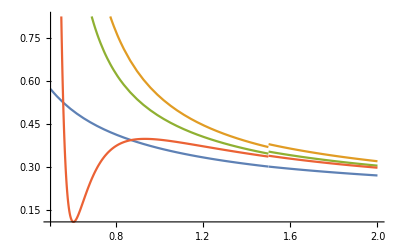

```mathematica
Plot[{αs1Loop[μ],αs2Loop[μ],αs3Loop[μ],αs[μ]},{μ,.5,2}]
```

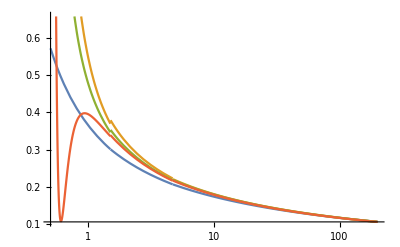

```mathematica
LogLinearPlot[{αs1Loop[μ],αs2Loop[μ],αs3Loop[μ],αs[μ]},{μ,.5,200}]
```

### μ

```mathematica
(* scale setting prescription: mu/mQ = fudge * alpha_s(mu), solved numerically for mu *)
```

#### LO

```mathematica
Clear[mu];
```

```mathematica
fudge=4;
```

```mathematica
(* Start Nf = 4 *)
```

```mathematica
Nf4α1Loopμ=Reverse@Table[Max[1,mu/.FindRoot[mu==fudge αs1Loop[mu]mQ,{mu,10}]],{mQ,Mc,Mb,(Mb-Mc)/7}]
```

{4.05254,3.74331,3.42818,3.1062,2.77611,2.43616,2.08379,1.715}

```mathematica
Nf4α1LoopMid=Table[αs1Loop[Nf4α1Loopμ[[k]]],{k,1,Length[Nf4α1Loopμ]}]
```

{0.21556,0.220566,0.22639,0.233299,0.241701,0.252265,0.266178,0.285833}

```mathematica
Nf4α1LoopStepTab=Round[4/(.2 Nf4α1LoopMid^2)]
```

{430,411,390,367,342,314,282,245}

```mathematica
Nf4α1LoopBig=Table[αs1Loop[1/2Nf4α1Loopμ[[k]]],{k,1,Length[Nf4α1Loopμ]}]
```

{0.268835,0.276665,0.28589,0.296997,0.311546,0.330832,0.357283,0.396841}

```mathematica
Nf4α1LoopSmall=Table[αs1Loop[2Nf4α1Loopμ[[k]]],{k,1,Length[Nf4α1Loopμ]}]
```

{0.181799,0.185058,0.188807,0.193197,0.198453,0.204935,0.213849,0.226354}

```mathematica
Length[DeleteDuplicates[Join[Nf4α1LoopMid,Nf4α1LoopBig,Nf4α1LoopSmall]]]
```

24

```mathematica
(* Start Nf = 5 *)
```

```mathematica
Nf5α1Loopμ=Reverse@Table[mu/.FindRoot[mu==fudge αs1Loop[mu]mQ,{mu,10}],{mQ,Mb,Mt,(Mt-Mb)/7}]
```

{83.1266,72.9651,62.6156,52.0329,41.1465,29.8326,17.822,4.05254}

```mathematica
Mt
```

173.34

```mathematica
Nf5α1LoopMid=Table[αs1Loop[Nf5α1Loopμ[[k]]],{k,1,Length[Nf5α1Loopμ]}]
```

{0.11989,0.122221,0.125074,0.128711,0.133637,0.141032,0.154751,0.21556}

```mathematica
Nf5α1LoopStepTab=Round[4/(.2 Nf5α1LoopMid^2)]
```

{1391,1339,1278,1207,1120,1006,835,430}

```mathematica
Nf5α1LoopBig=Table[αs1Loop[1/2Nf5α1Loopμ[[k]]],{k,1,Length[Nf5α1Loopμ]}]
```

{0.133418,0.136311,0.13987,0.144434,0.150667,0.160132,0.178055,0.268835}

```mathematica
Nf5α1LoopSmall=Table[αs1Loop[2Nf5α1Loopμ[[k]]],{k,1,Length[Nf5α1Loopμ]}]
```

{0.108852,0.11077,0.113109,0.116075,0.120067,0.126002,0.136841,0.181799}

```mathematica
Length[DeleteDuplicates[Join[Nf5α1LoopMid,Nf5α1LoopBig,Nf5α1LoopSmall]]]
```

24

```mathematica
Nf4α1LoopmQ=Reverse@Table[mQ,{mQ,Mc,Mb,(Mb-Mc)/7}]
```

{4.7,4.24286,3.78571,3.32857,2.87143,2.41429,1.95714,1.5}

```mathematica
Nf5α1LoopmQ=Reverse@Table[mQ,{mQ,Mb,Mt,(Mt-Mb)/7}]
```

{173.34,149.249,125.157,101.066,76.9743,52.8829,28.7914,4.7}

#### NLO

```mathematica
(* Start Nf = 4 *)
```

```mathematica
Nf4α2Loopμ=Reverse@Table[Max[1,mu/.FindRoot[mu==fudge αs2Loop[mu]mQ,{mu,10}]],{mQ,Mc,Mb,(Mb-Mc)/7}]
```

{4.31311,4.00065,3.68202,3.35624,3.02203,2.67764,2.32054,1.94685}

```mathematica
Nf4mQTab=Reverse@Table[mQ,{mQ,Mc,Mb,(Mb-Mc)/7}]
```

{4.7,4.24286,3.78571,3.32857,2.87143,2.41429,1.95714,1.5}

```mathematica
Nf4α2Loopμ/Nf4mQTab
```

{0.917683,0.942915,0.972609,1.00831,1.05245,1.10908,1.18568,1.2979}

```mathematica
2Nf4α2Loopμ/Nf4mQTab
```

{1.83537,1.88583,1.94522,2.01663,2.1049,2.21816,2.37136,2.5958}

```mathematica
1/2Nf4α2Loopμ/Nf4mQTab
```

{0.458842,0.471457,0.486305,0.504157,0.526225,0.554541,0.592839,0.648951}

```mathematica
Nf4α2LoopMid=Table[αs2Loop[Nf4α2Loopμ[[k]]],{k,1,Length[Nf4α2Loopμ]}]
```

{0.229421,0.235729,0.243152,0.252078,0.263112,0.277271,0.29642,0.324475}

```mathematica
Nf4α2LoopStepTab=Round[4/(.2 Nf4α2LoopMid^2)]
```

{380,360,338,315,289,260,228,190}

```mathematica
Nf4α2LoopBig=Table[αs2Loop[1/2Nf4α2Loopμ[[k]]],{k,1,Length[Nf4α2Loopμ]}]
```

{0.307437,0.319756,0.334731,0.353465,0.377818,0.404105,0.461228,0.564997}

```mathematica
Nf4α2LoopSmall=Table[αs2Loop[2Nf4α2Loopμ[[k]]],{k,1,Length[Nf4α2Loopμ]}]
```

{0.18711,0.190696,0.194827,0.199668,0.205469,0.212624,0.223621,0.238097}

```mathematica
Nf4α2LoopSmall[[-2]]=0.22362;
```

```mathematica
Length[DeleteDuplicates[Join[Nf4α2LoopMid,Nf4α2LoopBig,Nf4α2LoopSmall]]]
```

24

```mathematica
(* Start Nf = 5 *)
```

```mathematica
Nf5α2Loopμ=Reverse@Table[mu/.FindRoot[mu==fudge αs2Loop[mu]mQ,{mu,10}],{mQ,Mb,Mt,(Mt-Mb)/7}]
```

{83.4672,73.3356,63.0103,52.4444,41.5642,30.2405,18.1903,4.31311}

```mathematica
Mt
```

173.34

```mathematica
Nf5mQTab=Reverse@Table[mQ,{mQ,Mb,Mt,(Mt-Mb)/7}]
```

{173.34,149.249,125.157,101.066,76.9743,52.8829,28.7914,4.7}

```mathematica
Nf5α2Loopμ/Nf5mQTab
```

{0.481523,0.491366,0.50345,0.518914,0.539976,0.571839,0.631796,0.917683}

```mathematica
2Nf5α2Loopμ/Nf5mQTab
```

{0.963046,0.982731,1.0069,1.03783,1.07995,1.14368,1.26359,1.83537}

```mathematica
1/2Nf5α2Loopμ/Nf5mQTab
```

{0.240762,0.245683,0.251725,0.259457,0.269988,0.285919,0.315898,0.458842}

```mathematica
Nf5α2LoopMid=Table[αs2Loop[Nf5α2Loopμ[[k]]],{k,1,Length[Nf5α2Loopμ]}]
```

{0.120381,0.122841,0.125862,0.129728,0.134994,0.14296,0.157949,0.229421}

```mathematica
Nf5α2LoopStepTab=Round[4/(.2 Nf5α2LoopMid^2)]
```

{1380,1325,1263,1188,1097,979,802,380}

```mathematica
Nf5α2LoopBig=Table[αs2Loop[1/2Nf5α2Loopμ[[k]]],{k,1,Length[Nf5α2Loopμ]}]
```

{0.134898,0.138021,0.141879,0.146857,0.153712,0.164251,0.18467,0.307437}

```mathematica
Nf5α2LoopSmall=Table[αs2Loop[2Nf5α2Loopμ[[k]]],{k,1,Length[Nf5α2Loopμ]}]
```

{0.108756,0.110748,0.113181,0.116276,0.120457,0.126705,0.138215,0.18711}

```mathematica
Length[DeleteDuplicates[Join[Nf5α2LoopMid,Nf5α2LoopBig,Nf5α2LoopSmall]]]
```

24

```mathematica
Nf4α2LoopmQ=Reverse@Table[mQ,{mQ,Mc,Mb,(Mb-Mc)/7}]
```

{4.7,4.24286,3.78571,3.32857,2.87143,2.41429,1.95714,1.5}

```mathematica
Nf5α2LoopmQ=Reverse@Table[mQ,{mQ,Mb,Mt,(Mt-Mb)/7}]
```

{173.34,149.249,125.157,101.066,76.9743,52.8829,28.7914,4.7}

#### NNLO

```mathematica
(* Start Nf = 4 *)
```

```mathematica
Nf4α3Loopμ=Reverse@Table[Max[1,mu/.FindRoot[mu==fudge αs3Loop[mu]mQ,{mu,10}]],{mQ,Mc,Mb,(Mb-Mc)/7}]
```

{4.24177,3.9304,3.61282,3.28803,2.95474,2.61112,2.2546,1.88115}

```mathematica
Nf4α3LoopMid=Table[αs3Loop[Nf4α3Loopμ[[k]]],{k,1,Length[Nf4α3Loopμ]}]
```

{0.225626,0.231589,0.238582,0.246955,0.257253,0.270383,0.287996,0.313525}

```mathematica
Nf4α3LoopStepTab=Round[4/(.2 Nf4α3LoopMid^2)]
```

{393,373,351,328,302,274,241,203}

```mathematica
Nf4mQTab=Reverse@Table[mQ,{mQ,Mc,Mb,(Mb-Mc)/7}]
```

{4.7,4.24286,3.78571,3.32857,2.87143,2.41429,1.95714,1.5}

```mathematica
Nf4α2Loopμ/Nf4mQTab
```

{0.917683,0.942915,0.972609,1.00831,1.05245,1.10908,1.18568,1.2979}

```mathematica
2Nf4α2Loopμ/Nf4mQTab
```

{1.83537,1.88583,1.94522,2.01663,2.1049,2.21816,2.37136,2.5958}

```mathematica
1/2Nf4α2Loopμ/Nf4mQTab
```

{0.458842,0.471457,0.486305,0.504157,0.526225,0.554541,0.592839,0.648951}

```mathematica
Nf4α3LoopBig=Table[αs3Loop[1/2Nf4α3Loopμ[[k]]],{k,1,Length[Nf4α3Loopμ]}]
```

{0.296093,0.306917,0.319941,0.336039,0.34972,0.380431,0.426678,0.508047}

```mathematica
Nf4α3LoopSmall=Table[αs3Loop[2Nf4α3Loopμ[[k]]],{k,1,Length[Nf4α3Loopμ]}]
```

{0.187113,0.190693,0.194817,0.199654,0.205452,0.212612,0.221075,0.235162}

```mathematica
Length[DeleteDuplicates[Join[Nf4α3LoopMid,Nf4α3LoopBig,Nf4α3LoopSmall]]]
```

24

```mathematica
(* Start Nf = 5 *)
```

```mathematica
Nf5α3Loopμ=Reverse@Table[mu/.FindRoot[mu==fudge αs3Loop[mu]mQ,{mu,10}],{mQ,Mb,Mt,(Mt-Mb)/7}]
```

{83.4695,73.3338,63.0043,52.434,41.5493,30.2209,18.1659,4.24177}

```mathematica
Mt
```

173.34

```mathematica
Nf5mQTab=Reverse@Table[mQ,{mQ,Mb,Mt,(Mt-Mb)/7}]
```

{173.34,149.249,125.157,101.066,76.9743,52.8829,28.7914,4.7}

```mathematica
Nf5α3Loopμ/Nf5mQTab
```

{0.481536,0.491353,0.503401,0.518811,0.539782,0.571469,0.630948,0.902505}

```mathematica
2Nf5α3Loopμ/Nf5mQTab
```

{0.963073,0.982706,1.0068,1.03762,1.07956,1.14294,1.2619,1.80501}

```mathematica
1/2Nf5α3Loopμ/Nf5mQTab
```

{0.240768,0.245677,0.251701,0.259405,0.269891,0.285734,0.315474,0.451253}

```mathematica
Nf5α3LoopMid=Table[αs3Loop[Nf5α3Loopμ[[k]]],{k,1,Length[Nf5α3Loopμ]}]
```

{0.120384,0.122838,0.12585,0.129703,0.134945,0.142867,0.157737,0.225626}

```mathematica
Nf5α3LoopStepTab=Round[4/(.2 Nf5α3LoopMid^2)]
```

{1380,1325,1263,1189,1098,980,804,393}

```mathematica
Nf5α3LoopBig=Table[αs3Loop[1/2Nf5α3Loopμ[[k]]],{k,1,Length[Nf5α3Loopμ]}]
```

{0.134841,0.137946,0.14178,0.146722,0.153516,0.163936,0.184024,0.296093}

```mathematica
Nf5α3LoopSmall=Table[αs3Loop[2Nf5α3Loopμ[[k]]],{k,1,Length[Nf5α3Loopμ]}]
```

{0.108781,0.110771,0.113203,0.116293,0.120467,0.126701,0.138172,0.187113}

```mathematica
Length[DeleteDuplicates[Join[Nf5α3LoopMid,Nf5α3LoopBig,Nf5α3LoopSmall]]]
```

24

```mathematica
Nf4α3LoopmQ=Reverse@Table[mQ,{mQ,Mc,Mb,(Mb-Mc)/7}]
```

{4.7,4.24286,3.78571,3.32857,2.87143,2.41429,1.95714,1.5}

```mathematica
Nf5α3LoopmQ=Reverse@Table[mQ,{mQ,Mb,Mt,(Mt-Mb)/7}]
```

{173.34,149.249,125.157,101.066,76.9743,52.8829,28.7914,4.7}

### GFMC

```mathematica
datadir="~/Dropbox/heavy_quark_nuclei/data/";
```

```mathematica
plotdir="~/Dropbox/heavy_quark_nuclei/plots/";
```

```mathematica
NWalkers=200;
```

```mathematica
<<MaTeX`
```

```mathematica
markerlist={"□","○","△","▽","◇","▯","◦"};
```

```mathematica
frame[legend_]:=Framed[legend,FrameStyle->None,RoundingRadius->0,FrameMargins->0.2,Background->Directive[Lighter[LightGray,0.75]]]
```

```mathematica
OLegend=LineLegend[{Directive[ColorData[97][1]],Directive[ColorData[97][2]],Directive[ColorData[97][5]],Directive[ColorData[97][3]]},{MaTeX["\\text{LO}",Magnification->0.8],MaTeX["\\text{NLO}",Magnification->0.8],MaTeX["\\text{mNLO}",Magnification->0.8],MaTeX["\\text{NNLO}",Magnification->0.8]},LegendMarkers->{Style[markerlist[[1]],1,Bold,ColorData[97][1]],Style[markerlist[[2]],1,Bold,ColorData[97][2]],Style[markerlist[[5]],1,Bold,ColorData[97][5]],Style[markerlist[[3]],1,Bold,ColorData[97][3]]},LegendLayout->"Row",LegendMargins->0.5,LegendFunction->frame]
```

```mathematica
OLegend2=LineLegend[{Directive[ColorData[97][1]],Directive[ColorData[97][2]],Directive[ColorData[97][5]],Directive[ColorData[97][3]]},{MaTeX["\\text{LO}",Magnification->0.8],MaTeX["\\text{NLO}",Magnification->0.8],MaTeX["\\text{mNLO}",Magnification->0.8],MaTeX["\\text{NNLO}",Magnification->0.8]},LegendMarkers->{Style[markerlist[[1]],1,Bold,ColorData[97][1]],Style[markerlist[[2]],1,Bold,ColorData[97][2]],Style[markerlist[[5]],1,Bold,ColorData[97][5]],Style[markerlist[[3]],1,Bold,ColorData[97][3]]},LegendLayout->{"Row",2},LegendMargins->0.5,LegendFunction->frame]
```

### mesons

#### QCD LO - HWF

```mathematica
Nf4α1LoopMid
Nf4α1LoopStepTab={430,430,430,430,430};
NWalkers=200;
Nf4α1LoopBig={0.21556,0.21556,0.21556,0.21556,0.21556};
aList={1,2,3,4,5};
```

{0.21556,0.220566,0.22639,0.233299,0.241701,0.252265,0.266178,0.285833}

```mathematica
csvData=Table[Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfhwf.csv"],{xx,1,Length[aList]}]
```

({mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.020651606120431938, -0.020651606163699855, -0.02065160609026999, -0.020651606278458343, -0.020651605946710734, -0.02065160601659833, -0.020651605918701, -0.020651605899277285, -0.02065160593795202, -0.020651606236814155, -0.020651605919930743, -0.020651606018105846, -0.0206516059675632, -0.020651606085589167, -0.020651606003301338, -0.020651606016784826, -0.020651605893296537, -0.020651606160652956, -0.020651606015107543, -0.020651606065209768, -0.020651606164029262, -0.020651606186481732, -0.020651606409322096, -0.020651605962940064, -0.020651606224109477, -0.02065160592181054, -0.0206516060182455, -0.02065160608963958, -0.020651606201773736, -0.02065160612207125, -0.020651605887679784, -0.0206516061115175, -0.020651606079765884, -0.020651606283418517, -0.02065160575193911, -0.02065160599505216, -0.020651605965633757, -0.020651606250546933, -0.02065160630875807],[0.00012435669257052857, 0.0001400960332870177, 0.00015826208748808302, 0.00017617071813065638, 0.00019787306813251346, 0.00022718886389361056, 0.0002442275750470172, 0.0002715854538167454, 0.0002876914253184389, 0.0003016630205251561, 0.0003372306551992477, 0.0003614906768881743, 0.00038507914503085964, 0.00041511302601169583, 0.0004375621805276152, 0.0004637221161283931, 0.0004902609764804127, 0.0005363122311117627, 0.0005709282512631631, 0.0006104624988444667, 0.0006428196730677553, 0.0007048696426853197, 0.0007308766237543714, 0.0008021632507261597, 0.0008856678314661048, 0.0009167158299536264, 0.00098157528607375, 0.001026884153572301, 0.0011206555952540575, 0.0011434404793062365, 0.0012961072092510734, 0.0013457360124779604, 0.0014573929262532413, 0.0015609281514589884, 0.001643548994743555, 0.0017522967129235815, 0.0018293499786544982, 0.0019354523099484578, 0.0020856960117475675],-0.0206516,2.72239×10^-9,-0.0395014}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.014885335254786223, -0.01543954035924385, -0.015324621693788858, -0.015369054812785679, -0.015709074632725403, -0.015364473945685549, -0.015148867958172371, -0.015187842394793727, -0.015418981938952636, -0.015490404298300611, -0.015876884031362934, -0.016546221696478722, -0.016820225738510258, -0.01761029712166333, -0.016723522909291622, -0.016065520205709772, -0.015783696976514296, -0.01611375474706644, -0.017165936698366687, -0.016786953536103044, -0.017450619686027517, -0.01762322275627934, -0.017795638326476546, -0.01742990543569326, -0.018068464105156206, -0.017057071072175918, -0.018157722225936757, -0.018917787130091058, -0.019185286138899117, -0.017626071409899562, -0.019305081222243753, -0.020811821650176508, -0.018609317199932973, -0.017674402706128616, -0.01813244997199198, -0.01737460528377818, -0.016766634052370846, -0.016756593816540565, -0.01736300900463284],[0.0007083312139686332, 0.0010781001921554595, 0.0009387742699712603, 0.0009414988837993624, 0.0012815499180853938, 0.001006702354678856, 0.001026291086108978, 0.000990062942101436, 0.0011083585786416132, 0.001113628357329628, 0.0012736281743645596, 0.001854425565806045, 0.0019398654384468136, 0.002314753257517341, 0.0020553872287976875, 0.0018864379747331244, 0.0019316515070920985, 0.002054150030281514, 0.004024832663942563, 0.0025408327354409874, 0.002781759906400275, 0.002854110655753562, 0.0032738493284418368, 0.002969658312166297, 0.0033759777984594505, 0.0029135601430393732, 0.003688474828679538, 0.004410862708535197, 0.006086697333523144, 0.00426374319809847, 0.006603719153782798, 0.009827951603335461, 0.007434490210256244, 0.005374604281457969, 0.005837674215565812, 0.005844266970587013, 0.00547192536973429, 0.005308904727892724, 0.005934359784602388],-0.0135861,0.000179878,0.343337}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.010279588291747082, -0.010553246244567964, -0.01056324773839149, -0.010748204793431297, -0.011012559915441499, -0.012079951066674364, -0.012543192047665323, -0.01244961940995977, -0.012948047257127665, -0.012339967921462512, -0.012690034834398263, -0.01256291540877931, -0.014645762836156283, -0.01205938144741014, -0.012293918299848269, -0.012251867315291378, -0.011600423087408926, -0.012189851847430594, -0.011946483376521032, -0.012730722553036223, -0.013099890963956444, -0.013426460753232372, -0.012621231616142604, -0.012731508926469685, -0.013031312654204694, -0.012951908005786049, -0.013042021645502918, -0.013848005955986635, -0.01299487037018098, -0.013049740168911103, -0.013900635925089267, -0.013814358207094568, -0.014101651530242357, -0.014351604763521411, -0.014074662704971982, -0.013699857058759013, -0.01359079026007759, -0.013974503954736803, -0.014321062870966756],[0.0005015140116229212, 0.0006478208677610074, 0.0006111260775957936, 0.0006328768689829255, 0.0007966265369531195, 0.0012532995953030786, 0.0015926776970259327, 0.0015821808415920964, 0.0019760465029104958, 0.001687139589771621, 0.0018947788745130043, 0.002003292837745357, 0.004641280495795801, 0.0016319424232323367, 0.0018544720003744108, 0.0019550119331937497, 0.0015648515376317596, 0.00188297872277227, 0.0017568463378495206, 0.0028158524887475648, 0.0026610404319615095, 0.0036348564613253396, 0.0026101425976989816, 0.0026792104308640445, 0.002629984713015709, 0.002571353708625024, 0.002720931108867369, 0.0037783111262383005, 0.0027857324727469444, 0.0032964741999111217, 0.004713551549098054, 0.004044343669815628, 0.0040422796262394685, 0.004579571319390381, 0.004358187624674432, 0.003972145237438926, 0.004091775696022429, 0.004316467288724195, 0.004695149486529926],-0.00953158,0.000182188,0.184346}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.009256966271019516, -0.009414047736703362, -0.009723842526303619, -0.010455569805299126, -0.009603211844648508, -0.009352043205209007, -0.009425566327273543, -0.00954028814872877, -0.009493320823975991, -0.009669286633542976, -0.009707998463407209, -0.009887760530106855, -0.00981757614022308, -0.010073431778950656, -0.010009948963350017, -0.011447861831201379, -0.01103639951345615, -0.011630091691091814, -0.012856682508058659, -0.013394482445442616, -0.010848553319785613, -0.011493564732391055, -0.014102427371309874, -0.01305732153105178, -0.012027684359077426, -0.012080472211641583, -0.011255711745800489, -0.010972488606946556, -0.010802987251302403, -0.010602953945451413, -0.011108111014149168, -0.01178329295323098, -0.011853389735970242, -0.01173419694764093, -0.012208014474714262, -0.011603975306106365, -0.011869810772234137, -0.011611440614724177, -0.012600110125391951],[0.0006080483634407697, 0.0007070668666588711, 0.0009282822091971685, 0.0013775934982324365, 0.0008531462797823049, 0.0007295189972878061, 0.0007958194218263631, 0.000817631592468622, 0.0008287260256099079, 0.000886584273444082, 0.0009496373852571431, 0.0012122112358627793, 0.0011446244500667442, 0.0013154681115575058, 0.0014010749342188353, 0.0031541665013521967, 0.00279393552922966, 0.0031448551725809454, 0.004986550537422154, 0.006316527669876316, 0.002673931726882816, 0.0029934725725508523, 0.006289112918063586, 0.004829577818540915, 0.0036884426767992092, 0.0037333079338002194, 0.0030993987061994355, 0.0028177240513181153, 0.002816138249424306, 0.0027637181367163974, 0.003199434607661871, 0.004080012860305083, 0.004306462545457905, 0.004291820127956849, 0.005240529757856244, 0.004514875423704589, 0.004968273420469949, 0.004706188870385612, 0.006026824629947645],-0.00874792,0.000269121,0.0922548}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.007005310583592965, -0.007147717367109905, -0.007277182239700359, -0.007667178766504639, -0.0073494327408066265, -0.007513491579002323, -0.00751600778382285, -0.007649160485185563, -0.007784682126702769, -0.007664172837237561, -0.007899378651068106, -0.007824668776948863, -0.007736283070271346, -0.008030768878699008, -0.008117763528880407, -0.008004047884543208, -0.007580388229235523, -0.007893834514034593, -0.007874579122979956, -0.007785251629603384, -0.007885339065594946, -0.007796820630912519, -0.008117884568371132, -0.008560979725621138, -0.01000282227745194, -0.0111421223933707, -0.010143865806580363, -0.009722749380748975, -0.010038370787569377, -0.009702177348231679, -0.009027946839912624, -0.010554504468390468, -0.009915561696882083, -0.01128252412374607, -0.012464810454152347, -0.012143088795735772, -0.01172777620804158, -0.010403486257750255, -0.010382289730388664],[0.0003613261030397708, 0.00042438485116068754, 0.0004742675215689018, 0.0006617121457321808, 0.0005466712794720126, 0.000625071127876264, 0.0006528856797108374, 0.0006844584631336734, 0.0007749365664649808, 0.0006888670860560911, 0.0008424323510896726, 0.000782624861459738, 0.0007479445278772535, 0.0009487429241193719, 0.000992948259036462, 0.0009717331007456051, 0.0007831545220730126, 0.0009636214339987536, 0.0009326522128139752, 0.0009474046760421579, 0.001018894960358435, 0.000994251957764668, 0.0012066808344333825, 0.0016991768073155197, 0.0027562116419949287, 0.003700666532524095, 0.0028111348906777237, 0.0025399678993560234, 0.0029916174665310692, 0.002728973131444488, 0.002204433160600752, 0.004248757345471586, 0.003129443548782169, 0.004682724510157776, 0.006816834264455937, 0.0071203516025347075, 0.006409415334563613, 0.0043909630799604344, 0.004464283856786818],-0.0065443,0.000187514,0.0795995})

```mathematica
meanErr=Table[Table[csvData[[xx,2,yy]]//StringSplit[#,{",","[","]"}]&,{yy,1,2}],{xx,1,Length[aList]}]
```

({-0.020651606120431938, -0.020651606163699855, -0.02065160609026999, -0.020651606278458343, -0.020651605946710734, -0.02065160601659833, -0.020651605918701, -0.020651605899277285, -0.02065160593795202, -0.020651606236814155, -0.020651605919930743, -0.020651606018105846, -0.0206516059675632, -0.020651606085589167, -0.020651606003301338, -0.020651606016784826, -0.020651605893296537, -0.020651606160652956, -0.020651606015107543, -0.020651606065209768, -0.020651606164029262, -0.020651606186481732, -0.020651606409322096, -0.020651605962940064, -0.020651606224109477, -0.02065160592181054, -0.0206516060182455, -0.02065160608963958, -0.020651606201773736, -0.02065160612207125, -0.020651605887679784, -0.0206516061115175, -0.020651606079765884, -0.020651606283418517, -0.02065160575193911, -0.02065160599505216, -0.020651605965633757, -0.020651606250546933, -0.02065160630875807} | {0.00012435669257052857, 0.0001400960332870177, 0.00015826208748808302, 0.00017617071813065638, 0.00019787306813251346, 0.00022718886389361056, 0.0002442275750470172, 0.0002715854538167454, 0.0002876914253184389, 0.0003016630205251561, 0.0003372306551992477, 0.0003614906768881743, 0.00038507914503085964, 0.00041511302601169583, 0.0004375621805276152, 0.0004637221161283931, 0.0004902609764804127, 0.0005363122311117627, 0.0005709282512631631, 0.0006104624988444667, 0.0006428196730677553, 0.0007048696426853197, 0.0007308766237543714, 0.0008021632507261597, 0.0008856678314661048, 0.0009167158299536264, 0.00098157528607375, 0.001026884153572301, 0.0011206555952540575, 0.0011434404793062365, 0.0012961072092510734, 0.0013457360124779604, 0.0014573929262532413, 0.0015609281514589884, 0.001643548994743555, 0.0017522967129235815, 0.0018293499786544982, 0.0019354523099484578, 0.0020856960117475675}
{-0.014885335254786223, -0.01543954035924385, -0.015324621693788858, -0.015369054812785679, -0.015709074632725403, -0.015364473945685549, -0.015148867958172371, -0.015187842394793727, -0.015418981938952636, -0.015490404298300611, -0.015876884031362934, -0.016546221696478722, -0.016820225738510258, -0.01761029712166333, -0.016723522909291622, -0.016065520205709772, -0.015783696976514296, -0.01611375474706644, -0.017165936698366687, -0.016786953536103044, -0.017450619686027517, -0.01762322275627934, -0.017795638326476546, -0.01742990543569326, -0.018068464105156206, -0.017057071072175918, -0.018157722225936757, -0.018917787130091058, -0.019185286138899117, -0.017626071409899562, -0.019305081222243753, -0.020811821650176508, -0.018609317199932973, -0.017674402706128616, -0.01813244997199198, -0.01737460528377818, -0.016766634052370846, -0.016756593816540565, -0.01736300900463284} | {0.0007083312139686332, 0.0010781001921554595, 0.0009387742699712603, 0.0009414988837993624, 0.0012815499180853938, 0.001006702354678856, 0.001026291086108978, 0.000990062942101436, 0.0011083585786416132, 0.001113628357329628, 0.0012736281743645596, 0.001854425565806045, 0.0019398654384468136, 0.002314753257517341, 0.0020553872287976875, 0.0018864379747331244, 0.0019316515070920985, 0.002054150030281514, 0.004024832663942563, 0.0025408327354409874, 0.002781759906400275, 0.002854110655753562, 0.0032738493284418368, 0.002969658312166297, 0.0033759777984594505, 0.0029135601430393732, 0.003688474828679538, 0.004410862708535197, 0.006086697333523144, 0.00426374319809847, 0.006603719153782798, 0.009827951603335461, 0.007434490210256244, 0.005374604281457969, 0.005837674215565812, 0.005844266970587013, 0.00547192536973429, 0.005308904727892724, 0.005934359784602388}
{-0.010279588291747082, -0.010553246244567964, -0.01056324773839149, -0.010748204793431297, -0.011012559915441499, -0.012079951066674364, -0.012543192047665323, -0.01244961940995977, -0.012948047257127665, -0.012339967921462512, -0.012690034834398263, -0.01256291540877931, -0.014645762836156283, -0.01205938144741014, -0.012293918299848269, -0.012251867315291378, -0.011600423087408926, -0.012189851847430594, -0.011946483376521032, -0.012730722553036223, -0.013099890963956444, -0.013426460753232372, -0.012621231616142604, -0.012731508926469685, -0.013031312654204694, -0.012951908005786049, -0.013042021645502918, -0.013848005955986635, -0.01299487037018098, -0.013049740168911103, -0.013900635925089267, -0.013814358207094568, -0.014101651530242357, -0.014351604763521411, -0.014074662704971982, -0.013699857058759013, -0.01359079026007759, -0.013974503954736803, -0.014321062870966756} | {0.0005015140116229212, 0.0006478208677610074, 0.0006111260775957936, 0.0006328768689829255, 0.0007966265369531195, 0.0012532995953030786, 0.0015926776970259327, 0.0015821808415920964, 0.0019760465029104958, 0.001687139589771621, 0.0018947788745130043, 0.002003292837745357, 0.004641280495795801, 0.0016319424232323367, 0.0018544720003744108, 0.0019550119331937497, 0.0015648515376317596, 0.00188297872277227, 0.0017568463378495206, 0.0028158524887475648, 0.0026610404319615095, 0.0036348564613253396, 0.0026101425976989816, 0.0026792104308640445, 0.002629984713015709, 0.002571353708625024, 0.002720931108867369, 0.0037783111262383005, 0.0027857324727469444, 0.0032964741999111217, 0.004713551549098054, 0.004044343669815628, 0.0040422796262394685, 0.004579571319390381, 0.004358187624674432, 0.003972145237438926, 0.004091775696022429, 0.004316467288724195, 0.004695149486529926}
{-0.009256966271019516, -0.009414047736703362, -0.009723842526303619, -0.010455569805299126, -0.009603211844648508, -0.009352043205209007, -0.009425566327273543, -0.00954028814872877, -0.009493320823975991, -0.009669286633542976, -0.009707998463407209, -0.009887760530106855, -0.00981757614022308, -0.010073431778950656, -0.010009948963350017, -0.011447861831201379, -0.01103639951345615, -0.011630091691091814, -0.012856682508058659, -0.013394482445442616, -0.010848553319785613, -0.011493564732391055, -0.014102427371309874, -0.01305732153105178, -0.012027684359077426, -0.012080472211641583, -0.011255711745800489, -0.010972488606946556, -0.010802987251302403, -0.010602953945451413, -0.011108111014149168, -0.01178329295323098, -0.011853389735970242, -0.01173419694764093, -0.012208014474714262, -0.011603975306106365, -0.011869810772234137, -0.011611440614724177, -0.012600110125391951} | {0.0006080483634407697, 0.0007070668666588711, 0.0009282822091971685, 0.0013775934982324365, 0.0008531462797823049, 0.0007295189972878061, 0.0007958194218263631, 0.000817631592468622, 0.0008287260256099079, 0.000886584273444082, 0.0009496373852571431, 0.0012122112358627793, 0.0011446244500667442, 0.0013154681115575058, 0.0014010749342188353, 0.0031541665013521967, 0.00279393552922966, 0.0031448551725809454, 0.004986550537422154, 0.006316527669876316, 0.002673931726882816, 0.0029934725725508523, 0.006289112918063586, 0.004829577818540915, 0.0036884426767992092, 0.0037333079338002194, 0.0030993987061994355, 0.0028177240513181153, 0.002816138249424306, 0.0027637181367163974, 0.003199434607661871, 0.004080012860305083, 0.004306462545457905, 0.004291820127956849, 0.005240529757856244, 0.004514875423704589, 0.004968273420469949, 0.004706188870385612, 0.006026824629947645}
{-0.007005310583592965, -0.007147717367109905, -0.007277182239700359, -0.007667178766504639, -0.0073494327408066265, -0.007513491579002323, -0.00751600778382285, -0.007649160485185563, -0.007784682126702769, -0.007664172837237561, -0.007899378651068106, -0.007824668776948863, -0.007736283070271346, -0.008030768878699008, -0.008117763528880407, -0.008004047884543208, -0.007580388229235523, -0.007893834514034593, -0.007874579122979956, -0.007785251629603384, -0.007885339065594946, -0.007796820630912519, -0.008117884568371132, -0.008560979725621138, -0.01000282227745194, -0.0111421223933707, -0.010143865806580363, -0.009722749380748975, -0.010038370787569377, -0.009702177348231679, -0.009027946839912624, -0.010554504468390468, -0.009915561696882083, -0.01128252412374607, -0.012464810454152347, -0.012143088795735772, -0.01172777620804158, -0.010403486257750255, -0.010382289730388664} | {0.0003613261030397708, 0.00042438485116068754, 0.0004742675215689018, 0.0006617121457321808, 0.0005466712794720126, 0.000625071127876264, 0.0006528856797108374, 0.0006844584631336734, 0.0007749365664649808, 0.0006888670860560911, 0.0008424323510896726, 0.000782624861459738, 0.0007479445278772535, 0.0009487429241193719, 0.000992948259036462, 0.0009717331007456051, 0.0007831545220730126, 0.0009636214339987536, 0.0009326522128139752, 0.0009474046760421579, 0.001018894960358435, 0.000994251957764668, 0.0012066808344333825, 0.0016991768073155197, 0.0027562116419949287, 0.003700666532524095, 0.0028111348906777237, 0.0025399678993560234, 0.0029916174665310692, 0.002728973131444488, 0.002204433160600752, 0.004248757345471586, 0.003129443548782169, 0.004682724510157776, 0.006816834264455937, 0.0071203516025347075, 0.006409415334563613, 0.0043909630799604344, 0.004464283856786818})

```mathematica
meanErr[[1,2,1]]//ToExpression
```

0.000124357

```mathematica
meanErr[[1]]
```

(-0.020651606120431938 |  -0.020651606163699855 |  -0.02065160609026999 |  -0.020651606278458343 |  -0.020651605946710734 |  -0.02065160601659833 |  -0.020651605918701 |  -0.020651605899277285 |  -0.02065160593795202 |  -0.020651606236814155 |  -0.020651605919930743 |  -0.020651606018105846 |  -0.0206516059675632 |  -0.020651606085589167 |  -0.020651606003301338 |  -0.020651606016784826 |  -0.020651605893296537 |  -0.020651606160652956 |  -0.020651606015107543 |  -0.020651606065209768 |  -0.020651606164029262 |  -0.020651606186481732 |  -0.020651606409322096 |  -0.020651605962940064 |  -0.020651606224109477 |  -0.02065160592181054 |  -0.0206516060182455 |  -0.02065160608963958 |  -0.020651606201773736 |  -0.02065160612207125 |  -0.020651605887679784 |  -0.0206516061115175 |  -0.020651606079765884 |  -0.020651606283418517 |  -0.02065160575193911 |  -0.02065160599505216 |  -0.020651605965633757 |  -0.020651606250546933 |  -0.02065160630875807
0.00012435669257052857 |  0.0001400960332870177 |  0.00015826208748808302 |  0.00017617071813065638 |  0.00019787306813251346 |  0.00022718886389361056 |  0.0002442275750470172 |  0.0002715854538167454 |  0.0002876914253184389 |  0.0003016630205251561 |  0.0003372306551992477 |  0.0003614906768881743 |  0.00038507914503085964 |  0.00041511302601169583 |  0.0004375621805276152 |  0.0004637221161283931 |  0.0004902609764804127 |  0.0005363122311117627 |  0.0005709282512631631 |  0.0006104624988444667 |  0.0006428196730677553 |  0.0007048696426853197 |  0.0007308766237543714 |  0.0008021632507261597 |  0.0008856678314661048 |  0.0009167158299536264 |  0.00098157528607375 |  0.001026884153572301 |  0.0011206555952540575 |  0.0011434404793062365 |  0.0012961072092510734 |  0.0013457360124779604 |  0.0014573929262532413 |  0.0015609281514589884 |  0.001643548994743555 |  0.0017522967129235815 |  0.0018293499786544982 |  0.0019354523099484578 |  0.0020856960117475675)

```mathematica
meanErr2=Table[Table[Around[meanErr[[xx,1,yy]]//ToExpression,meanErr[[xx,2,yy]]//ToExpression],{yy,1,Length[meanErr[[xx,1]]]}],{xx,1,Length[aList]}]
```

(-0.020650.00012 | -0.020650.00014 | -0.020650.00016 | -0.020650.00018 | -0.020650.00020 | -0.020650.00023 | -0.020650.00024 | -0.020650.00027 | -0.020650.00029 | -0.020650.00030 | -0.020650.00034 | -0.02070.0004 | -0.02070.0004 | -0.02070.0004 | -0.02070.0004 | -0.02070.0005 | -0.02070.0005 | -0.02070.0005 | -0.02070.0006 | -0.02070.0006 | -0.02070.0006 | -0.02070.0007 | -0.02070.0007 | -0.02070.0008 | -0.02070.0009 | -0.02070.0009 | -0.02070.0010 | -0.02070.0010 | -0.02070.0011 | -0.02070.0011 | -0.02070.0013 | -0.02070.0013 | -0.02070.0015 | -0.02070.0016 | -0.02070.0016 | -0.02070.0018 | -0.02070.0018 | -0.02070.0019 | -0.02070.0021
-0.01490.0007 | -0.01540.0011 | -0.01530.0009 | -0.01540.0009 | -0.01570.0013 | -0.01540.0010 | -0.01510.0010 | -0.01520.0010 | -0.01540.0011 | -0.01550.0011 | -0.01590.0013 | -0.01650.0019 | -0.01680.0019 | -0.01760.0023 | -0.01670.0021 | -0.01610.0019 | -0.01580.0019 | -0.01610.0021 | -0.0170.004 | -0.01680.0025 | -0.01750.0028 | -0.01760.0029 | -0.01780.0033 | -0.01740.0030 | -0.01810.0034 | -0.01710.0029 | -0.0180.004 | -0.0190.004 | -0.0190.006 | -0.0180.004 | -0.0190.007 | -0.0210.010 | -0.0190.007 | -0.0180.005 | -0.0180.006 | -0.0170.006 | -0.0170.005 | -0.0170.005 | -0.0170.006
-0.01030.0005 | -0.01060.0006 | -0.01060.0006 | -0.01070.0006 | -0.01100.0008 | -0.01210.0013 | -0.01250.0016 | -0.01240.0016 | -0.01290.0020 | -0.01230.0017 | -0.01270.0019 | -0.01260.0020 | -0.0150.005 | -0.01210.0016 | -0.01230.0019 | -0.01230.0020 | -0.01160.0016 | -0.01220.0019 | -0.01190.0018 | -0.01270.0028 | -0.01310.0027 | -0.0130.004 | -0.01260.0026 | -0.01270.0027 | -0.01300.0026 | -0.01300.0026 | -0.01300.0027 | -0.0140.004 | -0.01300.0028 | -0.01300.0033 | -0.0140.005 | -0.0140.004 | -0.0140.004 | -0.0140.005 | -0.0140.004 | -0.0140.004 | -0.0140.004 | -0.0140.004 | -0.0140.005
-0.00930.0006 | -0.00940.0007 | -0.00970.0009 | -0.01050.0014 | -0.00960.0009 | -0.00940.0007 | -0.00940.0008 | -0.00950.0008 | -0.00950.0008 | -0.00970.0009 | -0.00970.0009 | -0.00990.0012 | -0.00980.0011 | -0.01010.0013 | -0.01000.0014 | -0.01140.0032 | -0.01100.0028 | -0.01160.0031 | -0.0130.005 | -0.0130.006 | -0.01080.0027 | -0.01150.0030 | -0.0140.006 | -0.0130.005 | -0.0120.004 | -0.0120.004 | -0.01130.0031 | -0.01100.0028 | -0.01080.0028 | -0.01060.0028 | -0.01110.0032 | -0.0120.004 | -0.0120.004 | -0.0120.004 | -0.0120.005 | -0.0120.005 | -0.0120.005 | -0.0120.005 | -0.0130.006
-0.00700.0004 | -0.00710.0004 | -0.00730.0005 | -0.00770.0007 | -0.00730.0005 | -0.00750.0006 | -0.00750.0007 | -0.00760.0007 | -0.00780.0008 | -0.00770.0007 | -0.00790.0008 | -0.00780.0008 | -0.00770.0007 | -0.00800.0009 | -0.00810.0010 | -0.00800.0010 | -0.00760.0008 | -0.00790.0010 | -0.00790.0009 | -0.00780.0009 | -0.00790.0010 | -0.00780.0010 | -0.00810.0012 | -0.00860.0017 | -0.01000.0028 | -0.0110.004 | -0.01010.0028 | -0.00970.0025 | -0.01000.0030 | -0.00970.0027 | -0.00900.0022 | -0.0110.004 | -0.00990.0031 | -0.0110.005 | -0.0120.007 | -0.0120.007 | -0.0120.006 | -0.0100.004 | -0.0100.004)

```mathematica
τSteps=Table[Table[xx,{xx,1,Length[meanErr2[[yy]]]}],{yy,1,Length[meanErr2]}]
```

(1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39)

```mathematica
fitData=Table[Around[Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfhwf.csv"][[2,3]],Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfhwf.csv"][[2,4]]],{xx,1,Length[aList]}]
```

{-0.020651612227,-0.013590.00018,-0.009530.00018,-0.008750.00027,-0.006540.00019}

```mathematica
αLegendLO=PointLegend[Table[Directive[ColorData[97][1]],{ii,5}],{MaTeX["a=1",Magnification->0.8],MaTeX["a=2",Magnification->0.8],MaTeX["a=3",Magnification->0.8],MaTeX["a=4",Magnification->0.8],MaTeX["a=5",Magnification->0.8]},LegendMarkers->Table[Style[markerlist[[ii]],14,Bold,ColorData[97][3]],{ii,5}],LegendLayout->"Row",LegendMargins->0.5,LegendFunction->frame]
```

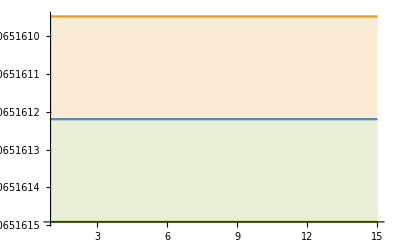

```mathematica
Plot[{fitData[[1]]//.Around[x_,y_]:>x,{fitData[[1]]//.Around[x_,y_]:>x+y,fitData[[1]]//.Around[x_,y_]:>x-y}},{x,1,15},Filling->{3->{1},2->{1}}]
```

```mathematica
SpoilHWFLOPlotN3=Show[Plot[{fitData[[1]]//.Around[x_,y_]:>x,{fitData[[1]]//.Around[x_,y_]:>x+y,fitData[[1]]//.Around[x_,y_]:>x-y}},{x,1,Length[meanErr2[[5]]]},Filling->{3->{1},2->{1}},PlotRange->{-.03,-0.005}],ListPlot[{Table[{τSteps[[1,i]],meanErr2[[1,i]]},{i,1,Length[meanErr2[[1]]]}],Table[{τSteps[[2,i]],meanErr2[[2,i]]},{i,1,Length[meanErr2[[2]]]}],Table[{τSteps[[3,i]],meanErr2[[3,i]]},{i,1,Length[meanErr2[[3]]]}],Table[{τSteps[[4,i]],meanErr2[[4,i]]},{i,1,Length[meanErr2[[4]]]}],Table[{τSteps[[5,i]],meanErr2[[5,i]]},{i,1,Length[meanErr2[[5]]]}]},PlotRange->{-.03,-0.005},PlotLegends->Placed[αLegendLO,{0.5,0.1}],PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]],markerlist[[4]],markerlist[[5]]},IntervalMarkersStyle->{ColorData[97][3]},PlotStyle->{ColorData[97][3]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau_{\\text{steps}}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]},PlotLabel->MaTeX["N=3\\text{ (LO)}",Magnification->1.2]]
```

-Graphics-

#### QCD NLO - HWF

```mathematica
Nf4α1LoopMid
Nf4α1LoopStepTab={380,380,380,380,380};
NWalkers=200;
Nf4α1LoopBig={0.229421,0.229421,0.229421,0.229421,0.229421};
aList={1,2,3,4,5};
```

{0.21556,0.220566,0.22639,0.233299,0.241701,0.252265,0.266178,0.285833}

```mathematica
csvData=Table[Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfhwf.csv"],{xx,1,Length[aList]}]
```

({mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.06243743487622722, -0.061277059264155234, -0.06103213303463864, -0.06121267131295004, -0.06150316869650005, -0.06245530652406114, -0.061820418642356864, -0.06247230495200883, -0.0636586155575951, -0.06305645860398736, -0.06271986202430894, -0.06220635187131472, -0.06169473414663755, -0.0632995433675689, -0.06204773119593652, -0.060825312129654, -0.06085237215278242, -0.06130107802637401, -0.060958815803012524, -0.06150042327597604, -0.06098210075759762, -0.060639012346678484, -0.06094905794549459, -0.061165810247371714],[0.01644638420820033, 0.01762063328322738, 0.020246927414812495, 0.023757458688389896, 0.028956785820066513, 0.03330450378016059, 0.038565326777768416, 0.045172235794539134, 0.05357126930206856, 0.05951076473991144, 0.06692233074680325, 0.07185311882213304, 0.08209816345190214, 0.0989896279554691, 0.10753090460914662, 0.11701723058652057, 0.13759580073421507, 0.16593854817336734, 0.18672547941059678, 0.2167204920015551, 0.2390179454198962, 0.28195631083348527, 0.32585813006476794, 0.3640585998236021],-0.0569784,0.00030032,1.43158}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.041910842130013115, -0.043384174114471756, -0.043380734392262095, -0.04417524319870145, -0.04529725014574181, -0.04643980623777406, -0.04868141752180084, -0.04859803252157384, -0.04877187354674868, -0.056713214123877795, -0.05390570581398252, -0.057728277462907505, -0.06910159469438726, -0.05730281746457964, -0.0541711462915397, -0.05547454028587835, -0.05436534141297973, -0.05846384623981779, -0.056685273728154066, -0.056653943360602664, -0.05756474601242202, -0.05699622663672152, -0.05534758052648825, -0.052882550138016744, -0.055114777694789285, -0.05473034415871547, -0.0561342719988812, -0.05283489295490819, -0.052130340163567226, -0.054227774908200264, -0.057686256019777005, -0.059507441528145306, -0.05272082860086137, -0.052829867470074364, -0.054304851096842514],[0.0030556771802128556, 0.0039256456129601654, 0.004581735184682181, 0.005651092413749335, 0.006451911412315093, 0.008042445537525015, 0.010245890996375686, 0.011509020052402024, 0.01510255921369091, 0.030546032263234713, 0.02607858480984139, 0.03510053895167623, 0.06955691780010664, 0.04906808435091355, 0.04819093793533578, 0.05868877837800419, 0.05717865146058226, 0.08109888266472198, 0.07895835252875041, 0.08777139018860432, 0.11415627061500412, 0.1207906049159817, 0.12554963060544996, 0.13261910154608297, 0.1498698107853654, 0.16709174180375355, 0.20398535059775097, 0.20332884998367506, 0.22236829697209248, 0.27858210563349817, 0.35088005736543904, 0.438238722583996, 0.3813560184071134, 0.43767036954458893, 0.4931593502175728],-0.0449777,0.000696634,0.539351}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.03109154451122602, -0.03186797025269724, -0.031491172417657115, -0.032486845139277624, -0.03260197646549268, -0.03315440549022298, -0.035283050309139474, -0.03582530005091983, -0.03500157032156107, -0.035767740291135414, -0.03812024314448928, -0.038464960177569014, -0.04095460671826447, -0.038708871140485886, -0.04141358076137606, -0.041257887400357844, -0.04213787622507001, -0.04048093945599635, -0.045288207895282394, -0.045842360891093496, -0.04356697222940343, -0.04728166989326719, -0.04630639698494024, -0.04753315681710249, -0.049914918963926226, -0.05189016599428966, -0.06116476631152095, -0.054339161896725496, -0.055158380769095336, -0.05313697442630628, -0.05726735713992977, -0.056090182685062745, -0.0520797360653924, -0.05289575657587033, -0.05760065380610733],[0.0021185227432379784, 0.0024101362778032195, 0.002622509235870586, 0.0034158981333221442, 0.0035756934505891368, 0.004208013564632555, 0.006078329085970632, 0.0068989190050611476, 0.006604220206608742, 0.007621240275003937, 0.01083409794773567, 0.0120272075051741, 0.01822353315198682, 0.014297770677186062, 0.020378248953131124, 0.021689907223974396, 0.024818495748557677, 0.023107397735877413, 0.03414633893571729, 0.03929371671619317, 0.036602587684658704, 0.05078710347042431, 0.053833222973279526, 0.06642697036121586, 0.07596502436307187, 0.09311650469789542, 0.14653578549224122, 0.1325797071075591, 0.15003078345175996, 0.17103237726338322, 0.207231063446023, 0.23095737723741883, 0.22701276099908696, 0.25777951991809805, 0.3471743774355525],-0.034087,0.000829158,0.497733}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.025377354497499817, -0.027507076788232974, -0.026669469030130066, -0.027308319557325687, -0.026733864069876975, -0.02732385820520183, -0.028420183966203577, -0.02825161700068508, -0.029317736748963673, -0.030066199297794624, -0.03171388422504598, -0.03204306810471766, -0.03345832658073344, -0.03290210815271129, -0.03325594420306428, -0.03471487660125802, -0.034173367667662435, -0.036541350776406786, -0.03643711667132005, -0.041202475320609694, -0.03929296366323175, -0.04187526435924109, -0.0401182960934586, -0.046575560926817305, -0.04522578860890086, -0.0460473887096579, -0.05098331007252792, -0.062333084449743476, -0.05996857826459409, -0.06937326085856126, -0.062488186401808754, -0.06217543190432157, -0.04780876747385358, -0.047580751531650735, -0.05448340174769356],[0.0020138575355545594, 0.0037129757749207472, 0.0028392264903821596, 0.0033593713674799847, 0.00330471219967556, 0.003986182413564681, 0.005532286418429784, 0.004965621094818469, 0.006254810401052685, 0.007392683168754082, 0.010784739912389428, 0.010723013870712025, 0.014587992151005707, 0.013424409691333433, 0.01417210520641096, 0.017832657551058374, 0.017428773253604906, 0.022430540346769348, 0.022479627418629307, 0.03396511904507371, 0.03174904861794163, 0.04158109321227251, 0.04286051930781298, 0.06808292589709153, 0.0699854720399574, 0.09074944083499867, 0.12095093906157045, 0.22277970713320788, 0.22567588726345342, 0.39013394701410503, 0.3771281154609525, 0.37330484674800146, 0.27284577181550035, 0.3072514652525699, 0.4310453448185155],-0.0241058,0.000742929,0.395525}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.023069124456011236, -0.02271620497201024, -0.022624065900273608, -0.022525350432509028, -0.02211971864693854, -0.02247912630164753, -0.023879941746847353, -0.025033252237081933, -0.026647254417577513, -0.026968745365298443, -0.027632195270619903, -0.027428280337147008, -0.02682317550059181, -0.02879515123298829, -0.03143287111830849, -0.03270707338390568, -0.033537226390686736, -0.03608213050879545, -0.03726965233542205, -0.04242381017951394, -0.03941304855131035, -0.03879697569670403, -0.04040450561431004, -0.0426482956296991, -0.04581088552691992, -0.04567206043412583, -0.043117090644495336, -0.038940525389734, -0.03734571947127331, -0.04206007487488008, -0.04392381769413392, -0.04052335962135884, -0.036747448419978325, -0.037627997702394285, -0.039577340803798676],[0.00342471662152276, 0.003405983388250459, 0.003577230018328401, 0.003939184829536931, 0.003498211299966693, 0.003833532073685978, 0.005607998043013167, 0.00677958709591595, 0.00860916725880274, 0.008843337291445494, 0.009909460357976971, 0.010458397720443036, 0.01043011603239101, 0.013244914091903119, 0.01808093365174119, 0.021923480859066785, 0.024893654181447712, 0.03148818926929396, 0.037515150820626154, 0.05217016500362093, 0.04794016356906137, 0.050300267746282705, 0.0598612884502901, 0.07988686369625721, 0.103404222694315, 0.11458987384456606, 0.11684678524197648, 0.1030676742403413, 0.09925875224289187, 0.14019338425563288, 0.17123951647747523, 0.16118203615826102, 0.15167579700353762, 0.16871233769270866, 0.2147274427772425],-0.0199081,0.000736702,0.326713})

```mathematica
meanErr=Table[Table[csvData[[xx,2,yy]]//StringSplit[#,{",","[","]"}]&,{yy,1,2}],{xx,1,Length[aList]}]
```

({-0.06243743487622722, -0.061277059264155234, -0.06103213303463864, -0.06121267131295004, -0.06150316869650005, -0.06245530652406114, -0.061820418642356864, -0.06247230495200883, -0.0636586155575951, -0.06305645860398736, -0.06271986202430894, -0.06220635187131472, -0.06169473414663755, -0.0632995433675689, -0.06204773119593652, -0.060825312129654, -0.06085237215278242, -0.06130107802637401, -0.060958815803012524, -0.06150042327597604, -0.06098210075759762, -0.060639012346678484, -0.06094905794549459, -0.061165810247371714} | {0.01644638420820033, 0.01762063328322738, 0.020246927414812495, 0.023757458688389896, 0.028956785820066513, 0.03330450378016059, 0.038565326777768416, 0.045172235794539134, 0.05357126930206856, 0.05951076473991144, 0.06692233074680325, 0.07185311882213304, 0.08209816345190214, 0.0989896279554691, 0.10753090460914662, 0.11701723058652057, 0.13759580073421507, 0.16593854817336734, 0.18672547941059678, 0.2167204920015551, 0.2390179454198962, 0.28195631083348527, 0.32585813006476794, 0.3640585998236021}
{-0.041910842130013115, -0.043384174114471756, -0.043380734392262095, -0.04417524319870145, -0.04529725014574181, -0.04643980623777406, -0.04868141752180084, -0.04859803252157384, -0.04877187354674868, -0.056713214123877795, -0.05390570581398252, -0.057728277462907505, -0.06910159469438726, -0.05730281746457964, -0.0541711462915397, -0.05547454028587835, -0.05436534141297973, -0.05846384623981779, -0.056685273728154066, -0.056653943360602664, -0.05756474601242202, -0.05699622663672152, -0.05534758052648825, -0.052882550138016744, -0.055114777694789285, -0.05473034415871547, -0.0561342719988812, -0.05283489295490819, -0.052130340163567226, -0.054227774908200264, -0.057686256019777005, -0.059507441528145306, -0.05272082860086137, -0.052829867470074364, -0.054304851096842514} | {0.0030556771802128556, 0.0039256456129601654, 0.004581735184682181, 0.005651092413749335, 0.006451911412315093, 0.008042445537525015, 0.010245890996375686, 0.011509020052402024, 0.01510255921369091, 0.030546032263234713, 0.02607858480984139, 0.03510053895167623, 0.06955691780010664, 0.04906808435091355, 0.04819093793533578, 0.05868877837800419, 0.05717865146058226, 0.08109888266472198, 0.07895835252875041, 0.08777139018860432, 0.11415627061500412, 0.1207906049159817, 0.12554963060544996, 0.13261910154608297, 0.1498698107853654, 0.16709174180375355, 0.20398535059775097, 0.20332884998367506, 0.22236829697209248, 0.27858210563349817, 0.35088005736543904, 0.438238722583996, 0.3813560184071134, 0.43767036954458893, 0.4931593502175728}
{-0.03109154451122602, -0.03186797025269724, -0.031491172417657115, -0.032486845139277624, -0.03260197646549268, -0.03315440549022298, -0.035283050309139474, -0.03582530005091983, -0.03500157032156107, -0.035767740291135414, -0.03812024314448928, -0.038464960177569014, -0.04095460671826447, -0.038708871140485886, -0.04141358076137606, -0.041257887400357844, -0.04213787622507001, -0.04048093945599635, -0.045288207895282394, -0.045842360891093496, -0.04356697222940343, -0.04728166989326719, -0.04630639698494024, -0.04753315681710249, -0.049914918963926226, -0.05189016599428966, -0.06116476631152095, -0.054339161896725496, -0.055158380769095336, -0.05313697442630628, -0.05726735713992977, -0.056090182685062745, -0.0520797360653924, -0.05289575657587033, -0.05760065380610733} | {0.0021185227432379784, 0.0024101362778032195, 0.002622509235870586, 0.0034158981333221442, 0.0035756934505891368, 0.004208013564632555, 0.006078329085970632, 0.0068989190050611476, 0.006604220206608742, 0.007621240275003937, 0.01083409794773567, 0.0120272075051741, 0.01822353315198682, 0.014297770677186062, 0.020378248953131124, 0.021689907223974396, 0.024818495748557677, 0.023107397735877413, 0.03414633893571729, 0.03929371671619317, 0.036602587684658704, 0.05078710347042431, 0.053833222973279526, 0.06642697036121586, 0.07596502436307187, 0.09311650469789542, 0.14653578549224122, 0.1325797071075591, 0.15003078345175996, 0.17103237726338322, 0.207231063446023, 0.23095737723741883, 0.22701276099908696, 0.25777951991809805, 0.3471743774355525}
{-0.025377354497499817, -0.027507076788232974, -0.026669469030130066, -0.027308319557325687, -0.026733864069876975, -0.02732385820520183, -0.028420183966203577, -0.02825161700068508, -0.029317736748963673, -0.030066199297794624, -0.03171388422504598, -0.03204306810471766, -0.03345832658073344, -0.03290210815271129, -0.03325594420306428, -0.03471487660125802, -0.034173367667662435, -0.036541350776406786, -0.03643711667132005, -0.041202475320609694, -0.03929296366323175, -0.04187526435924109, -0.0401182960934586, -0.046575560926817305, -0.04522578860890086, -0.0460473887096579, -0.05098331007252792, -0.062333084449743476, -0.05996857826459409, -0.06937326085856126, -0.062488186401808754, -0.06217543190432157, -0.04780876747385358, -0.047580751531650735, -0.05448340174769356} | {0.0020138575355545594, 0.0037129757749207472, 0.0028392264903821596, 0.0033593713674799847, 0.00330471219967556, 0.003986182413564681, 0.005532286418429784, 0.004965621094818469, 0.006254810401052685, 0.007392683168754082, 0.010784739912389428, 0.010723013870712025, 0.014587992151005707, 0.013424409691333433, 0.01417210520641096, 0.017832657551058374, 0.017428773253604906, 0.022430540346769348, 0.022479627418629307, 0.03396511904507371, 0.03174904861794163, 0.04158109321227251, 0.04286051930781298, 0.06808292589709153, 0.0699854720399574, 0.09074944083499867, 0.12095093906157045, 0.22277970713320788, 0.22567588726345342, 0.39013394701410503, 0.3771281154609525, 0.37330484674800146, 0.27284577181550035, 0.3072514652525699, 0.4310453448185155}
{-0.023069124456011236, -0.02271620497201024, -0.022624065900273608, -0.022525350432509028, -0.02211971864693854, -0.02247912630164753, -0.023879941746847353, -0.025033252237081933, -0.026647254417577513, -0.026968745365298443, -0.027632195270619903, -0.027428280337147008, -0.02682317550059181, -0.02879515123298829, -0.03143287111830849, -0.03270707338390568, -0.033537226390686736, -0.03608213050879545, -0.03726965233542205, -0.04242381017951394, -0.03941304855131035, -0.03879697569670403, -0.04040450561431004, -0.0426482956296991, -0.04581088552691992, -0.04567206043412583, -0.043117090644495336, -0.038940525389734, -0.03734571947127331, -0.04206007487488008, -0.04392381769413392, -0.04052335962135884, -0.036747448419978325, -0.037627997702394285, -0.039577340803798676} | {0.00342471662152276, 0.003405983388250459, 0.003577230018328401, 0.003939184829536931, 0.003498211299966693, 0.003833532073685978, 0.005607998043013167, 0.00677958709591595, 0.00860916725880274, 0.008843337291445494, 0.009909460357976971, 0.010458397720443036, 0.01043011603239101, 0.013244914091903119, 0.01808093365174119, 0.021923480859066785, 0.024893654181447712, 0.03148818926929396, 0.037515150820626154, 0.05217016500362093, 0.04794016356906137, 0.050300267746282705, 0.0598612884502901, 0.07988686369625721, 0.103404222694315, 0.11458987384456606, 0.11684678524197648, 0.1030676742403413, 0.09925875224289187, 0.14019338425563288, 0.17123951647747523, 0.16118203615826102, 0.15167579700353762, 0.16871233769270866, 0.2147274427772425})

```mathematica
meanErr[[1,2,1]]//ToExpression
```

0.0164464

```mathematica
meanErr[[1]]
```

(-0.06243743487622722 |  -0.061277059264155234 |  -0.06103213303463864 |  -0.06121267131295004 |  -0.06150316869650005 |  -0.06245530652406114 |  -0.061820418642356864 |  -0.06247230495200883 |  -0.0636586155575951 |  -0.06305645860398736 |  -0.06271986202430894 |  -0.06220635187131472 |  -0.06169473414663755 |  -0.0632995433675689 |  -0.06204773119593652 |  -0.060825312129654 |  -0.06085237215278242 |  -0.06130107802637401 |  -0.060958815803012524 |  -0.06150042327597604 |  -0.06098210075759762 |  -0.060639012346678484 |  -0.06094905794549459 |  -0.061165810247371714
0.01644638420820033 |  0.01762063328322738 |  0.020246927414812495 |  0.023757458688389896 |  0.028956785820066513 |  0.03330450378016059 |  0.038565326777768416 |  0.045172235794539134 |  0.05357126930206856 |  0.05951076473991144 |  0.06692233074680325 |  0.07185311882213304 |  0.08209816345190214 |  0.0989896279554691 |  0.10753090460914662 |  0.11701723058652057 |  0.13759580073421507 |  0.16593854817336734 |  0.18672547941059678 |  0.2167204920015551 |  0.2390179454198962 |  0.28195631083348527 |  0.32585813006476794 |  0.3640585998236021)

```mathematica
meanErr2=Table[Table[Around[meanErr[[xx,1,yy]]//ToExpression,meanErr[[xx,2,yy]]//ToExpression],{yy,1,Length[meanErr[[xx,1]]]}],{xx,1,Length[aList]}]
```

{{-0.0620.016,-0.0610.018,-0.0610.020,-0.0610.024,-0.0620.029,-0.0620.033,-0.060.04,-0.060.05,-0.060.05,-0.060.06,-0.060.07,-0.060.07,-0.060.08,-0.060.10,-0.060.11,-0.060.12,-0.060.14,-0.060.17,-0.060.19,-0.060.22,-0.060.24,-0.060.28,-0.060.33,0.00.4},{-0.04190.0031,-0.0430.004,-0.0430.005,-0.0440.006,-0.0450.006,-0.0460.008,-0.0490.010,-0.0490.012,-0.0490.015,-0.0570.031,-0.0540.026,-0.0580.035,-0.070.07,-0.060.05,-0.050.05,-0.060.06,-0.050.06,-0.060.08,-0.060.08,-0.060.09,-0.060.11,-0.060.12,-0.060.13,-0.050.13,-0.060.15,-0.050.17,-0.060.20,-0.050.20,-0.050.22,-0.050.28,-0.060.35,0.00.4,0.00.4,0.00.4,0.00.5},{-0.03110.0021,-0.03190.0024,-0.03150.0026,-0.03250.0034,-0.0330.004,-0.0330.004,-0.0350.006,-0.0360.007,-0.0350.007,-0.0360.008,-0.0380.011,-0.0380.012,-0.0410.018,-0.0390.014,-0.0410.020,-0.0410.022,-0.0420.025,-0.0400.023,-0.0450.034,-0.050.04,-0.040.04,-0.050.05,-0.050.05,-0.050.07,-0.050.08,-0.050.09,-0.060.15,-0.050.13,-0.060.15,-0.050.17,-0.060.21,-0.060.23,-0.050.23,-0.050.26,-0.060.35},{-0.02540.0020,-0.0280.004,-0.02670.0028,-0.02730.0034,-0.02670.0033,-0.0270.004,-0.0280.006,-0.0280.005,-0.0290.006,-0.0300.007,-0.0320.011,-0.0320.011,-0.0330.015,-0.0330.013,-0.0330.014,-0.0350.018,-0.0340.017,-0.0370.022,-0.0360.022,-0.0410.034,-0.0390.032,-0.040.04,-0.040.04,-0.050.07,-0.050.07,-0.050.09,-0.050.12,-0.060.22,-0.060.23,0.00.4,0.00.4,0.00.4,-0.050.27,-0.050.31,0.00.4},{-0.02310.0034,-0.02270.0034,-0.0230.004,-0.0230.004,-0.02210.0035,-0.0220.004,-0.0240.006,-0.0250.007,-0.0270.009,-0.0270.009,-0.0280.010,-0.0270.010,-0.0270.010,-0.0290.013,-0.0310.018,-0.0330.022,-0.0340.025,-0.0360.031,-0.040.04,-0.040.05,-0.040.05,-0.040.05,-0.040.06,-0.040.08,-0.050.10,-0.050.11,-0.040.12,-0.040.10,-0.040.10,-0.040.14,-0.040.17,-0.040.16,-0.040.15,-0.040.17,-0.040.21}}

```mathematica
τSteps=Table[Table[xx,{xx,1,Length[meanErr2[[yy]]]}],{yy,1,Length[meanErr2]}]
```

{{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35}}

```mathematica
fitData=Table[Around[Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfhwf.csv"][[2,3]],Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfhwf.csv"][[2,4]]],{xx,1,Length[aList]}]
```

{-0.056980.00030,-0.04500.0007,-0.03410.0008,-0.02410.0007,-0.01990.0007}

```mathematica
αLegendLO=PointLegend[Table[Directive[ColorData[97][1]],{ii,5}],{MaTeX["a=1",Magnification->0.8],MaTeX["a=2",Magnification->0.8],MaTeX["a=3",Magnification->0.8],MaTeX["a=4",Magnification->0.8],MaTeX["a=5",Magnification->0.8]},LegendMarkers->Table[Style[markerlist[[ii]],14,Bold,ColorData[97][3]],{ii,5}],LegendLayout->"Row",LegendMargins->0.5,LegendFunction->frame]
```

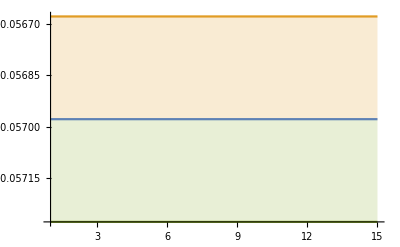

```mathematica
Plot[{fitData[[1]]//.Around[x_,y_]:>x,{fitData[[1]]//.Around[x_,y_]:>x+y,fitData[[1]]//.Around[x_,y_]:>x-y}},{x,1,15},Filling->{3->{1},2->{1}}]
```

```mathematica
SpoilHWFLOPlotN3=Show[Plot[{fitData[[1]]//.Around[x_,y_]:>x,{fitData[[1]]//.Around[x_,y_]:>x+y,fitData[[1]]//.Around[x_,y_]:>x-y}},{x,1,Length[meanErr2[[5]]]},Filling->{3->{1},2->{1}},PlotRange->{-.5,.1}],ListPlot[{Table[{τSteps[[1,i]],meanErr2[[1,i]]},{i,1,Length[meanErr2[[1]]]}],Table[{τSteps[[2,i]],meanErr2[[2,i]]},{i,1,Length[meanErr2[[2]]]}],Table[{τSteps[[3,i]],meanErr2[[3,i]]},{i,1,Length[meanErr2[[3]]]}],Table[{τSteps[[4,i]],meanErr2[[4,i]]},{i,1,Length[meanErr2[[4]]]}],Table[{τSteps[[5,i]],meanErr2[[5,i]]},{i,1,Length[meanErr2[[5]]]}]},PlotRange->{-.03,-0.005},PlotLegends->Placed[αLegendLO,{0.5,0.1}],PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]],markerlist[[4]],markerlist[[5]]},IntervalMarkersStyle->{ColorData[97][3]},PlotStyle->{ColorData[97][3]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau_{\\text{steps}}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]},PlotLabel->MaTeX["N=3(\\text{LO})",Magnification->1.2]]
```

-Graphics-

#### QCD mNLO - HWF

```mathematica
Nf4α1LoopMid
Nf4α1LoopStepTab={380,380,380,380,380};
NWalkers=200;
Nf4α1LoopBig={0.229421,0.229421,0.229421,0.229421,0.229421};
aList={1,2,3,4,5};
```

{0.21556,0.220566,0.22639,0.233299,0.241701,0.252265,0.266178,0.285833}

```mathematica
csvData=Table[Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfhwf.csv"],{xx,1,Length[aList]}]
```

({mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.06596169374907307, -0.06788257777511257, -0.066794968816769, -0.06642770485597321, -0.07634540946428536, -0.06544954892787917, -0.07021793455806837, -0.071126877708234, -0.07238696541832859, -0.08165883270578846, -0.08462290190595026, -0.1005284857215381, -0.10795184247030754, -0.08753839528281937, -0.07922472318884068, -0.08211310320405932, -0.07443171161531972, -0.06956036475878039, -0.07098408603845846, -0.07303053925168897, -0.07005492828072726, -0.06891260507678618, -0.06910543730701538, -0.08108697294991446, -0.07529561208794718, -0.07310433058417082, -0.08747869816415602, -0.07471016922377174, -0.3703463234268573, -0.08925301489925268, -0.12601113808099562, -0.08950934606880488, -0.072067766816717, -0.07350761215085008, -0.08642600624688083],[0.0050328027761950235, 0.0071147991104431796, 0.008198719270417537, 0.008956627325037481, 0.02559796276203229, 0.011447904650059713, 0.02106773040663393, 0.028953427276729185, 0.02840752802570839, 0.05288283603746825, 0.060645676701774405, 0.13539825406469422, 0.695756633828647, 0.7217845232450179, 0.6752662340637805, 0.7210944195233031, 0.7164643627125085, 0.6879086466868498, 0.7713364594121687, 0.9057012753299392, 0.9520269325186561, 0.9922408283179256, 1.2039761851667694, 1.768279416439417, 1.690027214170863, 2.0686750589685703, 4.131881230859462, 3.7162473153606306, 66.21010784444069, 8.222736671432408, 16.164740201172524, 14.155641649813798, 12.82894757439208, 17.12881669397164, 25.4816679042485],-0.071219,0.000478834,1.00128}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.04527322189100272, -0.0488595338858252, -0.047877634149329426, -0.04937706676253633, -0.050916960470121814, -0.053183699754386256, -0.057003779606642234, -0.057181057526911064, -0.06072090846939207, -0.11446557247598116, -0.07617984103945222, -0.08483995129862094, -0.27688856658300287, -0.0823571567499565, -0.07213586949622351, -0.07406300606373402, -0.06536770222417732, -0.07894749819239663, -0.06842536380708239, -0.06812612058606257, -0.07364434654795803, -0.06808428849013672, -0.0641881688653851, -0.0600476072531777, -0.06093148517816788, -0.05958155844498294, -0.06412188617199745, -0.05861577760851709, -0.05757220816216446, -0.06275982102619553, -0.06888164184598551, -0.07361780848384666, -0.06688912518585786, -0.06467070679404939, -0.06187046941227774],[0.004754647751492738, 0.008100740116287846, 0.007895502171964715, 0.00961052041001571, 0.011392466092232231, 0.015120542960397151, 0.01865813582651499, 0.022219782093420806, 0.0389853077595679, 0.2201779743177438, 0.10564999773415631, 0.13933285228597747, 1.3130090006733897, 0.2656473157634236, 0.2574388095559794, 0.3246591336284912, 0.27367369344679476, 0.45003333654700073, 0.391561305044212, 0.41202065822780054, 0.6358948374542017, 0.6036196767498505, 0.6128536326331769, 0.6685713308903387, 0.6914004410231709, 0.7376808684909008, 0.9369835551418645, 0.9828479453018965, 1.0828302275105164, 1.4425828532244267, 1.952938596701139, 2.6169607053644555, 2.9969326685166195, 3.3189802263971804, 3.142575411602039],-0.05421,0.000698793,0.638036}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.03233766204618908, -0.03319811489534365, -0.03280249774650568, -0.034179789055531984, -0.03418414525346, -0.034913659575885915, -0.03801263135833434, -0.03865903581209824, -0.03728616644440754, -0.03823962069813745, -0.041644322305028826, -0.041981104812851715, -0.04669692700004207, -0.04205579648001698, -0.046496079948314895, -0.04584696957506912, -0.04695120286704431, -0.04401156287395175, -0.051418540469813, -0.05318314352586681, -0.048384983092461684, -0.054525628898006134, -0.05270758232513754, -0.05510089762535492, -0.05755194211315185, -0.060345536686505795, -0.08655396036421337, -0.0642437926306002, -0.0660590326382249, -0.06213414008483291, -0.06915517044309638, -0.0656500536289014, -0.06076824092618784, -0.06041562849741309, -0.06655519473689],[0.0024810900195650757, 0.0027961247669090333, 0.0030550507532699496, 0.004187567180961295, 0.004301784785959783, 0.005189073336054066, 0.008131692946060982, 0.00939558114084763, 0.008586009949053487, 0.009997573088838455, 0.015748161845087174, 0.017481107237160037, 0.030756496596827932, 0.02048258564709866, 0.03212453092558877, 0.03343606822111409, 0.03864691285622156, 0.03396401055457306, 0.05294059874346503, 0.06720711007496089, 0.05787652933594756, 0.08863888185247314, 0.09339783719492016, 0.12506167313564598, 0.13646299667858017, 0.16696193876513526, 0.3838546381262322, 0.25193367512345793, 0.30081562198065775, 0.3372024627531591, 0.4347623604153645, 0.46771075913510196, 0.47753054151669116, 0.5256132282037601, 0.7069763495062651],-0.0367506,0.000906638,0.592229}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.02626913247320752, -0.03090788231475948, -0.028258196510697785, -0.029092394966863323, -0.02826315329448797, -0.029248472109750227, -0.03136169571190294, -0.03029500409875808, -0.03189927851517698, -0.032996061965343416, -0.03642329916300574, -0.03594984926990658, -0.03882878837216367, -0.036834792454304675, -0.03690444764887308, -0.03930406667738694, -0.03782748485455682, -0.041425356082595774, -0.040354729133588896, -0.04868002351686487, -0.04488177238926368, -0.0491893495337229, -0.04649444028946252, -0.058122484184081266, -0.05503784287565062, -0.05705971132734219, -0.06525531179843282, -0.0922973445296452, -0.0828713605577488, -0.10698136009958743, -0.08676203962385608, -0.0794443654543716, -0.05442671811305633, -0.054681383868410316, -0.0663349886072967],[0.002338657055765534, 0.007198559559149375, 0.0039068260582619295, 0.004645663657442272, 0.004514508370731491, 0.006006379603442958, 0.009656012131314305, 0.00766799800006183, 0.01003399769825198, 0.012299383969001813, 0.020640014521228458, 0.019289124912983135, 0.028866815609097016, 0.0248434346284229, 0.025253290122723985, 0.03317071575610128, 0.03135993898029249, 0.041366510992677, 0.03837448893771104, 0.06146116747485682, 0.0576798229777407, 0.08020519509859772, 0.08305912356315616, 0.1454320325439086, 0.1476240012257593, 0.20521583413565836, 0.282462156637983, 0.6229764453093138, 0.621665142675937, 1.3071419972362697, 1.2184519966909648, 1.1295450215837126, 0.7889467289760357, 0.8994138856912531, 1.292307262036443],-0.0259311,0.000769131,0.455278}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.025629678816127276, -0.02505334739862507, -0.024846384837943183, -0.024859266595161588, -0.02380260541348419, -0.02416872330394433, -0.02673082346797566, -0.028364890519550726, -0.03086758059909458, -0.030838767786064477, -0.03164223271328227, -0.03109560441434683, -0.030031838252829027, -0.032796591530539446, -0.03683296969119891, -0.03884354072523781, -0.04009211723432642, -0.044148829368405224, -0.045648232865525454, -0.05274942453767031, -0.0474429865637244, -0.0470312134511971, -0.04957300145546103, -0.054446156209206086, -0.06039539342639446, -0.059159644213144555, -0.0541366420425432, -0.04598397520290851, -0.04246214642276234, -0.05039136228985465, -0.05328358188529103, -0.0470514960622161, -0.041471058776211295, -0.04241669143916184, -0.0461696327553297],[0.005475755878025663, 0.005737985395574924, 0.006002396349973599, 0.00688481236809118, 0.0056333832874945365, 0.00608071238330712, 0.01001018786272078, 0.012109954404607295, 0.015832381045947683, 0.015207310694351769, 0.01661244019927718, 0.01720144717385604, 0.017247770350980466, 0.022013801273438587, 0.030817942162769004, 0.0379902879381483, 0.04424684062446692, 0.05833891847038881, 0.068699010955006, 0.09401354912599226, 0.0867825953504631, 0.09910703524862477, 0.12293017858352957, 0.17610224741563482, 0.23920307276352676, 0.2646464382253644, 0.26930805511660705, 0.2282772039066783, 0.21400331049387117, 0.3220758586726045, 0.4047498699592002, 0.3730092138342347, 0.3482870073431231, 0.3879953530967601, 0.5129876722656923],-0.0208625,0.000859408,0.396161})

```mathematica
meanErr=Table[Table[csvData[[xx,2,yy]]//StringSplit[#,{",","[","]"}]&,{yy,1,2}],{xx,1,Length[aList]}]
```

({-0.06596169374907307, -0.06788257777511257, -0.066794968816769, -0.06642770485597321, -0.07634540946428536, -0.06544954892787917, -0.07021793455806837, -0.071126877708234, -0.07238696541832859, -0.08165883270578846, -0.08462290190595026, -0.1005284857215381, -0.10795184247030754, -0.08753839528281937, -0.07922472318884068, -0.08211310320405932, -0.07443171161531972, -0.06956036475878039, -0.07098408603845846, -0.07303053925168897, -0.07005492828072726, -0.06891260507678618, -0.06910543730701538, -0.08108697294991446, -0.07529561208794718, -0.07310433058417082, -0.08747869816415602, -0.07471016922377174, -0.3703463234268573, -0.08925301489925268, -0.12601113808099562, -0.08950934606880488, -0.072067766816717, -0.07350761215085008, -0.08642600624688083} | {0.0050328027761950235, 0.0071147991104431796, 0.008198719270417537, 0.008956627325037481, 0.02559796276203229, 0.011447904650059713, 0.02106773040663393, 0.028953427276729185, 0.02840752802570839, 0.05288283603746825, 0.060645676701774405, 0.13539825406469422, 0.695756633828647, 0.7217845232450179, 0.6752662340637805, 0.7210944195233031, 0.7164643627125085, 0.6879086466868498, 0.7713364594121687, 0.9057012753299392, 0.9520269325186561, 0.9922408283179256, 1.2039761851667694, 1.768279416439417, 1.690027214170863, 2.0686750589685703, 4.131881230859462, 3.7162473153606306, 66.21010784444069, 8.222736671432408, 16.164740201172524, 14.155641649813798, 12.82894757439208, 17.12881669397164, 25.4816679042485}
{-0.04527322189100272, -0.0488595338858252, -0.047877634149329426, -0.04937706676253633, -0.050916960470121814, -0.053183699754386256, -0.057003779606642234, -0.057181057526911064, -0.06072090846939207, -0.11446557247598116, -0.07617984103945222, -0.08483995129862094, -0.27688856658300287, -0.0823571567499565, -0.07213586949622351, -0.07406300606373402, -0.06536770222417732, -0.07894749819239663, -0.06842536380708239, -0.06812612058606257, -0.07364434654795803, -0.06808428849013672, -0.0641881688653851, -0.0600476072531777, -0.06093148517816788, -0.05958155844498294, -0.06412188617199745, -0.05861577760851709, -0.05757220816216446, -0.06275982102619553, -0.06888164184598551, -0.07361780848384666, -0.06688912518585786, -0.06467070679404939, -0.06187046941227774} | {0.004754647751492738, 0.008100740116287846, 0.007895502171964715, 0.00961052041001571, 0.011392466092232231, 0.015120542960397151, 0.01865813582651499, 0.022219782093420806, 0.0389853077595679, 0.2201779743177438, 0.10564999773415631, 0.13933285228597747, 1.3130090006733897, 0.2656473157634236, 0.2574388095559794, 0.3246591336284912, 0.27367369344679476, 0.45003333654700073, 0.391561305044212, 0.41202065822780054, 0.6358948374542017, 0.6036196767498505, 0.6128536326331769, 0.6685713308903387, 0.6914004410231709, 0.7376808684909008, 0.9369835551418645, 0.9828479453018965, 1.0828302275105164, 1.4425828532244267, 1.952938596701139, 2.6169607053644555, 2.9969326685166195, 3.3189802263971804, 3.142575411602039}
{-0.03233766204618908, -0.03319811489534365, -0.03280249774650568, -0.034179789055531984, -0.03418414525346, -0.034913659575885915, -0.03801263135833434, -0.03865903581209824, -0.03728616644440754, -0.03823962069813745, -0.041644322305028826, -0.041981104812851715, -0.04669692700004207, -0.04205579648001698, -0.046496079948314895, -0.04584696957506912, -0.04695120286704431, -0.04401156287395175, -0.051418540469813, -0.05318314352586681, -0.048384983092461684, -0.054525628898006134, -0.05270758232513754, -0.05510089762535492, -0.05755194211315185, -0.060345536686505795, -0.08655396036421337, -0.0642437926306002, -0.0660590326382249, -0.06213414008483291, -0.06915517044309638, -0.0656500536289014, -0.06076824092618784, -0.06041562849741309, -0.06655519473689} | {0.0024810900195650757, 0.0027961247669090333, 0.0030550507532699496, 0.004187567180961295, 0.004301784785959783, 0.005189073336054066, 0.008131692946060982, 0.00939558114084763, 0.008586009949053487, 0.009997573088838455, 0.015748161845087174, 0.017481107237160037, 0.030756496596827932, 0.02048258564709866, 0.03212453092558877, 0.03343606822111409, 0.03864691285622156, 0.03396401055457306, 0.05294059874346503, 0.06720711007496089, 0.05787652933594756, 0.08863888185247314, 0.09339783719492016, 0.12506167313564598, 0.13646299667858017, 0.16696193876513526, 0.3838546381262322, 0.25193367512345793, 0.30081562198065775, 0.3372024627531591, 0.4347623604153645, 0.46771075913510196, 0.47753054151669116, 0.5256132282037601, 0.7069763495062651}
{-0.02626913247320752, -0.03090788231475948, -0.028258196510697785, -0.029092394966863323, -0.02826315329448797, -0.029248472109750227, -0.03136169571190294, -0.03029500409875808, -0.03189927851517698, -0.032996061965343416, -0.03642329916300574, -0.03594984926990658, -0.03882878837216367, -0.036834792454304675, -0.03690444764887308, -0.03930406667738694, -0.03782748485455682, -0.041425356082595774, -0.040354729133588896, -0.04868002351686487, -0.04488177238926368, -0.0491893495337229, -0.04649444028946252, -0.058122484184081266, -0.05503784287565062, -0.05705971132734219, -0.06525531179843282, -0.0922973445296452, -0.0828713605577488, -0.10698136009958743, -0.08676203962385608, -0.0794443654543716, -0.05442671811305633, -0.054681383868410316, -0.0663349886072967} | {0.002338657055765534, 0.007198559559149375, 0.0039068260582619295, 0.004645663657442272, 0.004514508370731491, 0.006006379603442958, 0.009656012131314305, 0.00766799800006183, 0.01003399769825198, 0.012299383969001813, 0.020640014521228458, 0.019289124912983135, 0.028866815609097016, 0.0248434346284229, 0.025253290122723985, 0.03317071575610128, 0.03135993898029249, 0.041366510992677, 0.03837448893771104, 0.06146116747485682, 0.0576798229777407, 0.08020519509859772, 0.08305912356315616, 0.1454320325439086, 0.1476240012257593, 0.20521583413565836, 0.282462156637983, 0.6229764453093138, 0.621665142675937, 1.3071419972362697, 1.2184519966909648, 1.1295450215837126, 0.7889467289760357, 0.8994138856912531, 1.292307262036443}
{-0.025629678816127276, -0.02505334739862507, -0.024846384837943183, -0.024859266595161588, -0.02380260541348419, -0.02416872330394433, -0.02673082346797566, -0.028364890519550726, -0.03086758059909458, -0.030838767786064477, -0.03164223271328227, -0.03109560441434683, -0.030031838252829027, -0.032796591530539446, -0.03683296969119891, -0.03884354072523781, -0.04009211723432642, -0.044148829368405224, -0.045648232865525454, -0.05274942453767031, -0.0474429865637244, -0.0470312134511971, -0.04957300145546103, -0.054446156209206086, -0.06039539342639446, -0.059159644213144555, -0.0541366420425432, -0.04598397520290851, -0.04246214642276234, -0.05039136228985465, -0.05328358188529103, -0.0470514960622161, -0.041471058776211295, -0.04241669143916184, -0.0461696327553297} | {0.005475755878025663, 0.005737985395574924, 0.006002396349973599, 0.00688481236809118, 0.0056333832874945365, 0.00608071238330712, 0.01001018786272078, 0.012109954404607295, 0.015832381045947683, 0.015207310694351769, 0.01661244019927718, 0.01720144717385604, 0.017247770350980466, 0.022013801273438587, 0.030817942162769004, 0.0379902879381483, 0.04424684062446692, 0.05833891847038881, 0.068699010955006, 0.09401354912599226, 0.0867825953504631, 0.09910703524862477, 0.12293017858352957, 0.17610224741563482, 0.23920307276352676, 0.2646464382253644, 0.26930805511660705, 0.2282772039066783, 0.21400331049387117, 0.3220758586726045, 0.4047498699592002, 0.3730092138342347, 0.3482870073431231, 0.3879953530967601, 0.5129876722656923})

```mathematica
meanErr[[1,2,1]]//ToExpression
```

0.0050328

```mathematica
meanErr[[1]]
```

(-0.06596169374907307 |  -0.06788257777511257 |  -0.066794968816769 |  -0.06642770485597321 |  -0.07634540946428536 |  -0.06544954892787917 |  -0.07021793455806837 |  -0.071126877708234 |  -0.07238696541832859 |  -0.08165883270578846 |  -0.08462290190595026 |  -0.1005284857215381 |  -0.10795184247030754 |  -0.08753839528281937 |  -0.07922472318884068 |  -0.08211310320405932 |  -0.07443171161531972 |  -0.06956036475878039 |  -0.07098408603845846 |  -0.07303053925168897 |  -0.07005492828072726 |  -0.06891260507678618 |  -0.06910543730701538 |  -0.08108697294991446 |  -0.07529561208794718 |  -0.07310433058417082 |  -0.08747869816415602 |  -0.07471016922377174 |  -0.3703463234268573 |  -0.08925301489925268 |  -0.12601113808099562 |  -0.08950934606880488 |  -0.072067766816717 |  -0.07350761215085008 |  -0.08642600624688083
0.0050328027761950235 |  0.0071147991104431796 |  0.008198719270417537 |  0.008956627325037481 |  0.02559796276203229 |  0.011447904650059713 |  0.02106773040663393 |  0.028953427276729185 |  0.02840752802570839 |  0.05288283603746825 |  0.060645676701774405 |  0.13539825406469422 |  0.695756633828647 |  0.7217845232450179 |  0.6752662340637805 |  0.7210944195233031 |  0.7164643627125085 |  0.6879086466868498 |  0.7713364594121687 |  0.9057012753299392 |  0.9520269325186561 |  0.9922408283179256 |  1.2039761851667694 |  1.768279416439417 |  1.690027214170863 |  2.0686750589685703 |  4.131881230859462 |  3.7162473153606306 |  66.21010784444069 |  8.222736671432408 |  16.164740201172524 |  14.155641649813798 |  12.82894757439208 |  17.12881669397164 |  25.4816679042485)

```mathematica
meanErr2=Table[Table[Around[meanErr[[xx,1,yy]]//ToExpression,meanErr[[xx,2,yy]]//ToExpression],{yy,1,Length[meanErr[[xx,1]]]}],{xx,1,Length[aList]}]
```

(-0.0660.005 | -0.0680.007 | -0.0670.008 | -0.0660.009 | -0.0760.026 | -0.0650.011 | -0.0700.021 | -0.0710.029 | -0.0720.028 | -0.080.05 | -0.080.06 | -0.100.14 | -0.10.7 | 0.00.7 | 0.00.7 | 0.00.7 | 0.00.7 | 0.00.7 | 0.00.8 | 0.00.9 | 0.01.0 | 0.01.0 | 0.01.2 | 0.01.8 | 0.01.7 | 0.02.1 | 0.4. | 0.4. | 0.66. | 0.8. | 0.16. | 0.14. | 0.13. | 0.17. | 0.25.
-0.0450.005 | -0.0490.008 | -0.0480.008 | -0.0490.010 | -0.0510.011 | -0.0530.015 | -0.0570.019 | -0.0570.022 | -0.060.04 | -0.110.22 | -0.080.11 | -0.080.14 | -0.31.3 | -0.080.27 | -0.070.26 | -0.070.32 | -0.070.27 | 0.00.5 | 0.00.4 | 0.00.4 | 0.00.6 | 0.00.6 | 0.00.6 | 0.00.7 | 0.00.7 | 0.00.7 | 0.00.9 | 0.01.0 | 0.01.1 | 0.01.4 | 0.02.0 | 0.02.6 | 0.03.0 | 0.03.3 | 0.03.1
-0.03230.0025 | -0.03320.0028 | -0.03280.0031 | -0.0340.004 | -0.0340.004 | -0.0350.005 | -0.0380.008 | -0.0390.009 | -0.0370.009 | -0.0380.010 | -0.0420.016 | -0.0420.017 | -0.0470.031 | -0.0420.020 | -0.0460.032 | -0.0460.033 | -0.050.04 | -0.0440.034 | -0.050.05 | -0.050.07 | -0.050.06 | -0.050.09 | -0.050.09 | -0.060.13 | -0.060.14 | -0.060.17 | 0.00.4 | -0.060.25 | -0.070.30 | -0.060.34 | 0.00.4 | 0.00.5 | 0.00.5 | 0.00.5 | 0.00.7
-0.02630.0023 | -0.0310.007 | -0.0280.004 | -0.0290.005 | -0.0280.005 | -0.0290.006 | -0.0310.010 | -0.0300.008 | -0.0320.010 | -0.0330.012 | -0.0360.021 | -0.0360.019 | -0.0390.029 | -0.0370.025 | -0.0370.025 | -0.0390.033 | -0.0380.031 | -0.040.04 | -0.040.04 | -0.050.06 | -0.040.06 | -0.050.08 | -0.050.08 | -0.060.15 | -0.060.15 | -0.060.21 | -0.070.28 | 0.00.6 | 0.00.6 | -0.11.3 | 0.01.2 | 0.01.1 | 0.00.8 | 0.00.9 | 0.01.3
-0.0260.005 | -0.0250.006 | -0.0250.006 | -0.0250.007 | -0.0240.006 | -0.0240.006 | -0.0270.010 | -0.0280.012 | -0.0310.016 | -0.0310.015 | -0.0320.017 | -0.0310.017 | -0.0300.017 | -0.0330.022 | -0.0370.031 | -0.040.04 | -0.040.04 | -0.040.06 | -0.050.07 | -0.050.09 | -0.050.09 | -0.050.10 | -0.050.12 | -0.050.18 | -0.060.24 | -0.060.26 | -0.050.27 | -0.050.23 | -0.040.21 | -0.050.32 | 0.00.4 | 0.00.4 | -0.040.35 | 0.00.4 | 0.00.5)

```mathematica
τSteps=Table[Table[xx,{xx,1,Length[meanErr2[[yy]]]}],{yy,1,Length[meanErr2]}]
```

(1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35)

```mathematica
fitData=Table[Around[Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfhwf.csv"][[2,3]],Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfhwf.csv"][[2,4]]],{xx,1,Length[aList]}]
```

{-0.07120.0005,-0.05420.0007,-0.03680.0009,-0.02590.0008,-0.02090.0009}

```mathematica
αLegendLO=PointLegend[Table[Directive[ColorData[97][1]],{ii,5}],{MaTeX["a=1",Magnification->0.8],MaTeX["a=2",Magnification->0.8],MaTeX["a=3",Magnification->0.8],MaTeX["a=4",Magnification->0.8],MaTeX["a=5",Magnification->0.8]},LegendMarkers->Table[Style[markerlist[[ii]],14,Bold,ColorData[97][3]],{ii,5}],LegendLayout->"Row",LegendMargins->0.5,LegendFunction->frame]
```

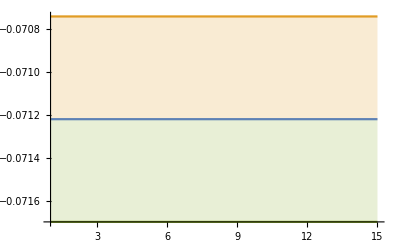

```mathematica
Plot[{fitData[[1]]//.Around[x_,y_]:>x,{fitData[[1]]//.Around[x_,y_]:>x+y,fitData[[1]]//.Around[x_,y_]:>x-y}},{x,1,15},Filling->{3->{1},2->{1}}]
```

```mathematica
SpoilHWFLOPlotN3=Show[Plot[{fitData[[1]]//.Around[x_,y_]:>x,{fitData[[1]]//.Around[x_,y_]:>x+y,fitData[[1]]//.Around[x_,y_]:>x-y}},{x,1,Length[meanErr2[[5]]]},Filling->{3->{1},2->{1}},PlotRange->{-1,.1}],ListPlot[{Table[{τSteps[[1,i]],meanErr2[[1,i]]},{i,1,Length[meanErr2[[1]]]}],Table[{τSteps[[2,i]],meanErr2[[2,i]]},{i,1,Length[meanErr2[[2]]]}],Table[{τSteps[[3,i]],meanErr2[[3,i]]},{i,1,Length[meanErr2[[3]]]}],Table[{τSteps[[4,i]],meanErr2[[4,i]]},{i,1,Length[meanErr2[[4]]]}],Table[{τSteps[[5,i]],meanErr2[[5,i]]},{i,1,Length[meanErr2[[5]]]}]},PlotRange->{-.1,-0.005},PlotLegends->Placed[αLegendLO,{0.5,0.1}],PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]],markerlist[[4]],markerlist[[5]]},IntervalMarkersStyle->{ColorData[97][3]},PlotStyle->{ColorData[97][3]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau_{\\text{steps}}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]},PlotLabel->MaTeX["N=3(\\text{LO})",Magnification->1.2]]
```

-Graphics-

#### QCD NNLO - HWF

```mathematica
Nf4α1LoopMid
Nf4α1LoopStepTab={393,393,393,393,393};
NWalkers=200;
Nf4α1LoopBig={0.225626,0.225626,0.225626,0.225626,0.225626};
aList={1,2,3,4,5};
```

{0.21556,0.220566,0.22639,0.233299,0.241701,0.252265,0.266178,0.285833}

```mathematica
csvData=Table[Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfhwf.csv"],{xx,1,Length[aList]}]
```

({mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.09695694899688673, -0.10047481940063825, -0.10076783238503202, -0.10010414552257263, -0.10085200575098036, -0.10199177249453735, -0.10413267091751477, -0.10179296920855146, -0.10582227490743765, -0.1034473592190284, -0.10280498993906532, -0.10360732840894264, -0.10392681870413918, -0.1042757677191626, -0.10413872409379035, -0.10526437713214729, -0.10546147621374076, -0.10440760648525207, -0.10556222317901262, -0.1048928677265815, -0.10354573547083072, -0.10757893540446252, -0.10486507909756584, -0.10401844607352931, -0.10355480472979063, -0.10565161127391758, -0.10393750446321684, -0.10269757224095122, -0.1031987128701778, -0.10491328078712643, -0.10599291476363275, -0.10561277051610674, -0.10739590378544567, -0.10201661189300969, -0.10355885031951016, -0.10838062534740263],[0.007416666234995779, 0.010990671358891074, 0.015238724962115039, 0.01817592397239378, 0.024667348811736777, 0.029992795142018806, 0.041091066201066714, 0.051689704367147614, 0.08066636753330624, 0.08793691059128847, 0.10926250884151084, 0.1437862393639171, 0.1958416135992328, 0.24333907977328628, 0.3129565714447268, 0.4061729425081997, 0.49611562219537003, 0.6012429232734278, 0.7763734790270032, 0.9902076862912184, 1.182706655575579, 1.6876354891753713, 1.9867789677166512, 2.385040830973214, 2.89348621465205, 3.844562261293356, 4.611516331694737, 5.5062912619276245, 6.960981343408173, 9.228637540023092, 11.911031523446912, 15.34391373678129, 20.69636598742701, 22.067139798923964, 31.926683153624023, 43.10523477809962],-0.0985423,0.000521633,0.687757}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.07697554920576309, -0.07827683963116662, -0.08059956764279144, -0.08436949121943439, -0.08752099980533842, -0.0928017315913086, -0.08723915130645314, -0.08624526835608652, -0.08918443674036983, -0.09198880961897365, -0.10077275207916124, -0.09039744843394258, -0.08881692456062845, -0.0882953203317714, -0.09451192606236518, -0.1035440012354797, -0.11625154251193237, -0.10125157190438476, -0.10107253353197408, -0.10190336580160184, -0.09266027596642605, -0.09599955054812101, -0.09122327372804169, -0.09811295776700743, -0.09894186048598487, -0.10021793968805391, -0.10294732458253497, -0.10426324740779484, -0.10241459381744218, -0.09576964272521521, -0.10936407585237432, -0.12861645635864666, -0.1001491070371777, -0.09629659883235499, -0.1003245943035719, -0.10671364313446147],[0.011658527143417436, 0.013753173880779856, 0.018100764319930764, 0.029828935103850384, 0.044737447138383964, 0.07433482153202123, 0.06761305017983629, 0.08222919968265543, 0.09658431797935069, 0.12071176276392274, 0.20606060091424264, 0.1693101655566342, 0.20875210814590187, 0.24053021733122598, 0.35531621744339703, 0.5655816496181958, 0.9455945443911321, 0.9774200379149687, 1.2235727326327555, 1.7064570588898207, 1.7297288294586528, 2.0325662872747188, 2.3155459389336426, 3.1182034313161244, 4.019683586119267, 5.183217702552568, 7.830342404166087, 10.332952389450435, 13.31802880801154, 13.281975664927707, 23.87905517089003, 49.74230864765846, 40.03911533086313, 43.40509039570684, 62.458154240000546, 86.48603366487828],-0.084133,0.0012153,0.268066}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.06058544799304146, -0.06363609893583948, -0.06599045339017616, -0.06454362049531094, -0.06267833291680493, -0.0635892436583644, -0.06423033920854773, -0.06356331920876403, -0.06527814866478475, -0.06347815903964199, -0.06478852191385649, -0.07081710072406505, -0.07216081978850365, -0.0706686363610324, -0.06949941832442166, -0.07237405100933, -0.07619172979716914, -0.0807775410409616, -0.08488482791905805, -0.08766715567368427, -0.09827903887747763, -0.09571621919402157, -0.09179227933660435, -0.08936562861344119, -0.09379559007659956, -0.09717000630467104, -0.1113876823554602, -0.10707666159679939, -0.10432214832061465, -0.12423526616742281, -0.11789564540290999, -0.11810889721729242, -0.11103766370418974, -0.10313024603073054, -0.1032862724909423, -0.11001760464015926],[0.00887841192827911, 0.01255761429544136, 0.017128477587840345, 0.018704087046173403, 0.01974969925733429, 0.023066940078650185, 0.028340091457232295, 0.03136485672184326, 0.038320642191940486, 0.04063590274609732, 0.04997537730204933, 0.07216684256896298, 0.08591332995101184, 0.0948202542232505, 0.10454539595558016, 0.13384668274914438, 0.17007709786478412, 0.2274407394813642, 0.2980639256900524, 0.3788087089642708, 0.6701465827388529, 0.6923103770836591, 0.8333969013223426, 0.9541606602373905, 1.30234315438771, 1.8350780025582265, 2.739521139831433, 3.0875282218545603, 3.697561100434178, 8.202891198087421, 7.775977900065398, 10.439344697547861, 12.229382251597576, 13.444385723180371, 16.74301371738747, 23.229358556615008],-0.0607581,0.00123559,0.600013}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.0396039257201135, -0.040604902095316246, -0.04126754765809093, -0.04223070199812276, -0.042485397464729596, -0.04311022160469478, -0.04320668652711001, -0.04397825329413326, -0.04561349246124678, -0.04637782329859074, -0.048215251766133095, -0.05122305293716335, -0.05472694980586572, -0.0554208101407952, -0.05306623703943847, -0.05404607590973629, -0.059212557476640185, -0.0586560159413659, -0.06238660714140402, -0.06968211954306414, -0.06825182883241339, -0.0728404115157743, -0.07770682314623638, -0.07727068711392067, -0.08250688277261195, -0.09378826237630578, -0.10398376139885686, -0.07873076550723189, -0.07779070053713857, -0.08577968554587334, -0.0888489256803776, -0.08340075476687206, -0.07941116154788991, -0.0808993354432504, -0.07883398172758929, -0.07931283037755518],[0.0024304180090194303, 0.0030531918200610445, 0.003606626782988608, 0.004411398852567569, 0.004916015451363129, 0.005837180785667013, 0.006488158484603714, 0.007715702460311129, 0.009954393241002182, 0.011997928911518263, 0.015122561610384257, 0.021678445642633867, 0.03388583820510702, 0.0412601255508828, 0.03817687678306117, 0.04397393272780209, 0.06285468286644298, 0.07057662351953843, 0.09112288551682206, 0.13902576287076604, 0.1486488484119731, 0.20650305109386655, 0.27294525290630733, 0.31183082224929826, 0.4141265828919977, 0.6467685994548121, 1.0767445948180203, 0.7509296823763607, 0.8330132689684796, 1.1610433713255746, 1.4474162944531157, 1.6135008266126476, 1.8181539004070941, 2.2157622511391835, 2.5336083413635655, 3.0910335891515905],-0.0429492,0.000804402,0.835757}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.040636991768372224, -0.04401683331930464, -0.04437343431800509, -0.04325629478681445, -0.04405359920676539, -0.04552424947076344, -0.0488989762834177, -0.04747654570420548, -0.050127663763535925, -0.04893968244332106, -0.05087611903221462, -0.05357484561193781, -0.0580037996485437, -0.060978944437435144, -0.059631777349682585, -0.0626502569143659, -0.06936236205922043, -0.0800749996972927, -0.09573756550599007, -0.1113882255557465, -0.14861543872344, -0.08551811509606116, -0.08860524625734544, -0.10431819774161004, -0.09814477411155612, -0.13129774761213606, -0.1304851380410034, -0.09317977140627294, -0.08672012778992129, -0.089835941827022, -0.08125947679295775, -0.08592019940338426, -0.07310439051158103, -0.07995278988910182, -0.08001532472985472, -0.08424055672116179],[0.004272949317439086, 0.0070676906645764075, 0.007628481491983424, 0.007674392881773938, 0.009465745515865018, 0.011955787584852426, 0.018690909673943677, 0.01710512480953463, 0.023563659778229322, 0.024159659422269403, 0.030272135821846527, 0.03611950173185427, 0.04943075335760225, 0.06552894306150049, 0.07466685600612889, 0.0936253472964602, 0.1352694287547855, 0.23754641801770957, 0.4450231080320243, 0.7430834660259423, 1.5939312316013015, 0.9360178285109727, 1.1968343626324778, 1.9994880124578096, 2.409012438669626, 4.522594481489722, 5.883203414348103, 4.602993227193653, 4.775500289936621, 5.580732254712504, 5.984063467082518, 7.58314077610325, 7.4324207757088, 9.666099578999637, 11.55122534134948, 14.510342082028082],-0.0402664,0.00135443,0.283788})

```mathematica
meanErr=Table[Table[csvData[[xx,2,yy]]//StringSplit[#,{",","[","]"}]&,{yy,1,2}],{xx,1,Length[aList]}]
```

({-0.09695694899688673, -0.10047481940063825, -0.10076783238503202, -0.10010414552257263, -0.10085200575098036, -0.10199177249453735, -0.10413267091751477, -0.10179296920855146, -0.10582227490743765, -0.1034473592190284, -0.10280498993906532, -0.10360732840894264, -0.10392681870413918, -0.1042757677191626, -0.10413872409379035, -0.10526437713214729, -0.10546147621374076, -0.10440760648525207, -0.10556222317901262, -0.1048928677265815, -0.10354573547083072, -0.10757893540446252, -0.10486507909756584, -0.10401844607352931, -0.10355480472979063, -0.10565161127391758, -0.10393750446321684, -0.10269757224095122, -0.1031987128701778, -0.10491328078712643, -0.10599291476363275, -0.10561277051610674, -0.10739590378544567, -0.10201661189300969, -0.10355885031951016, -0.10838062534740263} | {0.007416666234995779, 0.010990671358891074, 0.015238724962115039, 0.01817592397239378, 0.024667348811736777, 0.029992795142018806, 0.041091066201066714, 0.051689704367147614, 0.08066636753330624, 0.08793691059128847, 0.10926250884151084, 0.1437862393639171, 0.1958416135992328, 0.24333907977328628, 0.3129565714447268, 0.4061729425081997, 0.49611562219537003, 0.6012429232734278, 0.7763734790270032, 0.9902076862912184, 1.182706655575579, 1.6876354891753713, 1.9867789677166512, 2.385040830973214, 2.89348621465205, 3.844562261293356, 4.611516331694737, 5.5062912619276245, 6.960981343408173, 9.228637540023092, 11.911031523446912, 15.34391373678129, 20.69636598742701, 22.067139798923964, 31.926683153624023, 43.10523477809962}
{-0.07697554920576309, -0.07827683963116662, -0.08059956764279144, -0.08436949121943439, -0.08752099980533842, -0.0928017315913086, -0.08723915130645314, -0.08624526835608652, -0.08918443674036983, -0.09198880961897365, -0.10077275207916124, -0.09039744843394258, -0.08881692456062845, -0.0882953203317714, -0.09451192606236518, -0.1035440012354797, -0.11625154251193237, -0.10125157190438476, -0.10107253353197408, -0.10190336580160184, -0.09266027596642605, -0.09599955054812101, -0.09122327372804169, -0.09811295776700743, -0.09894186048598487, -0.10021793968805391, -0.10294732458253497, -0.10426324740779484, -0.10241459381744218, -0.09576964272521521, -0.10936407585237432, -0.12861645635864666, -0.1001491070371777, -0.09629659883235499, -0.1003245943035719, -0.10671364313446147} | {0.011658527143417436, 0.013753173880779856, 0.018100764319930764, 0.029828935103850384, 0.044737447138383964, 0.07433482153202123, 0.06761305017983629, 0.08222919968265543, 0.09658431797935069, 0.12071176276392274, 0.20606060091424264, 0.1693101655566342, 0.20875210814590187, 0.24053021733122598, 0.35531621744339703, 0.5655816496181958, 0.9455945443911321, 0.9774200379149687, 1.2235727326327555, 1.7064570588898207, 1.7297288294586528, 2.0325662872747188, 2.3155459389336426, 3.1182034313161244, 4.019683586119267, 5.183217702552568, 7.830342404166087, 10.332952389450435, 13.31802880801154, 13.281975664927707, 23.87905517089003, 49.74230864765846, 40.03911533086313, 43.40509039570684, 62.458154240000546, 86.48603366487828}
{-0.06058544799304146, -0.06363609893583948, -0.06599045339017616, -0.06454362049531094, -0.06267833291680493, -0.0635892436583644, -0.06423033920854773, -0.06356331920876403, -0.06527814866478475, -0.06347815903964199, -0.06478852191385649, -0.07081710072406505, -0.07216081978850365, -0.0706686363610324, -0.06949941832442166, -0.07237405100933, -0.07619172979716914, -0.0807775410409616, -0.08488482791905805, -0.08766715567368427, -0.09827903887747763, -0.09571621919402157, -0.09179227933660435, -0.08936562861344119, -0.09379559007659956, -0.09717000630467104, -0.1113876823554602, -0.10707666159679939, -0.10432214832061465, -0.12423526616742281, -0.11789564540290999, -0.11810889721729242, -0.11103766370418974, -0.10313024603073054, -0.1032862724909423, -0.11001760464015926} | {0.00887841192827911, 0.01255761429544136, 0.017128477587840345, 0.018704087046173403, 0.01974969925733429, 0.023066940078650185, 0.028340091457232295, 0.03136485672184326, 0.038320642191940486, 0.04063590274609732, 0.04997537730204933, 0.07216684256896298, 0.08591332995101184, 0.0948202542232505, 0.10454539595558016, 0.13384668274914438, 0.17007709786478412, 0.2274407394813642, 0.2980639256900524, 0.3788087089642708, 0.6701465827388529, 0.6923103770836591, 0.8333969013223426, 0.9541606602373905, 1.30234315438771, 1.8350780025582265, 2.739521139831433, 3.0875282218545603, 3.697561100434178, 8.202891198087421, 7.775977900065398, 10.439344697547861, 12.229382251597576, 13.444385723180371, 16.74301371738747, 23.229358556615008}
{-0.0396039257201135, -0.040604902095316246, -0.04126754765809093, -0.04223070199812276, -0.042485397464729596, -0.04311022160469478, -0.04320668652711001, -0.04397825329413326, -0.04561349246124678, -0.04637782329859074, -0.048215251766133095, -0.05122305293716335, -0.05472694980586572, -0.0554208101407952, -0.05306623703943847, -0.05404607590973629, -0.059212557476640185, -0.0586560159413659, -0.06238660714140402, -0.06968211954306414, -0.06825182883241339, -0.0728404115157743, -0.07770682314623638, -0.07727068711392067, -0.08250688277261195, -0.09378826237630578, -0.10398376139885686, -0.07873076550723189, -0.07779070053713857, -0.08577968554587334, -0.0888489256803776, -0.08340075476687206, -0.07941116154788991, -0.0808993354432504, -0.07883398172758929, -0.07931283037755518} | {0.0024304180090194303, 0.0030531918200610445, 0.003606626782988608, 0.004411398852567569, 0.004916015451363129, 0.005837180785667013, 0.006488158484603714, 0.007715702460311129, 0.009954393241002182, 0.011997928911518263, 0.015122561610384257, 0.021678445642633867, 0.03388583820510702, 0.0412601255508828, 0.03817687678306117, 0.04397393272780209, 0.06285468286644298, 0.07057662351953843, 0.09112288551682206, 0.13902576287076604, 0.1486488484119731, 0.20650305109386655, 0.27294525290630733, 0.31183082224929826, 0.4141265828919977, 0.6467685994548121, 1.0767445948180203, 0.7509296823763607, 0.8330132689684796, 1.1610433713255746, 1.4474162944531157, 1.6135008266126476, 1.8181539004070941, 2.2157622511391835, 2.5336083413635655, 3.0910335891515905}
{-0.040636991768372224, -0.04401683331930464, -0.04437343431800509, -0.04325629478681445, -0.04405359920676539, -0.04552424947076344, -0.0488989762834177, -0.04747654570420548, -0.050127663763535925, -0.04893968244332106, -0.05087611903221462, -0.05357484561193781, -0.0580037996485437, -0.060978944437435144, -0.059631777349682585, -0.0626502569143659, -0.06936236205922043, -0.0800749996972927, -0.09573756550599007, -0.1113882255557465, -0.14861543872344, -0.08551811509606116, -0.08860524625734544, -0.10431819774161004, -0.09814477411155612, -0.13129774761213606, -0.1304851380410034, -0.09317977140627294, -0.08672012778992129, -0.089835941827022, -0.08125947679295775, -0.08592019940338426, -0.07310439051158103, -0.07995278988910182, -0.08001532472985472, -0.08424055672116179} | {0.004272949317439086, 0.0070676906645764075, 0.007628481491983424, 0.007674392881773938, 0.009465745515865018, 0.011955787584852426, 0.018690909673943677, 0.01710512480953463, 0.023563659778229322, 0.024159659422269403, 0.030272135821846527, 0.03611950173185427, 0.04943075335760225, 0.06552894306150049, 0.07466685600612889, 0.0936253472964602, 0.1352694287547855, 0.23754641801770957, 0.4450231080320243, 0.7430834660259423, 1.5939312316013015, 0.9360178285109727, 1.1968343626324778, 1.9994880124578096, 2.409012438669626, 4.522594481489722, 5.883203414348103, 4.602993227193653, 4.775500289936621, 5.580732254712504, 5.984063467082518, 7.58314077610325, 7.4324207757088, 9.666099578999637, 11.55122534134948, 14.510342082028082})

```mathematica
meanErr2=Table[Table[Around[meanErr[[xx,1,yy]]//ToExpression,meanErr[[xx,2,yy]]//ToExpression],{yy,1,Length[meanErr[[xx,1]]]}],{xx,1,Length[aList]}]
```

(-0.0970.007 | -0.1000.011 | -0.1010.015 | -0.1000.018 | -0.1010.025 | -0.1020.030 | -0.100.04 | -0.100.05 | -0.110.08 | -0.100.09 | -0.100.11 | -0.100.14 | -0.100.20 | -0.100.24 | -0.100.31 | -0.10.4 | -0.10.5 | -0.10.6 | -0.10.8 | -0.11.0 | -0.11.2 | -0.11.7 | -0.12.0 | -0.12.4 | -0.12.9 | 0.4. | 0.5. | 0.6. | 0.7. | 0.9. | 0.12. | 0.15. | 0.21. | 0.22. | 0.32. | 0.43.
-0.0770.012 | -0.0780.014 | -0.0810.018 | -0.0840.030 | -0.090.04 | -0.090.07 | -0.090.07 | -0.090.08 | -0.090.10 | -0.090.12 | -0.100.21 | -0.090.17 | -0.090.21 | -0.090.24 | 0.00.4 | -0.10.6 | -0.10.9 | -0.11.0 | -0.11.2 | -0.11.7 | 0.01.7 | 0.02.0 | 0.02.3 | 0.03.1 | 0.4. | 0.5. | 0.8. | 0.10. | 0.13. | 0.13. | 0.24. | 0.50. | 0.40. | 0.43. | 0.62. | 0.86.
-0.0610.009 | -0.0640.013 | -0.0660.017 | -0.0650.019 | -0.0630.020 | -0.0640.023 | -0.0640.028 | -0.0640.031 | -0.070.04 | -0.060.04 | -0.060.05 | -0.070.07 | -0.070.09 | -0.070.09 | -0.070.10 | -0.070.13 | -0.080.17 | -0.080.23 | -0.080.30 | 0.00.4 | 0.00.7 | 0.00.7 | 0.00.8 | 0.01.0 | 0.01.3 | 0.01.8 | -0.12.7 | -0.13.1 | 0.4. | 0.8. | 0.8. | 0.10. | 0.12. | 0.13. | 0.17. | 0.23.
-0.03960.0024 | -0.04060.0031 | -0.0410.004 | -0.0420.004 | -0.0420.005 | -0.0430.006 | -0.0430.006 | -0.0440.008 | -0.0460.010 | -0.0460.012 | -0.0480.015 | -0.0510.022 | -0.0550.034 | -0.060.04 | -0.050.04 | -0.050.04 | -0.060.06 | -0.060.07 | -0.060.09 | -0.070.14 | -0.070.15 | -0.070.21 | -0.080.27 | -0.080.31 | 0.00.4 | 0.00.6 | -0.11.1 | 0.00.8 | 0.00.8 | 0.01.2 | 0.01.4 | 0.01.6 | 0.01.8 | 0.02.2 | 0.02.5 | 0.03.1
-0.0410.004 | -0.0440.007 | -0.0440.008 | -0.0430.008 | -0.0440.009 | -0.0460.012 | -0.0490.019 | -0.0470.017 | -0.0500.024 | -0.0490.024 | -0.0510.030 | -0.050.04 | -0.060.05 | -0.060.07 | -0.060.07 | -0.060.09 | -0.070.14 | -0.080.24 | 0.00.4 | -0.10.7 | -0.11.6 | 0.00.9 | 0.01.2 | -0.12.0 | 0.02.4 | 0.5. | 0.6. | 0.5. | 0.5. | 0.6. | 0.6. | 0.8. | 0.7. | 0.10. | 0.12. | 0.15.)

```mathematica
τSteps=Table[Table[xx,{xx,1,Length[meanErr2[[yy]]]}],{yy,1,Length[meanErr2]}]
```

(1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36)

```mathematica
fitData=Table[Around[Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfhwf.csv"][[2,3]],Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfhwf.csv"][[2,4]]],{xx,1,Length[aList]}]
```

{-0.09850.0005,-0.08410.0012,-0.06080.0012,-0.04290.0008,-0.04030.0014}

```mathematica
αLegendLO=PointLegend[Table[Directive[ColorData[97][1]],{ii,5}],{MaTeX["a=1",Magnification->0.8],MaTeX["a=2",Magnification->0.8],MaTeX["a=3",Magnification->0.8],MaTeX["a=4",Magnification->0.8],MaTeX["a=5",Magnification->0.8]},LegendMarkers->Table[Style[markerlist[[ii]],14,Bold,ColorData[97][3]],{ii,5}],LegendLayout->"Row",LegendMargins->0.5,LegendFunction->frame]
```

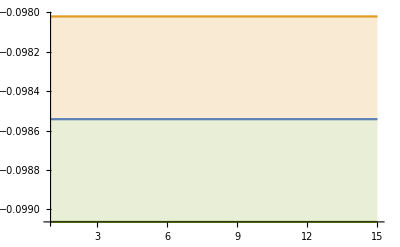

```mathematica
Plot[{fitData[[1]]//.Around[x_,y_]:>x,{fitData[[1]]//.Around[x_,y_]:>x+y,fitData[[1]]//.Around[x_,y_]:>x-y}},{x,1,15},Filling->{3->{1},2->{1}}]
```

```mathematica
SpoilHWFLOPlotN3=Show[Plot[{fitData[[1]]//.Around[x_,y_]:>x,{fitData[[1]]//.Around[x_,y_]:>x+y,fitData[[1]]//.Around[x_,y_]:>x-y}},{x,1,Length[meanErr2[[5]]]},Filling->{3->{1},2->{1}},PlotRange->{-1,1}],ListPlot[{Table[{τSteps[[1,i]],meanErr2[[1,i]]},{i,1,Length[meanErr2[[1]]]}],Table[{τSteps[[2,i]],meanErr2[[2,i]]},{i,1,Length[meanErr2[[2]]]}],Table[{τSteps[[3,i]],meanErr2[[3,i]]},{i,1,Length[meanErr2[[3]]]}],Table[{τSteps[[4,i]],meanErr2[[4,i]]},{i,1,Length[meanErr2[[4]]]}],Table[{τSteps[[5,i]],meanErr2[[5,i]]},{i,1,Length[meanErr2[[5]]]}]},PlotRange->{-.03,-0.005},PlotLegends->Placed[αLegendLO,{0.5,0.1}],PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]],markerlist[[4]],markerlist[[5]]},IntervalMarkersStyle->{ColorData[97][3]},PlotStyle->{ColorData[97][3]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau_{\\text{steps}}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]},PlotLabel->MaTeX["N=3(\\text{LO})",Magnification->1.2]]
```

-Graphics-

#### QCD LO - gauss

```mathematica
Nf4α1LoopMid
Nf4α1LoopStepTab={430,430,430,430,430};
NWalkers=200;
Nf4α1LoopBig={0.21556,0.21556,0.21556,0.21556,0.21556};
aList={1,2,3,4,5};
```

{0.21556,0.220566,0.22639,0.233299,0.241701,0.252265,0.266178,0.285833}

```mathematica
csvData=Table[Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfgauss.csv"],{xx,1,Length[aList]}]
```

({mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.02011709666190358, -0.021005015753470538, -0.018216650471426427, -0.016390092058770896, -0.01989990578338093, -0.01905518564105858, -0.01939589663084976, -0.01790846823540348, -0.02689290919764424, -0.020500738902256496, -0.020243545373567314, -0.01992226335640102, -0.019044138529794613, -0.020098631729578615, -0.020374615540204005, -0.015920250369782854, -0.016749931116462582, -0.015264660662002511, -0.01714245353944229, -0.016044107630938793, -0.013666757006549563, -0.016861039935830133, -0.028321250659409155, -0.02010016095055732, -0.018778112045597026, -0.019802401727136945, -0.021224033364773673, -0.017920353309769942, -0.017109078411413608, -0.017330802899550548, -0.021894327709633298, -0.018185833170803623, -0.022435384200789738, -0.022620433325553413, -0.021111852995868634, -0.020343251020419836, -0.02174978285054435, -0.020498573245366754, -0.031270427992915885],[0.0027619691833244333, 0.0036979805757376815, 0.0028218898146207794, 0.002812413245638831, 0.0049952927198947195, 0.004588528767378659, 0.003713533273417155, 0.00424944675586513, 0.013025299455885497, 0.005440872093540728, 0.005129439075252255, 0.00463204419498966, 0.006211441930387529, 0.0066579054609926065, 0.006581057036523713, 0.005003973755905106, 0.005852037149278991, 0.0049153643035145305, 0.0071353914281391964, 0.005867450647271916, 0.005299457241114282, 0.005852989398287571, 0.03829020704857817, 0.011065861644040683, 0.0125040529008994, 0.010420786955778475, 0.011321937209839499, 0.008348416945681685, 0.00870987907121953, 0.008176395660062777, 0.011829106517763923, 0.01039362647871905, 0.013629635382337822, 0.01789704190071922, 0.018337787964276653, 0.019635180095390243, 0.027136599673726863, 0.028657403510327008, 0.04282624794821166],-0.0169233,0.000414197,0.484657}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.016504581801258324, -0.01644793575633194, -0.016633901947600817, -0.019117779765265352, -0.0166226770448734, -0.01760355492678689, -0.017604835498396344, -0.018961373467249982, -0.019464508847332196, -0.01919920621089815, -0.019408296153646185, -0.018491009399273152, -0.017314108005083394, -0.018301328773707812, -0.018446289883846324, -0.0233126668787765, -0.01889133241700161, -0.017278566972554275, -0.01620494852083756, -0.01645720376619245, -0.017091508716138085, -0.01973538875205458, -0.018035260168856537, -0.018655653201505307, -0.020063713225108047, -0.02643859509402852, -0.026862903274063956, -0.026840054038054388, -0.023999808247076097, -0.018639851054146138, -0.021093076959859087, -0.024289665699556737, -0.025059769017800246, -0.020367182744268346, -0.020418626564015135, -0.01895021798526369, -0.01738722436881391, -0.01564785316728138, -0.015653276708878883],[0.001396620039311911, 0.0013593903826035812, 0.0015607614022065017, 0.002802106670063154, 0.0014059150239821468, 0.0020386140220741396, 0.001981904336421965, 0.0025931216781504684, 0.0038949730181563787, 0.003640561243573598, 0.004354544625393374, 0.0039957788203564375, 0.0028600079699801495, 0.003276164041255136, 0.004058956431772252, 0.013649105253097593, 0.006038427152023592, 0.005026067414427751, 0.0036202170452402883, 0.004384472109146517, 0.0052110005819544225, 0.008227090933575067, 0.0057473935117613156, 0.0063793847495180345, 0.008744767981349391, 0.019807252556541546, 0.021598781496197664, 0.01870903664221141, 0.020390962456427512, 0.012612861250428556, 0.01652662098147909, 0.02604292095296279, 0.028249091517052318, 0.01813972851881406, 0.021009273811370063, 0.021269907184022267, 0.018150962971109356, 0.012978894835458431, 0.011990169434230724],-0.0146444,0.00026626,0.182419}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.012480825137815644, -0.014136991779921216, -0.01623734986388417, -0.014375139932395382, -0.016028672302226914, -0.019405990793875935, -0.016589730857495058, -0.015321311198212492, -0.014824681068255071, -0.01614890259056459, -0.01672315572034959, -0.015796303546991994, -0.01675982276619073, -0.017000423277037643, -0.020116780420316453, -0.017190515732698437, -0.017909708642058726, -0.016794752513864124, -0.01621013477486562, -0.02112855853307632, -0.014919437096294669, -0.014106490559545186, -0.014208703347855133, -0.014594971607825427, -0.014317775285345075, -0.014025013371276866, -0.015180381465397111, -0.01577222736862846, -0.015265697001664667, -0.01392880055416946, -0.014846230376101057, -0.016761623470459768, -0.017583037850965367, -0.015823984900310305, -0.01542438007178451, -0.015584798285544111, -0.014992494272575494, -0.014382980293406452, -0.014569267676015607],[0.000929114130375394, 0.0022422339827077586, 0.004342689200373096, 0.002055566980899404, 0.0028649651429335267, 0.006101089517834195, 0.003691647903051356, 0.0028193491100754345, 0.002909005387606876, 0.004474553959517821, 0.005034108316842757, 0.00404662497040868, 0.00457909236874553, 0.004595502708394411, 0.008010661179891, 0.00554801144914347, 0.006385838725937491, 0.006102435419193185, 0.005468119262136863, 0.014060346939606649, 0.004521868059038517, 0.0040386272449982035, 0.0038473506030142035, 0.004539445061911263, 0.00428392950942106, 0.004198814238784375, 0.006126827210635043, 0.00624918377319451, 0.005655559106969485, 0.0049274897208902695, 0.0065165079274318105, 0.008348179096909483, 0.010736681834498189, 0.007537178253213514, 0.0070151592755943746, 0.008158958198692386, 0.007309434754906911, 0.006790104238566207, 0.006589566041773351],-0.0117402,0.000270672,0.142477}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.008950855484395474, -0.009046273115566392, -0.00916113054707227, -0.009353389356294237, -0.009431393144891768, -0.00959377020714062, -0.009589514667270035, -0.0101761158863741, -0.0103025119301919, -0.010045278324147878, -0.010216603546672701, -0.010330961906834676, -0.010477421178392033, -0.010452159728198593, -0.009860393425821396, -0.010374371418544175, -0.010074214697738523, -0.010197672012877487, -0.01043155129700976, -0.010094552536227075, -0.01083062698312379, -0.010953081647882008, -0.011175752767636226, -0.011711124496484017, -0.01242774522629168, -0.011708381030981777, -0.011341470955913441, -0.011775191627242162, -0.0110885359218899, -0.01071748865937005, -0.011129982755010745, -0.011689035231242135, -0.012391476682414575, -0.011659293596856515, -0.011804192638825362, -0.011906029077147785, -0.011688969257750929, -0.01144590734031847, -0.01304891448176916],[0.0004694445895220509, 0.0005365336240270627, 0.0005385560475265519, 0.0006080536401361807, 0.0006386501664491369, 0.0007381692722430258, 0.0007942184301780168, 0.001288145155135681, 0.0014638991637202518, 0.001111608355891057, 0.0011672248154564189, 0.0013316327382214982, 0.0014370493531781598, 0.001438298480973694, 0.0010833392982481697, 0.0015670868195195764, 0.0012739637492261602, 0.0012857362062285646, 0.0014741558119494489, 0.0013180257961984889, 0.001684573938847426, 0.0017997682412525804, 0.001983331371121464, 0.0026516167822749634, 0.0033033841065188098, 0.0026790696393476816, 0.0024994235168719014, 0.002641840162983023, 0.002215693412342594, 0.00199800390495639, 0.0022889769474287443, 0.0027853753564337953, 0.0035034376439189133, 0.003026527539396209, 0.0034581969610555457, 0.003920458083626574, 0.003947269658880592, 0.003672557657938854, 0.006821671266030614],-0.00835422,0.000203704,0.0945361}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.008310138645799763, -0.008481464528390995, -0.00821247092376762, -0.008325640332713833, -0.008681388934832977, -0.009337158710739738, -0.01047308643421343, -0.010153981139462212, -0.01046786130163077, -0.010121105232788166, -0.010100370442659913, -0.010646685239071528, -0.009925350797517786, -0.010051688725309938, -0.010102196146149389, -0.010734865280850428, -0.0101517033953046, -0.010641393304398044, -0.010002723097562423, -0.009907966208213933, -0.00929714345572188, -0.00972565762578978, -0.009979896783156151, -0.009925118798804882, -0.009989347734994289, -0.009573307361821487, -0.009957785778215421, -0.010692191325560634, -0.010698955519639798, -0.009795816440872135, -0.009445512498290332, -0.009707698617621302, -0.009523661664849279, -0.009787138349656565, -0.009562616787200773, -0.009659383146302202, -0.010129687953009451, -0.013841145133030242, -0.013496166507252516],[0.0009260300551734443, 0.0010846115130483725, 0.0008428441694354283, 0.0008149886783763136, 0.0009891846020365705, 0.0015395205520847995, 0.002359742880616642, 0.002037373645443276, 0.0021704124563545588, 0.0017911487672234753, 0.0016309008581716785, 0.00233162778138781, 0.00197122245198712, 0.0021857144710828945, 0.0024760949464809217, 0.003639031463129998, 0.0029792037487161513, 0.003562009030019883, 0.0028038190357962656, 0.002955708178367971, 0.0019872131071194624, 0.0023551640633199663, 0.00261261064966491, 0.0027171323680907663, 0.002969072961144591, 0.0026078289228943854, 0.002990301084557372, 0.003811403544134203, 0.0037939311770024174, 0.0028490984806739963, 0.002635340821758539, 0.0029719247505112676, 0.0029385921979354704, 0.0031356104208755393, 0.003057016081305937, 0.003304820715739284, 0.004044386261358476, 0.01067246412419032, 0.009753368665477],-0.00735141,0.000226871,0.0791739})

```mathematica
meanErr=Table[Table[csvData[[xx,2,yy]]//StringSplit[#,{",","[","]"}]&,{yy,1,2}],{xx,1,Length[aList]}]
```

({-0.02011709666190358, -0.021005015753470538, -0.018216650471426427, -0.016390092058770896, -0.01989990578338093, -0.01905518564105858, -0.01939589663084976, -0.01790846823540348, -0.02689290919764424, -0.020500738902256496, -0.020243545373567314, -0.01992226335640102, -0.019044138529794613, -0.020098631729578615, -0.020374615540204005, -0.015920250369782854, -0.016749931116462582, -0.015264660662002511, -0.01714245353944229, -0.016044107630938793, -0.013666757006549563, -0.016861039935830133, -0.028321250659409155, -0.02010016095055732, -0.018778112045597026, -0.019802401727136945, -0.021224033364773673, -0.017920353309769942, -0.017109078411413608, -0.017330802899550548, -0.021894327709633298, -0.018185833170803623, -0.022435384200789738, -0.022620433325553413, -0.021111852995868634, -0.020343251020419836, -0.02174978285054435, -0.020498573245366754, -0.031270427992915885} | {0.0027619691833244333, 0.0036979805757376815, 0.0028218898146207794, 0.002812413245638831, 0.0049952927198947195, 0.004588528767378659, 0.003713533273417155, 0.00424944675586513, 0.013025299455885497, 0.005440872093540728, 0.005129439075252255, 0.00463204419498966, 0.006211441930387529, 0.0066579054609926065, 0.006581057036523713, 0.005003973755905106, 0.005852037149278991, 0.0049153643035145305, 0.0071353914281391964, 0.005867450647271916, 0.005299457241114282, 0.005852989398287571, 0.03829020704857817, 0.011065861644040683, 0.0125040529008994, 0.010420786955778475, 0.011321937209839499, 0.008348416945681685, 0.00870987907121953, 0.008176395660062777, 0.011829106517763923, 0.01039362647871905, 0.013629635382337822, 0.01789704190071922, 0.018337787964276653, 0.019635180095390243, 0.027136599673726863, 0.028657403510327008, 0.04282624794821166}
{-0.016504581801258324, -0.01644793575633194, -0.016633901947600817, -0.019117779765265352, -0.0166226770448734, -0.01760355492678689, -0.017604835498396344, -0.018961373467249982, -0.019464508847332196, -0.01919920621089815, -0.019408296153646185, -0.018491009399273152, -0.017314108005083394, -0.018301328773707812, -0.018446289883846324, -0.0233126668787765, -0.01889133241700161, -0.017278566972554275, -0.01620494852083756, -0.01645720376619245, -0.017091508716138085, -0.01973538875205458, -0.018035260168856537, -0.018655653201505307, -0.020063713225108047, -0.02643859509402852, -0.026862903274063956, -0.026840054038054388, -0.023999808247076097, -0.018639851054146138, -0.021093076959859087, -0.024289665699556737, -0.025059769017800246, -0.020367182744268346, -0.020418626564015135, -0.01895021798526369, -0.01738722436881391, -0.01564785316728138, -0.015653276708878883} | {0.001396620039311911, 0.0013593903826035812, 0.0015607614022065017, 0.002802106670063154, 0.0014059150239821468, 0.0020386140220741396, 0.001981904336421965, 0.0025931216781504684, 0.0038949730181563787, 0.003640561243573598, 0.004354544625393374, 0.0039957788203564375, 0.0028600079699801495, 0.003276164041255136, 0.004058956431772252, 0.013649105253097593, 0.006038427152023592, 0.005026067414427751, 0.0036202170452402883, 0.004384472109146517, 0.0052110005819544225, 0.008227090933575067, 0.0057473935117613156, 0.0063793847495180345, 0.008744767981349391, 0.019807252556541546, 0.021598781496197664, 0.01870903664221141, 0.020390962456427512, 0.012612861250428556, 0.01652662098147909, 0.02604292095296279, 0.028249091517052318, 0.01813972851881406, 0.021009273811370063, 0.021269907184022267, 0.018150962971109356, 0.012978894835458431, 0.011990169434230724}
{-0.012480825137815644, -0.014136991779921216, -0.01623734986388417, -0.014375139932395382, -0.016028672302226914, -0.019405990793875935, -0.016589730857495058, -0.015321311198212492, -0.014824681068255071, -0.01614890259056459, -0.01672315572034959, -0.015796303546991994, -0.01675982276619073, -0.017000423277037643, -0.020116780420316453, -0.017190515732698437, -0.017909708642058726, -0.016794752513864124, -0.01621013477486562, -0.02112855853307632, -0.014919437096294669, -0.014106490559545186, -0.014208703347855133, -0.014594971607825427, -0.014317775285345075, -0.014025013371276866, -0.015180381465397111, -0.01577222736862846, -0.015265697001664667, -0.01392880055416946, -0.014846230376101057, -0.016761623470459768, -0.017583037850965367, -0.015823984900310305, -0.01542438007178451, -0.015584798285544111, -0.014992494272575494, -0.014382980293406452, -0.014569267676015607} | {0.000929114130375394, 0.0022422339827077586, 0.004342689200373096, 0.002055566980899404, 0.0028649651429335267, 0.006101089517834195, 0.003691647903051356, 0.0028193491100754345, 0.002909005387606876, 0.004474553959517821, 0.005034108316842757, 0.00404662497040868, 0.00457909236874553, 0.004595502708394411, 0.008010661179891, 0.00554801144914347, 0.006385838725937491, 0.006102435419193185, 0.005468119262136863, 0.014060346939606649, 0.004521868059038517, 0.0040386272449982035, 0.0038473506030142035, 0.004539445061911263, 0.00428392950942106, 0.004198814238784375, 0.006126827210635043, 0.00624918377319451, 0.005655559106969485, 0.0049274897208902695, 0.0065165079274318105, 0.008348179096909483, 0.010736681834498189, 0.007537178253213514, 0.0070151592755943746, 0.008158958198692386, 0.007309434754906911, 0.006790104238566207, 0.006589566041773351}
{-0.008950855484395474, -0.009046273115566392, -0.00916113054707227, -0.009353389356294237, -0.009431393144891768, -0.00959377020714062, -0.009589514667270035, -0.0101761158863741, -0.0103025119301919, -0.010045278324147878, -0.010216603546672701, -0.010330961906834676, -0.010477421178392033, -0.010452159728198593, -0.009860393425821396, -0.010374371418544175, -0.010074214697738523, -0.010197672012877487, -0.01043155129700976, -0.010094552536227075, -0.01083062698312379, -0.010953081647882008, -0.011175752767636226, -0.011711124496484017, -0.01242774522629168, -0.011708381030981777, -0.011341470955913441, -0.011775191627242162, -0.0110885359218899, -0.01071748865937005, -0.011129982755010745, -0.011689035231242135, -0.012391476682414575, -0.011659293596856515, -0.011804192638825362, -0.011906029077147785, -0.011688969257750929, -0.01144590734031847, -0.01304891448176916} | {0.0004694445895220509, 0.0005365336240270627, 0.0005385560475265519, 0.0006080536401361807, 0.0006386501664491369, 0.0007381692722430258, 0.0007942184301780168, 0.001288145155135681, 0.0014638991637202518, 0.001111608355891057, 0.0011672248154564189, 0.0013316327382214982, 0.0014370493531781598, 0.001438298480973694, 0.0010833392982481697, 0.0015670868195195764, 0.0012739637492261602, 0.0012857362062285646, 0.0014741558119494489, 0.0013180257961984889, 0.001684573938847426, 0.0017997682412525804, 0.001983331371121464, 0.0026516167822749634, 0.0033033841065188098, 0.0026790696393476816, 0.0024994235168719014, 0.002641840162983023, 0.002215693412342594, 0.00199800390495639, 0.0022889769474287443, 0.0027853753564337953, 0.0035034376439189133, 0.003026527539396209, 0.0034581969610555457, 0.003920458083626574, 0.003947269658880592, 0.003672557657938854, 0.006821671266030614}
{-0.008310138645799763, -0.008481464528390995, -0.00821247092376762, -0.008325640332713833, -0.008681388934832977, -0.009337158710739738, -0.01047308643421343, -0.010153981139462212, -0.01046786130163077, -0.010121105232788166, -0.010100370442659913, -0.010646685239071528, -0.009925350797517786, -0.010051688725309938, -0.010102196146149389, -0.010734865280850428, -0.0101517033953046, -0.010641393304398044, -0.010002723097562423, -0.009907966208213933, -0.00929714345572188, -0.00972565762578978, -0.009979896783156151, -0.009925118798804882, -0.009989347734994289, -0.009573307361821487, -0.009957785778215421, -0.010692191325560634, -0.010698955519639798, -0.009795816440872135, -0.009445512498290332, -0.009707698617621302, -0.009523661664849279, -0.009787138349656565, -0.009562616787200773, -0.009659383146302202, -0.010129687953009451, -0.013841145133030242, -0.013496166507252516} | {0.0009260300551734443, 0.0010846115130483725, 0.0008428441694354283, 0.0008149886783763136, 0.0009891846020365705, 0.0015395205520847995, 0.002359742880616642, 0.002037373645443276, 0.0021704124563545588, 0.0017911487672234753, 0.0016309008581716785, 0.00233162778138781, 0.00197122245198712, 0.0021857144710828945, 0.0024760949464809217, 0.003639031463129998, 0.0029792037487161513, 0.003562009030019883, 0.0028038190357962656, 0.002955708178367971, 0.0019872131071194624, 0.0023551640633199663, 0.00261261064966491, 0.0027171323680907663, 0.002969072961144591, 0.0026078289228943854, 0.002990301084557372, 0.003811403544134203, 0.0037939311770024174, 0.0028490984806739963, 0.002635340821758539, 0.0029719247505112676, 0.0029385921979354704, 0.0031356104208755393, 0.003057016081305937, 0.003304820715739284, 0.004044386261358476, 0.01067246412419032, 0.009753368665477})

```mathematica
meanErr[[1,2,1]]//ToExpression
```

0.00276197

```mathematica
meanErr[[1]]
```

(-0.02011709666190358 |  -0.021005015753470538 |  -0.018216650471426427 |  -0.016390092058770896 |  -0.01989990578338093 |  -0.01905518564105858 |  -0.01939589663084976 |  -0.01790846823540348 |  -0.02689290919764424 |  -0.020500738902256496 |  -0.020243545373567314 |  -0.01992226335640102 |  -0.019044138529794613 |  -0.020098631729578615 |  -0.020374615540204005 |  -0.015920250369782854 |  -0.016749931116462582 |  -0.015264660662002511 |  -0.01714245353944229 |  -0.016044107630938793 |  -0.013666757006549563 |  -0.016861039935830133 |  -0.028321250659409155 |  -0.02010016095055732 |  -0.018778112045597026 |  -0.019802401727136945 |  -0.021224033364773673 |  -0.017920353309769942 |  -0.017109078411413608 |  -0.017330802899550548 |  -0.021894327709633298 |  -0.018185833170803623 |  -0.022435384200789738 |  -0.022620433325553413 |  -0.021111852995868634 |  -0.020343251020419836 |  -0.02174978285054435 |  -0.020498573245366754 |  -0.031270427992915885
0.0027619691833244333 |  0.0036979805757376815 |  0.0028218898146207794 |  0.002812413245638831 |  0.0049952927198947195 |  0.004588528767378659 |  0.003713533273417155 |  0.00424944675586513 |  0.013025299455885497 |  0.005440872093540728 |  0.005129439075252255 |  0.00463204419498966 |  0.006211441930387529 |  0.0066579054609926065 |  0.006581057036523713 |  0.005003973755905106 |  0.005852037149278991 |  0.0049153643035145305 |  0.0071353914281391964 |  0.005867450647271916 |  0.005299457241114282 |  0.005852989398287571 |  0.03829020704857817 |  0.011065861644040683 |  0.0125040529008994 |  0.010420786955778475 |  0.011321937209839499 |  0.008348416945681685 |  0.00870987907121953 |  0.008176395660062777 |  0.011829106517763923 |  0.01039362647871905 |  0.013629635382337822 |  0.01789704190071922 |  0.018337787964276653 |  0.019635180095390243 |  0.027136599673726863 |  0.028657403510327008 |  0.04282624794821166)

```mathematica
meanErr2=Table[Table[Around[meanErr[[xx,1,yy]]//ToExpression,meanErr[[xx,2,yy]]//ToExpression],{yy,1,Length[meanErr[[xx,1]]]}],{xx,1,Length[aList]}]
```

(-0.02010.0028 | -0.0210.004 | -0.01820.0028 | -0.01640.0028 | -0.0200.005 | -0.0190.005 | -0.0190.004 | -0.0180.004 | -0.0270.013 | -0.0210.005 | -0.0200.005 | -0.0200.005 | -0.0190.006 | -0.0200.007 | -0.0200.007 | -0.0160.005 | -0.0170.006 | -0.0150.005 | -0.0170.007 | -0.0160.006 | -0.0140.005 | -0.0170.006 | -0.030.04 | -0.0200.011 | -0.0190.013 | -0.0200.010 | -0.0210.011 | -0.0180.008 | -0.0170.009 | -0.0170.008 | -0.0220.012 | -0.0180.010 | -0.0220.014 | -0.0230.018 | -0.0210.018 | -0.0200.020 | -0.0220.027 | -0.0200.029 | -0.030.04
-0.01650.0014 | -0.01640.0014 | -0.01660.0016 | -0.01910.0028 | -0.01660.0014 | -0.01760.0020 | -0.01760.0020 | -0.01900.0026 | -0.0190.004 | -0.0190.004 | -0.0190.004 | -0.0180.004 | -0.01730.0029 | -0.01830.0033 | -0.0180.004 | -0.0230.014 | -0.0190.006 | -0.0170.005 | -0.0160.004 | -0.0160.004 | -0.0170.005 | -0.0200.008 | -0.0180.006 | -0.0190.006 | -0.0200.009 | -0.0260.020 | -0.0270.022 | -0.0270.019 | -0.0240.020 | -0.0190.013 | -0.0210.017 | -0.0240.026 | -0.0250.028 | -0.0200.018 | -0.0200.021 | -0.0190.021 | -0.0170.018 | -0.0160.013 | -0.0160.012
-0.01250.0009 | -0.01410.0022 | -0.0160.004 | -0.01440.0021 | -0.01600.0029 | -0.0190.006 | -0.0170.004 | -0.01530.0028 | -0.01480.0029 | -0.0160.004 | -0.0170.005 | -0.0160.004 | -0.0170.005 | -0.0170.005 | -0.0200.008 | -0.0170.006 | -0.0180.006 | -0.0170.006 | -0.0160.005 | -0.0210.014 | -0.0150.005 | -0.0140.004 | -0.0140.004 | -0.0150.005 | -0.0140.004 | -0.0140.004 | -0.0150.006 | -0.0160.006 | -0.0150.006 | -0.0140.005 | -0.0150.007 | -0.0170.008 | -0.0180.011 | -0.0160.008 | -0.0150.007 | -0.0160.008 | -0.0150.007 | -0.0140.007 | -0.0150.007
-0.00900.0005 | -0.00900.0005 | -0.00920.0005 | -0.00940.0006 | -0.00940.0006 | -0.00960.0007 | -0.00960.0008 | -0.01020.0013 | -0.01030.0015 | -0.01000.0011 | -0.01020.0012 | -0.01030.0013 | -0.01050.0014 | -0.01050.0014 | -0.00990.0011 | -0.01040.0016 | -0.01010.0013 | -0.01020.0013 | -0.01040.0015 | -0.01010.0013 | -0.01080.0017 | -0.01100.0018 | -0.01120.0020 | -0.01170.0027 | -0.01240.0033 | -0.01170.0027 | -0.01130.0025 | -0.01180.0026 | -0.01110.0022 | -0.01070.0020 | -0.01110.0023 | -0.01170.0028 | -0.01240.0035 | -0.01170.0030 | -0.01180.0035 | -0.0120.004 | -0.0120.004 | -0.0110.004 | -0.0130.007
-0.00830.0009 | -0.00850.0011 | -0.00820.0008 | -0.00830.0008 | -0.00870.0010 | -0.00930.0015 | -0.01050.0024 | -0.01020.0020 | -0.01050.0022 | -0.01010.0018 | -0.01010.0016 | -0.01060.0023 | -0.00990.0020 | -0.01010.0022 | -0.01010.0025 | -0.0110.004 | -0.01020.0030 | -0.0110.004 | -0.01000.0028 | -0.00990.0030 | -0.00930.0020 | -0.00970.0024 | -0.01000.0026 | -0.00990.0027 | -0.01000.0030 | -0.00960.0026 | -0.01000.0030 | -0.0110.004 | -0.0110.004 | -0.00980.0028 | -0.00940.0026 | -0.00970.0030 | -0.00950.0029 | -0.00980.0031 | -0.00960.0031 | -0.00970.0033 | -0.0100.004 | -0.0140.011 | -0.0130.010)

```mathematica
τSteps=Table[Table[xx,{xx,1,Length[meanErr2[[yy]]]}],{yy,1,Length[meanErr2]}]
```

(1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39)

```mathematica
fitData=Table[Around[Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfgauss.csv"][[2,3]],Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfgauss.csv"][[2,4]]],{xx,1,Length[aList]}]
```

{-0.01690.0004,-0.014640.00027,-0.011740.00027,-0.008350.00020,-0.007350.00023}

```mathematica
αLegendLO=PointLegend[Table[Directive[ColorData[97][1]],{ii,5}],{MaTeX["a=1",Magnification->0.8],MaTeX["a=2",Magnification->0.8],MaTeX["a=3",Magnification->0.8],MaTeX["a=4",Magnification->0.8],MaTeX["a=5",Magnification->0.8]},LegendMarkers->Table[Style[markerlist[[ii]],14,Bold,ColorData[97][3]],{ii,5}],LegendLayout->"Row",LegendMargins->0.5,LegendFunction->frame]
```

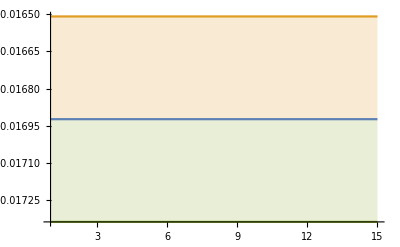

```mathematica
Plot[{fitData[[1]]//.Around[x_,y_]:>x,{fitData[[1]]//.Around[x_,y_]:>x+y,fitData[[1]]//.Around[x_,y_]:>x-y}},{x,1,15},Filling->{3->{1},2->{1}}]
```

```mathematica
SpoilHWFLOPlotN3=Show[Plot[{fitData[[1]]//.Around[x_,y_]:>x,{fitData[[1]]//.Around[x_,y_]:>x+y,fitData[[1]]//.Around[x_,y_]:>x-y}},{x,1,Length[meanErr2[[5]]]},Filling->{3->{1},2->{1}},PlotRange->{-.03,-0.005}],ListPlot[{Table[{τSteps[[1,i]],meanErr2[[1,i]]},{i,1,Length[meanErr2[[1]]]}],Table[{τSteps[[2,i]],meanErr2[[2,i]]},{i,1,Length[meanErr2[[2]]]}],Table[{τSteps[[3,i]],meanErr2[[3,i]]},{i,1,Length[meanErr2[[3]]]}],Table[{τSteps[[4,i]],meanErr2[[4,i]]},{i,1,Length[meanErr2[[4]]]}],Table[{τSteps[[5,i]],meanErr2[[5,i]]},{i,1,Length[meanErr2[[5]]]}]},PlotRange->{-.03,-0.005},PlotLegends->Placed[αLegendLO,{0.5,0.1}],PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]],markerlist[[4]],markerlist[[5]]},IntervalMarkersStyle->{ColorData[97][3]},PlotStyle->{ColorData[97][3]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau_{\\text{steps}}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]},PlotLabel->MaTeX["N=3\\text{ (LO)}",Magnification->1.2]]
```

-Graphics-

#### QCD NLO - gauss

```mathematica
Nf4α1LoopMid
Nf4α1LoopStepTab={380,380,380,380,380};
NWalkers=200;
Nf4α1LoopBig={0.229421,0.229421,0.229421,0.229421,0.229421};
aList={1,2,3,4,5};
```

{0.21556,0.220566,0.22639,0.233299,0.241701,0.252265,0.266178,0.285833}

```mathematica
csvData=Table[Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfgauss.csv"],{xx,1,Length[aList]}]
```

({mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.05799795149334149, -0.058481760368348075, -0.056981317285796786, -0.05442188889850036, -0.05711282904997768, -0.05487731507567629, -0.05939566344180651, -0.057707714114852836, -0.05991008389885641, -0.062049073600147095, -0.06307713224888314, -0.06240232314792864, -0.055804364624249515, -0.05709056603442074, -0.06134267346960524, -0.05928732053856844, -0.06780012227645968, -0.06003617103106915, -0.05940749752046476, -0.056308132867900776, -0.06348112882809635, -0.06436624552241543, -0.06007592260562376, -0.06519639184317695, -0.06432893392973575, -0.06325568126847077, -0.07149557038987958, -0.06252220155759311, -0.05132280944085597, -0.05496657792775823, -0.0534260545875223, -0.056315601195270404, -0.05872724333601134, -0.06305074340239343, -0.07023124459727391],[0.004573238327734835, 0.007368659673466731, 0.0065204435202975, 0.005139832918653165, 0.009665215727340361, 0.008998457531093079, 0.017758302543281906, 0.01439991083591532, 0.020272010913795848, 0.028712702493829036, 0.033065769114301174, 0.035341189025873035, 0.027044305765500726, 0.03381821674358071, 0.05561247061863489, 0.05652377575531212, 0.1311710082518898, 0.06833075810350159, 0.07084129755515937, 0.05871847702748589, 0.11686622350255219, 0.15971022590959041, 0.11740682761457144, 0.18094112503825774, 0.2607904801740072, 0.3224982808766507, 0.5416521961781338, 0.4042972038707493, 0.2561554867565066, 0.35624430550583486, 0.3495713032279187, 0.5154125985446041, 0.5741477052974545, 1.0078781035291986, 1.6974845776787215],-0.0547582,0.000344616,0.528001}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.0486906200072312, -0.050508255577371305, -0.05266136382863355, -0.04854060077567449, -0.0484849584033144, -0.049215689778639986, -0.04652774609502668, -0.04814068121801097, -0.04724931366456893, -0.05062126386093248, -0.055072062010647994, -0.0552809631705007, -0.050126447827875724, -0.056193624206349956, -0.052365171970260554, -0.05175395570866158, -0.05201797037982012, -0.054707644874769416, -0.0552309000108713, -0.05090590647135266, -0.04890809699450546, -0.046829684600187535, -0.04766049546126125, -0.04795860820701763, -0.04843944517322141, -0.05153564678609696, -0.053825415698086486, -0.051581552390836616, -0.04893870137571052, -0.04926648902540987, -0.052483327659905654, -0.05225678460939017, -0.05137555209423339, -0.05076450588373554, -0.05188401178063421],[0.005422222694132075, 0.006127499326206406, 0.009029770337389643, 0.008018293928274486, 0.008956777937280854, 0.012423730970580105, 0.010360698640575388, 0.01327686144745805, 0.01289242430388618, 0.02000399877488629, 0.031896554944317854, 0.03544443154520335, 0.026452665626275407, 0.047069907614572026, 0.03751521473684497, 0.04081010746443618, 0.04719742670859478, 0.06688742696102683, 0.07415010952070336, 0.06955906053859374, 0.06397088486008731, 0.06399303022104454, 0.07700421798237282, 0.08656440483635086, 0.09701784698373149, 0.15597576729349893, 0.1656571693416889, 0.17785488322571813, 0.1640976701578419, 0.21233480952030512, 0.29447242604734447, 0.3453524263818913, 0.43367786905570405, 0.4626075408363804, 0.5439736444493114],-0.0435771,0.000642569,0.310647}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.03227375305368466, -0.03439681363762843, -0.03299731488792703, -0.032751339939248746, -0.034284276675712454, -0.034856216652806346, -0.034974982975590714, -0.035953371951023806, -0.037322016840027006, -0.037081254830539645, -0.03794396916220316, -0.037337922729597885, -0.038744304016389904, -0.04085792927204386, -0.04386176779256863, -0.04279804881823195, -0.043008408362840124, -0.044831989730978995, -0.04193022617625603, -0.04239605897997378, -0.04352032270267424, -0.04450052008530874, -0.04560533842831207, -0.047180798766014415, -0.04716717903796829, -0.0506366689174387, -0.05534098417278305, -0.056284942494073835, -0.0511527668063729, -0.04344043522535223, -0.04611877143952876, -0.04826453617772743, -0.04876312455748971, -0.05400444339177646, -0.06055722824520203],[0.0019022027140030338, 0.0033418474594572385, 0.00264775201968729, 0.002732631751689845, 0.0037143678123790535, 0.004149066436409039, 0.004719284221561705, 0.0057611794357931125, 0.0074889143937470854, 0.007861289152490505, 0.009380350803248493, 0.009081646276538596, 0.011330733834523378, 0.015199237362920068, 0.02207637627530034, 0.023240615278956437, 0.025863102182441332, 0.03525676896783855, 0.03050841615824821, 0.032851261118672516, 0.04187471901302358, 0.051946066777123406, 0.06537202393838579, 0.08514073608058183, 0.09592623152313637, 0.14344166550389537, 0.18202586452091324, 0.24685731486858536, 0.220770271993291, 0.16221622624338056, 0.199435724996874, 0.22402684753671664, 0.2912562200547431, 0.33974041949185524, 0.4740959725588964],-0.0327729,0.000650716,0.255487}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.026038421466495328, -0.026570526540698365, -0.026428061366301558, -0.02626685803662214, -0.026479770393254325, -0.027048993011498434, -0.028003073835113385, -0.029378493506966495, -0.027868177595693065, -0.027485955797196746, -0.0285321956235303, -0.028869352795438365, -0.02953503803589211, -0.02986570816126328, -0.0296004013500503, -0.029429654931457293, -0.030659550126298417, -0.031227093863394288, -0.03086510155635846, -0.03082690678801672, -0.03203155073588417, -0.03179545543443219, -0.031534987550486414, -0.031706365017232736, -0.03314400542123028, -0.031730209420302476, -0.03403579532615967, -0.03506801160190192, -0.03544345607512923, -0.0345274215664915, -0.03614529358442977, -0.038966692962654044, -0.03668507698701382, -0.03683776518099605, -0.03734947796776444],[0.0015757983636459094, 0.0019355173676840487, 0.0021498635499195423, 0.0021913694393343557, 0.0025217298571039437, 0.003013874566851541, 0.003998311766379751, 0.0063567850334692345, 0.0050859104592633755, 0.004819033204313425, 0.006207000763077553, 0.006808500899481776, 0.007765401474091753, 0.008999159591265569, 0.008655554114910776, 0.008910391127361384, 0.010432062385352823, 0.012408836205219964, 0.012350423321511997, 0.01292073704653341, 0.01629879609732955, 0.016803425443735205, 0.017687266413447054, 0.020791604813450052, 0.023704106648501554, 0.02251916553156331, 0.029082374740209836, 0.03302478233043813, 0.038440051067731254, 0.039967788651174715, 0.04809390395183419, 0.06369358028888294, 0.06475903906293388, 0.06692433967465271, 0.07423270808595524],-0.0245312,0.000539702,0.198645}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.02164037270891587, -0.022107559024677138, -0.02217030746533276, -0.02271249352498678, -0.022752623392177134, -0.023853303400114427, -0.02321211102512253, -0.0232754977408234, -0.031228480927293086, -0.03004868074392473, -0.02798687789215107, -0.028329695072416193, -0.028027189435794488, -0.028828789263062628, -0.03112385207226141, -0.0326371727232781, -0.031983790053770195, -0.03646411829134778, -0.040909827766773224, -0.041006164466176734, -0.03639946433764124, -0.03810761914292695, -0.03468683687195884, -0.03097297586742296, -0.03294650757928681, -0.03302069751537224, -0.03481102827212753, -0.035760207599906786, -0.03312933568903723, -0.030842815550013728, -0.031071238744008915, -0.030643711902801365, -0.02909597999801721, -0.028164158069833443, -0.027007417827111083],[0.001031834845057165, 0.0012188206824362215, 0.0014621802860004685, 0.0020098370020543016, 0.0022778530534571942, 0.003787816423839057, 0.003008084677083649, 0.0031107438525066152, 0.015818822236075156, 0.013896860640294594, 0.012076866396815843, 0.012880366672691533, 0.012631075491172471, 0.014180639812330366, 0.019864267808048494, 0.02530947974630334, 0.023321954778016116, 0.03815457874149182, 0.058987766182930154, 0.06661280814904677, 0.05270001967194946, 0.06675670833516406, 0.05947195453696837, 0.04968735575603471, 0.06103315020489362, 0.06528849524039046, 0.07908820388238032, 0.08694026135199504, 0.07849859685149993, 0.07039747930171086, 0.07819317525797155, 0.08270805774530907, 0.07696431051009817, 0.0754530103814855, 0.07189708301770933],-0.0216782,0.000327643,0.459643})

```mathematica
meanErr=Table[Table[csvData[[xx,2,yy]]//StringSplit[#,{",","[","]"}]&,{yy,1,2}],{xx,1,Length[aList]}]
```

({-0.05799795149334149, -0.058481760368348075, -0.056981317285796786, -0.05442188889850036, -0.05711282904997768, -0.05487731507567629, -0.05939566344180651, -0.057707714114852836, -0.05991008389885641, -0.062049073600147095, -0.06307713224888314, -0.06240232314792864, -0.055804364624249515, -0.05709056603442074, -0.06134267346960524, -0.05928732053856844, -0.06780012227645968, -0.06003617103106915, -0.05940749752046476, -0.056308132867900776, -0.06348112882809635, -0.06436624552241543, -0.06007592260562376, -0.06519639184317695, -0.06432893392973575, -0.06325568126847077, -0.07149557038987958, -0.06252220155759311, -0.05132280944085597, -0.05496657792775823, -0.0534260545875223, -0.056315601195270404, -0.05872724333601134, -0.06305074340239343, -0.07023124459727391} | {0.004573238327734835, 0.007368659673466731, 0.0065204435202975, 0.005139832918653165, 0.009665215727340361, 0.008998457531093079, 0.017758302543281906, 0.01439991083591532, 0.020272010913795848, 0.028712702493829036, 0.033065769114301174, 0.035341189025873035, 0.027044305765500726, 0.03381821674358071, 0.05561247061863489, 0.05652377575531212, 0.1311710082518898, 0.06833075810350159, 0.07084129755515937, 0.05871847702748589, 0.11686622350255219, 0.15971022590959041, 0.11740682761457144, 0.18094112503825774, 0.2607904801740072, 0.3224982808766507, 0.5416521961781338, 0.4042972038707493, 0.2561554867565066, 0.35624430550583486, 0.3495713032279187, 0.5154125985446041, 0.5741477052974545, 1.0078781035291986, 1.6974845776787215}
{-0.0486906200072312, -0.050508255577371305, -0.05266136382863355, -0.04854060077567449, -0.0484849584033144, -0.049215689778639986, -0.04652774609502668, -0.04814068121801097, -0.04724931366456893, -0.05062126386093248, -0.055072062010647994, -0.0552809631705007, -0.050126447827875724, -0.056193624206349956, -0.052365171970260554, -0.05175395570866158, -0.05201797037982012, -0.054707644874769416, -0.0552309000108713, -0.05090590647135266, -0.04890809699450546, -0.046829684600187535, -0.04766049546126125, -0.04795860820701763, -0.04843944517322141, -0.05153564678609696, -0.053825415698086486, -0.051581552390836616, -0.04893870137571052, -0.04926648902540987, -0.052483327659905654, -0.05225678460939017, -0.05137555209423339, -0.05076450588373554, -0.05188401178063421} | {0.005422222694132075, 0.006127499326206406, 0.009029770337389643, 0.008018293928274486, 0.008956777937280854, 0.012423730970580105, 0.010360698640575388, 0.01327686144745805, 0.01289242430388618, 0.02000399877488629, 0.031896554944317854, 0.03544443154520335, 0.026452665626275407, 0.047069907614572026, 0.03751521473684497, 0.04081010746443618, 0.04719742670859478, 0.06688742696102683, 0.07415010952070336, 0.06955906053859374, 0.06397088486008731, 0.06399303022104454, 0.07700421798237282, 0.08656440483635086, 0.09701784698373149, 0.15597576729349893, 0.1656571693416889, 0.17785488322571813, 0.1640976701578419, 0.21233480952030512, 0.29447242604734447, 0.3453524263818913, 0.43367786905570405, 0.4626075408363804, 0.5439736444493114}
{-0.03227375305368466, -0.03439681363762843, -0.03299731488792703, -0.032751339939248746, -0.034284276675712454, -0.034856216652806346, -0.034974982975590714, -0.035953371951023806, -0.037322016840027006, -0.037081254830539645, -0.03794396916220316, -0.037337922729597885, -0.038744304016389904, -0.04085792927204386, -0.04386176779256863, -0.04279804881823195, -0.043008408362840124, -0.044831989730978995, -0.04193022617625603, -0.04239605897997378, -0.04352032270267424, -0.04450052008530874, -0.04560533842831207, -0.047180798766014415, -0.04716717903796829, -0.0506366689174387, -0.05534098417278305, -0.056284942494073835, -0.0511527668063729, -0.04344043522535223, -0.04611877143952876, -0.04826453617772743, -0.04876312455748971, -0.05400444339177646, -0.06055722824520203} | {0.0019022027140030338, 0.0033418474594572385, 0.00264775201968729, 0.002732631751689845, 0.0037143678123790535, 0.004149066436409039, 0.004719284221561705, 0.0057611794357931125, 0.0074889143937470854, 0.007861289152490505, 0.009380350803248493, 0.009081646276538596, 0.011330733834523378, 0.015199237362920068, 0.02207637627530034, 0.023240615278956437, 0.025863102182441332, 0.03525676896783855, 0.03050841615824821, 0.032851261118672516, 0.04187471901302358, 0.051946066777123406, 0.06537202393838579, 0.08514073608058183, 0.09592623152313637, 0.14344166550389537, 0.18202586452091324, 0.24685731486858536, 0.220770271993291, 0.16221622624338056, 0.199435724996874, 0.22402684753671664, 0.2912562200547431, 0.33974041949185524, 0.4740959725588964}
{-0.026038421466495328, -0.026570526540698365, -0.026428061366301558, -0.02626685803662214, -0.026479770393254325, -0.027048993011498434, -0.028003073835113385, -0.029378493506966495, -0.027868177595693065, -0.027485955797196746, -0.0285321956235303, -0.028869352795438365, -0.02953503803589211, -0.02986570816126328, -0.0296004013500503, -0.029429654931457293, -0.030659550126298417, -0.031227093863394288, -0.03086510155635846, -0.03082690678801672, -0.03203155073588417, -0.03179545543443219, -0.031534987550486414, -0.031706365017232736, -0.03314400542123028, -0.031730209420302476, -0.03403579532615967, -0.03506801160190192, -0.03544345607512923, -0.0345274215664915, -0.03614529358442977, -0.038966692962654044, -0.03668507698701382, -0.03683776518099605, -0.03734947796776444} | {0.0015757983636459094, 0.0019355173676840487, 0.0021498635499195423, 0.0021913694393343557, 0.0025217298571039437, 0.003013874566851541, 0.003998311766379751, 0.0063567850334692345, 0.0050859104592633755, 0.004819033204313425, 0.006207000763077553, 0.006808500899481776, 0.007765401474091753, 0.008999159591265569, 0.008655554114910776, 0.008910391127361384, 0.010432062385352823, 0.012408836205219964, 0.012350423321511997, 0.01292073704653341, 0.01629879609732955, 0.016803425443735205, 0.017687266413447054, 0.020791604813450052, 0.023704106648501554, 0.02251916553156331, 0.029082374740209836, 0.03302478233043813, 0.038440051067731254, 0.039967788651174715, 0.04809390395183419, 0.06369358028888294, 0.06475903906293388, 0.06692433967465271, 0.07423270808595524}
{-0.02164037270891587, -0.022107559024677138, -0.02217030746533276, -0.02271249352498678, -0.022752623392177134, -0.023853303400114427, -0.02321211102512253, -0.0232754977408234, -0.031228480927293086, -0.03004868074392473, -0.02798687789215107, -0.028329695072416193, -0.028027189435794488, -0.028828789263062628, -0.03112385207226141, -0.0326371727232781, -0.031983790053770195, -0.03646411829134778, -0.040909827766773224, -0.041006164466176734, -0.03639946433764124, -0.03810761914292695, -0.03468683687195884, -0.03097297586742296, -0.03294650757928681, -0.03302069751537224, -0.03481102827212753, -0.035760207599906786, -0.03312933568903723, -0.030842815550013728, -0.031071238744008915, -0.030643711902801365, -0.02909597999801721, -0.028164158069833443, -0.027007417827111083} | {0.001031834845057165, 0.0012188206824362215, 0.0014621802860004685, 0.0020098370020543016, 0.0022778530534571942, 0.003787816423839057, 0.003008084677083649, 0.0031107438525066152, 0.015818822236075156, 0.013896860640294594, 0.012076866396815843, 0.012880366672691533, 0.012631075491172471, 0.014180639812330366, 0.019864267808048494, 0.02530947974630334, 0.023321954778016116, 0.03815457874149182, 0.058987766182930154, 0.06661280814904677, 0.05270001967194946, 0.06675670833516406, 0.05947195453696837, 0.04968735575603471, 0.06103315020489362, 0.06528849524039046, 0.07908820388238032, 0.08694026135199504, 0.07849859685149993, 0.07039747930171086, 0.07819317525797155, 0.08270805774530907, 0.07696431051009817, 0.0754530103814855, 0.07189708301770933})

```mathematica
meanErr[[1,2,1]]//ToExpression
```

0.00457324

```mathematica
meanErr[[1]]
```

(-0.05799795149334149 |  -0.058481760368348075 |  -0.056981317285796786 |  -0.05442188889850036 |  -0.05711282904997768 |  -0.05487731507567629 |  -0.05939566344180651 |  -0.057707714114852836 |  -0.05991008389885641 |  -0.062049073600147095 |  -0.06307713224888314 |  -0.06240232314792864 |  -0.055804364624249515 |  -0.05709056603442074 |  -0.06134267346960524 |  -0.05928732053856844 |  -0.06780012227645968 |  -0.06003617103106915 |  -0.05940749752046476 |  -0.056308132867900776 |  -0.06348112882809635 |  -0.06436624552241543 |  -0.06007592260562376 |  -0.06519639184317695 |  -0.06432893392973575 |  -0.06325568126847077 |  -0.07149557038987958 |  -0.06252220155759311 |  -0.05132280944085597 |  -0.05496657792775823 |  -0.0534260545875223 |  -0.056315601195270404 |  -0.05872724333601134 |  -0.06305074340239343 |  -0.07023124459727391
0.004573238327734835 |  0.007368659673466731 |  0.0065204435202975 |  0.005139832918653165 |  0.009665215727340361 |  0.008998457531093079 |  0.017758302543281906 |  0.01439991083591532 |  0.020272010913795848 |  0.028712702493829036 |  0.033065769114301174 |  0.035341189025873035 |  0.027044305765500726 |  0.03381821674358071 |  0.05561247061863489 |  0.05652377575531212 |  0.1311710082518898 |  0.06833075810350159 |  0.07084129755515937 |  0.05871847702748589 |  0.11686622350255219 |  0.15971022590959041 |  0.11740682761457144 |  0.18094112503825774 |  0.2607904801740072 |  0.3224982808766507 |  0.5416521961781338 |  0.4042972038707493 |  0.2561554867565066 |  0.35624430550583486 |  0.3495713032279187 |  0.5154125985446041 |  0.5741477052974545 |  1.0078781035291986 |  1.6974845776787215)

```mathematica
meanErr2=Table[Table[Around[meanErr[[xx,1,yy]]//ToExpression,meanErr[[xx,2,yy]]//ToExpression],{yy,1,Length[meanErr[[xx,1]]]}],{xx,1,Length[aList]}]
```

(-0.0580.005 | -0.0580.007 | -0.0570.007 | -0.0540.005 | -0.0570.010 | -0.0550.009 | -0.0590.018 | -0.0580.014 | -0.0600.020 | -0.0620.029 | -0.0630.033 | -0.0620.035 | -0.0560.027 | -0.0570.034 | -0.060.06 | -0.060.06 | -0.070.13 | -0.060.07 | -0.060.07 | -0.060.06 | -0.060.12 | -0.060.16 | -0.060.12 | -0.070.18 | -0.060.26 | -0.060.32 | 0.00.5 | 0.00.4 | -0.050.26 | 0.00.4 | -0.050.35 | 0.00.5 | 0.00.6 | 0.01.0 | 0.01.7
-0.0490.005 | -0.0510.006 | -0.0530.009 | -0.0490.008 | -0.0480.009 | -0.0490.012 | -0.0470.010 | -0.0480.013 | -0.0470.013 | -0.0510.020 | -0.0550.032 | -0.0550.035 | -0.0500.026 | -0.060.05 | -0.050.04 | -0.050.04 | -0.050.05 | -0.050.07 | -0.060.07 | -0.050.07 | -0.050.06 | -0.050.06 | -0.050.08 | -0.050.09 | -0.050.10 | -0.050.16 | -0.050.17 | -0.050.18 | -0.050.16 | -0.050.21 | -0.050.29 | -0.050.35 | 0.00.4 | 0.00.5 | 0.00.5
-0.03230.0019 | -0.03440.0033 | -0.03300.0026 | -0.03280.0027 | -0.0340.004 | -0.0350.004 | -0.0350.005 | -0.0360.006 | -0.0370.007 | -0.0370.008 | -0.0380.009 | -0.0370.009 | -0.0390.011 | -0.0410.015 | -0.0440.022 | -0.0430.023 | -0.0430.026 | -0.0450.035 | -0.0420.031 | -0.0420.033 | -0.040.04 | -0.040.05 | -0.050.07 | -0.050.09 | -0.050.10 | -0.050.14 | -0.060.18 | -0.060.25 | -0.050.22 | -0.040.16 | -0.050.20 | -0.050.22 | -0.050.29 | -0.050.34 | 0.00.5
-0.02600.0016 | -0.02660.0019 | -0.02640.0021 | -0.02630.0022 | -0.02650.0025 | -0.02700.0030 | -0.0280.004 | -0.0290.006 | -0.0280.005 | -0.0270.005 | -0.0290.006 | -0.0290.007 | -0.0300.008 | -0.0300.009 | -0.0300.009 | -0.0290.009 | -0.0310.010 | -0.0310.012 | -0.0310.012 | -0.0310.013 | -0.0320.016 | -0.0320.017 | -0.0320.018 | -0.0320.021 | -0.0330.024 | -0.0320.023 | -0.0340.029 | -0.0350.033 | -0.040.04 | -0.030.04 | -0.040.05 | -0.040.06 | -0.040.06 | -0.040.07 | -0.040.07
-0.02160.0010 | -0.02210.0012 | -0.02220.0015 | -0.02270.0020 | -0.02280.0023 | -0.0240.004 | -0.02320.0030 | -0.02330.0031 | -0.0310.016 | -0.0300.014 | -0.0280.012 | -0.0280.013 | -0.0280.013 | -0.0290.014 | -0.0310.020 | -0.0330.025 | -0.0320.023 | -0.040.04 | -0.040.06 | -0.040.07 | -0.040.05 | -0.040.07 | -0.030.06 | -0.030.05 | -0.030.06 | -0.030.07 | -0.030.08 | -0.040.09 | -0.030.08 | -0.030.07 | -0.030.08 | -0.030.08 | -0.030.08 | -0.030.08 | -0.030.07)

```mathematica
τSteps=Table[Table[xx,{xx,1,Length[meanErr2[[yy]]]}],{yy,1,Length[meanErr2]}]
```

(1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35)

```mathematica
fitData=Table[Around[Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfgauss.csv"][[2,3]],Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfgauss.csv"][[2,4]]],{xx,1,Length[aList]}]
```

{-0.054760.00034,-0.04360.0006,-0.03280.0007,-0.02450.0005,-0.021680.00033}

```mathematica
αLegendLO=PointLegend[Table[Directive[ColorData[97][1]],{ii,5}],{MaTeX["a=1",Magnification->0.8],MaTeX["a=2",Magnification->0.8],MaTeX["a=3",Magnification->0.8],MaTeX["a=4",Magnification->0.8],MaTeX["a=5",Magnification->0.8]},LegendMarkers->Table[Style[markerlist[[ii]],14,Bold,ColorData[97][3]],{ii,5}],LegendLayout->"Row",LegendMargins->0.5,LegendFunction->frame]
```

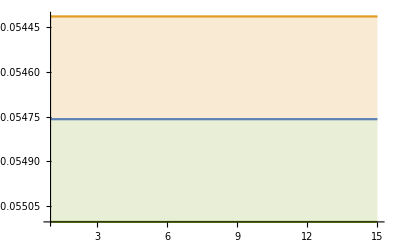

```mathematica
Plot[{fitData[[1]]//.Around[x_,y_]:>x,{fitData[[1]]//.Around[x_,y_]:>x+y,fitData[[1]]//.Around[x_,y_]:>x-y}},{x,1,15},Filling->{3->{1},2->{1}}]
```

```mathematica
SpoilHWFLOPlotN3=Show[Plot[{fitData[[1]]//.Around[x_,y_]:>x,{fitData[[1]]//.Around[x_,y_]:>x+y,fitData[[1]]//.Around[x_,y_]:>x-y}},{x,1,Length[meanErr2[[5]]]},Filling->{3->{1},2->{1}},PlotRange->{-.5,.1}],ListPlot[{Table[{τSteps[[1,i]],meanErr2[[1,i]]},{i,1,Length[meanErr2[[1]]]}],Table[{τSteps[[2,i]],meanErr2[[2,i]]},{i,1,Length[meanErr2[[2]]]}],Table[{τSteps[[3,i]],meanErr2[[3,i]]},{i,1,Length[meanErr2[[3]]]}],Table[{τSteps[[4,i]],meanErr2[[4,i]]},{i,1,Length[meanErr2[[4]]]}],Table[{τSteps[[5,i]],meanErr2[[5,i]]},{i,1,Length[meanErr2[[5]]]}]},PlotRange->{-.03,-0.005},PlotLegends->Placed[αLegendLO,{0.5,0.1}],PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]],markerlist[[4]],markerlist[[5]]},IntervalMarkersStyle->{ColorData[97][3]},PlotStyle->{ColorData[97][3]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau_{\\text{steps}}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]},PlotLabel->MaTeX["N=3(\\text{LO})",Magnification->1.2]]
```

-Graphics-

#### QCD mNLO - gauss

```mathematica
Nf4α1LoopMid
Nf4α1LoopStepTab={380,380,380,380,380};
NWalkers=200;
Nf4α1LoopBig={0.229421,0.229421,0.229421,0.229421,0.229421};
aList={1,2,3,4,5};
```

{0.21556,0.220566,0.22639,0.233299,0.241701,0.252265,0.266178,0.285833}

```mathematica
csvData=Table[Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfgauss.csv"],{xx,1,Length[aList]}]
```

({mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.06791566230111687, -0.07423704893151686, -0.06923860362248559, -0.06143887081268073, -0.0674386634736771, -0.06350984273934265, -0.0797840903723794, -0.06861858394924837, -0.07147245433498699, -0.07591766706325022, -0.08220002236289005, -0.07959721092611206, -0.06395471119479602, -0.06845478809715283, -0.08210552881657979, -0.08064909731593269, -0.1321663867567614, -0.07726435672501698, -0.07938349096659643, -0.06609414996658333, -0.09357620185380702, -0.0996561365822952, -0.07608329599629779, -0.08387917712446331, -0.07917323247311696, -0.07127758017766622, -0.08510352486503504, -0.06667547825830797, -0.05452483160058602, -0.07163881058351253, -0.06169719907223136, -0.07247152416394467, -0.07914522356508692, -0.09133848314639964, -0.16988326527718406],[0.007413309956204048, 0.020359288688084343, 0.01588727972955028, 0.00847433819439867, 0.020790130172460015, 0.017225088207113094, 0.07173443212663765, 0.042068741159668514, 0.056399261854144504, 0.09110474330963611, 0.12574350724358488, 0.14281801636824804, 0.08197584973373731, 0.11993840706514505, 0.24946895139047703, 0.4058810386260394, 1.511875558580333, 0.512749754678648, 0.5079889901844405, 0.402946720357147, 1.048888776777621, 1.6004854945166276, 0.9280311418131502, 1.248812709550041, 1.580727555230176, 1.3669675980304905, 2.183013209533362, 1.6183272346582975, 1.3683230042128822, 3.0652672313561524, 2.2907868206978934, 4.756149401762206, 6.720631889496616, 17.129715830696362, 57.20665299283166],-0.0644455,0.000416897,0.788885}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.054510229216300735, -0.05659220167564951, -0.06151305091980116, -0.05501609374705905, -0.05469171111833498, -0.057311781454773884, -0.05161404086241811, -0.05436261263102925, -0.051676221126294566, -0.05760130082832936, -0.06787187112564443, -0.06826085957150527, -0.055902284207227426, -0.06834895701761777, -0.05828956697030054, -0.057594954282060906, -0.05888095633524661, -0.06402678173914692, -0.0645984576425266, -0.05727076324058797, -0.05309831639690134, -0.049784638742666705, -0.050571323667632034, -0.05057257038479407, -0.0508824619208923, -0.058740905751078314, -0.059547889519340626, -0.05734971095511583, -0.05247264441921822, -0.05396669312829383, -0.06009527696595371, -0.061453467123081314, -0.06120700612898719, -0.05919764762365821, -0.06068884893684487],[0.008821006814236827, 0.009854380357955552, 0.015882095030857232, 0.014977999299240052, 0.017421412833839064, 0.02781819575297063, 0.021556227948613737, 0.029119147991142975, 0.02467864644286301, 0.03980770360989407, 0.07968327556161126, 0.09005356796878103, 0.059895501468116376, 0.13144079364023167, 0.08099058792094926, 0.09542726653119721, 0.11239211402847071, 0.18145007099565477, 0.19268819530167458, 0.17802142973296153, 0.15819611738774567, 0.15131312976819383, 0.16773415127628039, 0.18135765514140903, 0.19784202530359885, 0.4082769504045786, 0.37828677356816026, 0.44277129179546043, 0.3764422547624145, 0.5048378415210102, 0.7639450139005762, 0.9662104633175297, 1.291763800141859, 1.3512814801744824, 1.6773482460527105],-0.049463,0.000778896,0.288134}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.03335504629093901, -0.03620028268460645, -0.03426972530912566, -0.03395800375314509, -0.035866401008805206, -0.03646772193107841, -0.03665761120920345, -0.03785642576918437, -0.039683174472603215, -0.03927798298260789, -0.04035438227973423, -0.03942918974345309, -0.04116637070721457, -0.04390448475405356, -0.048290419543506484, -0.046763244173105255, -0.04696688962555569, -0.04978183575323293, -0.045464167940671416, -0.045795324622465786, -0.047511692490472913, -0.04906219473197064, -0.0508829776693165, -0.053399478415466134, -0.05318427396474603, -0.059046953270704514, -0.06557742418458778, -0.06843159667068545, -0.05943315300808846, -0.047393193606422586, -0.050754553155185705, -0.05327435176792588, -0.05479850496321655, -0.060981102979228666, -0.0720338386863016],[0.00218028456119751, 0.004387074121877057, 0.003112948501968107, 0.0031962847225436297, 0.00444447846583782, 0.004911440762639342, 0.005677745961307356, 0.006986221868744978, 0.009443983847534827, 0.009763909589172037, 0.011965148969036868, 0.011305853133417849, 0.01437299344068484, 0.019877134887228694, 0.030613630118983964, 0.03243409835203369, 0.03676080877234931, 0.053963278912188155, 0.04423920365370355, 0.0466700972660424, 0.062030681628553394, 0.07934558282739652, 0.10284192845495368, 0.14091376983274437, 0.16188474611530188, 0.2605576332696759, 0.33746856768110917, 0.48671492630637464, 0.42359892446029124, 0.2966608276682564, 0.36958209141183557, 0.40577623590353395, 0.5545227089961027, 0.6329966619160393, 0.9231176456984242],-0.0344071,0.00071771,0.291361}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.026676601938612193, -0.027303758721024154, -0.027176544976156364, -0.02698673755553763, -0.02724955827525924, -0.02791751657924911, -0.029107560493368708, -0.031149309539994015, -0.02907246940897806, -0.028521619620527554, -0.029811246827307257, -0.030182058965369154, -0.030962240970110248, -0.0314081963904062, -0.030962309959591153, -0.03069779152966421, -0.03210148851057837, -0.03284531876481117, -0.032297141669918636, -0.03218896194691304, -0.033738942394812454, -0.03338029398561579, -0.0330441086238709, -0.0333618772015431, -0.034970436968705894, -0.03320977388467313, -0.0359849393142759, -0.03741402323299329, -0.03783192125000314, -0.03672954249611721, -0.03865909644016676, -0.04238013328185859, -0.03956149696382807, -0.039545892500180084, -0.04015776010748028],[0.001799558498890694, 0.0022510068919870774, 0.0025019295092405043, 0.0025075300640005032, 0.0029105972683784367, 0.0035436443553607247, 0.004814034704612561, 0.008351425920597875, 0.006424164686951565, 0.0059648332935983775, 0.007851311387062108, 0.008570114060912673, 0.009822915343029669, 0.011598331348351035, 0.01086102121819701, 0.011190766508349529, 0.012947526701580609, 0.015842947330652755, 0.015438449080634888, 0.01604046485233877, 0.020879300397967985, 0.021378495838375734, 0.022542113672928535, 0.026996729055085194, 0.03049211341518287, 0.02860583075902534, 0.037576526120852174, 0.04299001575696724, 0.05002390517609145, 0.052222435320726936, 0.06392035199239929, 0.08636054515563814, 0.08786607645089763, 0.09033057997512739, 0.10060184417439118],-0.0252357,0.000586396,0.217298}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.021981338598485656, -0.022486024056398386, -0.022588859154699895, -0.023261855992226976, -0.023336332592552664, -0.024897161959997933, -0.023928260376509584, -0.02396914290493422, -0.0397750714334764, -0.035409986519028165, -0.03174118697531338, -0.0319473690770356, -0.031128197778416918, -0.0320378464552772, -0.03565202641748179, -0.03816793526094467, -0.03624439640582554, -0.043858487041887155, -0.05238896649538249, -0.05216710405266691, -0.043004484586169144, -0.04603471571688456, -0.04024173928500853, -0.03442413407575964, -0.03719403192469701, -0.03702538750784799, -0.039529847762734625, -0.040390639765252374, -0.036259975229366886, -0.03280247586133043, -0.03317528462816329, -0.03263193328831768, -0.030337284074248176, -0.029057626300507202, -0.027479737707937952],[0.0010930406275240657, 0.00129802723253247, 0.001582259875887861, 0.0022733339825707424, 0.00259952000686263, 0.004827811014395308, 0.0035947450914503238, 0.0036804843396147095, 0.03024651928376588, 0.023469461753704644, 0.01982838061385658, 0.021063690471685353, 0.02039768645501344, 0.022943623854477627, 0.03322927281148848, 0.043365513521912494, 0.03880700241239247, 0.06753985387987, 0.11089851503606439, 0.1266328480815119, 0.0968491938125207, 0.12488071134759732, 0.10973254853633202, 0.09075762341092644, 0.11250265528705224, 0.1202366361496792, 0.14696224614158274, 0.16107871451779215, 0.14359455722327596, 0.12766953110558338, 0.1424779740958511, 0.15078721948206217, 0.13835116489493687, 0.13517804596850092, 0.12828073092307304],-0.0224412,0.000299175,0.65741})

```mathematica
meanErr=Table[Table[csvData[[xx,2,yy]]//StringSplit[#,{",","[","]"}]&,{yy,1,2}],{xx,1,Length[aList]}]
```

({-0.06791566230111687, -0.07423704893151686, -0.06923860362248559, -0.06143887081268073, -0.0674386634736771, -0.06350984273934265, -0.0797840903723794, -0.06861858394924837, -0.07147245433498699, -0.07591766706325022, -0.08220002236289005, -0.07959721092611206, -0.06395471119479602, -0.06845478809715283, -0.08210552881657979, -0.08064909731593269, -0.1321663867567614, -0.07726435672501698, -0.07938349096659643, -0.06609414996658333, -0.09357620185380702, -0.0996561365822952, -0.07608329599629779, -0.08387917712446331, -0.07917323247311696, -0.07127758017766622, -0.08510352486503504, -0.06667547825830797, -0.05452483160058602, -0.07163881058351253, -0.06169719907223136, -0.07247152416394467, -0.07914522356508692, -0.09133848314639964, -0.16988326527718406} | {0.007413309956204048, 0.020359288688084343, 0.01588727972955028, 0.00847433819439867, 0.020790130172460015, 0.017225088207113094, 0.07173443212663765, 0.042068741159668514, 0.056399261854144504, 0.09110474330963611, 0.12574350724358488, 0.14281801636824804, 0.08197584973373731, 0.11993840706514505, 0.24946895139047703, 0.4058810386260394, 1.511875558580333, 0.512749754678648, 0.5079889901844405, 0.402946720357147, 1.048888776777621, 1.6004854945166276, 0.9280311418131502, 1.248812709550041, 1.580727555230176, 1.3669675980304905, 2.183013209533362, 1.6183272346582975, 1.3683230042128822, 3.0652672313561524, 2.2907868206978934, 4.756149401762206, 6.720631889496616, 17.129715830696362, 57.20665299283166}
{-0.054510229216300735, -0.05659220167564951, -0.06151305091980116, -0.05501609374705905, -0.05469171111833498, -0.057311781454773884, -0.05161404086241811, -0.05436261263102925, -0.051676221126294566, -0.05760130082832936, -0.06787187112564443, -0.06826085957150527, -0.055902284207227426, -0.06834895701761777, -0.05828956697030054, -0.057594954282060906, -0.05888095633524661, -0.06402678173914692, -0.0645984576425266, -0.05727076324058797, -0.05309831639690134, -0.049784638742666705, -0.050571323667632034, -0.05057257038479407, -0.0508824619208923, -0.058740905751078314, -0.059547889519340626, -0.05734971095511583, -0.05247264441921822, -0.05396669312829383, -0.06009527696595371, -0.061453467123081314, -0.06120700612898719, -0.05919764762365821, -0.06068884893684487} | {0.008821006814236827, 0.009854380357955552, 0.015882095030857232, 0.014977999299240052, 0.017421412833839064, 0.02781819575297063, 0.021556227948613737, 0.029119147991142975, 0.02467864644286301, 0.03980770360989407, 0.07968327556161126, 0.09005356796878103, 0.059895501468116376, 0.13144079364023167, 0.08099058792094926, 0.09542726653119721, 0.11239211402847071, 0.18145007099565477, 0.19268819530167458, 0.17802142973296153, 0.15819611738774567, 0.15131312976819383, 0.16773415127628039, 0.18135765514140903, 0.19784202530359885, 0.4082769504045786, 0.37828677356816026, 0.44277129179546043, 0.3764422547624145, 0.5048378415210102, 0.7639450139005762, 0.9662104633175297, 1.291763800141859, 1.3512814801744824, 1.6773482460527105}
{-0.03335504629093901, -0.03620028268460645, -0.03426972530912566, -0.03395800375314509, -0.035866401008805206, -0.03646772193107841, -0.03665761120920345, -0.03785642576918437, -0.039683174472603215, -0.03927798298260789, -0.04035438227973423, -0.03942918974345309, -0.04116637070721457, -0.04390448475405356, -0.048290419543506484, -0.046763244173105255, -0.04696688962555569, -0.04978183575323293, -0.045464167940671416, -0.045795324622465786, -0.047511692490472913, -0.04906219473197064, -0.0508829776693165, -0.053399478415466134, -0.05318427396474603, -0.059046953270704514, -0.06557742418458778, -0.06843159667068545, -0.05943315300808846, -0.047393193606422586, -0.050754553155185705, -0.05327435176792588, -0.05479850496321655, -0.060981102979228666, -0.0720338386863016} | {0.00218028456119751, 0.004387074121877057, 0.003112948501968107, 0.0031962847225436297, 0.00444447846583782, 0.004911440762639342, 0.005677745961307356, 0.006986221868744978, 0.009443983847534827, 0.009763909589172037, 0.011965148969036868, 0.011305853133417849, 0.01437299344068484, 0.019877134887228694, 0.030613630118983964, 0.03243409835203369, 0.03676080877234931, 0.053963278912188155, 0.04423920365370355, 0.0466700972660424, 0.062030681628553394, 0.07934558282739652, 0.10284192845495368, 0.14091376983274437, 0.16188474611530188, 0.2605576332696759, 0.33746856768110917, 0.48671492630637464, 0.42359892446029124, 0.2966608276682564, 0.36958209141183557, 0.40577623590353395, 0.5545227089961027, 0.6329966619160393, 0.9231176456984242}
{-0.026676601938612193, -0.027303758721024154, -0.027176544976156364, -0.02698673755553763, -0.02724955827525924, -0.02791751657924911, -0.029107560493368708, -0.031149309539994015, -0.02907246940897806, -0.028521619620527554, -0.029811246827307257, -0.030182058965369154, -0.030962240970110248, -0.0314081963904062, -0.030962309959591153, -0.03069779152966421, -0.03210148851057837, -0.03284531876481117, -0.032297141669918636, -0.03218896194691304, -0.033738942394812454, -0.03338029398561579, -0.0330441086238709, -0.0333618772015431, -0.034970436968705894, -0.03320977388467313, -0.0359849393142759, -0.03741402323299329, -0.03783192125000314, -0.03672954249611721, -0.03865909644016676, -0.04238013328185859, -0.03956149696382807, -0.039545892500180084, -0.04015776010748028} | {0.001799558498890694, 0.0022510068919870774, 0.0025019295092405043, 0.0025075300640005032, 0.0029105972683784367, 0.0035436443553607247, 0.004814034704612561, 0.008351425920597875, 0.006424164686951565, 0.0059648332935983775, 0.007851311387062108, 0.008570114060912673, 0.009822915343029669, 0.011598331348351035, 0.01086102121819701, 0.011190766508349529, 0.012947526701580609, 0.015842947330652755, 0.015438449080634888, 0.01604046485233877, 0.020879300397967985, 0.021378495838375734, 0.022542113672928535, 0.026996729055085194, 0.03049211341518287, 0.02860583075902534, 0.037576526120852174, 0.04299001575696724, 0.05002390517609145, 0.052222435320726936, 0.06392035199239929, 0.08636054515563814, 0.08786607645089763, 0.09033057997512739, 0.10060184417439118}
{-0.021981338598485656, -0.022486024056398386, -0.022588859154699895, -0.023261855992226976, -0.023336332592552664, -0.024897161959997933, -0.023928260376509584, -0.02396914290493422, -0.0397750714334764, -0.035409986519028165, -0.03174118697531338, -0.0319473690770356, -0.031128197778416918, -0.0320378464552772, -0.03565202641748179, -0.03816793526094467, -0.03624439640582554, -0.043858487041887155, -0.05238896649538249, -0.05216710405266691, -0.043004484586169144, -0.04603471571688456, -0.04024173928500853, -0.03442413407575964, -0.03719403192469701, -0.03702538750784799, -0.039529847762734625, -0.040390639765252374, -0.036259975229366886, -0.03280247586133043, -0.03317528462816329, -0.03263193328831768, -0.030337284074248176, -0.029057626300507202, -0.027479737707937952} | {0.0010930406275240657, 0.00129802723253247, 0.001582259875887861, 0.0022733339825707424, 0.00259952000686263, 0.004827811014395308, 0.0035947450914503238, 0.0036804843396147095, 0.03024651928376588, 0.023469461753704644, 0.01982838061385658, 0.021063690471685353, 0.02039768645501344, 0.022943623854477627, 0.03322927281148848, 0.043365513521912494, 0.03880700241239247, 0.06753985387987, 0.11089851503606439, 0.1266328480815119, 0.0968491938125207, 0.12488071134759732, 0.10973254853633202, 0.09075762341092644, 0.11250265528705224, 0.1202366361496792, 0.14696224614158274, 0.16107871451779215, 0.14359455722327596, 0.12766953110558338, 0.1424779740958511, 0.15078721948206217, 0.13835116489493687, 0.13517804596850092, 0.12828073092307304})

```mathematica
meanErr[[1,2,1]]//ToExpression
```

0.00741331

```mathematica
meanErr[[1]]
```

(-0.06791566230111687 |  -0.07423704893151686 |  -0.06923860362248559 |  -0.06143887081268073 |  -0.0674386634736771 |  -0.06350984273934265 |  -0.0797840903723794 |  -0.06861858394924837 |  -0.07147245433498699 |  -0.07591766706325022 |  -0.08220002236289005 |  -0.07959721092611206 |  -0.06395471119479602 |  -0.06845478809715283 |  -0.08210552881657979 |  -0.08064909731593269 |  -0.1321663867567614 |  -0.07726435672501698 |  -0.07938349096659643 |  -0.06609414996658333 |  -0.09357620185380702 |  -0.0996561365822952 |  -0.07608329599629779 |  -0.08387917712446331 |  -0.07917323247311696 |  -0.07127758017766622 |  -0.08510352486503504 |  -0.06667547825830797 |  -0.05452483160058602 |  -0.07163881058351253 |  -0.06169719907223136 |  -0.07247152416394467 |  -0.07914522356508692 |  -0.09133848314639964 |  -0.16988326527718406
0.007413309956204048 |  0.020359288688084343 |  0.01588727972955028 |  0.00847433819439867 |  0.020790130172460015 |  0.017225088207113094 |  0.07173443212663765 |  0.042068741159668514 |  0.056399261854144504 |  0.09110474330963611 |  0.12574350724358488 |  0.14281801636824804 |  0.08197584973373731 |  0.11993840706514505 |  0.24946895139047703 |  0.4058810386260394 |  1.511875558580333 |  0.512749754678648 |  0.5079889901844405 |  0.402946720357147 |  1.048888776777621 |  1.6004854945166276 |  0.9280311418131502 |  1.248812709550041 |  1.580727555230176 |  1.3669675980304905 |  2.183013209533362 |  1.6183272346582975 |  1.3683230042128822 |  3.0652672313561524 |  2.2907868206978934 |  4.756149401762206 |  6.720631889496616 |  17.129715830696362 |  57.20665299283166)

```mathematica
meanErr2=Table[Table[Around[meanErr[[xx,1,yy]]//ToExpression,meanErr[[xx,2,yy]]//ToExpression],{yy,1,Length[meanErr[[xx,1]]]}],{xx,1,Length[aList]}]
```

(-0.0680.007 | -0.0740.020 | -0.0690.016 | -0.0610.008 | -0.0670.021 | -0.0640.017 | -0.080.07 | -0.070.04 | -0.070.06 | -0.080.09 | -0.080.13 | -0.080.14 | -0.060.08 | -0.070.12 | -0.080.25 | 0.00.4 | -0.11.5 | 0.00.5 | 0.00.5 | 0.00.4 | 0.01.0 | 0.01.6 | 0.00.9 | 0.01.2 | 0.01.6 | 0.01.4 | 0.02.2 | 0.01.6 | 0.01.4 | 0.03.1 | 0.02.3 | 0.5. | 0.7. | 0.17. | 0.57.
-0.0550.009 | -0.0570.010 | -0.0620.016 | -0.0550.015 | -0.0550.017 | -0.0570.028 | -0.0520.022 | -0.0540.029 | -0.0520.025 | -0.060.04 | -0.070.08 | -0.070.09 | -0.060.06 | -0.070.13 | -0.060.08 | -0.060.10 | -0.060.11 | -0.060.18 | -0.060.19 | -0.060.18 | -0.050.16 | -0.050.15 | -0.050.17 | -0.050.18 | -0.050.20 | 0.00.4 | 0.00.4 | 0.00.4 | 0.00.4 | 0.00.5 | 0.00.8 | 0.01.0 | 0.01.3 | 0.01.4 | 0.01.7
-0.03340.0022 | -0.0360.004 | -0.03430.0031 | -0.03400.0032 | -0.0360.004 | -0.0360.005 | -0.0370.006 | -0.0380.007 | -0.0400.009 | -0.0390.010 | -0.0400.012 | -0.0390.011 | -0.0410.014 | -0.0440.020 | -0.0480.031 | -0.0470.032 | -0.050.04 | -0.050.05 | -0.050.04 | -0.050.05 | -0.050.06 | -0.050.08 | -0.050.10 | -0.050.14 | -0.050.16 | -0.060.26 | -0.070.34 | 0.00.5 | 0.00.4 | -0.050.30 | 0.00.4 | 0.00.4 | 0.00.6 | 0.00.6 | 0.00.9
-0.02670.0018 | -0.02730.0023 | -0.02720.0025 | -0.02700.0025 | -0.02720.0029 | -0.02790.0035 | -0.0290.005 | -0.0310.008 | -0.0290.006 | -0.0290.006 | -0.0300.008 | -0.0300.009 | -0.0310.010 | -0.0310.012 | -0.0310.011 | -0.0310.011 | -0.0320.013 | -0.0330.016 | -0.0320.015 | -0.0320.016 | -0.0340.021 | -0.0330.021 | -0.0330.023 | -0.0330.027 | -0.0350.030 | -0.0330.029 | -0.040.04 | -0.040.04 | -0.040.05 | -0.040.05 | -0.040.06 | -0.040.09 | -0.040.09 | -0.040.09 | -0.040.10
-0.02200.0011 | -0.02250.0013 | -0.02260.0016 | -0.02330.0023 | -0.02330.0026 | -0.0250.005 | -0.0240.004 | -0.0240.004 | -0.0400.030 | -0.0350.023 | -0.0320.020 | -0.0320.021 | -0.0310.020 | -0.0320.023 | -0.0360.033 | -0.040.04 | -0.040.04 | -0.040.07 | -0.050.11 | -0.050.13 | -0.040.10 | -0.050.12 | -0.040.11 | -0.030.09 | -0.040.11 | -0.040.12 | -0.040.15 | -0.040.16 | -0.040.14 | -0.030.13 | -0.030.14 | -0.030.15 | -0.030.14 | -0.030.14 | -0.030.13)

```mathematica
τSteps=Table[Table[xx,{xx,1,Length[meanErr2[[yy]]]}],{yy,1,Length[meanErr2]}]
```

(1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35)

```mathematica
fitData=Table[Around[Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfgauss.csv"][[2,3]],Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfgauss.csv"][[2,4]]],{xx,1,Length[aList]}]
```

{-0.06440.0004,-0.04950.0008,-0.03440.0007,-0.02520.0006,-0.022440.00030}

```mathematica
αLegendLO=PointLegend[Table[Directive[ColorData[97][1]],{ii,5}],{MaTeX["a=1",Magnification->0.8],MaTeX["a=2",Magnification->0.8],MaTeX["a=3",Magnification->0.8],MaTeX["a=4",Magnification->0.8],MaTeX["a=5",Magnification->0.8]},LegendMarkers->Table[Style[markerlist[[ii]],14,Bold,ColorData[97][3]],{ii,5}],LegendLayout->"Row",LegendMargins->0.5,LegendFunction->frame]
```

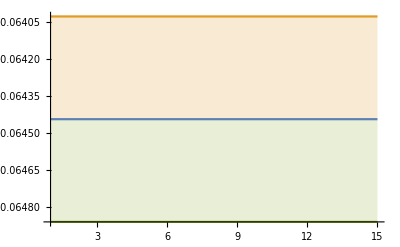

```mathematica
Plot[{fitData[[1]]//.Around[x_,y_]:>x,{fitData[[1]]//.Around[x_,y_]:>x+y,fitData[[1]]//.Around[x_,y_]:>x-y}},{x,1,15},Filling->{3->{1},2->{1}}]
```

```mathematica
SpoilHWFLOPlotN3=Show[Plot[{fitData[[1]]//.Around[x_,y_]:>x,{fitData[[1]]//.Around[x_,y_]:>x+y,fitData[[1]]//.Around[x_,y_]:>x-y}},{x,1,Length[meanErr2[[5]]]},Filling->{3->{1},2->{1}},PlotRange->{-1,.1}],ListPlot[{Table[{τSteps[[1,i]],meanErr2[[1,i]]},{i,1,Length[meanErr2[[1]]]}],Table[{τSteps[[2,i]],meanErr2[[2,i]]},{i,1,Length[meanErr2[[2]]]}],Table[{τSteps[[3,i]],meanErr2[[3,i]]},{i,1,Length[meanErr2[[3]]]}],Table[{τSteps[[4,i]],meanErr2[[4,i]]},{i,1,Length[meanErr2[[4]]]}],Table[{τSteps[[5,i]],meanErr2[[5,i]]},{i,1,Length[meanErr2[[5]]]}]},PlotRange->{-.1,-0.005},PlotLegends->Placed[αLegendLO,{0.5,0.1}],PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]],markerlist[[4]],markerlist[[5]]},IntervalMarkersStyle->{ColorData[97][3]},PlotStyle->{ColorData[97][3]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau_{\\text{steps}}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]},PlotLabel->MaTeX["N=3(\\text{LO})",Magnification->1.2]]
```

-Graphics-

#### QCD NNLO - gauss

```mathematica
Nf4α1LoopMid
Nf4α1LoopStepTab={393,393,393,393,393};
NWalkers=200;
Nf4α1LoopBig={0.225626,0.225626,0.225626,0.225626,0.225626};
aList={1,2,3,4,5};
```

{0.21556,0.220566,0.22639,0.233299,0.241701,0.252265,0.266178,0.285833}

```mathematica
csvData=Table[Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfgauss.csv"],{xx,1,Length[aList]}]
```

({mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.10298068285388369, -0.10441763994527639, -0.1086605260897322, -0.10601251906038292, -0.09946982981888712, -0.10756384671207353, -0.10448570536269314, -0.10801630459855671, -0.10352738921616966, -0.10321379268417105, -0.10314614398193575, -0.10833916099180171, -0.10196000243494778, -0.10430190421236037, -0.10264237291815297, -0.10745365005897463, -0.11783806296747264, -0.10901901318668267, -0.1235158363614788, -0.10172415018599336, -0.09590777133457826, -0.1032285818307777, -0.09943054876452506, -0.09946309367879055, -0.09216431205053767, -0.10040107040962126, -0.09779923190463266, -0.10087097943668634, -0.10001645707587387, -0.10472400353750422, -0.1046176215557688, -0.11490688342590173, -0.10882140470849702, -0.10408053534606553, -0.10192809207906607, -0.11405105470136567],[0.01192176591456885, 0.017904999960601176, 0.028532833050795448, 0.03559232740984749, 0.02949384155973866, 0.06334689576110983, 0.06383043592014807, 0.09444942817310471, 0.10788435172582088, 0.14514182023117325, 0.16840983932271453, 0.20623404384544633, 0.2371584949854651, 0.30284119382934543, 0.36925840502065466, 0.538696864439766, 1.1850398814406047, 1.1263311494389243, 2.208617071956349, 1.8932872074683484, 1.7319994292841439, 2.423941019976917, 2.600414536828222, 3.110911162720659, 3.4771588610671467, 4.639480617933088, 5.728522503225372, 7.704381421239161, 9.361263523050736, 12.458366113348662, 17.21118187506733, 28.02039631416057, 27.51918297322604, 28.631213637707397, 36.781852990668405, 75.58433303435329],-0.0958243,0.000442399,0.888647}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.07454500042024226, -0.07692285147119805, -0.07662563174141213, -0.07803957401376774, -0.07612703444302037, -0.08136803368429953, -0.08096470012815891, -0.07776812410830194, -0.10680811856297569, -0.08178625825326487, -0.09107558604946821, -0.09107754852337746, -0.09158127479777901, -0.09681024648443821, -0.10731881452982214, -0.10711326102833653, -0.10291232952559547, -0.10779909879328047, -0.10566377684483341, -0.09694189556693189, -0.09284452940520793, -0.10125173299943777, -0.08411451977340408, -0.08230616439884005, -0.08535185283061453, -0.08490847957513621, -0.0849509710074015, -0.08449461554974458, -0.08824398371729926, -0.0899233126892321, -0.09293246858936152, -0.10084388200238947, -0.09195092181486705, -0.09510678945802478, -0.08238317506212003, -0.08619420401454868],[0.00731430272511923, 0.011015580857825348, 0.012680365758514448, 0.018523746680419645, 0.019038880105455642, 0.029074656446769338, 0.03528754944176379, 0.037998871566162974, 0.18383792474688485, 0.06871247231892288, 0.11503013971029519, 0.14854637215607738, 0.1776579025416775, 0.27371718673785284, 0.5401531702357533, 0.7826426488381262, 0.8859629641182357, 1.3307219267181, 1.6508894626161554, 1.7601842963765142, 1.7396680756176865, 2.39178598199775, 2.2349157717319463, 2.605345870355494, 3.252955384197954, 3.8169523584224474, 4.570659837499224, 5.037151561524204, 6.3349527726627946, 8.537414459550513, 9.668017085280292, 13.105037893746873, 14.94007782432725, 18.485680876264034, 17.582716978332254, 21.64783725287397],-0.0751114,0.000866994,0.33495}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.05640741277715497, -0.05761199786885635, -0.058486872302424976, -0.05810954182720924, -0.06301273668551435, -0.06592209405135177, -0.06780176503138251, -0.06355331091127023, -0.06335348995103637, -0.062354195357206724, -0.061889990981129364, -0.06237655131565514, -0.0650335080556378, -0.06889316678340389, -0.0815123341399502, -0.07237002134862315, -0.07848641826693174, -0.0856330735800641, -0.0830628404328737, -0.0792919607241555, -0.07533241309189755, -0.07553532362190564, -0.07260956216319492, -0.07356333370812165, -0.07357191050850319, -0.07285860134765901, -0.07418247652296842, -0.07515848684336365, -0.07971330094723657, -0.07789832516542211, -0.08127662627277168, -0.0771921510137551, -0.07987071752647484, -0.1090009054124291, -0.09196242962630097, -0.1071366576155422],[0.0038392885479251997, 0.005103875480918586, 0.006329862848920329, 0.007367510886563371, 0.016937631961192634, 0.02225017740539809, 0.037051131070143184, 0.02847361681404354, 0.03047871828659318, 0.0323459417625784, 0.03791941269110546, 0.04352787895332989, 0.06022808514998767, 0.08628166809189833, 0.19959348967193932, 0.16058228889994272, 0.24848260431473543, 0.3629605358911468, 0.40175203372407076, 0.42882670765649716, 0.4379003037927573, 0.5169400386622153, 0.5438574144857726, 0.6672398586626404, 0.7780508300575348, 0.9183279845275502, 1.1172446147545214, 1.2790241018308552, 1.694098216279027, 2.070971134450117, 2.8281717833878584, 2.9554617926199307, 3.7637900966934037, 8.47252385329095, 7.9766414091811155, 14.41544836193278],-0.0578416,0.000850435,0.370265}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.04724857268548678, -0.04847263384277376, -0.048804688520815716, -0.048583645159926504, -0.049361770217566284, -0.051874048871466745, -0.050425852104158043, -0.05107160258246431, -0.05191509239377429, -0.05176102837649946, -0.05338676173088204, -0.05376717615171676, -0.06173802025887402, -0.07311680869730042, -0.09506925734459612, -0.08727552205721614, -0.09210591331740792, -0.09939495572686469, -0.09806422650353996, -0.08892354210680017, -0.08665999703471136, -0.08651697734008316, -0.08767081889930697, -0.08852079417263836, -0.09400668008238802, -0.08148088918919233, -0.08334010929671623, -0.09569670512030731, -0.09699294945804364, -0.08739864495361009, -0.09075907505257322, -0.08964135689017444, -0.07951609260232932, -0.08169185817900637, -0.0823348961195725, -0.0727819637474005],[0.0036422400415223027, 0.005101951989450355, 0.005746251594199854, 0.0063610277347734235, 0.007714757167252358, 0.011299578361762383, 0.010738657633061074, 0.013180457823015778, 0.01642226466231291, 0.018430885221138817, 0.02533300230691709, 0.0292317424804746, 0.06100699689313491, 0.12544709620327282, 0.29774309163036844, 0.32674427977859954, 0.4318801774786416, 0.6047770275622404, 0.7362906333166855, 0.7802881006220607, 0.8152627609210462, 1.0089671896943921, 1.148439841886861, 1.393088120229022, 1.7741718399578976, 1.8668046578987576, 2.2940168936904195, 3.155542830971829, 3.8409515708521407, 4.416227570738711, 5.57149229258347, 6.940104925534477, 7.1601375833846355, 8.631609526573978, 10.490994191209852, 10.175887890099224],-0.0461801,0.000857254,0.341812}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.040299434189476666, -0.04122514113020207, -0.042407694154886086, -0.0435298349178069, -0.04311152928449252, -0.043400138667178415, -0.04276369308065653, -0.04397727129540698, -0.045995703600611386, -0.04641679008792596, -0.04591806313760495, -0.04721417140959395, -0.04782728332169303, -0.04749510626840142, -0.04779533779578197, -0.050757025613288057, -0.049092360548519204, -0.05092742826748976, -0.054449542397999345, -0.06002096515653873, -0.061065724727726756, -0.062471956940641366, -0.05992428265270471, -0.06420031790076519, -0.06663822681343265, -0.06945749138750731, -0.07067082944639684, -0.07649455643278319, -0.09655685792452955, -0.10092621957560804, -0.12238550240241082, -0.1403166698877811, -0.13750322901104312, -0.10747061472983001, -0.0900565694797944, -0.08519275127241059],[0.0023763350757751616, 0.00324375217998021, 0.005029119780315581, 0.006818506207954489, 0.007020636774575118, 0.008010190598051217, 0.008513346010650588, 0.011217525689110873, 0.016334876628327867, 0.01869660122121161, 0.01859085842488932, 0.024466964084216312, 0.028427121013609932, 0.03145234815015806, 0.03566009515389196, 0.05659634376498436, 0.05318048139823534, 0.06861022320765352, 0.09690044565358537, 0.15008189356094218, 0.17241474471069781, 0.20639211596882462, 0.2104269668200259, 0.2642300628916393, 0.31691214572306725, 0.3966100852836048, 0.48752943509483454, 0.6636853676741628, 1.3213815167235188, 1.8403285608419442, 3.288327869211141, 5.680206455114188, 8.158570015483136, 8.12011413314721, 8.079380963010385, 9.169454592274668],-0.0391727,0.000788412,0.183801})

```mathematica
meanErr=Table[Table[csvData[[xx,2,yy]]//StringSplit[#,{",","[","]"}]&,{yy,1,2}],{xx,1,Length[aList]}]
```

({-0.10298068285388369, -0.10441763994527639, -0.1086605260897322, -0.10601251906038292, -0.09946982981888712, -0.10756384671207353, -0.10448570536269314, -0.10801630459855671, -0.10352738921616966, -0.10321379268417105, -0.10314614398193575, -0.10833916099180171, -0.10196000243494778, -0.10430190421236037, -0.10264237291815297, -0.10745365005897463, -0.11783806296747264, -0.10901901318668267, -0.1235158363614788, -0.10172415018599336, -0.09590777133457826, -0.1032285818307777, -0.09943054876452506, -0.09946309367879055, -0.09216431205053767, -0.10040107040962126, -0.09779923190463266, -0.10087097943668634, -0.10001645707587387, -0.10472400353750422, -0.1046176215557688, -0.11490688342590173, -0.10882140470849702, -0.10408053534606553, -0.10192809207906607, -0.11405105470136567} | {0.01192176591456885, 0.017904999960601176, 0.028532833050795448, 0.03559232740984749, 0.02949384155973866, 0.06334689576110983, 0.06383043592014807, 0.09444942817310471, 0.10788435172582088, 0.14514182023117325, 0.16840983932271453, 0.20623404384544633, 0.2371584949854651, 0.30284119382934543, 0.36925840502065466, 0.538696864439766, 1.1850398814406047, 1.1263311494389243, 2.208617071956349, 1.8932872074683484, 1.7319994292841439, 2.423941019976917, 2.600414536828222, 3.110911162720659, 3.4771588610671467, 4.639480617933088, 5.728522503225372, 7.704381421239161, 9.361263523050736, 12.458366113348662, 17.21118187506733, 28.02039631416057, 27.51918297322604, 28.631213637707397, 36.781852990668405, 75.58433303435329}
{-0.07454500042024226, -0.07692285147119805, -0.07662563174141213, -0.07803957401376774, -0.07612703444302037, -0.08136803368429953, -0.08096470012815891, -0.07776812410830194, -0.10680811856297569, -0.08178625825326487, -0.09107558604946821, -0.09107754852337746, -0.09158127479777901, -0.09681024648443821, -0.10731881452982214, -0.10711326102833653, -0.10291232952559547, -0.10779909879328047, -0.10566377684483341, -0.09694189556693189, -0.09284452940520793, -0.10125173299943777, -0.08411451977340408, -0.08230616439884005, -0.08535185283061453, -0.08490847957513621, -0.0849509710074015, -0.08449461554974458, -0.08824398371729926, -0.0899233126892321, -0.09293246858936152, -0.10084388200238947, -0.09195092181486705, -0.09510678945802478, -0.08238317506212003, -0.08619420401454868} | {0.00731430272511923, 0.011015580857825348, 0.012680365758514448, 0.018523746680419645, 0.019038880105455642, 0.029074656446769338, 0.03528754944176379, 0.037998871566162974, 0.18383792474688485, 0.06871247231892288, 0.11503013971029519, 0.14854637215607738, 0.1776579025416775, 0.27371718673785284, 0.5401531702357533, 0.7826426488381262, 0.8859629641182357, 1.3307219267181, 1.6508894626161554, 1.7601842963765142, 1.7396680756176865, 2.39178598199775, 2.2349157717319463, 2.605345870355494, 3.252955384197954, 3.8169523584224474, 4.570659837499224, 5.037151561524204, 6.3349527726627946, 8.537414459550513, 9.668017085280292, 13.105037893746873, 14.94007782432725, 18.485680876264034, 17.582716978332254, 21.64783725287397}
{-0.05640741277715497, -0.05761199786885635, -0.058486872302424976, -0.05810954182720924, -0.06301273668551435, -0.06592209405135177, -0.06780176503138251, -0.06355331091127023, -0.06335348995103637, -0.062354195357206724, -0.061889990981129364, -0.06237655131565514, -0.0650335080556378, -0.06889316678340389, -0.0815123341399502, -0.07237002134862315, -0.07848641826693174, -0.0856330735800641, -0.0830628404328737, -0.0792919607241555, -0.07533241309189755, -0.07553532362190564, -0.07260956216319492, -0.07356333370812165, -0.07357191050850319, -0.07285860134765901, -0.07418247652296842, -0.07515848684336365, -0.07971330094723657, -0.07789832516542211, -0.08127662627277168, -0.0771921510137551, -0.07987071752647484, -0.1090009054124291, -0.09196242962630097, -0.1071366576155422} | {0.0038392885479251997, 0.005103875480918586, 0.006329862848920329, 0.007367510886563371, 0.016937631961192634, 0.02225017740539809, 0.037051131070143184, 0.02847361681404354, 0.03047871828659318, 0.0323459417625784, 0.03791941269110546, 0.04352787895332989, 0.06022808514998767, 0.08628166809189833, 0.19959348967193932, 0.16058228889994272, 0.24848260431473543, 0.3629605358911468, 0.40175203372407076, 0.42882670765649716, 0.4379003037927573, 0.5169400386622153, 0.5438574144857726, 0.6672398586626404, 0.7780508300575348, 0.9183279845275502, 1.1172446147545214, 1.2790241018308552, 1.694098216279027, 2.070971134450117, 2.8281717833878584, 2.9554617926199307, 3.7637900966934037, 8.47252385329095, 7.9766414091811155, 14.41544836193278}
{-0.04724857268548678, -0.04847263384277376, -0.048804688520815716, -0.048583645159926504, -0.049361770217566284, -0.051874048871466745, -0.050425852104158043, -0.05107160258246431, -0.05191509239377429, -0.05176102837649946, -0.05338676173088204, -0.05376717615171676, -0.06173802025887402, -0.07311680869730042, -0.09506925734459612, -0.08727552205721614, -0.09210591331740792, -0.09939495572686469, -0.09806422650353996, -0.08892354210680017, -0.08665999703471136, -0.08651697734008316, -0.08767081889930697, -0.08852079417263836, -0.09400668008238802, -0.08148088918919233, -0.08334010929671623, -0.09569670512030731, -0.09699294945804364, -0.08739864495361009, -0.09075907505257322, -0.08964135689017444, -0.07951609260232932, -0.08169185817900637, -0.0823348961195725, -0.0727819637474005} | {0.0036422400415223027, 0.005101951989450355, 0.005746251594199854, 0.0063610277347734235, 0.007714757167252358, 0.011299578361762383, 0.010738657633061074, 0.013180457823015778, 0.01642226466231291, 0.018430885221138817, 0.02533300230691709, 0.0292317424804746, 0.06100699689313491, 0.12544709620327282, 0.29774309163036844, 0.32674427977859954, 0.4318801774786416, 0.6047770275622404, 0.7362906333166855, 0.7802881006220607, 0.8152627609210462, 1.0089671896943921, 1.148439841886861, 1.393088120229022, 1.7741718399578976, 1.8668046578987576, 2.2940168936904195, 3.155542830971829, 3.8409515708521407, 4.416227570738711, 5.57149229258347, 6.940104925534477, 7.1601375833846355, 8.631609526573978, 10.490994191209852, 10.175887890099224}
{-0.040299434189476666, -0.04122514113020207, -0.042407694154886086, -0.0435298349178069, -0.04311152928449252, -0.043400138667178415, -0.04276369308065653, -0.04397727129540698, -0.045995703600611386, -0.04641679008792596, -0.04591806313760495, -0.04721417140959395, -0.04782728332169303, -0.04749510626840142, -0.04779533779578197, -0.050757025613288057, -0.049092360548519204, -0.05092742826748976, -0.054449542397999345, -0.06002096515653873, -0.061065724727726756, -0.062471956940641366, -0.05992428265270471, -0.06420031790076519, -0.06663822681343265, -0.06945749138750731, -0.07067082944639684, -0.07649455643278319, -0.09655685792452955, -0.10092621957560804, -0.12238550240241082, -0.1403166698877811, -0.13750322901104312, -0.10747061472983001, -0.0900565694797944, -0.08519275127241059} | {0.0023763350757751616, 0.00324375217998021, 0.005029119780315581, 0.006818506207954489, 0.007020636774575118, 0.008010190598051217, 0.008513346010650588, 0.011217525689110873, 0.016334876628327867, 0.01869660122121161, 0.01859085842488932, 0.024466964084216312, 0.028427121013609932, 0.03145234815015806, 0.03566009515389196, 0.05659634376498436, 0.05318048139823534, 0.06861022320765352, 0.09690044565358537, 0.15008189356094218, 0.17241474471069781, 0.20639211596882462, 0.2104269668200259, 0.2642300628916393, 0.31691214572306725, 0.3966100852836048, 0.48752943509483454, 0.6636853676741628, 1.3213815167235188, 1.8403285608419442, 3.288327869211141, 5.680206455114188, 8.158570015483136, 8.12011413314721, 8.079380963010385, 9.169454592274668})

```mathematica
meanErr2=Table[Table[Around[meanErr[[xx,1,yy]]//ToExpression,meanErr[[xx,2,yy]]//ToExpression],{yy,1,Length[meanErr[[xx,1]]]}],{xx,1,Length[aList]}]
```

(-0.1030.012 | -0.1040.018 | -0.1090.029 | -0.110.04 | -0.0990.029 | -0.110.06 | -0.100.06 | -0.110.09 | -0.100.11 | -0.100.15 | -0.100.17 | -0.110.21 | -0.100.24 | -0.100.30 | -0.10.4 | -0.10.5 | -0.11.2 | -0.11.1 | -0.12.2 | -0.11.9 | 0.01.7 | -0.12.4 | 0.02.6 | 0.03.1 | 0.03.5 | 0.5. | 0.6. | 0.8. | 0.9. | 0.12. | 0.17. | 0.28. | 0.28. | 0.29. | 0.37. | 0.76.
-0.0750.007 | -0.0770.011 | -0.0770.013 | -0.0780.019 | -0.0760.019 | -0.0810.029 | -0.0810.035 | -0.080.04 | -0.110.18 | -0.080.07 | -0.090.12 | -0.090.15 | -0.090.18 | -0.100.27 | -0.10.5 | -0.10.8 | -0.10.9 | -0.11.3 | -0.11.7 | 0.01.8 | 0.01.7 | -0.12.4 | 0.02.2 | 0.02.6 | 0.03.3 | 0.4. | 0.5. | 0.5. | 0.6. | 0.9. | 0.10. | 0.13. | 0.15. | 0.18. | 0.18. | 0.22.
-0.0560.004 | -0.0580.005 | -0.0580.006 | -0.0580.007 | -0.0630.017 | -0.0660.022 | -0.070.04 | -0.0640.028 | -0.0630.030 | -0.0620.032 | -0.060.04 | -0.060.04 | -0.070.06 | -0.070.09 | -0.080.20 | -0.070.16 | -0.080.25 | 0.00.4 | 0.00.4 | 0.00.4 | 0.00.4 | 0.00.5 | 0.00.5 | 0.00.7 | 0.00.8 | 0.00.9 | 0.01.1 | 0.01.3 | 0.01.7 | 0.02.1 | 0.02.8 | 0.03.0 | 0.4. | 0.8. | 0.8. | 0.14.
-0.0470.004 | -0.0480.005 | -0.0490.006 | -0.0490.006 | -0.0490.008 | -0.0520.011 | -0.0500.011 | -0.0510.013 | -0.0520.016 | -0.0520.018 | -0.0530.025 | -0.0540.029 | -0.060.06 | -0.070.13 | -0.100.30 | -0.090.33 | 0.00.4 | 0.00.6 | 0.00.7 | 0.00.8 | 0.00.8 | 0.01.0 | 0.01.1 | 0.01.4 | 0.01.8 | 0.01.9 | 0.02.3 | 0.03.2 | 0.4. | 0.4. | 0.6. | 0.7. | 0.7. | 0.9. | 0.10. | 0.10.
-0.04030.0024 | -0.04120.0032 | -0.0420.005 | -0.0440.007 | -0.0430.007 | -0.0430.008 | -0.0430.009 | -0.0440.011 | -0.0460.016 | -0.0460.019 | -0.0460.019 | -0.0470.024 | -0.0480.028 | -0.0470.031 | -0.050.04 | -0.050.06 | -0.050.05 | -0.050.07 | -0.050.10 | -0.060.15 | -0.060.17 | -0.060.21 | -0.060.21 | -0.060.26 | -0.070.32 | 0.00.4 | 0.00.5 | 0.00.7 | 0.01.3 | -0.11.8 | -0.13.3 | 0.6. | 0.8. | 0.8. | 0.8. | 0.9.)

```mathematica
τSteps=Table[Table[xx,{xx,1,Length[meanErr2[[yy]]]}],{yy,1,Length[meanErr2]}]
```

(1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36)

```mathematica
fitData=Table[Around[Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfgauss.csv"][[2,3]],Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfgauss.csv"][[2,4]]],{xx,1,Length[aList]}]
```

{-0.09580.0004,-0.07510.0009,-0.05780.0009,-0.04620.0009,-0.03920.0008}

```mathematica
αLegendLO=PointLegend[Table[Directive[ColorData[97][1]],{ii,5}],{MaTeX["a=1",Magnification->0.8],MaTeX["a=2",Magnification->0.8],MaTeX["a=3",Magnification->0.8],MaTeX["a=4",Magnification->0.8],MaTeX["a=5",Magnification->0.8]},LegendMarkers->Table[Style[markerlist[[ii]],14,Bold,ColorData[97][3]],{ii,5}],LegendLayout->"Row",LegendMargins->0.5,LegendFunction->frame]
```

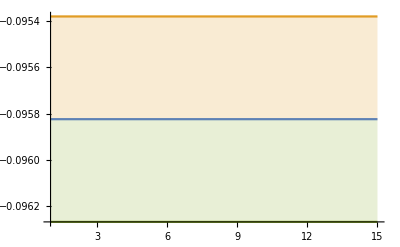

```mathematica
Plot[{fitData[[1]]//.Around[x_,y_]:>x,{fitData[[1]]//.Around[x_,y_]:>x+y,fitData[[1]]//.Around[x_,y_]:>x-y}},{x,1,15},Filling->{3->{1},2->{1}}]
```

```mathematica
SpoilHWFLOPlotN3=Show[Plot[{fitData[[1]]//.Around[x_,y_]:>x,{fitData[[1]]//.Around[x_,y_]:>x+y,fitData[[1]]//.Around[x_,y_]:>x-y}},{x,1,Length[meanErr2[[5]]]},Filling->{3->{1},2->{1}},PlotRange->{-1,1}],ListPlot[{Table[{τSteps[[1,i]],meanErr2[[1,i]]},{i,1,Length[meanErr2[[1]]]}],Table[{τSteps[[2,i]],meanErr2[[2,i]]},{i,1,Length[meanErr2[[2]]]}],Table[{τSteps[[3,i]],meanErr2[[3,i]]},{i,1,Length[meanErr2[[3]]]}],Table[{τSteps[[4,i]],meanErr2[[4,i]]},{i,1,Length[meanErr2[[4]]]}],Table[{τSteps[[5,i]],meanErr2[[5,i]]},{i,1,Length[meanErr2[[5]]]}]},PlotRange->{-.03,-0.005},PlotLegends->Placed[αLegendLO,{0.5,0.1}],PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]],markerlist[[4]],markerlist[[5]]},IntervalMarkersStyle->{ColorData[97][3]},PlotStyle->{ColorData[97][3]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau_{\\text{steps}}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]},PlotLabel->MaTeX["N=3(\\text{LO})",Magnification->1.2]]
```

-Graphics-

### baryons

#### QCD LO - HWF

```mathematica
Nf4α1LoopMid
Nf4α1LoopStepTab={430,430,430,430,430};
NWalkers=200;
Nf4α1LoopBig={0.21556,0.21556,0.21556,0.21556,0.21556};
aList={1,2,3,4,5};
```

{0.21556,0.220566,0.22639,0.233299,0.241701,0.252265,0.266178,0.285833}

```mathematica
csvData=Table[Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfhwf.csv"],{xx,1,Length[aList]}]
```

({mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.022235321554132596, -0.022239671562506867, -0.022165562565845853, -0.02213287711667591, -0.022107892144713457, -0.022098296929646516, -0.022060631229515276, -0.02206904086438001, -0.02214993703586355, -0.02211533643466543, -0.022172271026044202, -0.02208396719373647, -0.02212120298651442, -0.02217731518603383, -0.022128294546959137, -0.02214790831137147, -0.022162541159635528, -0.022143704645566125, -0.022129991421993567, -0.022134054536483382, -0.022109511125857326, -0.02212315294407663, -0.02212657186031311, -0.022146387607632868, -0.022113591835736017, -0.022066913974355132, -0.022096243458573066, -0.02209938586517994],[0.00034762799612138843, 0.0003706104722178893, 0.0003858836395362453, 0.0004081972365943952, 0.0004310755372560061, 0.00045668366126680574, 0.00048566537580251533, 0.0005204580874126829, 0.0005558855434447346, 0.0006073114670304343, 0.0006582127185604321, 0.000689563234582849, 0.0007224144309887896, 0.0007722209941511184, 0.0008356083528634343, 0.0008679967862824899, 0.0009183591504619428, 0.0009370055077210907, 0.0009768186500069447, 0.0010296450583977188, 0.001075150879156298, 0.0011651471749689504, 0.001240940713236083, 0.0012990655155831774, 0.001372832771209285, 0.001444731792371378, 0.0015105885152402092, 0.0016002446709579194],-0.0221355,0.000013934,1.48797}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.01681793631624839, -0.01711850288877605, -0.017440167432464265, -0.017465368657580086, -0.017264806782210398, -0.016933104620724403, -0.01708262279584945, -0.01692263214265171, -0.016964042332144463, -0.01695283613169312, -0.01706398934552965, -0.017150310602122913, -0.016783197584988238, -0.017068794603636476, -0.016837000274366187, -0.017320092821581007, -0.01712237674558334, -0.017138237410255344, -0.017144259036046185, -0.017308568121978857, -0.01701577450938243, -0.017853243475765175, -0.018383605451586217, -0.018245063737706544, -0.01794555579053101, -0.017839806090289432, -0.01764006772319758, -0.017680304816565004, -0.01821284595968785, -0.017928559256146958, -0.017570232937512902, -0.017960621350204656, -0.0181191630398118, -0.018125543374312793, -0.01862191183491932, -0.018072423817429007, -0.01840549124812517, -0.01819648059619749, -0.01807889273845092],[0.000552810961229278, 0.0006652635091236513, 0.0008116084911510935, 0.0008531627228107552, 0.0008545393181691758, 0.0007893809062560759, 0.0008747443024010909, 0.0008855240326796865, 0.0009068282915954879, 0.0009326564337478247, 0.0010328489123599674, 0.0011793583636799923, 0.0010839355224415011, 0.0013979279856140153, 0.00125018639789628, 0.0017149140235695939, 0.0014795721803148108, 0.0015800752007716203, 0.0015769468392569522, 0.0017166684919827457, 0.0017236346205489154, 0.0023284859898769668, 0.002724206183905332, 0.0029056788458309345, 0.002687101955875092, 0.002830859366037608, 0.00267631244462852, 0.0028430681275086384, 0.003259288287094324, 0.0030638401766375192, 0.003030615137657481, 0.0032397287845544777, 0.003487612900090272, 0.0036374701556370257, 0.004101839753222046, 0.0038304320252216793, 0.004125228018673701, 0.004132161539735751, 0.0043162989864970434],-0.0151623,0.000147636,0.610681}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.012444084676439936, -0.012561694700217112, -0.012805373413247539, -0.012791308300198891, -0.012754640373753394, -0.012522348745325151, -0.012540125707215698, -0.012423126623756478, -0.012631178651274399, -0.012673211532876906, -0.012688549283017313, -0.012553346697421534, -0.012472642287119083, -0.012642507611796885, -0.013277703623099405, -0.012620804279195928, -0.012734911574584805, -0.012790104156345117, -0.01277666445933614, -0.012759126057254079, -0.012941320681376713, -0.013061332411625371, -0.013037030351349033, -0.012962510110964687, -0.013038212996856893, -0.01305221858455405, -0.013269957355992167, -0.013139084294722504, -0.013073584898631755, -0.01301576934724977, -0.012834999555874806, -0.012915452353750703, -0.012849804569677402, -0.012908004440617415, -0.013055759987969137, -0.013088630064462098, -0.013249572146670944, -0.013275430415075829, -0.013559729530794725],[0.0004485783170384765, 0.0004920197131948514, 0.0006578386308366232, 0.0006020398564924857, 0.0007110863476659042, 0.0006290634702308112, 0.0006288636897937007, 0.0006003863727390926, 0.00065822417170036, 0.0007088160807582326, 0.0007682280343922278, 0.0007575438501092044, 0.000746833755409392, 0.0009107564341515788, 0.0015319100385264497, 0.0009118837177465546, 0.0009860661639441264, 0.0010154395637823792, 0.0010294674296957246, 0.0010472667036401033, 0.001166468275833069, 0.0012345932205731487, 0.001257394506572336, 0.0012410980322133918, 0.0012986344816759666, 0.001359542166289451, 0.0014945819844841867, 0.001518117357121345, 0.001580802526515967, 0.0015721130179475273, 0.0015758098274361095, 0.0016021781412128339, 0.0015905664842500928, 0.0016589666934989614, 0.0017893243084628366, 0.0018382320983246216, 0.001982770589374955, 0.0020380079493746606, 0.002574168175766083],-0.0113642,0.000167339,0.246361}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.010055795062417602, -0.010300715390473553, -0.010214877763321998, -0.010373410994108299, -0.01005919980068897, -0.010131268396137018, -0.01017479821815326, -0.010276098636377608, -0.010354219312623444, -0.010644171439386793, -0.010435975704737789, -0.010740553398092479, -0.010590931536487545, -0.010441953020967207, -0.01055766370438962, -0.010718613887320332, -0.010739548415338354, -0.011122378131544135, -0.01119400841277547, -0.011016684873148786, -0.011091304970583268, -0.011176572951227062, -0.01179254044267329, -0.011855538337769722, -0.011982917097013206, -0.011608072620390989, -0.01214720672937808, -0.01167180701566783, -0.011994069256876162, -0.011667058864178377, -0.011805768117841774, -0.011552302926182033, -0.011427749378578156, -0.011706969356460675, -0.012011013255431057, -0.0121204612914543, -0.01215437003356754, -0.012581814779837924, -0.012128057944114153],[0.0004644100719640656, 0.0005644730480484933, 0.0005731631459610151, 0.0006442896904149631, 0.0005373420591762839, 0.0005934814787715368, 0.0006391413198034355, 0.0006822289802174863, 0.0007073757507351092, 0.000904754389745636, 0.0008462238706853573, 0.0011082610984671207, 0.0010240479663899983, 0.0008017619613973887, 0.0008487796910424596, 0.0009230444283148687, 0.0009648561213814553, 0.0013010308810372248, 0.0012319637047121298, 0.0011946366249473432, 0.001288495816234223, 0.001336388799918524, 0.001756832883245181, 0.001870350133899107, 0.0021863251749106426, 0.0017745237530531548, 0.0023715126803260395, 0.0019116573271316909, 0.0022942665511651943, 0.0021642462494589035, 0.002439441270759096, 0.0022636463420304636, 0.0021902652548514085, 0.0025542614333663454, 0.002956506367513914, 0.003377583517092006, 0.0032233985943502957, 0.0036032796734117257, 0.003245696357776878],-0.00904713,0.000215339,0.12689}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.007847100406962293, -0.00791042896078117, -0.00797727945742814, -0.00808629147676411, -0.008192434052158474, -0.008325522198677646, -0.008315961636004891, -0.008460938569342684, -0.008585202551004754, -0.008770726157939267, -0.008875694499035702, -0.008531192965538743, -0.008452341354619293, -0.008408990096672609, -0.008484917090009028, -0.00835194706169026, -0.008378179330646699, -0.008566498541228738, -0.009280358067192185, -0.010433169982920038, -0.009424497062936297, -0.0096745020683218, -0.008788559804733495, -0.008943425599791263, -0.009064411287134873, -0.008990482857074295, -0.00918939396684701, -0.010021335106467324, -0.009957842849798686, -0.00939843305926177, -0.009334743420251857, -0.009462577643910156, -0.009314011629574556, -0.009722717287803967, -0.009548734915482283, -0.009449002593939116, -0.00969377644075534, -0.009888719351880855, -0.00987526795881445],[0.0003133352304145857, 0.00033493841814317965, 0.0003623425181950479, 0.0004131029892908898, 0.00047279605607149217, 0.0005402940774161213, 0.0006170872496935262, 0.0006408292975965624, 0.0006284475637440142, 0.0007510091743920017, 0.000978600220657267, 0.0007980898167373537, 0.0007752257258944375, 0.0007746186217369822, 0.0008046122422182984, 0.0007290681561820908, 0.000849320764250841, 0.0009562854822080477, 0.001924886131589874, 0.0035481246212704883, 0.002206050336575134, 0.0025887967281443343, 0.0013290810898377704, 0.0013355202180424471, 0.0013957364806009098, 0.0013679272287428878, 0.0016528743994625177, 0.0025003163542651674, 0.0023907117092157567, 0.0018211034769173178, 0.0018217667834410525, 0.0018659633242724917, 0.001752068872412352, 0.002011274282976544, 0.0019015141348607033, 0.0019968957968957177, 0.0023099680695382644, 0.0024924497932875983, 0.0026628609581094234],-0.00740007,0.000157446,0.133691})

```mathematica
meanErr=Table[Table[csvData[[xx,2,yy]]//StringSplit[#,{",","[","]"}]&,{yy,1,2}],{xx,1,Length[aList]}]
```

({-0.022235321554132596, -0.022239671562506867, -0.022165562565845853, -0.02213287711667591, -0.022107892144713457, -0.022098296929646516, -0.022060631229515276, -0.02206904086438001, -0.02214993703586355, -0.02211533643466543, -0.022172271026044202, -0.02208396719373647, -0.02212120298651442, -0.02217731518603383, -0.022128294546959137, -0.02214790831137147, -0.022162541159635528, -0.022143704645566125, -0.022129991421993567, -0.022134054536483382, -0.022109511125857326, -0.02212315294407663, -0.02212657186031311, -0.022146387607632868, -0.022113591835736017, -0.022066913974355132, -0.022096243458573066, -0.02209938586517994} | {0.00034762799612138843, 0.0003706104722178893, 0.0003858836395362453, 0.0004081972365943952, 0.0004310755372560061, 0.00045668366126680574, 0.00048566537580251533, 0.0005204580874126829, 0.0005558855434447346, 0.0006073114670304343, 0.0006582127185604321, 0.000689563234582849, 0.0007224144309887896, 0.0007722209941511184, 0.0008356083528634343, 0.0008679967862824899, 0.0009183591504619428, 0.0009370055077210907, 0.0009768186500069447, 0.0010296450583977188, 0.001075150879156298, 0.0011651471749689504, 0.001240940713236083, 0.0012990655155831774, 0.001372832771209285, 0.001444731792371378, 0.0015105885152402092, 0.0016002446709579194}
{-0.01681793631624839, -0.01711850288877605, -0.017440167432464265, -0.017465368657580086, -0.017264806782210398, -0.016933104620724403, -0.01708262279584945, -0.01692263214265171, -0.016964042332144463, -0.01695283613169312, -0.01706398934552965, -0.017150310602122913, -0.016783197584988238, -0.017068794603636476, -0.016837000274366187, -0.017320092821581007, -0.01712237674558334, -0.017138237410255344, -0.017144259036046185, -0.017308568121978857, -0.01701577450938243, -0.017853243475765175, -0.018383605451586217, -0.018245063737706544, -0.01794555579053101, -0.017839806090289432, -0.01764006772319758, -0.017680304816565004, -0.01821284595968785, -0.017928559256146958, -0.017570232937512902, -0.017960621350204656, -0.0181191630398118, -0.018125543374312793, -0.01862191183491932, -0.018072423817429007, -0.01840549124812517, -0.01819648059619749, -0.01807889273845092} | {0.000552810961229278, 0.0006652635091236513, 0.0008116084911510935, 0.0008531627228107552, 0.0008545393181691758, 0.0007893809062560759, 0.0008747443024010909, 0.0008855240326796865, 0.0009068282915954879, 0.0009326564337478247, 0.0010328489123599674, 0.0011793583636799923, 0.0010839355224415011, 0.0013979279856140153, 0.00125018639789628, 0.0017149140235695939, 0.0014795721803148108, 0.0015800752007716203, 0.0015769468392569522, 0.0017166684919827457, 0.0017236346205489154, 0.0023284859898769668, 0.002724206183905332, 0.0029056788458309345, 0.002687101955875092, 0.002830859366037608, 0.00267631244462852, 0.0028430681275086384, 0.003259288287094324, 0.0030638401766375192, 0.003030615137657481, 0.0032397287845544777, 0.003487612900090272, 0.0036374701556370257, 0.004101839753222046, 0.0038304320252216793, 0.004125228018673701, 0.004132161539735751, 0.0043162989864970434}
{-0.012444084676439936, -0.012561694700217112, -0.012805373413247539, -0.012791308300198891, -0.012754640373753394, -0.012522348745325151, -0.012540125707215698, -0.012423126623756478, -0.012631178651274399, -0.012673211532876906, -0.012688549283017313, -0.012553346697421534, -0.012472642287119083, -0.012642507611796885, -0.013277703623099405, -0.012620804279195928, -0.012734911574584805, -0.012790104156345117, -0.01277666445933614, -0.012759126057254079, -0.012941320681376713, -0.013061332411625371, -0.013037030351349033, -0.012962510110964687, -0.013038212996856893, -0.01305221858455405, -0.013269957355992167, -0.013139084294722504, -0.013073584898631755, -0.01301576934724977, -0.012834999555874806, -0.012915452353750703, -0.012849804569677402, -0.012908004440617415, -0.013055759987969137, -0.013088630064462098, -0.013249572146670944, -0.013275430415075829, -0.013559729530794725} | {0.0004485783170384765, 0.0004920197131948514, 0.0006578386308366232, 0.0006020398564924857, 0.0007110863476659042, 0.0006290634702308112, 0.0006288636897937007, 0.0006003863727390926, 0.00065822417170036, 0.0007088160807582326, 0.0007682280343922278, 0.0007575438501092044, 0.000746833755409392, 0.0009107564341515788, 0.0015319100385264497, 0.0009118837177465546, 0.0009860661639441264, 0.0010154395637823792, 0.0010294674296957246, 0.0010472667036401033, 0.001166468275833069, 0.0012345932205731487, 0.001257394506572336, 0.0012410980322133918, 0.0012986344816759666, 0.001359542166289451, 0.0014945819844841867, 0.001518117357121345, 0.001580802526515967, 0.0015721130179475273, 0.0015758098274361095, 0.0016021781412128339, 0.0015905664842500928, 0.0016589666934989614, 0.0017893243084628366, 0.0018382320983246216, 0.001982770589374955, 0.0020380079493746606, 0.002574168175766083}
{-0.010055795062417602, -0.010300715390473553, -0.010214877763321998, -0.010373410994108299, -0.01005919980068897, -0.010131268396137018, -0.01017479821815326, -0.010276098636377608, -0.010354219312623444, -0.010644171439386793, -0.010435975704737789, -0.010740553398092479, -0.010590931536487545, -0.010441953020967207, -0.01055766370438962, -0.010718613887320332, -0.010739548415338354, -0.011122378131544135, -0.01119400841277547, -0.011016684873148786, -0.011091304970583268, -0.011176572951227062, -0.01179254044267329, -0.011855538337769722, -0.011982917097013206, -0.011608072620390989, -0.01214720672937808, -0.01167180701566783, -0.011994069256876162, -0.011667058864178377, -0.011805768117841774, -0.011552302926182033, -0.011427749378578156, -0.011706969356460675, -0.012011013255431057, -0.0121204612914543, -0.01215437003356754, -0.012581814779837924, -0.012128057944114153} | {0.0004644100719640656, 0.0005644730480484933, 0.0005731631459610151, 0.0006442896904149631, 0.0005373420591762839, 0.0005934814787715368, 0.0006391413198034355, 0.0006822289802174863, 0.0007073757507351092, 0.000904754389745636, 0.0008462238706853573, 0.0011082610984671207, 0.0010240479663899983, 0.0008017619613973887, 0.0008487796910424596, 0.0009230444283148687, 0.0009648561213814553, 0.0013010308810372248, 0.0012319637047121298, 0.0011946366249473432, 0.001288495816234223, 0.001336388799918524, 0.001756832883245181, 0.001870350133899107, 0.0021863251749106426, 0.0017745237530531548, 0.0023715126803260395, 0.0019116573271316909, 0.0022942665511651943, 0.0021642462494589035, 0.002439441270759096, 0.0022636463420304636, 0.0021902652548514085, 0.0025542614333663454, 0.002956506367513914, 0.003377583517092006, 0.0032233985943502957, 0.0036032796734117257, 0.003245696357776878}
{-0.007847100406962293, -0.00791042896078117, -0.00797727945742814, -0.00808629147676411, -0.008192434052158474, -0.008325522198677646, -0.008315961636004891, -0.008460938569342684, -0.008585202551004754, -0.008770726157939267, -0.008875694499035702, -0.008531192965538743, -0.008452341354619293, -0.008408990096672609, -0.008484917090009028, -0.00835194706169026, -0.008378179330646699, -0.008566498541228738, -0.009280358067192185, -0.010433169982920038, -0.009424497062936297, -0.0096745020683218, -0.008788559804733495, -0.008943425599791263, -0.009064411287134873, -0.008990482857074295, -0.00918939396684701, -0.010021335106467324, -0.009957842849798686, -0.00939843305926177, -0.009334743420251857, -0.009462577643910156, -0.009314011629574556, -0.009722717287803967, -0.009548734915482283, -0.009449002593939116, -0.00969377644075534, -0.009888719351880855, -0.00987526795881445} | {0.0003133352304145857, 0.00033493841814317965, 0.0003623425181950479, 0.0004131029892908898, 0.00047279605607149217, 0.0005402940774161213, 0.0006170872496935262, 0.0006408292975965624, 0.0006284475637440142, 0.0007510091743920017, 0.000978600220657267, 0.0007980898167373537, 0.0007752257258944375, 0.0007746186217369822, 0.0008046122422182984, 0.0007290681561820908, 0.000849320764250841, 0.0009562854822080477, 0.001924886131589874, 0.0035481246212704883, 0.002206050336575134, 0.0025887967281443343, 0.0013290810898377704, 0.0013355202180424471, 0.0013957364806009098, 0.0013679272287428878, 0.0016528743994625177, 0.0025003163542651674, 0.0023907117092157567, 0.0018211034769173178, 0.0018217667834410525, 0.0018659633242724917, 0.001752068872412352, 0.002011274282976544, 0.0019015141348607033, 0.0019968957968957177, 0.0023099680695382644, 0.0024924497932875983, 0.0026628609581094234})

```mathematica
meanErr[[1,2,1]]//ToExpression
```

0.000347628

```mathematica
meanErr[[1]]
```

(-0.022235321554132596 |  -0.022239671562506867 |  -0.022165562565845853 |  -0.02213287711667591 |  -0.022107892144713457 |  -0.022098296929646516 |  -0.022060631229515276 |  -0.02206904086438001 |  -0.02214993703586355 |  -0.02211533643466543 |  -0.022172271026044202 |  -0.02208396719373647 |  -0.02212120298651442 |  -0.02217731518603383 |  -0.022128294546959137 |  -0.02214790831137147 |  -0.022162541159635528 |  -0.022143704645566125 |  -0.022129991421993567 |  -0.022134054536483382 |  -0.022109511125857326 |  -0.02212315294407663 |  -0.02212657186031311 |  -0.022146387607632868 |  -0.022113591835736017 |  -0.022066913974355132 |  -0.022096243458573066 |  -0.02209938586517994
0.00034762799612138843 |  0.0003706104722178893 |  0.0003858836395362453 |  0.0004081972365943952 |  0.0004310755372560061 |  0.00045668366126680574 |  0.00048566537580251533 |  0.0005204580874126829 |  0.0005558855434447346 |  0.0006073114670304343 |  0.0006582127185604321 |  0.000689563234582849 |  0.0007224144309887896 |  0.0007722209941511184 |  0.0008356083528634343 |  0.0008679967862824899 |  0.0009183591504619428 |  0.0009370055077210907 |  0.0009768186500069447 |  0.0010296450583977188 |  0.001075150879156298 |  0.0011651471749689504 |  0.001240940713236083 |  0.0012990655155831774 |  0.001372832771209285 |  0.001444731792371378 |  0.0015105885152402092 |  0.0016002446709579194)

```mathematica
meanErr2=Table[Table[Around[meanErr[[xx,1,yy]]//ToExpression,meanErr[[xx,2,yy]]//ToExpression],{yy,1,Length[meanErr[[xx,1]]]}],{xx,1,Length[aList]}]
```

{{-0.022240.00035,-0.02220.0004,-0.02220.0004,-0.02210.0004,-0.02210.0004,-0.02210.0005,-0.02210.0005,-0.02210.0005,-0.02210.0006,-0.02210.0006,-0.02220.0007,-0.02210.0007,-0.02210.0007,-0.02220.0008,-0.02210.0008,-0.02210.0009,-0.02220.0009,-0.02210.0009,-0.02210.0010,-0.02210.0010,-0.02210.0011,-0.02210.0012,-0.02210.0012,-0.02210.0013,-0.02210.0014,-0.02210.0014,-0.02210.0015,-0.02210.0016},{-0.01680.0006,-0.01710.0007,-0.01740.0008,-0.01750.0009,-0.01730.0009,-0.01690.0008,-0.01710.0009,-0.01690.0009,-0.01700.0009,-0.01700.0009,-0.01710.0010,-0.01720.0012,-0.01680.0011,-0.01710.0014,-0.01680.0013,-0.01730.0017,-0.01710.0015,-0.01710.0016,-0.01710.0016,-0.01730.0017,-0.01700.0017,-0.01790.0023,-0.01840.0027,-0.01820.0029,-0.01790.0027,-0.01780.0028,-0.01760.0027,-0.01770.0028,-0.01820.0033,-0.01790.0031,-0.01760.0030,-0.01800.0032,-0.01810.0035,-0.0180.004,-0.0190.004,-0.0180.004,-0.0180.004,-0.0180.004,-0.0180.004},{-0.01240.0004,-0.01260.0005,-0.01280.0007,-0.01280.0006,-0.01280.0007,-0.01250.0006,-0.01250.0006,-0.01240.0006,-0.01260.0007,-0.01270.0007,-0.01270.0008,-0.01260.0008,-0.01250.0007,-0.01260.0009,-0.01330.0015,-0.01260.0009,-0.01270.0010,-0.01280.0010,-0.01280.0010,-0.01280.0010,-0.01290.0012,-0.01310.0012,-0.01300.0013,-0.01300.0012,-0.01300.0013,-0.01310.0014,-0.01330.0015,-0.01310.0015,-0.01310.0016,-0.01300.0016,-0.01280.0016,-0.01290.0016,-0.01280.0016,-0.01290.0017,-0.01310.0018,-0.01310.0018,-0.01320.0020,-0.01330.0020,-0.01360.0026},{-0.01010.0005,-0.01030.0006,-0.01020.0006,-0.01040.0006,-0.01010.0005,-0.01010.0006,-0.01020.0006,-0.01030.0007,-0.01040.0007,-0.01060.0009,-0.01040.0008,-0.01070.0011,-0.01060.0010,-0.01040.0008,-0.01060.0008,-0.01070.0009,-0.01070.0010,-0.01110.0013,-0.01120.0012,-0.01100.0012,-0.01110.0013,-0.01120.0013,-0.01180.0018,-0.01190.0019,-0.01200.0022,-0.01160.0018,-0.01210.0024,-0.01170.0019,-0.01200.0023,-0.01170.0022,-0.01180.0024,-0.01160.0023,-0.01140.0022,-0.01170.0026,-0.01200.0030,-0.01210.0034,-0.01220.0032,-0.0130.004,-0.01210.0032},{-0.007850.00031,-0.007910.00033,-0.00800.0004,-0.00810.0004,-0.00820.0005,-0.00830.0005,-0.00830.0006,-0.00850.0006,-0.00860.0006,-0.00880.0008,-0.00890.0010,-0.00850.0008,-0.00850.0008,-0.00840.0008,-0.00850.0008,-0.00840.0007,-0.00840.0008,-0.00860.0010,-0.00930.0019,-0.01040.0035,-0.00940.0022,-0.00970.0026,-0.00880.0013,-0.00890.0013,-0.00910.0014,-0.00900.0014,-0.00920.0017,-0.01000.0025,-0.01000.0024,-0.00940.0018,-0.00930.0018,-0.00950.0019,-0.00930.0018,-0.00970.0020,-0.00950.0019,-0.00940.0020,-0.00970.0023,-0.00990.0025,-0.00990.0027}}

```mathematica
τSteps=Table[Table[xx,{xx,1,Length[meanErr2[[yy]]]}],{yy,1,Length[meanErr2]}]
```

{{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39}}

```mathematica
fitData=Table[Around[Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfhwf.csv"][[2,3]],Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfhwf.csv"][[2,4]]],{xx,1,Length[aList]}]
```

{-0.0221360.000014,-0.015160.00015,-0.011360.00017,-0.009050.00022,-0.007400.00016}

```mathematica
αLegendLO=PointLegend[Table[Directive[ColorData[97][1]],{ii,5}],{MaTeX["a=1",Magnification->0.8],MaTeX["a=2",Magnification->0.8],MaTeX["a=3",Magnification->0.8],MaTeX["a=4",Magnification->0.8],MaTeX["a=5",Magnification->0.8]},LegendMarkers->Table[Style[markerlist[[ii]],14,Bold,ColorData[97][3]],{ii,5}],LegendLayout->"Row",LegendMargins->0.5,LegendFunction->frame]
```

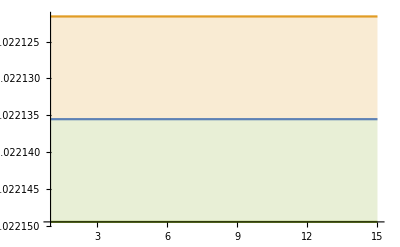

```mathematica
Plot[{fitData[[1]]//.Around[x_,y_]:>x,{fitData[[1]]//.Around[x_,y_]:>x+y,fitData[[1]]//.Around[x_,y_]:>x-y}},{x,1,15},Filling->{3->{1},2->{1}}]
```

```mathematica
SpoilHWFLOPlotN3=Show[Plot[{fitData[[1]]//.Around[x_,y_]:>x,{fitData[[1]]//.Around[x_,y_]:>x+y,fitData[[1]]//.Around[x_,y_]:>x-y}},{x,1,Length[meanErr2[[5]]]},Filling->{3->{1},2->{1}},PlotRange->{-.03,-0.005}],ListPlot[{Table[{τSteps[[1,i]],meanErr2[[1,i]]},{i,1,Length[meanErr2[[1]]]}],Table[{τSteps[[2,i]],meanErr2[[2,i]]},{i,1,Length[meanErr2[[2]]]}],Table[{τSteps[[3,i]],meanErr2[[3,i]]},{i,1,Length[meanErr2[[3]]]}],Table[{τSteps[[4,i]],meanErr2[[4,i]]},{i,1,Length[meanErr2[[4]]]}],Table[{τSteps[[5,i]],meanErr2[[5,i]]},{i,1,Length[meanErr2[[5]]]}]},PlotRange->{-.03,-0.005},PlotLegends->Placed[αLegendLO,{0.5,0.1}],PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]],markerlist[[4]],markerlist[[5]]},IntervalMarkersStyle->{ColorData[97][3]},PlotStyle->{ColorData[97][3]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau_{\\text{steps}}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]},PlotLabel->MaTeX["N=3\\text{ (LO)}",Magnification->1.2]]
```

-Graphics-

#### QCD NLO - HWF

```mathematica
Nf4α1LoopMid
Nf4α1LoopStepTab={380,380,380,380,380};
NWalkers=200;
Nf4α1LoopBig={0.229421,0.229421,0.229421,0.229421,0.229421};
aList={1,2,3,4,5};
```

{0.21556,0.220566,0.22639,0.233299,0.241701,0.252265,0.266178,0.285833}

```mathematica
csvData=Table[Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfhwf.csv"],{xx,1,Length[aList]}]
```

({mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.06923552965743057, -0.06938449226294607, -0.06975341645129175, -0.070582079589056, -0.07011295998038503, -0.06992929565879952, -0.0699169404794734, -0.06958013554743606, -0.06951995968319621, -0.0696206039856162, -0.07017721560898979, -0.0705939377110735, -0.07048458953611854, -0.07029494690042887, -0.07056839129109066, -0.07142694627239121, -0.0714149514249993, -0.07099957507214681, -0.0707860162531062, -0.07116908495931729, -0.07092939706570417, -0.07175710960695313, -0.07374404948321417, -0.07314735244128474, -0.07357493562607435, -0.07367194938755171, -0.07300217130925735, -0.07397770423898505, -0.07409135488750174, -0.07373865065326461, -0.07466710043857358, -0.07463955532655146, -0.07577471197126143, -0.07469271820815052, -0.07443728311903987],[0.0025118243897858735, 0.0032499879886091223, 0.004165520811256229, 0.005633040658117597, 0.006523918262140421, 0.008287017375573996, 0.00976953889764734, 0.011774914576487685, 0.013623851566929576, 0.0164537521272614, 0.019636037947625605, 0.02336035449632663, 0.02731300919229654, 0.03239065545136948, 0.038041292116729804, 0.04698847862616232, 0.055375353024564866, 0.060979031191320886, 0.07129182876458742, 0.08459690388029052, 0.09669690036758222, 0.11825324612140703, 0.14733810075853201, 0.16652997238339173, 0.20398143135816504, 0.2529724422977322, 0.2979704653150349, 0.36314374793264875, 0.42207395299686673, 0.5024743248372324, 0.6268357265756949, 0.7558581442960726, 0.9452688158828437, 1.0619682613196915, 1.2679896848115237],-0.0687972,0.000357902,0.681165}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.049821686798759666, -0.051131273670001656, -0.05263406340821623, -0.05255482975835949, -0.054711826395556, -0.052731168907435184, -0.052329204012619875, -0.05294008804259658, -0.054309576717700675, -0.05320956775593389, -0.05397458697015167, -0.05336801979999388, -0.051948227214382144, -0.05278163716292705, -0.05374652985846077, -0.05406450373769697, -0.05249989654588897, -0.05269113755384904, -0.05405260004143628, -0.05435229676528904, -0.054089404979821135, -0.054259622107804883, -0.05629994721168275, -0.056759843786553285, -0.056337096022960303, -0.05628591755448439, -0.05602458512473977, -0.05842626427863789, -0.058260881029839465, -0.05883172756334281, -0.05773336489767522, -0.05733403877584522, -0.05794104868479354, -0.05930140825583574, -0.058513783857626844],[0.00390077415583473, 0.005915670998374945, 0.009142579701710462, 0.010792459139166427, 0.01801622484800811, 0.015440718912320855, 0.01685803289025763, 0.02034743984617097, 0.02455979760062808, 0.025860473085336226, 0.03106910584669431, 0.034597223244396194, 0.03376350347817308, 0.03748177496105673, 0.04497756348498079, 0.04916748914311104, 0.052438979196591406, 0.05906241588517179, 0.07237781015607833, 0.08018907032861204, 0.08578409218329273, 0.09658191069566471, 0.11506565280805235, 0.12934823021622524, 0.14499187064576693, 0.16531601189621484, 0.18311187631766299, 0.21864536646581542, 0.25068874251676376, 0.28463283178007553, 0.3045203214607176, 0.3415562419152895, 0.38915576282849235, 0.4612748280535039, 0.5330633940986407],-0.0513288,0.000690106,0.229324}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.03735391179632651, -0.03710592914044584, -0.036817146405551344, -0.036931071064894856, -0.037031174971538086, -0.037671346013328263, -0.03806193022794656, -0.03850553942029707, -0.03911962434269852, -0.04060242037087793, -0.040524161062882626, -0.0404578183212705, -0.03990657158480655, -0.04050325692233467, -0.04202119562172766, -0.04273879636193625, -0.04142422648313967, -0.04131913413317111, -0.04264113983941402, -0.042293383126951904, -0.04286536703357203, -0.0438149060718027, -0.04672958874232509, -0.045251109656088376, -0.048540307690641146, -0.04737507103063254, -0.0490179580099066, -0.04994354063093894, -0.05136292659491521, -0.05036386476359308, -0.05608830617376518, -0.056787329308636864, -0.05815911062572471, -0.058874724311522714, -0.06080541920404834],[0.002707372787363342, 0.002681119655361364, 0.0029786431208674003, 0.003363296922334933, 0.00384429407137672, 0.004643707784624438, 0.005487890995164441, 0.00669268857112422, 0.007504496388583461, 0.009479018877046408, 0.00984625140526003, 0.010979790939974766, 0.011712903035319919, 0.013199455775652605, 0.01586553828314194, 0.017957698242144778, 0.01875859298972102, 0.020901294465768848, 0.024670021678006273, 0.026515054142951446, 0.03004010775037337, 0.03590752055834889, 0.04707837471227523, 0.04962306301202852, 0.07109398121748434, 0.07461058156732189, 0.09731567962813202, 0.11741535267801774, 0.14868946811808847, 0.1590866539228216, 0.23574287311495265, 0.2938898788996407, 0.3595694573646713, 0.4341974999604891, 0.5403690198382495],-0.0353557,0.000752304,0.195103}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.02780765140545089, -0.027790288541185454, -0.02808105971337129, -0.02841766311852983, -0.028682537171288144, -0.028961900206292007, -0.030708632359093616, -0.03137974663008762, -0.03129890356774934, -0.03199464610043126, -0.033638794454152444, -0.032621925647650554, -0.034641598022783444, -0.03366198456998226, -0.03464923445715573, -0.034344995880464475, -0.03578899013586881, -0.03618129638116773, -0.03562309356093935, -0.035769782435122154, -0.033888142538729925, -0.03412279135973557, -0.03477285059033114, -0.03430520581060491, -0.03454233189709738, -0.03394516540040759, -0.03388293087283451, -0.03430738744537885, -0.034756609769580706, -0.033755118647264236, -0.03442793488806014, -0.03542000064132639, -0.03506058103413765, -0.034341271451596614, -0.034566336306530346],[0.0014149700324589665, 0.001436296991309227, 0.0016208010183492883, 0.001947613094024982, 0.002305527400184729, 0.0026235858850785134, 0.004578648450009496, 0.005958167295861507, 0.005168652278602826, 0.006246759058327475, 0.0090914341409912, 0.00795565157882554, 0.012659533237300053, 0.011650859972458237, 0.014561833676166577, 0.01449970443455662, 0.01907923310369192, 0.021996259258228804, 0.02321296658445523, 0.02584063424641679, 0.02321352391578602, 0.024727109399208875, 0.028163261801643705, 0.02810909575197189, 0.032258028252568294, 0.0343358975439281, 0.037360859644702385, 0.041793475766557384, 0.045654628340252024, 0.047350258615719905, 0.057444644495947744, 0.0675237093239171, 0.06783385762083803, 0.06811263470167365, 0.07506434455935718],-0.0280394,0.000483802,0.278341}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.02341838180320839, -0.02329334649230556, -0.023498549014940962, -0.023892951198248896, -0.02391225819569241, -0.02430772690138293, -0.024427840303813356, -0.024858701514100863, -0.025534035263579363, -0.02592168814404844, -0.026020877207027084, -0.02577093988310626, -0.02560920522958052, -0.025847059971438578, -0.025818724673252653, -0.025958048434185678, -0.02627115658910772, -0.0265499092209916, -0.026624335312147605, -0.02656296325119065, -0.026510663532082354, -0.02672391703815404, -0.027322330974522736, -0.027504028441995385, -0.02742709285235617, -0.027613090206088337, -0.027797532178241414, -0.028901765779414685, -0.02925341396759092, -0.030235595827361864, -0.030740102712866965, -0.031179137016382696, -0.03313403139972522, -0.035337865232641825, -0.03513782137873553],[0.001216554154025223, 0.001236551514677797, 0.0013853532297220912, 0.0016137350984674192, 0.001755840929809271, 0.0020957868092716892, 0.0022770420372843596, 0.0027159266518735643, 0.003306899198797914, 0.0039660882803831165, 0.00409309211604066, 0.004217214221384512, 0.004261351184114204, 0.00475054697831904, 0.005014675770225833, 0.005441115450095919, 0.006231192952630837, 0.006937015834216546, 0.007360370716097812, 0.00775810243531437, 0.008181080565810466, 0.008908340885992837, 0.010137952984412687, 0.011408463215004083, 0.01204742804689286, 0.013396267630916746, 0.015169686752105107, 0.018674970840217332, 0.020661115335184638, 0.02471305899511769, 0.02788119234248382, 0.03095098675177648, 0.03918476204210253, 0.05201592054379385, 0.0550020444605451],-0.0215206,0.000543381,0.215296})

```mathematica
meanErr=Table[Table[csvData[[xx,2,yy]]//StringSplit[#,{",","[","]"}]&,{yy,1,2}],{xx,1,Length[aList]}]
```

({-0.06923552965743057, -0.06938449226294607, -0.06975341645129175, -0.070582079589056, -0.07011295998038503, -0.06992929565879952, -0.0699169404794734, -0.06958013554743606, -0.06951995968319621, -0.0696206039856162, -0.07017721560898979, -0.0705939377110735, -0.07048458953611854, -0.07029494690042887, -0.07056839129109066, -0.07142694627239121, -0.0714149514249993, -0.07099957507214681, -0.0707860162531062, -0.07116908495931729, -0.07092939706570417, -0.07175710960695313, -0.07374404948321417, -0.07314735244128474, -0.07357493562607435, -0.07367194938755171, -0.07300217130925735, -0.07397770423898505, -0.07409135488750174, -0.07373865065326461, -0.07466710043857358, -0.07463955532655146, -0.07577471197126143, -0.07469271820815052, -0.07443728311903987} | {0.0025118243897858735, 0.0032499879886091223, 0.004165520811256229, 0.005633040658117597, 0.006523918262140421, 0.008287017375573996, 0.00976953889764734, 0.011774914576487685, 0.013623851566929576, 0.0164537521272614, 0.019636037947625605, 0.02336035449632663, 0.02731300919229654, 0.03239065545136948, 0.038041292116729804, 0.04698847862616232, 0.055375353024564866, 0.060979031191320886, 0.07129182876458742, 0.08459690388029052, 0.09669690036758222, 0.11825324612140703, 0.14733810075853201, 0.16652997238339173, 0.20398143135816504, 0.2529724422977322, 0.2979704653150349, 0.36314374793264875, 0.42207395299686673, 0.5024743248372324, 0.6268357265756949, 0.7558581442960726, 0.9452688158828437, 1.0619682613196915, 1.2679896848115237}
{-0.049821686798759666, -0.051131273670001656, -0.05263406340821623, -0.05255482975835949, -0.054711826395556, -0.052731168907435184, -0.052329204012619875, -0.05294008804259658, -0.054309576717700675, -0.05320956775593389, -0.05397458697015167, -0.05336801979999388, -0.051948227214382144, -0.05278163716292705, -0.05374652985846077, -0.05406450373769697, -0.05249989654588897, -0.05269113755384904, -0.05405260004143628, -0.05435229676528904, -0.054089404979821135, -0.054259622107804883, -0.05629994721168275, -0.056759843786553285, -0.056337096022960303, -0.05628591755448439, -0.05602458512473977, -0.05842626427863789, -0.058260881029839465, -0.05883172756334281, -0.05773336489767522, -0.05733403877584522, -0.05794104868479354, -0.05930140825583574, -0.058513783857626844} | {0.00390077415583473, 0.005915670998374945, 0.009142579701710462, 0.010792459139166427, 0.01801622484800811, 0.015440718912320855, 0.01685803289025763, 0.02034743984617097, 0.02455979760062808, 0.025860473085336226, 0.03106910584669431, 0.034597223244396194, 0.03376350347817308, 0.03748177496105673, 0.04497756348498079, 0.04916748914311104, 0.052438979196591406, 0.05906241588517179, 0.07237781015607833, 0.08018907032861204, 0.08578409218329273, 0.09658191069566471, 0.11506565280805235, 0.12934823021622524, 0.14499187064576693, 0.16531601189621484, 0.18311187631766299, 0.21864536646581542, 0.25068874251676376, 0.28463283178007553, 0.3045203214607176, 0.3415562419152895, 0.38915576282849235, 0.4612748280535039, 0.5330633940986407}
{-0.03735391179632651, -0.03710592914044584, -0.036817146405551344, -0.036931071064894856, -0.037031174971538086, -0.037671346013328263, -0.03806193022794656, -0.03850553942029707, -0.03911962434269852, -0.04060242037087793, -0.040524161062882626, -0.0404578183212705, -0.03990657158480655, -0.04050325692233467, -0.04202119562172766, -0.04273879636193625, -0.04142422648313967, -0.04131913413317111, -0.04264113983941402, -0.042293383126951904, -0.04286536703357203, -0.0438149060718027, -0.04672958874232509, -0.045251109656088376, -0.048540307690641146, -0.04737507103063254, -0.0490179580099066, -0.04994354063093894, -0.05136292659491521, -0.05036386476359308, -0.05608830617376518, -0.056787329308636864, -0.05815911062572471, -0.058874724311522714, -0.06080541920404834} | {0.002707372787363342, 0.002681119655361364, 0.0029786431208674003, 0.003363296922334933, 0.00384429407137672, 0.004643707784624438, 0.005487890995164441, 0.00669268857112422, 0.007504496388583461, 0.009479018877046408, 0.00984625140526003, 0.010979790939974766, 0.011712903035319919, 0.013199455775652605, 0.01586553828314194, 0.017957698242144778, 0.01875859298972102, 0.020901294465768848, 0.024670021678006273, 0.026515054142951446, 0.03004010775037337, 0.03590752055834889, 0.04707837471227523, 0.04962306301202852, 0.07109398121748434, 0.07461058156732189, 0.09731567962813202, 0.11741535267801774, 0.14868946811808847, 0.1590866539228216, 0.23574287311495265, 0.2938898788996407, 0.3595694573646713, 0.4341974999604891, 0.5403690198382495}
{-0.02780765140545089, -0.027790288541185454, -0.02808105971337129, -0.02841766311852983, -0.028682537171288144, -0.028961900206292007, -0.030708632359093616, -0.03137974663008762, -0.03129890356774934, -0.03199464610043126, -0.033638794454152444, -0.032621925647650554, -0.034641598022783444, -0.03366198456998226, -0.03464923445715573, -0.034344995880464475, -0.03578899013586881, -0.03618129638116773, -0.03562309356093935, -0.035769782435122154, -0.033888142538729925, -0.03412279135973557, -0.03477285059033114, -0.03430520581060491, -0.03454233189709738, -0.03394516540040759, -0.03388293087283451, -0.03430738744537885, -0.034756609769580706, -0.033755118647264236, -0.03442793488806014, -0.03542000064132639, -0.03506058103413765, -0.034341271451596614, -0.034566336306530346} | {0.0014149700324589665, 0.001436296991309227, 0.0016208010183492883, 0.001947613094024982, 0.002305527400184729, 0.0026235858850785134, 0.004578648450009496, 0.005958167295861507, 0.005168652278602826, 0.006246759058327475, 0.0090914341409912, 0.00795565157882554, 0.012659533237300053, 0.011650859972458237, 0.014561833676166577, 0.01449970443455662, 0.01907923310369192, 0.021996259258228804, 0.02321296658445523, 0.02584063424641679, 0.02321352391578602, 0.024727109399208875, 0.028163261801643705, 0.02810909575197189, 0.032258028252568294, 0.0343358975439281, 0.037360859644702385, 0.041793475766557384, 0.045654628340252024, 0.047350258615719905, 0.057444644495947744, 0.0675237093239171, 0.06783385762083803, 0.06811263470167365, 0.07506434455935718}
{-0.02341838180320839, -0.02329334649230556, -0.023498549014940962, -0.023892951198248896, -0.02391225819569241, -0.02430772690138293, -0.024427840303813356, -0.024858701514100863, -0.025534035263579363, -0.02592168814404844, -0.026020877207027084, -0.02577093988310626, -0.02560920522958052, -0.025847059971438578, -0.025818724673252653, -0.025958048434185678, -0.02627115658910772, -0.0265499092209916, -0.026624335312147605, -0.02656296325119065, -0.026510663532082354, -0.02672391703815404, -0.027322330974522736, -0.027504028441995385, -0.02742709285235617, -0.027613090206088337, -0.027797532178241414, -0.028901765779414685, -0.02925341396759092, -0.030235595827361864, -0.030740102712866965, -0.031179137016382696, -0.03313403139972522, -0.035337865232641825, -0.03513782137873553} | {0.001216554154025223, 0.001236551514677797, 0.0013853532297220912, 0.0016137350984674192, 0.001755840929809271, 0.0020957868092716892, 0.0022770420372843596, 0.0027159266518735643, 0.003306899198797914, 0.0039660882803831165, 0.00409309211604066, 0.004217214221384512, 0.004261351184114204, 0.00475054697831904, 0.005014675770225833, 0.005441115450095919, 0.006231192952630837, 0.006937015834216546, 0.007360370716097812, 0.00775810243531437, 0.008181080565810466, 0.008908340885992837, 0.010137952984412687, 0.011408463215004083, 0.01204742804689286, 0.013396267630916746, 0.015169686752105107, 0.018674970840217332, 0.020661115335184638, 0.02471305899511769, 0.02788119234248382, 0.03095098675177648, 0.03918476204210253, 0.05201592054379385, 0.0550020444605451})

```mathematica
meanErr[[1,2,1]]//ToExpression
```

0.00251182

```mathematica
meanErr[[1]]
```

(-0.06923552965743057 |  -0.06938449226294607 |  -0.06975341645129175 |  -0.070582079589056 |  -0.07011295998038503 |  -0.06992929565879952 |  -0.0699169404794734 |  -0.06958013554743606 |  -0.06951995968319621 |  -0.0696206039856162 |  -0.07017721560898979 |  -0.0705939377110735 |  -0.07048458953611854 |  -0.07029494690042887 |  -0.07056839129109066 |  -0.07142694627239121 |  -0.0714149514249993 |  -0.07099957507214681 |  -0.0707860162531062 |  -0.07116908495931729 |  -0.07092939706570417 |  -0.07175710960695313 |  -0.07374404948321417 |  -0.07314735244128474 |  -0.07357493562607435 |  -0.07367194938755171 |  -0.07300217130925735 |  -0.07397770423898505 |  -0.07409135488750174 |  -0.07373865065326461 |  -0.07466710043857358 |  -0.07463955532655146 |  -0.07577471197126143 |  -0.07469271820815052 |  -0.07443728311903987
0.0025118243897858735 |  0.0032499879886091223 |  0.004165520811256229 |  0.005633040658117597 |  0.006523918262140421 |  0.008287017375573996 |  0.00976953889764734 |  0.011774914576487685 |  0.013623851566929576 |  0.0164537521272614 |  0.019636037947625605 |  0.02336035449632663 |  0.02731300919229654 |  0.03239065545136948 |  0.038041292116729804 |  0.04698847862616232 |  0.055375353024564866 |  0.060979031191320886 |  0.07129182876458742 |  0.08459690388029052 |  0.09669690036758222 |  0.11825324612140703 |  0.14733810075853201 |  0.16652997238339173 |  0.20398143135816504 |  0.2529724422977322 |  0.2979704653150349 |  0.36314374793264875 |  0.42207395299686673 |  0.5024743248372324 |  0.6268357265756949 |  0.7558581442960726 |  0.9452688158828437 |  1.0619682613196915 |  1.2679896848115237)

```mathematica
meanErr2=Table[Table[Around[meanErr[[xx,1,yy]]//ToExpression,meanErr[[xx,2,yy]]//ToExpression],{yy,1,Length[meanErr[[xx,1]]]}],{xx,1,Length[aList]}]
```

(-0.06920.0025 | -0.06940.0032 | -0.0700.004 | -0.0710.006 | -0.0700.007 | -0.0700.008 | -0.0700.010 | -0.0700.012 | -0.0700.014 | -0.0700.016 | -0.0700.020 | -0.0710.023 | -0.0700.027 | -0.0700.032 | -0.070.04 | -0.070.05 | -0.070.06 | -0.070.06 | -0.070.07 | -0.070.08 | -0.070.10 | -0.070.12 | -0.070.15 | -0.070.17 | -0.070.20 | -0.070.25 | -0.070.30 | 0.00.4 | 0.00.4 | 0.00.5 | 0.00.6 | 0.00.8 | 0.00.9 | 0.01.1 | 0.01.3
-0.0500.004 | -0.0510.006 | -0.0530.009 | -0.0530.011 | -0.0550.018 | -0.0530.015 | -0.0520.017 | -0.0530.020 | -0.0540.025 | -0.0530.026 | -0.0540.031 | -0.0530.035 | -0.0520.034 | -0.050.04 | -0.050.04 | -0.050.05 | -0.050.05 | -0.050.06 | -0.050.07 | -0.050.08 | -0.050.09 | -0.050.10 | -0.060.12 | -0.060.13 | -0.060.14 | -0.060.17 | -0.060.18 | -0.060.22 | -0.060.25 | -0.060.28 | -0.060.30 | -0.060.34 | 0.00.4 | 0.00.5 | 0.00.5
-0.03740.0027 | -0.03710.0027 | -0.03680.0030 | -0.03690.0034 | -0.0370.004 | -0.0380.005 | -0.0380.005 | -0.0390.007 | -0.0390.008 | -0.0410.009 | -0.0410.010 | -0.0400.011 | -0.0400.012 | -0.0410.013 | -0.0420.016 | -0.0430.018 | -0.0410.019 | -0.0410.021 | -0.0430.025 | -0.0420.027 | -0.0430.030 | -0.040.04 | -0.050.05 | -0.050.05 | -0.050.07 | -0.050.07 | -0.050.10 | -0.050.12 | -0.050.15 | -0.050.16 | -0.060.24 | -0.060.29 | 0.00.4 | 0.00.4 | 0.00.5
-0.02780.0014 | -0.02780.0014 | -0.02810.0016 | -0.02840.0019 | -0.02870.0023 | -0.02900.0026 | -0.0310.005 | -0.0310.006 | -0.0310.005 | -0.0320.006 | -0.0340.009 | -0.0330.008 | -0.0350.013 | -0.0340.012 | -0.0350.015 | -0.0340.014 | -0.0360.019 | -0.0360.022 | -0.0360.023 | -0.0360.026 | -0.0340.023 | -0.0340.025 | -0.0350.028 | -0.0340.028 | -0.0350.032 | -0.0340.034 | -0.030.04 | -0.030.04 | -0.030.05 | -0.030.05 | -0.030.06 | -0.040.07 | -0.040.07 | -0.030.07 | -0.030.08
-0.02340.0012 | -0.02330.0012 | -0.02350.0014 | -0.02390.0016 | -0.02390.0018 | -0.02430.0021 | -0.02440.0023 | -0.02490.0027 | -0.02550.0033 | -0.0260.004 | -0.0260.004 | -0.0260.004 | -0.0260.004 | -0.0260.005 | -0.0260.005 | -0.0260.005 | -0.0260.006 | -0.0270.007 | -0.0270.007 | -0.0270.008 | -0.0270.008 | -0.0270.009 | -0.0270.010 | -0.0280.011 | -0.0270.012 | -0.0280.013 | -0.0280.015 | -0.0290.019 | -0.0290.021 | -0.0300.025 | -0.0310.028 | -0.0310.031 | -0.030.04 | -0.040.05 | -0.040.06)

```mathematica
τSteps=Table[Table[xx,{xx,1,Length[meanErr2[[yy]]]}],{yy,1,Length[meanErr2]}]
```

(1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35)

```mathematica
fitData=Table[Around[Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfhwf.csv"][[2,3]],Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfhwf.csv"][[2,4]]],{xx,1,Length[aList]}]
```

{-0.06880.0004,-0.05130.0007,-0.03540.0008,-0.02800.0005,-0.02150.0005}

```mathematica
αLegendLO=PointLegend[Table[Directive[ColorData[97][1]],{ii,5}],{MaTeX["a=1",Magnification->0.8],MaTeX["a=2",Magnification->0.8],MaTeX["a=3",Magnification->0.8],MaTeX["a=4",Magnification->0.8],MaTeX["a=5",Magnification->0.8]},LegendMarkers->Table[Style[markerlist[[ii]],14,Bold,ColorData[97][3]],{ii,5}],LegendLayout->"Row",LegendMargins->0.5,LegendFunction->frame]
```

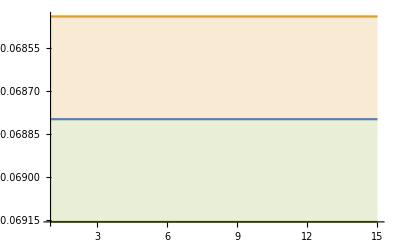

```mathematica
Plot[{fitData[[1]]//.Around[x_,y_]:>x,{fitData[[1]]//.Around[x_,y_]:>x+y,fitData[[1]]//.Around[x_,y_]:>x-y}},{x,1,15},Filling->{3->{1},2->{1}}]
```

```mathematica
SpoilHWFLOPlotN3=Show[Plot[{fitData[[1]]//.Around[x_,y_]:>x,{fitData[[1]]//.Around[x_,y_]:>x+y,fitData[[1]]//.Around[x_,y_]:>x-y}},{x,1,Length[meanErr2[[5]]]},Filling->{3->{1},2->{1}},PlotRange->{-.5,.1}],ListPlot[{Table[{τSteps[[1,i]],meanErr2[[1,i]]},{i,1,Length[meanErr2[[1]]]}],Table[{τSteps[[2,i]],meanErr2[[2,i]]},{i,1,Length[meanErr2[[2]]]}],Table[{τSteps[[3,i]],meanErr2[[3,i]]},{i,1,Length[meanErr2[[3]]]}],Table[{τSteps[[4,i]],meanErr2[[4,i]]},{i,1,Length[meanErr2[[4]]]}],Table[{τSteps[[5,i]],meanErr2[[5,i]]},{i,1,Length[meanErr2[[5]]]}]},PlotRange->{-.03,-0.005},PlotLegends->Placed[αLegendLO,{0.5,0.1}],PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]],markerlist[[4]],markerlist[[5]]},IntervalMarkersStyle->{ColorData[97][3]},PlotStyle->{ColorData[97][3]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau_{\\text{steps}}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]},PlotLabel->MaTeX["N=3(\\text{LO})",Magnification->1.2]]
```

-Graphics-

#### QCD mNLO - HWF

```mathematica
Nf4α1LoopMid
Nf4α1LoopStepTab={380,380,380,380,380};
NWalkers=200;
Nf4α1LoopBig={0.229421,0.229421,0.229421,0.229421,0.229421};
aList={1,2,3,4,5};
```

{0.21556,0.220566,0.22639,0.233299,0.241701,0.252265,0.266178,0.285833}

```mathematica
csvData=Table[Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfhwf.csv"],{xx,1,Length[aList]}]
```

({mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.08187979869110695, -0.07775028321274995, -0.0782967142167141, -0.08419131822032254, -0.08916010804961644, -0.079923002672365, -0.07999361196769195, -0.07798729042586423, -0.07927494965427513, -0.07996540637295904, -0.07942173248124607, -0.07947565867512173, -0.09396268619521468, -0.07965624938147872, -0.08203501925585323, -0.08620124021935752, -0.0830540971011148, -0.08011650656800713, -0.08006116612703996, -0.08130094503317058, -0.07879120766524667, -0.08700847482125429, -0.08779417252795714, -0.08334896038011788, -0.08373916432533411, -0.0866710283110267, -0.08432545041167763, -0.08943051121226246, -0.08525297426216548, -0.08429938443338858, -0.08850474644293488, -0.09621545597032682, -0.09528124533344474, -0.0914680786121791, -0.0918526677169546],[0.011218534471557007, 0.008303737761327408, 0.010847409405603118, 0.023429467959603687, 0.053889391483784334, 0.03860152333212186, 0.045156718385988545, 0.05224583758601483, 0.06493066885248393, 0.09332969491289908, 0.094924539463441, 0.11223547148499514, 0.243534741589576, 0.15546002478719337, 0.1906236630075854, 0.24185715765898436, 0.27627700428851865, 0.29135977230216764, 0.34469668501095235, 0.4038863906143247, 0.433888734167341, 0.6317284138901116, 0.6976153887564112, 0.745674686878949, 0.9144972256225165, 1.2144044786877521, 1.3857015854366856, 1.8995892551517626, 2.0344742008768066, 2.4752558021652087, 3.4707231888009695, 6.462295933862166, 6.239927550193448, 6.67899461996649, 8.398163220076647],-0.0772173,0.000521379,0.820364}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.053950487109388476, -0.057307930387848906, -0.06294513899363487, -0.06287177715899753, -0.07249267571288438, -0.06272761411642734, -0.06102410778079829, -0.0620771237641041, -0.06420388685754208, -0.06082211795479103, -0.062241129073424585, -0.06118446981511901, -0.057291895691671556, -0.06015286189982231, -0.05951117389025454, -0.05954737580823807, -0.056571541213933534, -0.05651544353910105, -0.059389953221672696, -0.058792156518681714, -0.05750997959296703, -0.05749515516263864, -0.06109699112425336, -0.06004842954195757, -0.059827001083728036, -0.05956839198581665, -0.05995326668116721, -0.06338086601629289, -0.06272160009730911, -0.06344926300265123, -0.06163757418772181, -0.061038051695602114, -0.06119748717810637, -0.06257906014861113, -0.06090226591400748],[0.006206729379605058, 0.012672207107534555, 0.026935823905390212, 0.03410358463593511, 0.06692326940457449, 0.05111452814045077, 0.05517946910080755, 0.06780564123514016, 0.08466672625395447, 0.08735651309673409, 0.10663860032103874, 0.12094026647580138, 0.11378898724094544, 0.1252379759974192, 0.14884158341747938, 0.15852073013075868, 0.1702979747378164, 0.19026331943851812, 0.23368667328762524, 0.2535959106564191, 0.2606579166167544, 0.2821628167299625, 0.33804729389682237, 0.34228419257289067, 0.3954372569374798, 0.4408396232516062, 0.5308173731826794, 0.6207528554894968, 0.7111876591840872, 0.7496360634907548, 0.8208604494432368, 0.9102204150030987, 1.000397387191984, 1.1375925594380243, 1.289030234560484],-0.0567396,0.00061025,0.29477}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.03945229061965852, -0.038496036635778726, -0.038088979989035265, -0.038211575617745366, -0.03833364223773678, -0.0391560397112612, -0.03966337222304442, -0.040212288687908083, -0.04113447728726494, -0.04374836911372104, -0.04273345807933753, -0.04259466970576455, -0.04181886301663109, -0.04256456009022373, -0.04464033334216922, -0.04586601332777818, -0.04372038949854797, -0.04351108877249841, -0.045433956057792865, -0.044572175960205386, -0.04529674578728206, -0.046535990502746, -0.050754878389243446, -0.04846554242960312, -0.0540195867345699, -0.0520904047493105, -0.053946544172898354, -0.05520723161470825, -0.05699297820465538, -0.055462831259656876, -0.0642320631699875, -0.06595955693172684, -0.06807493754833373, -0.06884861436831345, -0.07179987159751791],[0.0036263221076675593, 0.003217603951672976, 0.003572414303155662, 0.004049214077528754, 0.004642556915433792, 0.005709205455794868, 0.006864771325867929, 0.008434584177628462, 0.009775555420544573, 0.01400418483332109, 0.012893022496666963, 0.014498998593422978, 0.015350781021822283, 0.017259678811133352, 0.020932765089746046, 0.02452413051401653, 0.024922399282930798, 0.02781342190370668, 0.03338480001179533, 0.035235250943611726, 0.040378736600263, 0.04928681907724226, 0.06798955478292029, 0.07019343811711577, 0.11178957795497543, 0.11224154054222733, 0.14555038491934355, 0.1814413414698026, 0.23166531625787576, 0.24766546622617056, 0.3893748333454472, 0.5208139778911404, 0.6663236737165383, 0.8053676306529103, 1.0318410818763675],-0.0365154,0.000807715,0.209029}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.028471560668168673, -0.02831402525521116, -0.028632702735985126, -0.029007160878529097, -0.02935435058204782, -0.02966442592068877, -0.03309203238255237, -0.03707113209237062, -0.03407554133391637, -0.03506149167003129, -0.03942078954157214, -0.035601592938018976, -0.038715690990765855, -0.03733627545762602, -0.038363816124467084, -0.03814334334307794, -0.04234139246678089, -0.04298743733980787, -0.040741552548310515, -0.03953414779638756, -0.03627813670006617, -0.036211458274246294, -0.037237006842850334, -0.03627983138630963, -0.03685617320916359, -0.036172825541226326, -0.03600961532717269, -0.0363935691446007, -0.036889811486169995, -0.03576951092331593, -0.03629773200539659, -0.03780786591520485, -0.037028075859633275, -0.03582448461494117, -0.0361140554553149],[0.0016873539113449179, 0.001587455373619398, 0.0017910569372722998, 0.0021624290921361394, 0.002605684400198884, 0.0029591811317920685, 0.0075287534412604865, 0.016631139091040616, 0.009226776231200166, 0.01109468321226119, 0.021032089272663975, 0.014376140987087333, 0.02141236168302831, 0.02150218785784255, 0.02506318083414594, 0.027172143446703236, 0.04332091797342421, 0.050597885191424004, 0.04884062350530938, 0.047161175999602685, 0.041655399243219926, 0.043088021689737896, 0.050359665451673245, 0.04928543867191621, 0.05781423221317253, 0.062260533831845266, 0.06678885795330644, 0.07384287063550284, 0.0803656759505166, 0.08549955269249743, 0.09769041395170024, 0.11644586261207059, 0.11737007234039792, 0.11665689786417498, 0.12873823299932197],-0.0290534,0.000473687,0.354149}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.023766491024500364, -0.023609390124752824, -0.02383761902656754, -0.024291694720257183, -0.02428662613350732, -0.024726653890906086, -0.02486693877844679, -0.025355026287202674, -0.02616455055370731, -0.02670625278083177, -0.02670181437453119, -0.026429359133999967, -0.026206645256508194, -0.026440206609542556, -0.02638465250232493, -0.026513888308904915, -0.026859246138891662, -0.027172802390645664, -0.027235633524119757, -0.027142721787682816, -0.027073006463282093, -0.027296552505614458, -0.02795849046285061, -0.028151452778290776, -0.028055808783183686, -0.028263481109710248, -0.028478978239165263, -0.0297288173295574, -0.030093872495181154, -0.031179823837102633, -0.03174991421616112, -0.032222745118835085, -0.03446225105199131, -0.03725901599555223, -0.036838063363130745],[0.0012938583797049272, 0.0013010535918901846, 0.0014643274736883744, 0.0017270227988069524, 0.0018660583673003914, 0.0022441577477188388, 0.0024478177832204517, 0.002944293959340244, 0.0036782699082539925, 0.004617499897459033, 0.004609688075645329, 0.004787960486351575, 0.004767677349981836, 0.0053115878673213246, 0.005567640301340067, 0.006021650564270885, 0.00692893448727292, 0.007735306533406825, 0.008194376990453818, 0.008610103464941617, 0.009063698412087312, 0.009883663721601285, 0.011297032047374249, 0.012716175554988583, 0.013431053494097669, 0.014955178487411316, 0.01701692120548232, 0.021151339012265583, 0.023357963285477065, 0.028042212568628332, 0.03185175851816347, 0.035402131619659494, 0.045514851082731, 0.06279850281233011, 0.06556469841020753],-0.0217852,0.000563531,0.218614})

```mathematica
meanErr=Table[Table[csvData[[xx,2,yy]]//StringSplit[#,{",","[","]"}]&,{yy,1,2}],{xx,1,Length[aList]}]
```

({-0.08187979869110695, -0.07775028321274995, -0.0782967142167141, -0.08419131822032254, -0.08916010804961644, -0.079923002672365, -0.07999361196769195, -0.07798729042586423, -0.07927494965427513, -0.07996540637295904, -0.07942173248124607, -0.07947565867512173, -0.09396268619521468, -0.07965624938147872, -0.08203501925585323, -0.08620124021935752, -0.0830540971011148, -0.08011650656800713, -0.08006116612703996, -0.08130094503317058, -0.07879120766524667, -0.08700847482125429, -0.08779417252795714, -0.08334896038011788, -0.08373916432533411, -0.0866710283110267, -0.08432545041167763, -0.08943051121226246, -0.08525297426216548, -0.08429938443338858, -0.08850474644293488, -0.09621545597032682, -0.09528124533344474, -0.0914680786121791, -0.0918526677169546} | {0.011218534471557007, 0.008303737761327408, 0.010847409405603118, 0.023429467959603687, 0.053889391483784334, 0.03860152333212186, 0.045156718385988545, 0.05224583758601483, 0.06493066885248393, 0.09332969491289908, 0.094924539463441, 0.11223547148499514, 0.243534741589576, 0.15546002478719337, 0.1906236630075854, 0.24185715765898436, 0.27627700428851865, 0.29135977230216764, 0.34469668501095235, 0.4038863906143247, 0.433888734167341, 0.6317284138901116, 0.6976153887564112, 0.745674686878949, 0.9144972256225165, 1.2144044786877521, 1.3857015854366856, 1.8995892551517626, 2.0344742008768066, 2.4752558021652087, 3.4707231888009695, 6.462295933862166, 6.239927550193448, 6.67899461996649, 8.398163220076647}
{-0.053950487109388476, -0.057307930387848906, -0.06294513899363487, -0.06287177715899753, -0.07249267571288438, -0.06272761411642734, -0.06102410778079829, -0.0620771237641041, -0.06420388685754208, -0.06082211795479103, -0.062241129073424585, -0.06118446981511901, -0.057291895691671556, -0.06015286189982231, -0.05951117389025454, -0.05954737580823807, -0.056571541213933534, -0.05651544353910105, -0.059389953221672696, -0.058792156518681714, -0.05750997959296703, -0.05749515516263864, -0.06109699112425336, -0.06004842954195757, -0.059827001083728036, -0.05956839198581665, -0.05995326668116721, -0.06338086601629289, -0.06272160009730911, -0.06344926300265123, -0.06163757418772181, -0.061038051695602114, -0.06119748717810637, -0.06257906014861113, -0.06090226591400748} | {0.006206729379605058, 0.012672207107534555, 0.026935823905390212, 0.03410358463593511, 0.06692326940457449, 0.05111452814045077, 0.05517946910080755, 0.06780564123514016, 0.08466672625395447, 0.08735651309673409, 0.10663860032103874, 0.12094026647580138, 0.11378898724094544, 0.1252379759974192, 0.14884158341747938, 0.15852073013075868, 0.1702979747378164, 0.19026331943851812, 0.23368667328762524, 0.2535959106564191, 0.2606579166167544, 0.2821628167299625, 0.33804729389682237, 0.34228419257289067, 0.3954372569374798, 0.4408396232516062, 0.5308173731826794, 0.6207528554894968, 0.7111876591840872, 0.7496360634907548, 0.8208604494432368, 0.9102204150030987, 1.000397387191984, 1.1375925594380243, 1.289030234560484}
{-0.03945229061965852, -0.038496036635778726, -0.038088979989035265, -0.038211575617745366, -0.03833364223773678, -0.0391560397112612, -0.03966337222304442, -0.040212288687908083, -0.04113447728726494, -0.04374836911372104, -0.04273345807933753, -0.04259466970576455, -0.04181886301663109, -0.04256456009022373, -0.04464033334216922, -0.04586601332777818, -0.04372038949854797, -0.04351108877249841, -0.045433956057792865, -0.044572175960205386, -0.04529674578728206, -0.046535990502746, -0.050754878389243446, -0.04846554242960312, -0.0540195867345699, -0.0520904047493105, -0.053946544172898354, -0.05520723161470825, -0.05699297820465538, -0.055462831259656876, -0.0642320631699875, -0.06595955693172684, -0.06807493754833373, -0.06884861436831345, -0.07179987159751791} | {0.0036263221076675593, 0.003217603951672976, 0.003572414303155662, 0.004049214077528754, 0.004642556915433792, 0.005709205455794868, 0.006864771325867929, 0.008434584177628462, 0.009775555420544573, 0.01400418483332109, 0.012893022496666963, 0.014498998593422978, 0.015350781021822283, 0.017259678811133352, 0.020932765089746046, 0.02452413051401653, 0.024922399282930798, 0.02781342190370668, 0.03338480001179533, 0.035235250943611726, 0.040378736600263, 0.04928681907724226, 0.06798955478292029, 0.07019343811711577, 0.11178957795497543, 0.11224154054222733, 0.14555038491934355, 0.1814413414698026, 0.23166531625787576, 0.24766546622617056, 0.3893748333454472, 0.5208139778911404, 0.6663236737165383, 0.8053676306529103, 1.0318410818763675}
{-0.028471560668168673, -0.02831402525521116, -0.028632702735985126, -0.029007160878529097, -0.02935435058204782, -0.02966442592068877, -0.03309203238255237, -0.03707113209237062, -0.03407554133391637, -0.03506149167003129, -0.03942078954157214, -0.035601592938018976, -0.038715690990765855, -0.03733627545762602, -0.038363816124467084, -0.03814334334307794, -0.04234139246678089, -0.04298743733980787, -0.040741552548310515, -0.03953414779638756, -0.03627813670006617, -0.036211458274246294, -0.037237006842850334, -0.03627983138630963, -0.03685617320916359, -0.036172825541226326, -0.03600961532717269, -0.0363935691446007, -0.036889811486169995, -0.03576951092331593, -0.03629773200539659, -0.03780786591520485, -0.037028075859633275, -0.03582448461494117, -0.0361140554553149} | {0.0016873539113449179, 0.001587455373619398, 0.0017910569372722998, 0.0021624290921361394, 0.002605684400198884, 0.0029591811317920685, 0.0075287534412604865, 0.016631139091040616, 0.009226776231200166, 0.01109468321226119, 0.021032089272663975, 0.014376140987087333, 0.02141236168302831, 0.02150218785784255, 0.02506318083414594, 0.027172143446703236, 0.04332091797342421, 0.050597885191424004, 0.04884062350530938, 0.047161175999602685, 0.041655399243219926, 0.043088021689737896, 0.050359665451673245, 0.04928543867191621, 0.05781423221317253, 0.062260533831845266, 0.06678885795330644, 0.07384287063550284, 0.0803656759505166, 0.08549955269249743, 0.09769041395170024, 0.11644586261207059, 0.11737007234039792, 0.11665689786417498, 0.12873823299932197}
{-0.023766491024500364, -0.023609390124752824, -0.02383761902656754, -0.024291694720257183, -0.02428662613350732, -0.024726653890906086, -0.02486693877844679, -0.025355026287202674, -0.02616455055370731, -0.02670625278083177, -0.02670181437453119, -0.026429359133999967, -0.026206645256508194, -0.026440206609542556, -0.02638465250232493, -0.026513888308904915, -0.026859246138891662, -0.027172802390645664, -0.027235633524119757, -0.027142721787682816, -0.027073006463282093, -0.027296552505614458, -0.02795849046285061, -0.028151452778290776, -0.028055808783183686, -0.028263481109710248, -0.028478978239165263, -0.0297288173295574, -0.030093872495181154, -0.031179823837102633, -0.03174991421616112, -0.032222745118835085, -0.03446225105199131, -0.03725901599555223, -0.036838063363130745} | {0.0012938583797049272, 0.0013010535918901846, 0.0014643274736883744, 0.0017270227988069524, 0.0018660583673003914, 0.0022441577477188388, 0.0024478177832204517, 0.002944293959340244, 0.0036782699082539925, 0.004617499897459033, 0.004609688075645329, 0.004787960486351575, 0.004767677349981836, 0.0053115878673213246, 0.005567640301340067, 0.006021650564270885, 0.00692893448727292, 0.007735306533406825, 0.008194376990453818, 0.008610103464941617, 0.009063698412087312, 0.009883663721601285, 0.011297032047374249, 0.012716175554988583, 0.013431053494097669, 0.014955178487411316, 0.01701692120548232, 0.021151339012265583, 0.023357963285477065, 0.028042212568628332, 0.03185175851816347, 0.035402131619659494, 0.045514851082731, 0.06279850281233011, 0.06556469841020753})

```mathematica
meanErr[[1,2,1]]//ToExpression
```

0.0112185

```mathematica
meanErr[[1]]
```

(-0.08187979869110695 |  -0.07775028321274995 |  -0.0782967142167141 |  -0.08419131822032254 |  -0.08916010804961644 |  -0.079923002672365 |  -0.07999361196769195 |  -0.07798729042586423 |  -0.07927494965427513 |  -0.07996540637295904 |  -0.07942173248124607 |  -0.07947565867512173 |  -0.09396268619521468 |  -0.07965624938147872 |  -0.08203501925585323 |  -0.08620124021935752 |  -0.0830540971011148 |  -0.08011650656800713 |  -0.08006116612703996 |  -0.08130094503317058 |  -0.07879120766524667 |  -0.08700847482125429 |  -0.08779417252795714 |  -0.08334896038011788 |  -0.08373916432533411 |  -0.0866710283110267 |  -0.08432545041167763 |  -0.08943051121226246 |  -0.08525297426216548 |  -0.08429938443338858 |  -0.08850474644293488 |  -0.09621545597032682 |  -0.09528124533344474 |  -0.0914680786121791 |  -0.0918526677169546
0.011218534471557007 |  0.008303737761327408 |  0.010847409405603118 |  0.023429467959603687 |  0.053889391483784334 |  0.03860152333212186 |  0.045156718385988545 |  0.05224583758601483 |  0.06493066885248393 |  0.09332969491289908 |  0.094924539463441 |  0.11223547148499514 |  0.243534741589576 |  0.15546002478719337 |  0.1906236630075854 |  0.24185715765898436 |  0.27627700428851865 |  0.29135977230216764 |  0.34469668501095235 |  0.4038863906143247 |  0.433888734167341 |  0.6317284138901116 |  0.6976153887564112 |  0.745674686878949 |  0.9144972256225165 |  1.2144044786877521 |  1.3857015854366856 |  1.8995892551517626 |  2.0344742008768066 |  2.4752558021652087 |  3.4707231888009695 |  6.462295933862166 |  6.239927550193448 |  6.67899461996649 |  8.398163220076647)

```mathematica
meanErr2=Table[Table[Around[meanErr[[xx,1,yy]]//ToExpression,meanErr[[xx,2,yy]]//ToExpression],{yy,1,Length[meanErr[[xx,1]]]}],{xx,1,Length[aList]}]
```

(-0.0820.011 | -0.0780.008 | -0.0780.011 | -0.0840.023 | -0.090.05 | -0.080.04 | -0.080.05 | -0.080.05 | -0.080.06 | -0.080.09 | -0.080.09 | -0.080.11 | -0.090.24 | -0.080.16 | -0.080.19 | -0.090.24 | -0.080.28 | -0.080.29 | -0.080.34 | 0.00.4 | 0.00.4 | 0.00.6 | 0.00.7 | 0.00.7 | 0.00.9 | 0.01.2 | 0.01.4 | 0.01.9 | 0.02.0 | 0.02.5 | 0.03.5 | 0.6. | 0.6. | 0.7. | 0.8.
-0.0540.006 | -0.0570.013 | -0.0630.027 | -0.0630.034 | -0.070.07 | -0.060.05 | -0.060.06 | -0.060.07 | -0.060.08 | -0.060.09 | -0.060.11 | -0.060.12 | -0.060.11 | -0.060.13 | -0.060.15 | -0.060.16 | -0.060.17 | -0.060.19 | -0.060.23 | -0.060.25 | -0.060.26 | -0.060.28 | -0.060.34 | -0.060.34 | 0.00.4 | 0.00.4 | 0.00.5 | 0.00.6 | 0.00.7 | 0.00.7 | 0.00.8 | 0.00.9 | 0.01.0 | 0.01.1 | 0.01.3
-0.0390.004 | -0.03850.0032 | -0.0380.004 | -0.0380.004 | -0.0380.005 | -0.0390.006 | -0.0400.007 | -0.0400.008 | -0.0410.010 | -0.0440.014 | -0.0430.013 | -0.0430.014 | -0.0420.015 | -0.0430.017 | -0.0450.021 | -0.0460.025 | -0.0440.025 | -0.0440.028 | -0.0450.033 | -0.0450.035 | -0.050.04 | -0.050.05 | -0.050.07 | -0.050.07 | -0.050.11 | -0.050.11 | -0.050.15 | -0.060.18 | -0.060.23 | -0.060.25 | 0.00.4 | 0.00.5 | 0.00.7 | 0.00.8 | 0.01.0
-0.02850.0017 | -0.02830.0016 | -0.02860.0018 | -0.02900.0022 | -0.02940.0026 | -0.02970.0030 | -0.0330.008 | -0.0370.017 | -0.0340.009 | -0.0350.011 | -0.0390.021 | -0.0360.014 | -0.0390.021 | -0.0370.022 | -0.0380.025 | -0.0380.027 | -0.040.04 | -0.040.05 | -0.040.05 | -0.040.05 | -0.040.04 | -0.040.04 | -0.040.05 | -0.040.05 | -0.040.06 | -0.040.06 | -0.040.07 | -0.040.07 | -0.040.08 | -0.040.09 | -0.040.10 | -0.040.12 | -0.040.12 | -0.040.12 | -0.040.13
-0.02380.0013 | -0.02360.0013 | -0.02380.0015 | -0.02430.0017 | -0.02430.0019 | -0.02470.0022 | -0.02490.0024 | -0.02540.0029 | -0.0260.004 | -0.0270.005 | -0.0270.005 | -0.0260.005 | -0.0260.005 | -0.0260.005 | -0.0260.006 | -0.0270.006 | -0.0270.007 | -0.0270.008 | -0.0270.008 | -0.0270.009 | -0.0270.009 | -0.0270.010 | -0.0280.011 | -0.0280.013 | -0.0280.013 | -0.0280.015 | -0.0280.017 | -0.0300.021 | -0.0300.023 | -0.0310.028 | -0.0320.032 | -0.0320.035 | -0.030.05 | -0.040.06 | -0.040.07)

```mathematica
τSteps=Table[Table[xx,{xx,1,Length[meanErr2[[yy]]]}],{yy,1,Length[meanErr2]}]
```

(1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35)

```mathematica
fitData=Table[Around[Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfhwf.csv"][[2,3]],Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfhwf.csv"][[2,4]]],{xx,1,Length[aList]}]
```

{-0.07720.0005,-0.05670.0006,-0.03650.0008,-0.02910.0005,-0.02180.0006}

```mathematica
αLegendLO=PointLegend[Table[Directive[ColorData[97][1]],{ii,5}],{MaTeX["a=1",Magnification->0.8],MaTeX["a=2",Magnification->0.8],MaTeX["a=3",Magnification->0.8],MaTeX["a=4",Magnification->0.8],MaTeX["a=5",Magnification->0.8]},LegendMarkers->Table[Style[markerlist[[ii]],14,Bold,ColorData[97][3]],{ii,5}],LegendLayout->"Row",LegendMargins->0.5,LegendFunction->frame]
```

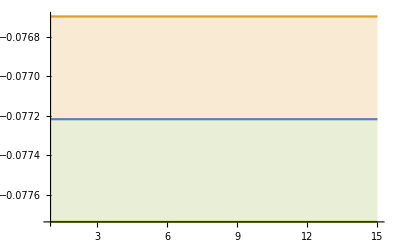

```mathematica
Plot[{fitData[[1]]//.Around[x_,y_]:>x,{fitData[[1]]//.Around[x_,y_]:>x+y,fitData[[1]]//.Around[x_,y_]:>x-y}},{x,1,15},Filling->{3->{1},2->{1}}]
```

```mathematica
SpoilHWFLOPlotN3=Show[Plot[{fitData[[1]]//.Around[x_,y_]:>x,{fitData[[1]]//.Around[x_,y_]:>x+y,fitData[[1]]//.Around[x_,y_]:>x-y}},{x,1,Length[meanErr2[[5]]]},Filling->{3->{1},2->{1}},PlotRange->{-1,.1}],ListPlot[{Table[{τSteps[[1,i]],meanErr2[[1,i]]},{i,1,Length[meanErr2[[1]]]}],Table[{τSteps[[2,i]],meanErr2[[2,i]]},{i,1,Length[meanErr2[[2]]]}],Table[{τSteps[[3,i]],meanErr2[[3,i]]},{i,1,Length[meanErr2[[3]]]}],Table[{τSteps[[4,i]],meanErr2[[4,i]]},{i,1,Length[meanErr2[[4]]]}],Table[{τSteps[[5,i]],meanErr2[[5,i]]},{i,1,Length[meanErr2[[5]]]}]},PlotRange->{-.1,-0.005},PlotLegends->Placed[αLegendLO,{0.5,0.1}],PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]],markerlist[[4]],markerlist[[5]]},IntervalMarkersStyle->{ColorData[97][3]},PlotStyle->{ColorData[97][3]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau_{\\text{steps}}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]},PlotLabel->MaTeX["N=3(\\text{LO})",Magnification->1.2]]
```

-Graphics-

#### QCD NNLO - HWF

```mathematica
Nf4α1LoopMid
Nf4α1LoopStepTab={393,393,393,393,393};
NWalkers=200;
Nf4α1LoopBig={0.225626,0.225626,0.225626,0.225626,0.225626};
aList={1,2,3,4,5};
```

{0.21556,0.220566,0.22639,0.233299,0.241701,0.252265,0.266178,0.285833}

```mathematica
csvData=Table[Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfhwf.csv"],{xx,1,Length[aList]}]
```

({mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.1162664438903607, -0.11755187432352941, -0.11996705499620176, -0.12081465899185101, -0.12128498076381489, -0.12151290446949953, -0.12073446781368206, -0.11998203198735437, -0.1224848004569982, -0.122506043693036, -0.12420701641763618, -0.12260473635465949, -0.12696857847942508, -0.1279943861242267, -0.1273865125709506, -0.12905514879358881, -0.1299386577790697, -0.12758876269913805, -0.1306236632635698, -0.12976147133879543, -0.13003847100275592, -0.13132544825386328, -0.13369895436941803, -0.13287351801903877, -0.13241423395600366, -0.13106153133403486, -0.13035208958034683, -0.1309533009161247, -0.1316304943346794, -0.13479831347268095, -0.13356830193215433, -0.135391373116478, -0.13255224154671844, -0.13138780848257375, -0.13148125272829567, -0.12888751723376154],[0.007790492743013512, 0.011364088263801522, 0.017174401403391958, 0.024741442583394724, 0.0335420119574276, 0.04532777075923729, 0.0625756067043317, 0.08169283702044902, 0.12034118563457567, 0.15533969464387784, 0.22579564025526946, 0.2773304690462676, 0.4329273408821782, 0.5930348362752662, 0.8194910240606665, 1.0939402964011926, 1.6127763839658742, 1.9960622889672044, 2.907551410512384, 3.675173446214386, 4.769083641562477, 6.282892833197728, 8.74945765551871, 10.926280210513484, 14.110318018308744, 18.048112030725836, 22.750261898764773, 30.563099792441815, 40.91015372493114, 58.49856414567124, 77.15419614468841, 107.90359564600648, 138.46421423868497, 173.67398426898782, 231.8612046470953, 297.11939396887885],-0.1205,0.000580276,0.817157}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.08298157450629393, -0.08447984983870625, -0.08542344545132723, -0.08670698072333578, -0.0884113730093597, -0.09003470697210599, -0.08977991581147055, -0.09033160911164469, -0.09019166906351529, -0.09159549882056948, -0.0922389388067997, -0.09690003106923642, -0.0932048795546296, -0.09360093230159512, -0.09404068589292763, -0.09413578758454057, -0.09529503766645349, -0.09645270073133305, -0.09825599590613689, -0.10516142730750623, -0.10443050977837134, -0.10645623317148753, -0.10946805534818575, -0.10733905897894502, -0.1168390323105123, -0.11200606466400942, -0.11036194416868594, -0.10561487625511956, -0.10685020082873768, -0.11159159502472071, -0.11365755482337724, -0.10596591891599426, -0.1033776387263141, -0.10236425942541863, -0.10484523061885681, -0.10533753785746332],[0.006702166710807417, 0.009518898437368518, 0.012355067102595239, 0.01618669826427025, 0.021805234038943078, 0.028723108040351775, 0.03628232179785333, 0.046777769881922046, 0.05864641722981402, 0.07371597395876404, 0.09384932273418384, 0.14088685988709607, 0.1494822114385234, 0.19714071648024808, 0.2551279666795054, 0.3138599912043852, 0.4101923821201879, 0.525816527535414, 0.6774771932863064, 1.006268357019756, 1.2739201252842796, 1.6934029423263444, 2.249625214489286, 2.7533587796903167, 4.336913504219928, 5.309177428933543, 7.175211332233474, 8.464654708197479, 11.606036126301458, 17.92803495445377, 24.481391205095466, 25.971971730015174, 29.461259460487504, 36.073307278027954, 46.958614326281484, 63.102331957493014],-0.0870232,0.00113499,0.411527}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.06548254888522961, -0.06650555824143882, -0.0692340175473183, -0.06967252415118283, -0.07178892443593098, -0.07424671822694211, -0.07430128055629925, -0.07596129876143924, -0.07588470379390211, -0.0767553509539781, -0.07912490122077018, -0.08028857678752514, -0.08278487052862149, -0.08519786308377639, -0.087133943970973, -0.08648511190461741, -0.08923450078930283, -0.091057557038532, -0.0903702565310451, -0.0944891979249465, -0.09752575937421348, -0.10509517874621148, -0.10726876543304228, -0.11073984941155397, -0.11317664866848326, -0.127029478858118, -0.13814597842942994, -0.1193960953699937, -0.1328205844990856, -0.12853884004001648, -0.12014944742417832, -0.10357693614559636, -0.0998487759978598, -0.10298138713248611, -0.10046701934773425, -0.10031633949519378],[0.005382460807537323, 0.007327154225008166, 0.010767462439993691, 0.013103237659367837, 0.017196916490079234, 0.02359112160199554, 0.029890043360231218, 0.037554423021664333, 0.04939371836102767, 0.0614485251423211, 0.08200972898702315, 0.10670651002205277, 0.14446092687244336, 0.1864481105110617, 0.24230195442112176, 0.2904408889512659, 0.398773000645398, 0.5137154251091317, 0.6039548652999642, 0.8050015194917551, 1.063919247846767, 1.5927953209034347, 2.0656602524294208, 2.877124027013189, 3.9956247878769133, 6.7567901338528635, 10.6448308730276, 10.90317796740184, 17.493512809248557, 23.28762400665299, 25.60348292028083, 25.373325261932354, 29.381837495642365, 37.50025908550517, 44.43732747586512, 54.082841831922735],-0.0690914,0.00127317,0.718725}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.05217754383445586, -0.053143366489555095, -0.05255123078446846, -0.05347073005887759, -0.05370057769293235, -0.05569512379566399, -0.05598080011493087, -0.05722726706345296, -0.05800834711326942, -0.059246802410155605, -0.059950255074993346, -0.06044585975583694, -0.061240178514048796, -0.0622403061367547, -0.06264865959720685, -0.0635688112647114, -0.06364728075616757, -0.06400669536281982, -0.06374360476861259, -0.06473746655210293, -0.06615168932297863, -0.06669324425862846, -0.06831603805713295, -0.06890385369281726, -0.06986663136851742, -0.07085715579815839, -0.07088960979468523, -0.07185721536245601, -0.07317589660565725, -0.0729674697474681, -0.0756540328911879, -0.07983689213789134, -0.09098199537417412, -0.08683079853490883, -0.08771673102006998, -0.08448586766738769],[0.00314566316181234, 0.004400423090212805, 0.004254937092583467, 0.005597023106586098, 0.006212523678432442, 0.008421354527909656, 0.010129650195430693, 0.012874909812597028, 0.01564445058311212, 0.01984328392243623, 0.023835784237624738, 0.02915607284110117, 0.03473833075393827, 0.042282811252834535, 0.0511323757831828, 0.0622916061156281, 0.07296002914612267, 0.08699925731433812, 0.09936905559814528, 0.11993319186357912, 0.15002409548618023, 0.17910618274751217, 0.2115525688583557, 0.26095881157118855, 0.32290525141066495, 0.39684046465663975, 0.4762323949332285, 0.5862685409506349, 0.746677518584019, 0.8989564475133626, 1.1854954041732169, 1.6054358267335573, 2.9041558834362733, 3.3608899645748282, 4.1841657736877975, 4.811652359021533],-0.0499419,0.000970266,0.244794}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.04555289181850203, -0.04608449667568943, -0.04708858082468054, -0.04901609784669225, -0.04840217866437448, -0.04879296289872079, -0.048739632423425654, -0.04917086079901792, -0.04930463780706945, -0.04964787912168994, -0.050804406254284055, -0.05167144017234296, -0.05276618949035244, -0.05400479442442335, -0.055086180422479876, -0.05596305476559666, -0.05687837200127097, -0.058916119906105555, -0.060032803553445445, -0.06399491112590044, -0.06834623616295751, -0.06619420130777474, -0.06718714266478099, -0.0680067870843512, -0.07136921374521048, -0.07046288709566612, -0.07274053369676249, -0.06988844645864116, -0.07042578346644766, -0.0703385600269079, -0.0720790212172363, -0.07004396630514723, -0.06897200670255293, -0.0702412390656859, -0.0710338859047692, -0.07392548567358358],[0.0027244853553688004, 0.003265302846450565, 0.004124902197177572, 0.006190027677333042, 0.006434208501656555, 0.007334065837466333, 0.008199047886147356, 0.009645878811342606, 0.011107169522927346, 0.012571509545419033, 0.01548228271757036, 0.01871574367923198, 0.022816569410768733, 0.028032531591398215, 0.034299843073684506, 0.041921331170419754, 0.051682123333775455, 0.0672173036802485, 0.07983961757787197, 0.1233905040651305, 0.18358353993659016, 0.18751663469783827, 0.2297116964603712, 0.2738477804646722, 0.3461316326295412, 0.4231763892818782, 0.5375539502232755, 0.5880390137560096, 0.736622604615091, 0.8572265754864486, 1.1190745692197988, 1.157633015124457, 1.3504977828693756, 1.6957660179098224, 2.0423892972667304, 2.698629648873901],-0.0453616,0.000910174,0.353529})

```mathematica
meanErr=Table[Table[csvData[[xx,2,yy]]//StringSplit[#,{",","[","]"}]&,{yy,1,2}],{xx,1,Length[aList]}]
```

({-0.1162664438903607, -0.11755187432352941, -0.11996705499620176, -0.12081465899185101, -0.12128498076381489, -0.12151290446949953, -0.12073446781368206, -0.11998203198735437, -0.1224848004569982, -0.122506043693036, -0.12420701641763618, -0.12260473635465949, -0.12696857847942508, -0.1279943861242267, -0.1273865125709506, -0.12905514879358881, -0.1299386577790697, -0.12758876269913805, -0.1306236632635698, -0.12976147133879543, -0.13003847100275592, -0.13132544825386328, -0.13369895436941803, -0.13287351801903877, -0.13241423395600366, -0.13106153133403486, -0.13035208958034683, -0.1309533009161247, -0.1316304943346794, -0.13479831347268095, -0.13356830193215433, -0.135391373116478, -0.13255224154671844, -0.13138780848257375, -0.13148125272829567, -0.12888751723376154} | {0.007790492743013512, 0.011364088263801522, 0.017174401403391958, 0.024741442583394724, 0.0335420119574276, 0.04532777075923729, 0.0625756067043317, 0.08169283702044902, 0.12034118563457567, 0.15533969464387784, 0.22579564025526946, 0.2773304690462676, 0.4329273408821782, 0.5930348362752662, 0.8194910240606665, 1.0939402964011926, 1.6127763839658742, 1.9960622889672044, 2.907551410512384, 3.675173446214386, 4.769083641562477, 6.282892833197728, 8.74945765551871, 10.926280210513484, 14.110318018308744, 18.048112030725836, 22.750261898764773, 30.563099792441815, 40.91015372493114, 58.49856414567124, 77.15419614468841, 107.90359564600648, 138.46421423868497, 173.67398426898782, 231.8612046470953, 297.11939396887885}
{-0.08298157450629393, -0.08447984983870625, -0.08542344545132723, -0.08670698072333578, -0.0884113730093597, -0.09003470697210599, -0.08977991581147055, -0.09033160911164469, -0.09019166906351529, -0.09159549882056948, -0.0922389388067997, -0.09690003106923642, -0.0932048795546296, -0.09360093230159512, -0.09404068589292763, -0.09413578758454057, -0.09529503766645349, -0.09645270073133305, -0.09825599590613689, -0.10516142730750623, -0.10443050977837134, -0.10645623317148753, -0.10946805534818575, -0.10733905897894502, -0.1168390323105123, -0.11200606466400942, -0.11036194416868594, -0.10561487625511956, -0.10685020082873768, -0.11159159502472071, -0.11365755482337724, -0.10596591891599426, -0.1033776387263141, -0.10236425942541863, -0.10484523061885681, -0.10533753785746332} | {0.006702166710807417, 0.009518898437368518, 0.012355067102595239, 0.01618669826427025, 0.021805234038943078, 0.028723108040351775, 0.03628232179785333, 0.046777769881922046, 0.05864641722981402, 0.07371597395876404, 0.09384932273418384, 0.14088685988709607, 0.1494822114385234, 0.19714071648024808, 0.2551279666795054, 0.3138599912043852, 0.4101923821201879, 0.525816527535414, 0.6774771932863064, 1.006268357019756, 1.2739201252842796, 1.6934029423263444, 2.249625214489286, 2.7533587796903167, 4.336913504219928, 5.309177428933543, 7.175211332233474, 8.464654708197479, 11.606036126301458, 17.92803495445377, 24.481391205095466, 25.971971730015174, 29.461259460487504, 36.073307278027954, 46.958614326281484, 63.102331957493014}
{-0.06548254888522961, -0.06650555824143882, -0.0692340175473183, -0.06967252415118283, -0.07178892443593098, -0.07424671822694211, -0.07430128055629925, -0.07596129876143924, -0.07588470379390211, -0.0767553509539781, -0.07912490122077018, -0.08028857678752514, -0.08278487052862149, -0.08519786308377639, -0.087133943970973, -0.08648511190461741, -0.08923450078930283, -0.091057557038532, -0.0903702565310451, -0.0944891979249465, -0.09752575937421348, -0.10509517874621148, -0.10726876543304228, -0.11073984941155397, -0.11317664866848326, -0.127029478858118, -0.13814597842942994, -0.1193960953699937, -0.1328205844990856, -0.12853884004001648, -0.12014944742417832, -0.10357693614559636, -0.0998487759978598, -0.10298138713248611, -0.10046701934773425, -0.10031633949519378} | {0.005382460807537323, 0.007327154225008166, 0.010767462439993691, 0.013103237659367837, 0.017196916490079234, 0.02359112160199554, 0.029890043360231218, 0.037554423021664333, 0.04939371836102767, 0.0614485251423211, 0.08200972898702315, 0.10670651002205277, 0.14446092687244336, 0.1864481105110617, 0.24230195442112176, 0.2904408889512659, 0.398773000645398, 0.5137154251091317, 0.6039548652999642, 0.8050015194917551, 1.063919247846767, 1.5927953209034347, 2.0656602524294208, 2.877124027013189, 3.9956247878769133, 6.7567901338528635, 10.6448308730276, 10.90317796740184, 17.493512809248557, 23.28762400665299, 25.60348292028083, 25.373325261932354, 29.381837495642365, 37.50025908550517, 44.43732747586512, 54.082841831922735}
{-0.05217754383445586, -0.053143366489555095, -0.05255123078446846, -0.05347073005887759, -0.05370057769293235, -0.05569512379566399, -0.05598080011493087, -0.05722726706345296, -0.05800834711326942, -0.059246802410155605, -0.059950255074993346, -0.06044585975583694, -0.061240178514048796, -0.0622403061367547, -0.06264865959720685, -0.0635688112647114, -0.06364728075616757, -0.06400669536281982, -0.06374360476861259, -0.06473746655210293, -0.06615168932297863, -0.06669324425862846, -0.06831603805713295, -0.06890385369281726, -0.06986663136851742, -0.07085715579815839, -0.07088960979468523, -0.07185721536245601, -0.07317589660565725, -0.0729674697474681, -0.0756540328911879, -0.07983689213789134, -0.09098199537417412, -0.08683079853490883, -0.08771673102006998, -0.08448586766738769} | {0.00314566316181234, 0.004400423090212805, 0.004254937092583467, 0.005597023106586098, 0.006212523678432442, 0.008421354527909656, 0.010129650195430693, 0.012874909812597028, 0.01564445058311212, 0.01984328392243623, 0.023835784237624738, 0.02915607284110117, 0.03473833075393827, 0.042282811252834535, 0.0511323757831828, 0.0622916061156281, 0.07296002914612267, 0.08699925731433812, 0.09936905559814528, 0.11993319186357912, 0.15002409548618023, 0.17910618274751217, 0.2115525688583557, 0.26095881157118855, 0.32290525141066495, 0.39684046465663975, 0.4762323949332285, 0.5862685409506349, 0.746677518584019, 0.8989564475133626, 1.1854954041732169, 1.6054358267335573, 2.9041558834362733, 3.3608899645748282, 4.1841657736877975, 4.811652359021533}
{-0.04555289181850203, -0.04608449667568943, -0.04708858082468054, -0.04901609784669225, -0.04840217866437448, -0.04879296289872079, -0.048739632423425654, -0.04917086079901792, -0.04930463780706945, -0.04964787912168994, -0.050804406254284055, -0.05167144017234296, -0.05276618949035244, -0.05400479442442335, -0.055086180422479876, -0.05596305476559666, -0.05687837200127097, -0.058916119906105555, -0.060032803553445445, -0.06399491112590044, -0.06834623616295751, -0.06619420130777474, -0.06718714266478099, -0.0680067870843512, -0.07136921374521048, -0.07046288709566612, -0.07274053369676249, -0.06988844645864116, -0.07042578346644766, -0.0703385600269079, -0.0720790212172363, -0.07004396630514723, -0.06897200670255293, -0.0702412390656859, -0.0710338859047692, -0.07392548567358358} | {0.0027244853553688004, 0.003265302846450565, 0.004124902197177572, 0.006190027677333042, 0.006434208501656555, 0.007334065837466333, 0.008199047886147356, 0.009645878811342606, 0.011107169522927346, 0.012571509545419033, 0.01548228271757036, 0.01871574367923198, 0.022816569410768733, 0.028032531591398215, 0.034299843073684506, 0.041921331170419754, 0.051682123333775455, 0.0672173036802485, 0.07983961757787197, 0.1233905040651305, 0.18358353993659016, 0.18751663469783827, 0.2297116964603712, 0.2738477804646722, 0.3461316326295412, 0.4231763892818782, 0.5375539502232755, 0.5880390137560096, 0.736622604615091, 0.8572265754864486, 1.1190745692197988, 1.157633015124457, 1.3504977828693756, 1.6957660179098224, 2.0423892972667304, 2.698629648873901})

```mathematica
meanErr2=Table[Table[Around[meanErr[[xx,1,yy]]//ToExpression,meanErr[[xx,2,yy]]//ToExpression],{yy,1,Length[meanErr[[xx,1]]]}],{xx,1,Length[aList]}]
```

(-0.1160.008 | -0.1180.011 | -0.1200.017 | -0.1210.025 | -0.1210.034 | -0.120.05 | -0.120.06 | -0.120.08 | -0.120.12 | -0.120.16 | -0.120.23 | -0.120.28 | -0.10.4 | -0.10.6 | -0.10.8 | -0.11.1 | -0.11.6 | -0.12.0 | -0.12.9 | 0.4. | 0.5. | 0.6. | 0.9. | 0.11. | 0.14. | 0.18. | 0.23. | 0.31. | 0.41. | 0.58. | 0.77. | 0.108. | 0.138. | 0.174. | 0.232. | 0.297.
-0.0830.007 | -0.0840.010 | -0.0850.012 | -0.0870.016 | -0.0880.022 | -0.0900.029 | -0.090.04 | -0.090.05 | -0.090.06 | -0.090.07 | -0.090.09 | -0.100.14 | -0.090.15 | -0.090.20 | -0.090.26 | -0.090.31 | 0.00.4 | 0.00.5 | 0.00.7 | -0.11.0 | -0.11.3 | -0.11.7 | -0.12.2 | -0.12.8 | 0.4. | 0.5. | 0.7. | 0.8. | 0.12. | 0.18. | 0.24. | 0.26. | 0.29. | 0.36. | 0.47. | 0.63.
-0.0650.005 | -0.0670.007 | -0.0690.011 | -0.0700.013 | -0.0720.017 | -0.0740.024 | -0.0740.030 | -0.080.04 | -0.080.05 | -0.080.06 | -0.080.08 | -0.080.11 | -0.080.14 | -0.090.19 | -0.090.24 | -0.090.29 | 0.00.4 | 0.00.5 | 0.00.6 | 0.00.8 | 0.01.1 | -0.11.6 | -0.12.1 | -0.12.9 | 0.4. | 0.7. | 0.11. | 0.11. | 0.17. | 0.23. | 0.26. | 0.25. | 0.29. | 0.38. | 0.44. | 0.54.
-0.05220.0031 | -0.0530.004 | -0.0530.004 | -0.0530.006 | -0.0540.006 | -0.0560.008 | -0.0560.010 | -0.0570.013 | -0.0580.016 | -0.0590.020 | -0.0600.024 | -0.0600.029 | -0.0610.035 | -0.060.04 | -0.060.05 | -0.060.06 | -0.060.07 | -0.060.09 | -0.060.10 | -0.060.12 | -0.070.15 | -0.070.18 | -0.070.21 | -0.070.26 | -0.070.32 | 0.00.4 | 0.00.5 | 0.00.6 | 0.00.7 | 0.00.9 | 0.01.2 | 0.01.6 | 0.02.9 | 0.03.4 | 0.4. | 0.5.
-0.04560.0027 | -0.04610.0033 | -0.0470.004 | -0.0490.006 | -0.0480.006 | -0.0490.007 | -0.0490.008 | -0.0490.010 | -0.0490.011 | -0.0500.013 | -0.0510.015 | -0.0520.019 | -0.0530.023 | -0.0540.028 | -0.0550.034 | -0.060.04 | -0.060.05 | -0.060.07 | -0.060.08 | -0.060.12 | -0.070.18 | -0.070.19 | -0.070.23 | -0.070.27 | -0.070.35 | 0.00.4 | 0.00.5 | 0.00.6 | 0.00.7 | 0.00.9 | 0.01.1 | 0.01.2 | 0.01.4 | 0.01.7 | 0.02.0 | 0.02.7)

```mathematica
τSteps=Table[Table[xx,{xx,1,Length[meanErr2[[yy]]]}],{yy,1,Length[meanErr2]}]
```

(1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36)

```mathematica
fitData=Table[Around[Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfhwf.csv"][[2,3]],Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfhwf.csv"][[2,4]]],{xx,1,Length[aList]}]
```

{-0.12050.0006,-0.08700.0011,-0.06910.0013,-0.04990.0010,-0.04540.0009}

```mathematica
αLegendLO=PointLegend[Table[Directive[ColorData[97][1]],{ii,5}],{MaTeX["a=1",Magnification->0.8],MaTeX["a=2",Magnification->0.8],MaTeX["a=3",Magnification->0.8],MaTeX["a=4",Magnification->0.8],MaTeX["a=5",Magnification->0.8]},LegendMarkers->Table[Style[markerlist[[ii]],14,Bold,ColorData[97][3]],{ii,5}],LegendLayout->"Row",LegendMargins->0.5,LegendFunction->frame]
```

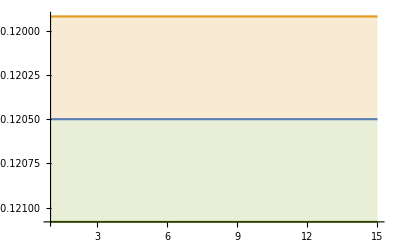

```mathematica
Plot[{fitData[[1]]//.Around[x_,y_]:>x,{fitData[[1]]//.Around[x_,y_]:>x+y,fitData[[1]]//.Around[x_,y_]:>x-y}},{x,1,15},Filling->{3->{1},2->{1}}]
```

```mathematica
SpoilHWFLOPlotN3=Show[Plot[{fitData[[1]]//.Around[x_,y_]:>x,{fitData[[1]]//.Around[x_,y_]:>x+y,fitData[[1]]//.Around[x_,y_]:>x-y}},{x,1,Length[meanErr2[[5]]]},Filling->{3->{1},2->{1}},PlotRange->{-1,1}],ListPlot[{Table[{τSteps[[1,i]],meanErr2[[1,i]]},{i,1,Length[meanErr2[[1]]]}],Table[{τSteps[[2,i]],meanErr2[[2,i]]},{i,1,Length[meanErr2[[2]]]}],Table[{τSteps[[3,i]],meanErr2[[3,i]]},{i,1,Length[meanErr2[[3]]]}],Table[{τSteps[[4,i]],meanErr2[[4,i]]},{i,1,Length[meanErr2[[4]]]}],Table[{τSteps[[5,i]],meanErr2[[5,i]]},{i,1,Length[meanErr2[[5]]]}]},PlotRange->{-.03,-0.005},PlotLegends->Placed[αLegendLO,{0.5,0.1}],PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]],markerlist[[4]],markerlist[[5]]},IntervalMarkersStyle->{ColorData[97][3]},PlotStyle->{ColorData[97][3]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau_{\\text{steps}}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]},PlotLabel->MaTeX["N=3(\\text{LO})",Magnification->1.2]]
```

-Graphics-

#### QCD LO - gauss

```mathematica
Nf4α1LoopMid
Nf4α1LoopStepTab={430,430,430,430,430};
NWalkers=200;
Nf4α1LoopBig={0.21556,0.21556,0.21556,0.21556,0.21556};
aList={1,2,3,4,5};
```

{0.21556,0.220566,0.22639,0.233299,0.241701,0.252265,0.266178,0.285833}

```mathematica
csvData=Table[Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfgauss.csv"],{xx,1,Length[aList]}]
```

({mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.01971468858875101, -0.019037163362446513, -0.019226367741686515, -0.019032176046117955, -0.017554270710280612, -0.01671124421572221, -0.01751869072235425, -0.018702719025080833, -0.021281586662776384, -0.0185905801505736, -0.017901361709679858, -0.020179642276351568, -0.01934031898686775, -0.019271331189346007, -0.01963271716617969, -0.019146261168304004, -0.01977960594844721, -0.0209152621297911, -0.02094357041483927, -0.020607805928180623, -0.020204391166476036, -0.020492329564798333, -0.020439211219655053, -0.020122862414850444, -0.021467401162930735, -0.02133496550943241, -0.01963650459774765, -0.01962420525980539, -0.019716144022492284, -0.020101504435093818, -0.020667585301143633, -0.022270790219490647, -0.020776425930848913, -0.020810044385248083, -0.022390490989798967, -0.022894627487437747, -0.025087564789790535, -0.02454594983964606, -0.0246886549752986],[0.00189187427656313, 0.001672000219027578, 0.002034738380204643, 0.0020418308786686484, 0.0014416080126370674, 0.0012727077491954209, 0.001484708325675217, 0.0023428719325492486, 0.006264452875015763, 0.0023501852493671895, 0.0021948218934679424, 0.003752636714996491, 0.0028355632577568373, 0.002429077052227895, 0.003582672037649232, 0.002574876807063755, 0.003229499759282239, 0.004742997662049212, 0.004635038612003625, 0.005242005618430826, 0.0033629234483246533, 0.003559755960343646, 0.004040960273116776, 0.0037701162971757927, 0.005592044568721147, 0.005925222467540463, 0.0047616147643315294, 0.004994730664519577, 0.0050047723415755155, 0.006104642200572163, 0.006691866830094403, 0.009251154523986522, 0.006692757591344582, 0.006434245068537048, 0.0091703700337052, 0.010314092733088242, 0.016253076657653426, 0.014413649619438296, 0.014772015036165261],-0.0180931,0.000213564,0.459877}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.016670953654173874, -0.016611727988751428, -0.016290027688724368, -0.016207812025066968, -0.016154349883768647, -0.01605084589565284, -0.015674274479704615, -0.015827434123758585, -0.01605928715271865, -0.01594534380404792, -0.015631792479815696, -0.015727472972830007, -0.015818310609766566, -0.016255824769449444, -0.016634917265821905, -0.016032947267709586, -0.016592065343492664, -0.01814937875288898, -0.016709079330039928, -0.01703333576052526, -0.017198843456722394, -0.01755643689550296, -0.018258474942212694, -0.017637598187948637, -0.01771947262268759, -0.01699562729560975, -0.017756586956430325, -0.018022513170563324, -0.017639706486166355, -0.01768315345850158, -0.01826773604585575, -0.019753591220134707, -0.01946108299205785, -0.02015255147724005, -0.018976454086197463, -0.018137336277582766, -0.018618036255465476, -0.018053511532906685, -0.017659565735194508],[0.000987118350282628, 0.0009739992616041703, 0.00097831767611948, 0.000940457686011133, 0.0009785384362078818, 0.0010293948188056438, 0.0009189359476803141, 0.00099187158321113, 0.0011107073560442558, 0.0011180970346383295, 0.001202514457905457, 0.0012708522359900127, 0.0012944886789590085, 0.0015256114253981734, 0.0017007858713456833, 0.0014754958000810952, 0.0018290409147307864, 0.0038075058353369716, 0.0021552868598266363, 0.002498907648126143, 0.002552253227723886, 0.0028935555567358127, 0.0037319642557687217, 0.0032935803468644455, 0.004077159492789482, 0.0034990893697013424, 0.00429860703112307, 0.005322764419037778, 0.004889448904629628, 0.004755520551432187, 0.006293449654077616, 0.00788179604988457, 0.0075353179912413405, 0.008879394825167392, 0.007733671593962554, 0.006944684965777704, 0.008249752837900737, 0.007560717765071675, 0.007935816552381132],-0.0148307,0.000224615,0.198134}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.011817018071456091, -0.011951041581944814, -0.011934700109847544, -0.012021472083229082, -0.012256512919072196, -0.01242335419163962, -0.012353134723541676, -0.012304075847877531, -0.012366450491445278, -0.012304601429291864, -0.012321542719228147, -0.012357704678904695, -0.012240200353110001, -0.012088730731899235, -0.012285385852660992, -0.012250184537751374, -0.012201884672376784, -0.01270386543559413, -0.012137210146639484, -0.012247256330147123, -0.012270773120833939, -0.012861481252883805, -0.012787760428863142, -0.01259630762875393, -0.012456138680586579, -0.0127420250252084, -0.013072478248170455, -0.012767354616167613, -0.012967939541596646, -0.013099960757417605, -0.013508004069478547, -0.013915306998267967, -0.014350972321690237, -0.013151653883317566, -0.013526186624100604, -0.014093666475130424, -0.014566549571891654, -0.013748855542791953, -0.013591610083594819],[0.0004418566612471855, 0.0004859452294005191, 0.0005100059800676989, 0.0005464984430503865, 0.0006847260635712545, 0.0007615373293153927, 0.0009329506389495703, 0.0007845385956483573, 0.0007678036191030764, 0.0008341086679735894, 0.0009025486017375974, 0.0009824947645618563, 0.0009451497245616236, 0.0008875317865649733, 0.0009761949861595955, 0.0009842335581108097, 0.001007874408955539, 0.001536646202113251, 0.0010912931122861247, 0.0011483250236902283, 0.0012064613121931214, 0.0016264986620770998, 0.0016839016187252917, 0.0015155248141000247, 0.0014899677355461527, 0.0017641439020458357, 0.002127054841988251, 0.0017979268349712333, 0.002037866821101543, 0.0021945591139185916, 0.002718672603304244, 0.0034495773431215872, 0.004175244136943048, 0.0027946764676861128, 0.003124018976726264, 0.0038655069091318717, 0.004855586370459534, 0.0038805715517820382, 0.003874802815300355],-0.0108744,0.000189069,0.148083}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.009839527200454699, -0.009649270871183946, -0.009409330206446345, -0.00937991914151552, -0.009438239938067495, -0.009502535829046402, -0.009590923013814543, -0.009710614447655414, -0.009545478535337762, -0.009797111330286495, -0.009901447301136559, -0.009970306595563742, -0.010366170215787873, -0.010285779242305036, -0.010093943456746525, -0.009889228313368643, -0.009900068494815025, -0.010105766160010975, -0.010265135943772583, -0.010557168164088736, -0.010106884839300358, -0.010374913688798115, -0.01028102165992289, -0.010396614859255403, -0.010404074216655542, -0.010455438391196618, -0.0102810194664897, -0.010071618466399162, -0.010117920819123986, -0.010285448372078466, -0.01020571344854937, -0.010188105931300909, -0.01009371785379391, -0.01040219965110325, -0.010702083947831044, -0.010591990397534869, -0.010712102329330458, -0.011287991141316822, -0.010810982251363743],[0.0007520884577794277, 0.0006237598039946547, 0.000409456510093125, 0.0004036293170076621, 0.00046129889741021565, 0.0004805136422826482, 0.00055293295922176, 0.0006222196519628041, 0.0005674262945813727, 0.0007080464703996439, 0.0008305831395750251, 0.0009112347652875846, 0.0012783473363605906, 0.001245012198375791, 0.0009536097075719543, 0.0008894592570831385, 0.0009946390594808784, 0.0011793234780972705, 0.0014300000970834915, 0.0016377925723284803, 0.0012272758761453346, 0.0014175995089097508, 0.0013731019059252088, 0.0013578698454304958, 0.001409197893327881, 0.0013966195047991439, 0.0014418549124042225, 0.001354325993875987, 0.0014067412290596308, 0.0015171983624055723, 0.0015181793985926516, 0.001549532108067821, 0.0015372660180339485, 0.0018242197512389595, 0.002052182815907169, 0.0020492501967865526, 0.002178245781240851, 0.0028240752708090645, 0.0023788100792406183],-0.00897511,0.000176725,0.0882805}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.007925871681715218, -0.008031043488573253, -0.007914060476678027, -0.0079396730857761, -0.007943249354796032, -0.007943800691218141, -0.007822349259376306, -0.007881590043407414, -0.0078865517894066, -0.007963765491811452, -0.008107783877666419, -0.008111474318846611, -0.008111388948625141, -0.008135168942997125, -0.008098266697865971, -0.008074891711710235, -0.008135788211870793, -0.008171643324663752, -0.008081262892482285, -0.008312894951931347, -0.008357343048330567, -0.008470423327097394, -0.008823843307149592, -0.00849273801196628, -0.008511737572101542, -0.008390347888891562, -0.008546870885777987, -0.00848801223117544, -0.008593185714069057, -0.008551873316253851, -0.008442734170923304, -0.008487491514396203, -0.008463762456589962, -0.008811537394632299, -0.008738065822236966, -0.008881501483762353, -0.009084891694345591, -0.0089468184959429, -0.008682723215485829],[0.0003200768940474056, 0.0003497970942746267, 0.00031526139574623624, 0.0003350472628171471, 0.0003511360345206767, 0.0003586102339874374, 0.0003304022169958536, 0.00035410499474381504, 0.00035584825004135137, 0.00038693799768809854, 0.0004875088045713704, 0.000511385577289996, 0.0005237849455956955, 0.0005426664421954299, 0.0005211722144143086, 0.0005215648307357752, 0.000571596661690209, 0.0006584690661957946, 0.0006079708989010132, 0.0007997514028853346, 0.0007815048512208843, 0.0009356073483865882, 0.0015044833703258254, 0.0009756711658620589, 0.000987022408307523, 0.0008591066374409422, 0.0010260924291757277, 0.0009659220323430961, 0.0010709305638539814, 0.0011045053175607106, 0.0010659895636367315, 0.0010918271602576505, 0.001068615550729989, 0.0013942072574621017, 0.0013155481998002646, 0.0015969621933529079, 0.0020060363853364386, 0.0018918044929269015, 0.0014323538629212665],-0.00754451,0.000168171,0.0581625})

```mathematica
meanErr=Table[Table[csvData[[xx,2,yy]]//StringSplit[#,{",","[","]"}]&,{yy,1,2}],{xx,1,Length[aList]}]
```

({-0.01971468858875101, -0.019037163362446513, -0.019226367741686515, -0.019032176046117955, -0.017554270710280612, -0.01671124421572221, -0.01751869072235425, -0.018702719025080833, -0.021281586662776384, -0.0185905801505736, -0.017901361709679858, -0.020179642276351568, -0.01934031898686775, -0.019271331189346007, -0.01963271716617969, -0.019146261168304004, -0.01977960594844721, -0.0209152621297911, -0.02094357041483927, -0.020607805928180623, -0.020204391166476036, -0.020492329564798333, -0.020439211219655053, -0.020122862414850444, -0.021467401162930735, -0.02133496550943241, -0.01963650459774765, -0.01962420525980539, -0.019716144022492284, -0.020101504435093818, -0.020667585301143633, -0.022270790219490647, -0.020776425930848913, -0.020810044385248083, -0.022390490989798967, -0.022894627487437747, -0.025087564789790535, -0.02454594983964606, -0.0246886549752986} | {0.00189187427656313, 0.001672000219027578, 0.002034738380204643, 0.0020418308786686484, 0.0014416080126370674, 0.0012727077491954209, 0.001484708325675217, 0.0023428719325492486, 0.006264452875015763, 0.0023501852493671895, 0.0021948218934679424, 0.003752636714996491, 0.0028355632577568373, 0.002429077052227895, 0.003582672037649232, 0.002574876807063755, 0.003229499759282239, 0.004742997662049212, 0.004635038612003625, 0.005242005618430826, 0.0033629234483246533, 0.003559755960343646, 0.004040960273116776, 0.0037701162971757927, 0.005592044568721147, 0.005925222467540463, 0.0047616147643315294, 0.004994730664519577, 0.0050047723415755155, 0.006104642200572163, 0.006691866830094403, 0.009251154523986522, 0.006692757591344582, 0.006434245068537048, 0.0091703700337052, 0.010314092733088242, 0.016253076657653426, 0.014413649619438296, 0.014772015036165261}
{-0.016670953654173874, -0.016611727988751428, -0.016290027688724368, -0.016207812025066968, -0.016154349883768647, -0.01605084589565284, -0.015674274479704615, -0.015827434123758585, -0.01605928715271865, -0.01594534380404792, -0.015631792479815696, -0.015727472972830007, -0.015818310609766566, -0.016255824769449444, -0.016634917265821905, -0.016032947267709586, -0.016592065343492664, -0.01814937875288898, -0.016709079330039928, -0.01703333576052526, -0.017198843456722394, -0.01755643689550296, -0.018258474942212694, -0.017637598187948637, -0.01771947262268759, -0.01699562729560975, -0.017756586956430325, -0.018022513170563324, -0.017639706486166355, -0.01768315345850158, -0.01826773604585575, -0.019753591220134707, -0.01946108299205785, -0.02015255147724005, -0.018976454086197463, -0.018137336277582766, -0.018618036255465476, -0.018053511532906685, -0.017659565735194508} | {0.000987118350282628, 0.0009739992616041703, 0.00097831767611948, 0.000940457686011133, 0.0009785384362078818, 0.0010293948188056438, 0.0009189359476803141, 0.00099187158321113, 0.0011107073560442558, 0.0011180970346383295, 0.001202514457905457, 0.0012708522359900127, 0.0012944886789590085, 0.0015256114253981734, 0.0017007858713456833, 0.0014754958000810952, 0.0018290409147307864, 0.0038075058353369716, 0.0021552868598266363, 0.002498907648126143, 0.002552253227723886, 0.0028935555567358127, 0.0037319642557687217, 0.0032935803468644455, 0.004077159492789482, 0.0034990893697013424, 0.00429860703112307, 0.005322764419037778, 0.004889448904629628, 0.004755520551432187, 0.006293449654077616, 0.00788179604988457, 0.0075353179912413405, 0.008879394825167392, 0.007733671593962554, 0.006944684965777704, 0.008249752837900737, 0.007560717765071675, 0.007935816552381132}
{-0.011817018071456091, -0.011951041581944814, -0.011934700109847544, -0.012021472083229082, -0.012256512919072196, -0.01242335419163962, -0.012353134723541676, -0.012304075847877531, -0.012366450491445278, -0.012304601429291864, -0.012321542719228147, -0.012357704678904695, -0.012240200353110001, -0.012088730731899235, -0.012285385852660992, -0.012250184537751374, -0.012201884672376784, -0.01270386543559413, -0.012137210146639484, -0.012247256330147123, -0.012270773120833939, -0.012861481252883805, -0.012787760428863142, -0.01259630762875393, -0.012456138680586579, -0.0127420250252084, -0.013072478248170455, -0.012767354616167613, -0.012967939541596646, -0.013099960757417605, -0.013508004069478547, -0.013915306998267967, -0.014350972321690237, -0.013151653883317566, -0.013526186624100604, -0.014093666475130424, -0.014566549571891654, -0.013748855542791953, -0.013591610083594819} | {0.0004418566612471855, 0.0004859452294005191, 0.0005100059800676989, 0.0005464984430503865, 0.0006847260635712545, 0.0007615373293153927, 0.0009329506389495703, 0.0007845385956483573, 0.0007678036191030764, 0.0008341086679735894, 0.0009025486017375974, 0.0009824947645618563, 0.0009451497245616236, 0.0008875317865649733, 0.0009761949861595955, 0.0009842335581108097, 0.001007874408955539, 0.001536646202113251, 0.0010912931122861247, 0.0011483250236902283, 0.0012064613121931214, 0.0016264986620770998, 0.0016839016187252917, 0.0015155248141000247, 0.0014899677355461527, 0.0017641439020458357, 0.002127054841988251, 0.0017979268349712333, 0.002037866821101543, 0.0021945591139185916, 0.002718672603304244, 0.0034495773431215872, 0.004175244136943048, 0.0027946764676861128, 0.003124018976726264, 0.0038655069091318717, 0.004855586370459534, 0.0038805715517820382, 0.003874802815300355}
{-0.009839527200454699, -0.009649270871183946, -0.009409330206446345, -0.00937991914151552, -0.009438239938067495, -0.009502535829046402, -0.009590923013814543, -0.009710614447655414, -0.009545478535337762, -0.009797111330286495, -0.009901447301136559, -0.009970306595563742, -0.010366170215787873, -0.010285779242305036, -0.010093943456746525, -0.009889228313368643, -0.009900068494815025, -0.010105766160010975, -0.010265135943772583, -0.010557168164088736, -0.010106884839300358, -0.010374913688798115, -0.01028102165992289, -0.010396614859255403, -0.010404074216655542, -0.010455438391196618, -0.0102810194664897, -0.010071618466399162, -0.010117920819123986, -0.010285448372078466, -0.01020571344854937, -0.010188105931300909, -0.01009371785379391, -0.01040219965110325, -0.010702083947831044, -0.010591990397534869, -0.010712102329330458, -0.011287991141316822, -0.010810982251363743} | {0.0007520884577794277, 0.0006237598039946547, 0.000409456510093125, 0.0004036293170076621, 0.00046129889741021565, 0.0004805136422826482, 0.00055293295922176, 0.0006222196519628041, 0.0005674262945813727, 0.0007080464703996439, 0.0008305831395750251, 0.0009112347652875846, 0.0012783473363605906, 0.001245012198375791, 0.0009536097075719543, 0.0008894592570831385, 0.0009946390594808784, 0.0011793234780972705, 0.0014300000970834915, 0.0016377925723284803, 0.0012272758761453346, 0.0014175995089097508, 0.0013731019059252088, 0.0013578698454304958, 0.001409197893327881, 0.0013966195047991439, 0.0014418549124042225, 0.001354325993875987, 0.0014067412290596308, 0.0015171983624055723, 0.0015181793985926516, 0.001549532108067821, 0.0015372660180339485, 0.0018242197512389595, 0.002052182815907169, 0.0020492501967865526, 0.002178245781240851, 0.0028240752708090645, 0.0023788100792406183}
{-0.007925871681715218, -0.008031043488573253, -0.007914060476678027, -0.0079396730857761, -0.007943249354796032, -0.007943800691218141, -0.007822349259376306, -0.007881590043407414, -0.0078865517894066, -0.007963765491811452, -0.008107783877666419, -0.008111474318846611, -0.008111388948625141, -0.008135168942997125, -0.008098266697865971, -0.008074891711710235, -0.008135788211870793, -0.008171643324663752, -0.008081262892482285, -0.008312894951931347, -0.008357343048330567, -0.008470423327097394, -0.008823843307149592, -0.00849273801196628, -0.008511737572101542, -0.008390347888891562, -0.008546870885777987, -0.00848801223117544, -0.008593185714069057, -0.008551873316253851, -0.008442734170923304, -0.008487491514396203, -0.008463762456589962, -0.008811537394632299, -0.008738065822236966, -0.008881501483762353, -0.009084891694345591, -0.0089468184959429, -0.008682723215485829} | {0.0003200768940474056, 0.0003497970942746267, 0.00031526139574623624, 0.0003350472628171471, 0.0003511360345206767, 0.0003586102339874374, 0.0003304022169958536, 0.00035410499474381504, 0.00035584825004135137, 0.00038693799768809854, 0.0004875088045713704, 0.000511385577289996, 0.0005237849455956955, 0.0005426664421954299, 0.0005211722144143086, 0.0005215648307357752, 0.000571596661690209, 0.0006584690661957946, 0.0006079708989010132, 0.0007997514028853346, 0.0007815048512208843, 0.0009356073483865882, 0.0015044833703258254, 0.0009756711658620589, 0.000987022408307523, 0.0008591066374409422, 0.0010260924291757277, 0.0009659220323430961, 0.0010709305638539814, 0.0011045053175607106, 0.0010659895636367315, 0.0010918271602576505, 0.001068615550729989, 0.0013942072574621017, 0.0013155481998002646, 0.0015969621933529079, 0.0020060363853364386, 0.0018918044929269015, 0.0014323538629212665})

```mathematica
meanErr[[1,2,1]]//ToExpression
```

0.00189187

```mathematica
meanErr[[1]]
```

(-0.01971468858875101 |  -0.019037163362446513 |  -0.019226367741686515 |  -0.019032176046117955 |  -0.017554270710280612 |  -0.01671124421572221 |  -0.01751869072235425 |  -0.018702719025080833 |  -0.021281586662776384 |  -0.0185905801505736 |  -0.017901361709679858 |  -0.020179642276351568 |  -0.01934031898686775 |  -0.019271331189346007 |  -0.01963271716617969 |  -0.019146261168304004 |  -0.01977960594844721 |  -0.0209152621297911 |  -0.02094357041483927 |  -0.020607805928180623 |  -0.020204391166476036 |  -0.020492329564798333 |  -0.020439211219655053 |  -0.020122862414850444 |  -0.021467401162930735 |  -0.02133496550943241 |  -0.01963650459774765 |  -0.01962420525980539 |  -0.019716144022492284 |  -0.020101504435093818 |  -0.020667585301143633 |  -0.022270790219490647 |  -0.020776425930848913 |  -0.020810044385248083 |  -0.022390490989798967 |  -0.022894627487437747 |  -0.025087564789790535 |  -0.02454594983964606 |  -0.0246886549752986
0.00189187427656313 |  0.001672000219027578 |  0.002034738380204643 |  0.0020418308786686484 |  0.0014416080126370674 |  0.0012727077491954209 |  0.001484708325675217 |  0.0023428719325492486 |  0.006264452875015763 |  0.0023501852493671895 |  0.0021948218934679424 |  0.003752636714996491 |  0.0028355632577568373 |  0.002429077052227895 |  0.003582672037649232 |  0.002574876807063755 |  0.003229499759282239 |  0.004742997662049212 |  0.004635038612003625 |  0.005242005618430826 |  0.0033629234483246533 |  0.003559755960343646 |  0.004040960273116776 |  0.0037701162971757927 |  0.005592044568721147 |  0.005925222467540463 |  0.0047616147643315294 |  0.004994730664519577 |  0.0050047723415755155 |  0.006104642200572163 |  0.006691866830094403 |  0.009251154523986522 |  0.006692757591344582 |  0.006434245068537048 |  0.0091703700337052 |  0.010314092733088242 |  0.016253076657653426 |  0.014413649619438296 |  0.014772015036165261)

```mathematica
meanErr2=Table[Table[Around[meanErr[[xx,1,yy]]//ToExpression,meanErr[[xx,2,yy]]//ToExpression],{yy,1,Length[meanErr[[xx,1]]]}],{xx,1,Length[aList]}]
```

(-0.01970.0019 | -0.01900.0017 | -0.01920.0020 | -0.01900.0020 | -0.01760.0014 | -0.01670.0013 | -0.01750.0015 | -0.01870.0023 | -0.0210.006 | -0.01860.0024 | -0.01790.0022 | -0.0200.004 | -0.01930.0028 | -0.01930.0024 | -0.0200.004 | -0.01910.0026 | -0.01980.0032 | -0.0210.005 | -0.0210.005 | -0.0210.005 | -0.02020.0034 | -0.0200.004 | -0.0200.004 | -0.0200.004 | -0.0210.006 | -0.0210.006 | -0.0200.005 | -0.0200.005 | -0.0200.005 | -0.0200.006 | -0.0210.007 | -0.0220.009 | -0.0210.007 | -0.0210.006 | -0.0220.009 | -0.0230.010 | -0.0250.016 | -0.0250.014 | -0.0250.015
-0.01670.0010 | -0.01660.0010 | -0.01630.0010 | -0.01620.0009 | -0.01620.0010 | -0.01610.0010 | -0.01570.0009 | -0.01580.0010 | -0.01610.0011 | -0.01590.0011 | -0.01560.0012 | -0.01570.0013 | -0.01580.0013 | -0.01630.0015 | -0.01660.0017 | -0.01600.0015 | -0.01660.0018 | -0.0180.004 | -0.01670.0022 | -0.01700.0025 | -0.01720.0026 | -0.01760.0029 | -0.0180.004 | -0.01760.0033 | -0.0180.004 | -0.01700.0035 | -0.0180.004 | -0.0180.005 | -0.0180.005 | -0.0180.005 | -0.0180.006 | -0.0200.008 | -0.0190.008 | -0.0200.009 | -0.0190.008 | -0.0180.007 | -0.0190.008 | -0.0180.008 | -0.0180.008
-0.01180.0004 | -0.01200.0005 | -0.01190.0005 | -0.01200.0005 | -0.01230.0007 | -0.01240.0008 | -0.01240.0009 | -0.01230.0008 | -0.01240.0008 | -0.01230.0008 | -0.01230.0009 | -0.01240.0010 | -0.01220.0009 | -0.01210.0009 | -0.01230.0010 | -0.01230.0010 | -0.01220.0010 | -0.01270.0015 | -0.01210.0011 | -0.01220.0011 | -0.01230.0012 | -0.01290.0016 | -0.01280.0017 | -0.01260.0015 | -0.01250.0015 | -0.01270.0018 | -0.01310.0021 | -0.01280.0018 | -0.01300.0020 | -0.01310.0022 | -0.01350.0027 | -0.01390.0034 | -0.0140.004 | -0.01320.0028 | -0.01350.0031 | -0.0140.004 | -0.0150.005 | -0.0140.004 | -0.0140.004
-0.00980.0008 | -0.00960.0006 | -0.00940.0004 | -0.00940.0004 | -0.00940.0005 | -0.00950.0005 | -0.00960.0006 | -0.00970.0006 | -0.00950.0006 | -0.00980.0007 | -0.00990.0008 | -0.01000.0009 | -0.01040.0013 | -0.01030.0012 | -0.01010.0010 | -0.00990.0009 | -0.00990.0010 | -0.01010.0012 | -0.01030.0014 | -0.01060.0016 | -0.01010.0012 | -0.01040.0014 | -0.01030.0014 | -0.01040.0014 | -0.01040.0014 | -0.01050.0014 | -0.01030.0014 | -0.01010.0014 | -0.01010.0014 | -0.01030.0015 | -0.01020.0015 | -0.01020.0015 | -0.01010.0015 | -0.01040.0018 | -0.01070.0021 | -0.01060.0020 | -0.01070.0022 | -0.01130.0028 | -0.01080.0024
-0.007930.00032 | -0.008030.00035 | -0.007910.00032 | -0.007940.00034 | -0.007940.00035 | -0.00790.0004 | -0.007820.00033 | -0.007880.00035 | -0.00790.0004 | -0.00800.0004 | -0.00810.0005 | -0.00810.0005 | -0.00810.0005 | -0.00810.0005 | -0.00810.0005 | -0.00810.0005 | -0.00810.0006 | -0.00820.0007 | -0.00810.0006 | -0.00830.0008 | -0.00840.0008 | -0.00850.0009 | -0.00880.0015 | -0.00850.0010 | -0.00850.0010 | -0.00840.0009 | -0.00850.0010 | -0.00850.0010 | -0.00860.0011 | -0.00860.0011 | -0.00840.0011 | -0.00850.0011 | -0.00850.0011 | -0.00880.0014 | -0.00870.0013 | -0.00890.0016 | -0.00910.0020 | -0.00890.0019 | -0.00870.0014)

```mathematica
τSteps=Table[Table[xx,{xx,1,Length[meanErr2[[yy]]]}],{yy,1,Length[meanErr2]}]
```

(1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39)

```mathematica
fitData=Table[Around[Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfgauss.csv"][[2,3]],Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfgauss.csv"][[2,4]]],{xx,1,Length[aList]}]
```

{-0.018090.00021,-0.014830.00022,-0.010870.00019,-0.008980.00018,-0.007540.00017}

```mathematica
αLegendLO=PointLegend[Table[Directive[ColorData[97][1]],{ii,5}],{MaTeX["a=1",Magnification->0.8],MaTeX["a=2",Magnification->0.8],MaTeX["a=3",Magnification->0.8],MaTeX["a=4",Magnification->0.8],MaTeX["a=5",Magnification->0.8]},LegendMarkers->Table[Style[markerlist[[ii]],14,Bold,ColorData[97][3]],{ii,5}],LegendLayout->"Row",LegendMargins->0.5,LegendFunction->frame]
```

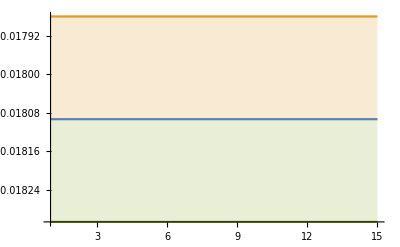

```mathematica
Plot[{fitData[[1]]//.Around[x_,y_]:>x,{fitData[[1]]//.Around[x_,y_]:>x+y,fitData[[1]]//.Around[x_,y_]:>x-y}},{x,1,15},Filling->{3->{1},2->{1}}]
```

```mathematica
SpoilHWFLOPlotN3=Show[Plot[{fitData[[1]]//.Around[x_,y_]:>x,{fitData[[1]]//.Around[x_,y_]:>x+y,fitData[[1]]//.Around[x_,y_]:>x-y}},{x,1,Length[meanErr2[[5]]]},Filling->{3->{1},2->{1}},PlotRange->{-.03,-0.005}],ListPlot[{Table[{τSteps[[1,i]],meanErr2[[1,i]]},{i,1,Length[meanErr2[[1]]]}],Table[{τSteps[[2,i]],meanErr2[[2,i]]},{i,1,Length[meanErr2[[2]]]}],Table[{τSteps[[3,i]],meanErr2[[3,i]]},{i,1,Length[meanErr2[[3]]]}],Table[{τSteps[[4,i]],meanErr2[[4,i]]},{i,1,Length[meanErr2[[4]]]}],Table[{τSteps[[5,i]],meanErr2[[5,i]]},{i,1,Length[meanErr2[[5]]]}]},PlotRange->{-.03,-0.005},PlotLegends->Placed[αLegendLO,{0.5,0.1}],PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]],markerlist[[4]],markerlist[[5]]},IntervalMarkersStyle->{ColorData[97][3]},PlotStyle->{ColorData[97][3]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau_{\\text{steps}}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]},PlotLabel->MaTeX["N=3\\text{ (LO)}",Magnification->1.2]]
```

-Graphics-

#### QCD NLO - gauss

```mathematica
Nf4α1LoopMid
Nf4α1LoopStepTab={380,380,380,380,380};
NWalkers=200;
Nf4α1LoopBig={0.229421,0.229421,0.229421,0.229421,0.229421};
aList={1,2,3,4,5};
```

{0.21556,0.220566,0.22639,0.233299,0.241701,0.252265,0.266178,0.285833}

```mathematica
csvData=Table[Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfgauss.csv"],{xx,1,Length[aList]}]
```

({mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.0693641643330093, -0.06943818123397666, -0.07490489073247346, -0.07638896067033293, -0.07723428473935377, -0.07168673639054764, -0.07142546420909666, -0.07259180868835154, -0.07125922717970629, -0.0745091231172119, -0.07133827835691883, -0.068763786211025, -0.06505910405150334, -0.06609360751741722, -0.06532213245607979, -0.06572667113706065, -0.06542819840124856, -0.07292639360266062, -0.0754023597736729, -0.07250079253341796, -0.06948784845926696, -0.06902321458046458, -0.06782872102942616, -0.07395263931377347, -0.07015454260874197, -0.07103775485068048, -0.07041520557947628, -0.07530764825223218, -0.07843209835328253, -0.07529465022668187, -0.07304658207473827, -0.07398156190415933, -0.07120773088791928, -0.06912298742473834, -0.0712133966464632],[0.006685153190448436, 0.008921034020381049, 0.016590746424884343, 0.02268858072409633, 0.03131905170455034, 0.02273335781292509, 0.025800564064662385, 0.031612458714357486, 0.03457314411883217, 0.040844446881412, 0.04197352405259228, 0.044595700002816145, 0.043619949423904576, 0.05183762414670061, 0.054441910666985, 0.0657379716542221, 0.0758897048426507, 0.12507044349587096, 0.20979749697182407, 0.17952743132684518, 0.16792387960788868, 0.18385577030192168, 0.20058526615050104, 0.2874587412484547, 0.28118326977822217, 0.3477159321178867, 0.41159583631638, 0.6115953607059238, 0.8565094114442662, 0.8877949883844378, 0.8961358734260094, 1.1334020211719387, 1.150887702803874, 1.3933088235428726, 1.5878200085258494],-0.0648839,0.000415788,0.596563}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.04560293350636883, -0.04588403414103044, -0.04627969828375076, -0.046605771227140345, -0.046781183220734074, -0.04650245688291457, -0.04707310617441039, -0.047305537832584676, -0.047369275297779054, -0.04716982892279302, -0.04907151604030724, -0.048642417058020485, -0.04775394528273799, -0.05068408748298731, -0.048885131489685665, -0.048960847404071, -0.04878205586682602, -0.05075186686387279, -0.05304390062079509, -0.051415184609730324, -0.050813712683374646, -0.050724754953271785, -0.05245568875395168, -0.05220979992685131, -0.0551633101579154, -0.05423947230691664, -0.05409197686524267, -0.05644884763635143, -0.056429044512688493, -0.05743479579918669, -0.0574366555527197, -0.05783700949691653, -0.06013375171605914, -0.058496496526089785, -0.06190348025254678],[0.0022218772862169123, 0.0026492202404583554, 0.0035792138675405463, 0.004269813191521817, 0.004731734800634531, 0.005350634812398805, 0.006269076535073336, 0.007418448835301789, 0.00838171580898632, 0.009256581934463598, 0.012182836401570406, 0.014102653484446137, 0.014093390620742545, 0.022616910783141958, 0.017709620494760252, 0.019922284427301058, 0.022983244307400875, 0.029295385127682302, 0.037356886080715836, 0.03948852230872384, 0.04450706708712266, 0.04948523185851104, 0.06346632631444765, 0.07403428568181077, 0.10872415177067447, 0.11552812466841306, 0.12630393323592298, 0.1653747079593589, 0.17819369274400035, 0.21811793062988002, 0.2564002258599235, 0.27311246283320645, 0.36495476961654766, 0.3573918563612567, 0.5011861269477598],-0.0443183,0.000642598,0.308347}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.036048309668988684, -0.03620085176647741, -0.03694954884968037, -0.03668392501188162, -0.03819922519336644, -0.03807865598948601, -0.03854728824691159, -0.0384376779811439, -0.03899473471649049, -0.03828292591123086, -0.039817486809531295, -0.04373419334329603, -0.038332829863611556, -0.04143969988226081, -0.039091533953578644, -0.0410061765833659, -0.03998097965837124, -0.04016979581532588, -0.04079748735201924, -0.040499167161500864, -0.04013305451884697, -0.04019839790251476, -0.040782981873663644, -0.04137108862361527, -0.04136373972982037, -0.0416112410045443, -0.041486686213922125, -0.042509769881293534, -0.043380677349992174, -0.04317565929912679, -0.04315396308537875, -0.043833670763602416, -0.043996807077304814, -0.04545896229661748, -0.04600706657656218],[0.002757787643030392, 0.0033112031817346703, 0.004675728718298151, 0.0046401098961767135, 0.007573500036053904, 0.007572064561399432, 0.008010890910793642, 0.00896163179610585, 0.010743780208390466, 0.010351369666853932, 0.01276376635926354, 0.021660023255887142, 0.01355071284172419, 0.01931694698399466, 0.016318120428749618, 0.021051312251406922, 0.019937931771781537, 0.02210317726294016, 0.025321709322016262, 0.02791316915391251, 0.029173933809886074, 0.030855702095501134, 0.03527106842648811, 0.03844358750652083, 0.04323612840373034, 0.05027482729715454, 0.05495701921471534, 0.06249676120426833, 0.07187748145517563, 0.07760925002553812, 0.08771565852659406, 0.10048696983359247, 0.11057478680496396, 0.13192689122909784, 0.14838329087681565],-0.0353562,0.000673805,0.183477}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.02767080362277423, -0.02769124605483095, -0.0278967454287188, -0.027667094777423712, -0.027665717968410445, -0.027889397245201036, -0.028058116785657696, -0.028257900573753623, -0.028379285591345203, -0.028165017550352354, -0.028988100950789138, -0.02895702472840685, -0.029326710615545492, -0.02925177296511722, -0.029641494232170006, -0.030329631101017294, -0.03079375597666388, -0.030910451758715412, -0.030987358047917128, -0.03149019741333182, -0.03335704795329853, -0.032569509343999374, -0.03371120885983474, -0.03400772756369185, -0.03322135729326279, -0.03345183682528713, -0.033386008298579434, -0.03503413290539308, -0.03468274085708753, -0.034574952909450896, -0.03466341275801996, -0.034831936350211805, -0.03577117917459278, -0.03596794691687938, -0.03656013705846822],[0.0014297379194955363, 0.0014690437218764449, 0.0016640758747671616, 0.0017644542031482128, 0.001890574832279303, 0.0021792090203965483, 0.0024157006378756904, 0.0027991874046401164, 0.003055353907243268, 0.0030450705270684275, 0.0038678110638673655, 0.004015573241565709, 0.004658243640902413, 0.004764274360427701, 0.005376160249959663, 0.0064329955717062764, 0.007201992178577881, 0.007962978616723546, 0.008791704239261119, 0.01038929632725678, 0.015842959715391382, 0.015512476762164055, 0.019649189846027374, 0.022649925601575197, 0.02159212835417634, 0.025075621008314723, 0.02587173430076809, 0.033838477740163866, 0.036462271593768934, 0.0385100576765599, 0.04129044826364441, 0.04518130366880053, 0.05101767167290222, 0.05830941538419631, 0.06687471064738226],-0.0266677,0.000551327,0.184469}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.02248831330990249, -0.02269218121360469, -0.022764972196943862, -0.022813587626420752, -0.022826441540424448, -0.022930588792722768, -0.02326447038914707, -0.023402258750258427, -0.02359485063374668, -0.02361076733064241, -0.02408732255417499, -0.024065709250424713, -0.02440614301948028, -0.02435756490834706, -0.024238982234104495, -0.024453317461711872, -0.02462490793539577, -0.02450175569144012, -0.024427428528729596, -0.02460686278137367, -0.02463890132776188, -0.0246959420344059, -0.02486455778728065, -0.02491167314035602, -0.024899738677136907, -0.024921661379732896, -0.02505091309892267, -0.02503653842827781, -0.02491677188529749, -0.025177395885344487, -0.025499681985855047, -0.025683350477017527, -0.026212738635826825, -0.026248838602351936, -0.026801114795201766],[0.0007849081212762229, 0.0008838899554365389, 0.0009772413745251498, 0.0010636833030152446, 0.0011354183493205786, 0.0012294807309404894, 0.0014299958060423326, 0.001603268599603264, 0.0017674579355041339, 0.0018969779433463433, 0.0022375406256902155, 0.002322561191595048, 0.0028348525398505797, 0.0029633627586248294, 0.0031490942291533823, 0.0035216644936786547, 0.0038296212815684674, 0.003862333384979326, 0.003992986077869322, 0.004491257215918142, 0.004969879461944346, 0.005174212936446872, 0.005713616407141222, 0.006114413666069962, 0.006473749814835109, 0.006943974178429878, 0.007605497894432547, 0.007987762840814755, 0.008490491726501273, 0.009303390584112324, 0.01016725736885306, 0.010991144143547562, 0.012438100557927791, 0.01336270946401508, 0.014905116798366848],-0.0216521,0.000405445,0.181431})

```mathematica
meanErr=Table[Table[csvData[[xx,2,yy]]//StringSplit[#,{",","[","]"}]&,{yy,1,2}],{xx,1,Length[aList]}]
```

({-0.0693641643330093, -0.06943818123397666, -0.07490489073247346, -0.07638896067033293, -0.07723428473935377, -0.07168673639054764, -0.07142546420909666, -0.07259180868835154, -0.07125922717970629, -0.0745091231172119, -0.07133827835691883, -0.068763786211025, -0.06505910405150334, -0.06609360751741722, -0.06532213245607979, -0.06572667113706065, -0.06542819840124856, -0.07292639360266062, -0.0754023597736729, -0.07250079253341796, -0.06948784845926696, -0.06902321458046458, -0.06782872102942616, -0.07395263931377347, -0.07015454260874197, -0.07103775485068048, -0.07041520557947628, -0.07530764825223218, -0.07843209835328253, -0.07529465022668187, -0.07304658207473827, -0.07398156190415933, -0.07120773088791928, -0.06912298742473834, -0.0712133966464632} | {0.006685153190448436, 0.008921034020381049, 0.016590746424884343, 0.02268858072409633, 0.03131905170455034, 0.02273335781292509, 0.025800564064662385, 0.031612458714357486, 0.03457314411883217, 0.040844446881412, 0.04197352405259228, 0.044595700002816145, 0.043619949423904576, 0.05183762414670061, 0.054441910666985, 0.0657379716542221, 0.0758897048426507, 0.12507044349587096, 0.20979749697182407, 0.17952743132684518, 0.16792387960788868, 0.18385577030192168, 0.20058526615050104, 0.2874587412484547, 0.28118326977822217, 0.3477159321178867, 0.41159583631638, 0.6115953607059238, 0.8565094114442662, 0.8877949883844378, 0.8961358734260094, 1.1334020211719387, 1.150887702803874, 1.3933088235428726, 1.5878200085258494}
{-0.04560293350636883, -0.04588403414103044, -0.04627969828375076, -0.046605771227140345, -0.046781183220734074, -0.04650245688291457, -0.04707310617441039, -0.047305537832584676, -0.047369275297779054, -0.04716982892279302, -0.04907151604030724, -0.048642417058020485, -0.04775394528273799, -0.05068408748298731, -0.048885131489685665, -0.048960847404071, -0.04878205586682602, -0.05075186686387279, -0.05304390062079509, -0.051415184609730324, -0.050813712683374646, -0.050724754953271785, -0.05245568875395168, -0.05220979992685131, -0.0551633101579154, -0.05423947230691664, -0.05409197686524267, -0.05644884763635143, -0.056429044512688493, -0.05743479579918669, -0.0574366555527197, -0.05783700949691653, -0.06013375171605914, -0.058496496526089785, -0.06190348025254678} | {0.0022218772862169123, 0.0026492202404583554, 0.0035792138675405463, 0.004269813191521817, 0.004731734800634531, 0.005350634812398805, 0.006269076535073336, 0.007418448835301789, 0.00838171580898632, 0.009256581934463598, 0.012182836401570406, 0.014102653484446137, 0.014093390620742545, 0.022616910783141958, 0.017709620494760252, 0.019922284427301058, 0.022983244307400875, 0.029295385127682302, 0.037356886080715836, 0.03948852230872384, 0.04450706708712266, 0.04948523185851104, 0.06346632631444765, 0.07403428568181077, 0.10872415177067447, 0.11552812466841306, 0.12630393323592298, 0.1653747079593589, 0.17819369274400035, 0.21811793062988002, 0.2564002258599235, 0.27311246283320645, 0.36495476961654766, 0.3573918563612567, 0.5011861269477598}
{-0.036048309668988684, -0.03620085176647741, -0.03694954884968037, -0.03668392501188162, -0.03819922519336644, -0.03807865598948601, -0.03854728824691159, -0.0384376779811439, -0.03899473471649049, -0.03828292591123086, -0.039817486809531295, -0.04373419334329603, -0.038332829863611556, -0.04143969988226081, -0.039091533953578644, -0.0410061765833659, -0.03998097965837124, -0.04016979581532588, -0.04079748735201924, -0.040499167161500864, -0.04013305451884697, -0.04019839790251476, -0.040782981873663644, -0.04137108862361527, -0.04136373972982037, -0.0416112410045443, -0.041486686213922125, -0.042509769881293534, -0.043380677349992174, -0.04317565929912679, -0.04315396308537875, -0.043833670763602416, -0.043996807077304814, -0.04545896229661748, -0.04600706657656218} | {0.002757787643030392, 0.0033112031817346703, 0.004675728718298151, 0.0046401098961767135, 0.007573500036053904, 0.007572064561399432, 0.008010890910793642, 0.00896163179610585, 0.010743780208390466, 0.010351369666853932, 0.01276376635926354, 0.021660023255887142, 0.01355071284172419, 0.01931694698399466, 0.016318120428749618, 0.021051312251406922, 0.019937931771781537, 0.02210317726294016, 0.025321709322016262, 0.02791316915391251, 0.029173933809886074, 0.030855702095501134, 0.03527106842648811, 0.03844358750652083, 0.04323612840373034, 0.05027482729715454, 0.05495701921471534, 0.06249676120426833, 0.07187748145517563, 0.07760925002553812, 0.08771565852659406, 0.10048696983359247, 0.11057478680496396, 0.13192689122909784, 0.14838329087681565}
{-0.02767080362277423, -0.02769124605483095, -0.0278967454287188, -0.027667094777423712, -0.027665717968410445, -0.027889397245201036, -0.028058116785657696, -0.028257900573753623, -0.028379285591345203, -0.028165017550352354, -0.028988100950789138, -0.02895702472840685, -0.029326710615545492, -0.02925177296511722, -0.029641494232170006, -0.030329631101017294, -0.03079375597666388, -0.030910451758715412, -0.030987358047917128, -0.03149019741333182, -0.03335704795329853, -0.032569509343999374, -0.03371120885983474, -0.03400772756369185, -0.03322135729326279, -0.03345183682528713, -0.033386008298579434, -0.03503413290539308, -0.03468274085708753, -0.034574952909450896, -0.03466341275801996, -0.034831936350211805, -0.03577117917459278, -0.03596794691687938, -0.03656013705846822} | {0.0014297379194955363, 0.0014690437218764449, 0.0016640758747671616, 0.0017644542031482128, 0.001890574832279303, 0.0021792090203965483, 0.0024157006378756904, 0.0027991874046401164, 0.003055353907243268, 0.0030450705270684275, 0.0038678110638673655, 0.004015573241565709, 0.004658243640902413, 0.004764274360427701, 0.005376160249959663, 0.0064329955717062764, 0.007201992178577881, 0.007962978616723546, 0.008791704239261119, 0.01038929632725678, 0.015842959715391382, 0.015512476762164055, 0.019649189846027374, 0.022649925601575197, 0.02159212835417634, 0.025075621008314723, 0.02587173430076809, 0.033838477740163866, 0.036462271593768934, 0.0385100576765599, 0.04129044826364441, 0.04518130366880053, 0.05101767167290222, 0.05830941538419631, 0.06687471064738226}
{-0.02248831330990249, -0.02269218121360469, -0.022764972196943862, -0.022813587626420752, -0.022826441540424448, -0.022930588792722768, -0.02326447038914707, -0.023402258750258427, -0.02359485063374668, -0.02361076733064241, -0.02408732255417499, -0.024065709250424713, -0.02440614301948028, -0.02435756490834706, -0.024238982234104495, -0.024453317461711872, -0.02462490793539577, -0.02450175569144012, -0.024427428528729596, -0.02460686278137367, -0.02463890132776188, -0.0246959420344059, -0.02486455778728065, -0.02491167314035602, -0.024899738677136907, -0.024921661379732896, -0.02505091309892267, -0.02503653842827781, -0.02491677188529749, -0.025177395885344487, -0.025499681985855047, -0.025683350477017527, -0.026212738635826825, -0.026248838602351936, -0.026801114795201766} | {0.0007849081212762229, 0.0008838899554365389, 0.0009772413745251498, 0.0010636833030152446, 0.0011354183493205786, 0.0012294807309404894, 0.0014299958060423326, 0.001603268599603264, 0.0017674579355041339, 0.0018969779433463433, 0.0022375406256902155, 0.002322561191595048, 0.0028348525398505797, 0.0029633627586248294, 0.0031490942291533823, 0.0035216644936786547, 0.0038296212815684674, 0.003862333384979326, 0.003992986077869322, 0.004491257215918142, 0.004969879461944346, 0.005174212936446872, 0.005713616407141222, 0.006114413666069962, 0.006473749814835109, 0.006943974178429878, 0.007605497894432547, 0.007987762840814755, 0.008490491726501273, 0.009303390584112324, 0.01016725736885306, 0.010991144143547562, 0.012438100557927791, 0.01336270946401508, 0.014905116798366848})

```mathematica
meanErr[[1,2,1]]//ToExpression
```

0.00668515

```mathematica
meanErr[[1]]
```

(-0.0693641643330093 |  -0.06943818123397666 |  -0.07490489073247346 |  -0.07638896067033293 |  -0.07723428473935377 |  -0.07168673639054764 |  -0.07142546420909666 |  -0.07259180868835154 |  -0.07125922717970629 |  -0.0745091231172119 |  -0.07133827835691883 |  -0.068763786211025 |  -0.06505910405150334 |  -0.06609360751741722 |  -0.06532213245607979 |  -0.06572667113706065 |  -0.06542819840124856 |  -0.07292639360266062 |  -0.0754023597736729 |  -0.07250079253341796 |  -0.06948784845926696 |  -0.06902321458046458 |  -0.06782872102942616 |  -0.07395263931377347 |  -0.07015454260874197 |  -0.07103775485068048 |  -0.07041520557947628 |  -0.07530764825223218 |  -0.07843209835328253 |  -0.07529465022668187 |  -0.07304658207473827 |  -0.07398156190415933 |  -0.07120773088791928 |  -0.06912298742473834 |  -0.0712133966464632
0.006685153190448436 |  0.008921034020381049 |  0.016590746424884343 |  0.02268858072409633 |  0.03131905170455034 |  0.02273335781292509 |  0.025800564064662385 |  0.031612458714357486 |  0.03457314411883217 |  0.040844446881412 |  0.04197352405259228 |  0.044595700002816145 |  0.043619949423904576 |  0.05183762414670061 |  0.054441910666985 |  0.0657379716542221 |  0.0758897048426507 |  0.12507044349587096 |  0.20979749697182407 |  0.17952743132684518 |  0.16792387960788868 |  0.18385577030192168 |  0.20058526615050104 |  0.2874587412484547 |  0.28118326977822217 |  0.3477159321178867 |  0.41159583631638 |  0.6115953607059238 |  0.8565094114442662 |  0.8877949883844378 |  0.8961358734260094 |  1.1334020211719387 |  1.150887702803874 |  1.3933088235428726 |  1.5878200085258494)

```mathematica
meanErr2=Table[Table[Around[meanErr[[xx,1,yy]]//ToExpression,meanErr[[xx,2,yy]]//ToExpression],{yy,1,Length[meanErr[[xx,1]]]}],{xx,1,Length[aList]}]
```

(-0.0690.007 | -0.0690.009 | -0.0750.017 | -0.0760.023 | -0.0770.031 | -0.0720.023 | -0.0710.026 | -0.0730.032 | -0.0710.035 | -0.070.04 | -0.070.04 | -0.070.04 | -0.070.04 | -0.070.05 | -0.070.05 | -0.070.07 | -0.070.08 | -0.070.13 | -0.080.21 | -0.070.18 | -0.070.17 | -0.070.18 | -0.070.20 | -0.070.29 | -0.070.28 | -0.070.35 | 0.00.4 | 0.00.6 | 0.00.9 | 0.00.9 | 0.00.9 | 0.01.1 | 0.01.2 | 0.01.4 | 0.01.6
-0.04560.0022 | -0.04590.0026 | -0.0460.004 | -0.0470.004 | -0.0470.005 | -0.0470.005 | -0.0470.006 | -0.0470.007 | -0.0470.008 | -0.0470.009 | -0.0490.012 | -0.0490.014 | -0.0480.014 | -0.0510.023 | -0.0490.018 | -0.0490.020 | -0.0490.023 | -0.0510.029 | -0.050.04 | -0.050.04 | -0.050.04 | -0.050.05 | -0.050.06 | -0.050.07 | -0.060.11 | -0.050.12 | -0.050.13 | -0.060.17 | -0.060.18 | -0.060.22 | -0.060.26 | -0.060.27 | 0.00.4 | 0.00.4 | 0.00.5
-0.03600.0028 | -0.03620.0033 | -0.0370.005 | -0.0370.005 | -0.0380.008 | -0.0380.008 | -0.0390.008 | -0.0380.009 | -0.0390.011 | -0.0380.010 | -0.0400.013 | -0.0440.022 | -0.0380.014 | -0.0410.019 | -0.0390.016 | -0.0410.021 | -0.0400.020 | -0.0400.022 | -0.0410.025 | -0.0400.028 | -0.0400.029 | -0.0400.031 | -0.0410.035 | -0.040.04 | -0.040.04 | -0.040.05 | -0.040.05 | -0.040.06 | -0.040.07 | -0.040.08 | -0.040.09 | -0.040.10 | -0.040.11 | -0.050.13 | -0.050.15
-0.02770.0014 | -0.02770.0015 | -0.02790.0017 | -0.02770.0018 | -0.02770.0019 | -0.02790.0022 | -0.02810.0024 | -0.02830.0028 | -0.02840.0031 | -0.02820.0030 | -0.0290.004 | -0.0290.004 | -0.0290.005 | -0.0290.005 | -0.0300.005 | -0.0300.006 | -0.0310.007 | -0.0310.008 | -0.0310.009 | -0.0310.010 | -0.0330.016 | -0.0330.016 | -0.0340.020 | -0.0340.023 | -0.0330.022 | -0.0330.025 | -0.0330.026 | -0.0350.034 | -0.030.04 | -0.030.04 | -0.030.04 | -0.030.05 | -0.040.05 | -0.040.06 | -0.040.07
-0.02250.0008 | -0.02270.0009 | -0.02280.0010 | -0.02280.0011 | -0.02280.0011 | -0.02290.0012 | -0.02330.0014 | -0.02340.0016 | -0.02360.0018 | -0.02360.0019 | -0.02410.0022 | -0.02410.0023 | -0.02440.0028 | -0.02440.0030 | -0.02420.0031 | -0.02450.0035 | -0.0250.004 | -0.0250.004 | -0.0240.004 | -0.0250.004 | -0.0250.005 | -0.0250.005 | -0.0250.006 | -0.0250.006 | -0.0250.006 | -0.0250.007 | -0.0250.008 | -0.0250.008 | -0.0250.008 | -0.0250.009 | -0.0250.010 | -0.0260.011 | -0.0260.012 | -0.0260.013 | -0.0270.015)

```mathematica
τSteps=Table[Table[xx,{xx,1,Length[meanErr2[[yy]]]}],{yy,1,Length[meanErr2]}]
```

(1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35)

```mathematica
fitData=Table[Around[Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfgauss.csv"][[2,3]],Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfgauss.csv"][[2,4]]],{xx,1,Length[aList]}]
```

{-0.06490.0004,-0.04430.0006,-0.03540.0007,-0.02670.0006,-0.02170.0004}

```mathematica
αLegendLO=PointLegend[Table[Directive[ColorData[97][1]],{ii,5}],{MaTeX["a=1",Magnification->0.8],MaTeX["a=2",Magnification->0.8],MaTeX["a=3",Magnification->0.8],MaTeX["a=4",Magnification->0.8],MaTeX["a=5",Magnification->0.8]},LegendMarkers->Table[Style[markerlist[[ii]],14,Bold,ColorData[97][3]],{ii,5}],LegendLayout->"Row",LegendMargins->0.5,LegendFunction->frame]
```

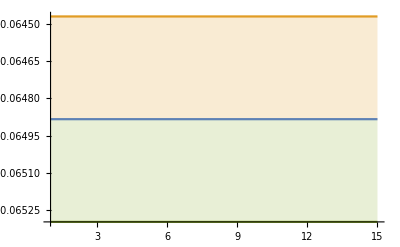

```mathematica
Plot[{fitData[[1]]//.Around[x_,y_]:>x,{fitData[[1]]//.Around[x_,y_]:>x+y,fitData[[1]]//.Around[x_,y_]:>x-y}},{x,1,15},Filling->{3->{1},2->{1}}]
```

```mathematica
SpoilHWFLOPlotN3=Show[Plot[{fitData[[1]]//.Around[x_,y_]:>x,{fitData[[1]]//.Around[x_,y_]:>x+y,fitData[[1]]//.Around[x_,y_]:>x-y}},{x,1,Length[meanErr2[[5]]]},Filling->{3->{1},2->{1}},PlotRange->{-.5,.1}],ListPlot[{Table[{τSteps[[1,i]],meanErr2[[1,i]]},{i,1,Length[meanErr2[[1]]]}],Table[{τSteps[[2,i]],meanErr2[[2,i]]},{i,1,Length[meanErr2[[2]]]}],Table[{τSteps[[3,i]],meanErr2[[3,i]]},{i,1,Length[meanErr2[[3]]]}],Table[{τSteps[[4,i]],meanErr2[[4,i]]},{i,1,Length[meanErr2[[4]]]}],Table[{τSteps[[5,i]],meanErr2[[5,i]]},{i,1,Length[meanErr2[[5]]]}]},PlotRange->{-.03,-0.005},PlotLegends->Placed[αLegendLO,{0.5,0.1}],PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]],markerlist[[4]],markerlist[[5]]},IntervalMarkersStyle->{ColorData[97][3]},PlotStyle->{ColorData[97][3]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau_{\\text{steps}}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]},PlotLabel->MaTeX["N=3(\\text{LO})",Magnification->1.2]]
```

-Graphics-

#### QCD mNLO - gauss

```mathematica
Nf4α1LoopMid
Nf4α1LoopStepTab={380,380,380,380,380};
NWalkers=200;
Nf4α1LoopBig={0.229421,0.229421,0.229421,0.229421,0.229421};
aList={1,2,3,4,5};
```

{0.21556,0.220566,0.22639,0.233299,0.241701,0.252265,0.266178,0.285833}

```mathematica
csvData=Table[Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfgauss.csv"],{xx,1,Length[aList]}]
```

({mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.07960025139718764, -0.08289319985794698, -0.109655028284922, -0.1054615986993136, -0.11303327307300344, -0.08470041218719124, -0.08413150275151385, -0.08604827270990363, -0.08010650971357389, -0.08569577132314275, -0.07972128734744129, -0.0759522513126603, -0.06913767435039964, -0.07092091188896282, -0.06931139646602497, -0.07083856414266815, -0.06997153864328073, -0.08892850909853038, -0.09497133132815118, -0.0915305927548347, -0.07668262966630716, -0.07521418374990975, -0.07257595864535493, -0.08160201868513664, -0.07534290818848047, -0.07592799511213898, -0.07716470582127705, -0.08742928843343269, -0.09648206061426987, -0.10046529764332256, -0.08209691570970469, -0.08655124333982715, -0.07794058700694209, -0.08144706447149716, -0.0796381247373081],[0.015254666231152118, 0.025092829268501114, 0.0817573369349542, 0.09677991748921894, 0.17894510748392553, 0.09247492019580052, 0.1120653252959577, 0.12058454866231141, 0.12681828702187603, 0.15516457157906738, 0.15198336159490217, 0.16341927305758447, 0.16111254610707393, 0.18523798891715876, 0.2048312397638823, 0.2655662588548385, 0.28580430363191334, 0.5471777330330005, 0.9500842693702676, 0.9219179581776202, 0.5992317745786542, 0.6426297457315405, 0.6764762000387275, 0.9241724982149563, 0.9308466307107257, 1.0961145884927779, 1.409004321742523, 2.256458784506601, 3.8562898385975326, 6.694952519221411, 3.9574640546137347, 5.321503145400916, 5.110252077726889, 7.333028970384845, 7.925771007031294],-0.0717874,0.00054319,0.51602}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.04709542754360264, -0.047426120520503455, -0.04796964198770404, -0.04845847629028929, -0.04859292062287313, -0.048216925635035955, -0.04888150453232374, -0.049223268640697045, -0.04925919696804587, -0.04905434477331362, -0.05137574133526611, -0.05092477979459588, -0.0498267595884633, -0.05886135570914675, -0.05123043389866583, -0.05132445980007589, -0.05094265072969397, -0.05340944108960455, -0.05961566019091622, -0.0549041734821338, -0.05378569004943418, -0.054777869419195886, -0.05643224432893924, -0.0563259846962185, -0.06084005241397829, -0.05841060745671914, -0.05805488186090325, -0.060993677673325315, -0.06076965572566526, -0.06217001048213506, -0.062109748949024754, -0.06250718408596363, -0.06656528240146195, -0.06277577732699599, -0.06818505907616108],[0.0025070029273745677, 0.0030146503229383954, 0.004222456499317088, 0.005177294420128649, 0.005603163887584577, 0.0063306193158318945, 0.0074352316190002075, 0.008872865938487393, 0.01005346966584569, 0.011174909570934245, 0.014938487075858398, 0.01753439114997357, 0.017406738011471433, 0.054869727949871494, 0.022603018604266976, 0.025374314227593536, 0.029060809771340044, 0.037778607798741565, 0.06382073826080732, 0.0539258411674037, 0.059247335381685265, 0.07345280271818845, 0.09048403624930844, 0.10865021902312055, 0.17465063408374928, 0.17191401822963803, 0.18555945013694594, 0.2509447145773128, 0.26764118038656703, 0.3312329431123157, 0.39421857655766424, 0.41653960865967, 0.6086934648325277, 0.5446640241980386, 0.8203314254622612],-0.0461098,0.000705393,0.338601}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.037104596542103865, -0.03730910075282203, -0.038383615205033285, -0.03793863842513445, -0.04027839562515342, -0.03991284257092772, -0.040325682645129556, -0.040210033632007966, -0.04093098660505195, -0.039863173361687695, -0.04185739535691986, -0.05465031427135551, -0.04009744536060972, -0.054078019737913215, -0.04103561767819281, -0.04432930586773575, -0.042151346649032466, -0.042117290906532115, -0.04286835408063572, -0.04238414393707533, -0.04182827832581847, -0.04179287575491873, -0.04242932211540284, -0.04344508518382944, -0.043269817290680204, -0.04332311141989339, -0.043189524326087934, -0.04427569907760279, -0.045451962621187246, -0.04502687742747502, -0.04486011785476233, -0.04559946845324462, -0.045669238178227684, -0.047377784546624245, -0.048058349824604794],[0.00327576926634928, 0.003990735360136256, 0.005902690549196208, 0.005772176324864712, 0.010421698654945423, 0.010203075415440903, 0.01060566543393612, 0.011944060816874155, 0.014650960333380448, 0.013773324598299153, 0.01716098705350775, 0.05087840432411954, 0.018606212102849486, 0.05901505052562974, 0.02245934499563666, 0.032093041958123264, 0.027776621140014966, 0.030322591769122637, 0.034939500526793246, 0.038368657338808315, 0.039911502057248444, 0.04177040611011698, 0.047574605889283694, 0.05251914936032718, 0.058455448552825036, 0.06658302955779759, 0.07380856818232306, 0.08321058935032037, 0.09689267506873546, 0.10271588460318026, 0.11559941021457745, 0.13192326754892839, 0.14446220097246673, 0.17250989321481472, 0.19500299700974957],-0.0366524,0.000718349,0.203662}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.028173783628738413, -0.028143471879902453, -0.028365208643630707, -0.02811550905754219, -0.028110046464025422, -0.028350349738194152, -0.028535469222386665, -0.028766858675039756, -0.028895418952099225, -0.02863990816293568, -0.02954698655898138, -0.029534789419887828, -0.03004152596556504, -0.029863618846039504, -0.030300270779270208, -0.03113028571710378, -0.031622164179955184, -0.03174201333058938, -0.03185732456981279, -0.03248368904736544, -0.03532305163734391, -0.034074787203925525, -0.03564342088132604, -0.03611854774435228, -0.034788001686331185, -0.03515599503746751, -0.03489044011071018, -0.03707840402640255, -0.03659019438284943, -0.036288061744344416, -0.0362982515445707, -0.036423658508597585, -0.037453952241305974, -0.03773255105081581, -0.03848620618869871],[0.0015852015015657252, 0.0015898607039468067, 0.001800928468211056, 0.0019116750470218348, 0.0020435530320736337, 0.002358128189418524, 0.002618646628171749, 0.0030624867193863943, 0.0033439231532185983, 0.003304844448123764, 0.00424668973601574, 0.0044245126247535555, 0.005310443148228208, 0.005299378053415996, 0.006030915846800983, 0.007389486913555785, 0.008174332538520158, 0.009060544837942825, 0.010123512402419025, 0.012132773612240993, 0.020824245657300816, 0.01987116711446322, 0.026008214384748523, 0.03083283342167587, 0.028138489330810545, 0.0331048944761062, 0.03347698278564657, 0.04546549343618762, 0.048721136229658873, 0.050424630007089806, 0.053911439909770244, 0.05857533107343944, 0.06573677610260241, 0.07605668604340166, 0.08755385071679302],-0.0270735,0.000579472,0.18366}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.022696265421939088, -0.022910295331718553, -0.0229886194057646, -0.023042283937486023, -0.023054194575444404, -0.023162598725997, -0.023523228687956095, -0.023676225798404678, -0.02387771061097995, -0.023895966796206754, -0.024422739809446436, -0.024383719218196848, -0.024794169651233763, -0.02472302044628596, -0.024594000218341256, -0.024832559218559445, -0.02502064877799502, -0.02485774321427306, -0.024766604843070493, -0.024963185112283612, -0.025016404882928528, -0.02505829173620133, -0.02524734052764177, -0.025293938594068335, -0.02527055772346594, -0.02529821530271344, -0.025434882157001838, -0.025404747121597522, -0.025279562431668682, -0.02555505405922117, -0.025896474362879465, -0.026087681891028416, -0.026655985931308045, -0.026697845663348013, -0.027295296588919597],[0.0008064217500500185, 0.0009097664333332355, 0.0010073168117960198, 0.001098814722834642, 0.0011725167017177566, 0.0012701208737783258, 0.0014851732899309402, 0.0016758391523485788, 0.0018495524694618216, 0.0019884358637996488, 0.002382639190782505, 0.0024535760699043695, 0.0030826028109752885, 0.0031937733126039614, 0.0033995846342405964, 0.0038332532002816147, 0.004187721974842774, 0.0041602752496849495, 0.0042873248111606746, 0.004842818485778782, 0.005419051469604384, 0.005605418464275297, 0.006231660481172505, 0.0066433288448777385, 0.006984791888479432, 0.0075027427125247724, 0.008214018028538992, 0.008609383708371906, 0.009146005038476809, 0.010020776715040683, 0.010955286447851811, 0.011839442062225217, 0.013438479395353866, 0.014470890621646021, 0.016164806886459996],-0.0218578,0.000417859,0.174588})

```mathematica
meanErr=Table[Table[csvData[[xx,2,yy]]//StringSplit[#,{",","[","]"}]&,{yy,1,2}],{xx,1,Length[aList]}]
```

({-0.07960025139718764, -0.08289319985794698, -0.109655028284922, -0.1054615986993136, -0.11303327307300344, -0.08470041218719124, -0.08413150275151385, -0.08604827270990363, -0.08010650971357389, -0.08569577132314275, -0.07972128734744129, -0.0759522513126603, -0.06913767435039964, -0.07092091188896282, -0.06931139646602497, -0.07083856414266815, -0.06997153864328073, -0.08892850909853038, -0.09497133132815118, -0.0915305927548347, -0.07668262966630716, -0.07521418374990975, -0.07257595864535493, -0.08160201868513664, -0.07534290818848047, -0.07592799511213898, -0.07716470582127705, -0.08742928843343269, -0.09648206061426987, -0.10046529764332256, -0.08209691570970469, -0.08655124333982715, -0.07794058700694209, -0.08144706447149716, -0.0796381247373081} | {0.015254666231152118, 0.025092829268501114, 0.0817573369349542, 0.09677991748921894, 0.17894510748392553, 0.09247492019580052, 0.1120653252959577, 0.12058454866231141, 0.12681828702187603, 0.15516457157906738, 0.15198336159490217, 0.16341927305758447, 0.16111254610707393, 0.18523798891715876, 0.2048312397638823, 0.2655662588548385, 0.28580430363191334, 0.5471777330330005, 0.9500842693702676, 0.9219179581776202, 0.5992317745786542, 0.6426297457315405, 0.6764762000387275, 0.9241724982149563, 0.9308466307107257, 1.0961145884927779, 1.409004321742523, 2.256458784506601, 3.8562898385975326, 6.694952519221411, 3.9574640546137347, 5.321503145400916, 5.110252077726889, 7.333028970384845, 7.925771007031294}
{-0.04709542754360264, -0.047426120520503455, -0.04796964198770404, -0.04845847629028929, -0.04859292062287313, -0.048216925635035955, -0.04888150453232374, -0.049223268640697045, -0.04925919696804587, -0.04905434477331362, -0.05137574133526611, -0.05092477979459588, -0.0498267595884633, -0.05886135570914675, -0.05123043389866583, -0.05132445980007589, -0.05094265072969397, -0.05340944108960455, -0.05961566019091622, -0.0549041734821338, -0.05378569004943418, -0.054777869419195886, -0.05643224432893924, -0.0563259846962185, -0.06084005241397829, -0.05841060745671914, -0.05805488186090325, -0.060993677673325315, -0.06076965572566526, -0.06217001048213506, -0.062109748949024754, -0.06250718408596363, -0.06656528240146195, -0.06277577732699599, -0.06818505907616108} | {0.0025070029273745677, 0.0030146503229383954, 0.004222456499317088, 0.005177294420128649, 0.005603163887584577, 0.0063306193158318945, 0.0074352316190002075, 0.008872865938487393, 0.01005346966584569, 0.011174909570934245, 0.014938487075858398, 0.01753439114997357, 0.017406738011471433, 0.054869727949871494, 0.022603018604266976, 0.025374314227593536, 0.029060809771340044, 0.037778607798741565, 0.06382073826080732, 0.0539258411674037, 0.059247335381685265, 0.07345280271818845, 0.09048403624930844, 0.10865021902312055, 0.17465063408374928, 0.17191401822963803, 0.18555945013694594, 0.2509447145773128, 0.26764118038656703, 0.3312329431123157, 0.39421857655766424, 0.41653960865967, 0.6086934648325277, 0.5446640241980386, 0.8203314254622612}
{-0.037104596542103865, -0.03730910075282203, -0.038383615205033285, -0.03793863842513445, -0.04027839562515342, -0.03991284257092772, -0.040325682645129556, -0.040210033632007966, -0.04093098660505195, -0.039863173361687695, -0.04185739535691986, -0.05465031427135551, -0.04009744536060972, -0.054078019737913215, -0.04103561767819281, -0.04432930586773575, -0.042151346649032466, -0.042117290906532115, -0.04286835408063572, -0.04238414393707533, -0.04182827832581847, -0.04179287575491873, -0.04242932211540284, -0.04344508518382944, -0.043269817290680204, -0.04332311141989339, -0.043189524326087934, -0.04427569907760279, -0.045451962621187246, -0.04502687742747502, -0.04486011785476233, -0.04559946845324462, -0.045669238178227684, -0.047377784546624245, -0.048058349824604794} | {0.00327576926634928, 0.003990735360136256, 0.005902690549196208, 0.005772176324864712, 0.010421698654945423, 0.010203075415440903, 0.01060566543393612, 0.011944060816874155, 0.014650960333380448, 0.013773324598299153, 0.01716098705350775, 0.05087840432411954, 0.018606212102849486, 0.05901505052562974, 0.02245934499563666, 0.032093041958123264, 0.027776621140014966, 0.030322591769122637, 0.034939500526793246, 0.038368657338808315, 0.039911502057248444, 0.04177040611011698, 0.047574605889283694, 0.05251914936032718, 0.058455448552825036, 0.06658302955779759, 0.07380856818232306, 0.08321058935032037, 0.09689267506873546, 0.10271588460318026, 0.11559941021457745, 0.13192326754892839, 0.14446220097246673, 0.17250989321481472, 0.19500299700974957}
{-0.028173783628738413, -0.028143471879902453, -0.028365208643630707, -0.02811550905754219, -0.028110046464025422, -0.028350349738194152, -0.028535469222386665, -0.028766858675039756, -0.028895418952099225, -0.02863990816293568, -0.02954698655898138, -0.029534789419887828, -0.03004152596556504, -0.029863618846039504, -0.030300270779270208, -0.03113028571710378, -0.031622164179955184, -0.03174201333058938, -0.03185732456981279, -0.03248368904736544, -0.03532305163734391, -0.034074787203925525, -0.03564342088132604, -0.03611854774435228, -0.034788001686331185, -0.03515599503746751, -0.03489044011071018, -0.03707840402640255, -0.03659019438284943, -0.036288061744344416, -0.0362982515445707, -0.036423658508597585, -0.037453952241305974, -0.03773255105081581, -0.03848620618869871} | {0.0015852015015657252, 0.0015898607039468067, 0.001800928468211056, 0.0019116750470218348, 0.0020435530320736337, 0.002358128189418524, 0.002618646628171749, 0.0030624867193863943, 0.0033439231532185983, 0.003304844448123764, 0.00424668973601574, 0.0044245126247535555, 0.005310443148228208, 0.005299378053415996, 0.006030915846800983, 0.007389486913555785, 0.008174332538520158, 0.009060544837942825, 0.010123512402419025, 0.012132773612240993, 0.020824245657300816, 0.01987116711446322, 0.026008214384748523, 0.03083283342167587, 0.028138489330810545, 0.0331048944761062, 0.03347698278564657, 0.04546549343618762, 0.048721136229658873, 0.050424630007089806, 0.053911439909770244, 0.05857533107343944, 0.06573677610260241, 0.07605668604340166, 0.08755385071679302}
{-0.022696265421939088, -0.022910295331718553, -0.0229886194057646, -0.023042283937486023, -0.023054194575444404, -0.023162598725997, -0.023523228687956095, -0.023676225798404678, -0.02387771061097995, -0.023895966796206754, -0.024422739809446436, -0.024383719218196848, -0.024794169651233763, -0.02472302044628596, -0.024594000218341256, -0.024832559218559445, -0.02502064877799502, -0.02485774321427306, -0.024766604843070493, -0.024963185112283612, -0.025016404882928528, -0.02505829173620133, -0.02524734052764177, -0.025293938594068335, -0.02527055772346594, -0.02529821530271344, -0.025434882157001838, -0.025404747121597522, -0.025279562431668682, -0.02555505405922117, -0.025896474362879465, -0.026087681891028416, -0.026655985931308045, -0.026697845663348013, -0.027295296588919597} | {0.0008064217500500185, 0.0009097664333332355, 0.0010073168117960198, 0.001098814722834642, 0.0011725167017177566, 0.0012701208737783258, 0.0014851732899309402, 0.0016758391523485788, 0.0018495524694618216, 0.0019884358637996488, 0.002382639190782505, 0.0024535760699043695, 0.0030826028109752885, 0.0031937733126039614, 0.0033995846342405964, 0.0038332532002816147, 0.004187721974842774, 0.0041602752496849495, 0.0042873248111606746, 0.004842818485778782, 0.005419051469604384, 0.005605418464275297, 0.006231660481172505, 0.0066433288448777385, 0.006984791888479432, 0.0075027427125247724, 0.008214018028538992, 0.008609383708371906, 0.009146005038476809, 0.010020776715040683, 0.010955286447851811, 0.011839442062225217, 0.013438479395353866, 0.014470890621646021, 0.016164806886459996})

```mathematica
meanErr[[1,2,1]]//ToExpression
```

0.0152547

```mathematica
meanErr[[1]]
```

(-0.07960025139718764 |  -0.08289319985794698 |  -0.109655028284922 |  -0.1054615986993136 |  -0.11303327307300344 |  -0.08470041218719124 |  -0.08413150275151385 |  -0.08604827270990363 |  -0.08010650971357389 |  -0.08569577132314275 |  -0.07972128734744129 |  -0.0759522513126603 |  -0.06913767435039964 |  -0.07092091188896282 |  -0.06931139646602497 |  -0.07083856414266815 |  -0.06997153864328073 |  -0.08892850909853038 |  -0.09497133132815118 |  -0.0915305927548347 |  -0.07668262966630716 |  -0.07521418374990975 |  -0.07257595864535493 |  -0.08160201868513664 |  -0.07534290818848047 |  -0.07592799511213898 |  -0.07716470582127705 |  -0.08742928843343269 |  -0.09648206061426987 |  -0.10046529764332256 |  -0.08209691570970469 |  -0.08655124333982715 |  -0.07794058700694209 |  -0.08144706447149716 |  -0.0796381247373081
0.015254666231152118 |  0.025092829268501114 |  0.0817573369349542 |  0.09677991748921894 |  0.17894510748392553 |  0.09247492019580052 |  0.1120653252959577 |  0.12058454866231141 |  0.12681828702187603 |  0.15516457157906738 |  0.15198336159490217 |  0.16341927305758447 |  0.16111254610707393 |  0.18523798891715876 |  0.2048312397638823 |  0.2655662588548385 |  0.28580430363191334 |  0.5471777330330005 |  0.9500842693702676 |  0.9219179581776202 |  0.5992317745786542 |  0.6426297457315405 |  0.6764762000387275 |  0.9241724982149563 |  0.9308466307107257 |  1.0961145884927779 |  1.409004321742523 |  2.256458784506601 |  3.8562898385975326 |  6.694952519221411 |  3.9574640546137347 |  5.321503145400916 |  5.110252077726889 |  7.333028970384845 |  7.925771007031294)

```mathematica
meanErr2=Table[Table[Around[meanErr[[xx,1,yy]]//ToExpression,meanErr[[xx,2,yy]]//ToExpression],{yy,1,Length[meanErr[[xx,1]]]}],{xx,1,Length[aList]}]
```

(-0.0800.015 | -0.0830.025 | -0.110.08 | -0.110.10 | -0.110.18 | -0.080.09 | -0.080.11 | -0.090.12 | -0.080.13 | -0.090.16 | -0.080.15 | -0.080.16 | -0.070.16 | -0.070.19 | -0.070.20 | -0.070.27 | -0.070.29 | 0.00.5 | 0.01.0 | 0.00.9 | 0.00.6 | 0.00.6 | 0.00.7 | 0.00.9 | 0.00.9 | 0.01.1 | 0.01.4 | 0.02.3 | 0.4. | 0.7. | 0.4. | 0.5. | 0.5. | 0.7. | 0.8.
-0.04710.0025 | -0.04740.0030 | -0.0480.004 | -0.0480.005 | -0.0490.006 | -0.0480.006 | -0.0490.007 | -0.0490.009 | -0.0490.010 | -0.0490.011 | -0.0510.015 | -0.0510.018 | -0.0500.017 | -0.060.05 | -0.0510.023 | -0.0510.025 | -0.0510.029 | -0.050.04 | -0.060.06 | -0.050.05 | -0.050.06 | -0.050.07 | -0.060.09 | -0.060.11 | -0.060.17 | -0.060.17 | -0.060.19 | -0.060.25 | -0.060.27 | -0.060.33 | 0.00.4 | 0.00.4 | 0.00.6 | 0.00.5 | 0.00.8
-0.03710.0033 | -0.0370.004 | -0.0380.006 | -0.0380.006 | -0.0400.010 | -0.0400.010 | -0.0400.011 | -0.0400.012 | -0.0410.015 | -0.0400.014 | -0.0420.017 | -0.050.05 | -0.0400.019 | -0.050.06 | -0.0410.022 | -0.0440.032 | -0.0420.028 | -0.0420.030 | -0.0430.035 | -0.040.04 | -0.040.04 | -0.040.04 | -0.040.05 | -0.040.05 | -0.040.06 | -0.040.07 | -0.040.07 | -0.040.08 | -0.050.10 | -0.050.10 | -0.040.12 | -0.050.13 | -0.050.14 | -0.050.17 | -0.050.20
-0.02820.0016 | -0.02810.0016 | -0.02840.0018 | -0.02810.0019 | -0.02810.0020 | -0.02840.0024 | -0.02850.0026 | -0.02880.0031 | -0.02890.0033 | -0.02860.0033 | -0.0300.004 | -0.0300.004 | -0.0300.005 | -0.0300.005 | -0.0300.006 | -0.0310.007 | -0.0320.008 | -0.0320.009 | -0.0320.010 | -0.0320.012 | -0.0350.021 | -0.0340.020 | -0.0360.026 | -0.0360.031 | -0.0350.028 | -0.0350.033 | -0.0350.033 | -0.040.05 | -0.040.05 | -0.040.05 | -0.040.05 | -0.040.06 | -0.040.07 | -0.040.08 | -0.040.09
-0.02270.0008 | -0.02290.0009 | -0.02300.0010 | -0.02300.0011 | -0.02310.0012 | -0.02320.0013 | -0.02350.0015 | -0.02370.0017 | -0.02390.0018 | -0.02390.0020 | -0.02440.0024 | -0.02440.0025 | -0.02480.0031 | -0.02470.0032 | -0.02460.0034 | -0.0250.004 | -0.0250.004 | -0.0250.004 | -0.0250.004 | -0.0250.005 | -0.0250.005 | -0.0250.006 | -0.0250.006 | -0.0250.007 | -0.0250.007 | -0.0250.008 | -0.0250.008 | -0.0250.009 | -0.0250.009 | -0.0260.010 | -0.0260.011 | -0.0260.012 | -0.0270.013 | -0.0270.014 | -0.0270.016)

```mathematica
τSteps=Table[Table[xx,{xx,1,Length[meanErr2[[yy]]]}],{yy,1,Length[meanErr2]}]
```

(1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35)

```mathematica
fitData=Table[Around[Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfgauss.csv"][[2,3]],Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfgauss.csv"][[2,4]]],{xx,1,Length[aList]}]
```

{-0.07180.0005,-0.04610.0007,-0.03670.0007,-0.02710.0006,-0.02190.0004}

```mathematica
αLegendLO=PointLegend[Table[Directive[ColorData[97][1]],{ii,5}],{MaTeX["a=1",Magnification->0.8],MaTeX["a=2",Magnification->0.8],MaTeX["a=3",Magnification->0.8],MaTeX["a=4",Magnification->0.8],MaTeX["a=5",Magnification->0.8]},LegendMarkers->Table[Style[markerlist[[ii]],14,Bold,ColorData[97][3]],{ii,5}],LegendLayout->"Row",LegendMargins->0.5,LegendFunction->frame]
```

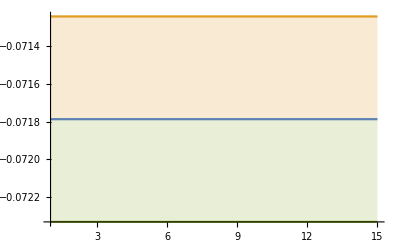

```mathematica
Plot[{fitData[[1]]//.Around[x_,y_]:>x,{fitData[[1]]//.Around[x_,y_]:>x+y,fitData[[1]]//.Around[x_,y_]:>x-y}},{x,1,15},Filling->{3->{1},2->{1}}]
```

```mathematica
SpoilHWFLOPlotN3=Show[Plot[{fitData[[1]]//.Around[x_,y_]:>x,{fitData[[1]]//.Around[x_,y_]:>x+y,fitData[[1]]//.Around[x_,y_]:>x-y}},{x,1,Length[meanErr2[[5]]]},Filling->{3->{1},2->{1}},PlotRange->{-1,.1}],ListPlot[{Table[{τSteps[[1,i]],meanErr2[[1,i]]},{i,1,Length[meanErr2[[1]]]}],Table[{τSteps[[2,i]],meanErr2[[2,i]]},{i,1,Length[meanErr2[[2]]]}],Table[{τSteps[[3,i]],meanErr2[[3,i]]},{i,1,Length[meanErr2[[3]]]}],Table[{τSteps[[4,i]],meanErr2[[4,i]]},{i,1,Length[meanErr2[[4]]]}],Table[{τSteps[[5,i]],meanErr2[[5,i]]},{i,1,Length[meanErr2[[5]]]}]},PlotRange->{-.1,-0.005},PlotLegends->Placed[αLegendLO,{0.5,0.1}],PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]],markerlist[[4]],markerlist[[5]]},IntervalMarkersStyle->{ColorData[97][3]},PlotStyle->{ColorData[97][3]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau_{\\text{steps}}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]},PlotLabel->MaTeX["N=3(\\text{LO})",Magnification->1.2]]
```

-Graphics-

#### QCD NNLO - gauss

```mathematica
Nf4α1LoopMid
Nf4α1LoopStepTab={393,393,393,393,393};
NWalkers=200;
Nf4α1LoopBig={0.225626,0.225626,0.225626,0.225626,0.225626};
aList={1,2,3,4,5};
```

{0.21556,0.220566,0.22639,0.233299,0.241701,0.252265,0.266178,0.285833}

```mathematica
csvData=Table[Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfgauss.csv"],{xx,1,Length[aList]}]
```

({mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.11737926249916168, -0.11693347849798458, -0.11925885080702511, -0.12363679470983714, -0.12442569411675898, -0.12210595226024243, -0.1199067736845063, -0.12092698282698239, -0.12099847879284306, -0.13111150131104746, -0.12499807585460676, -0.12527046189627247, -0.1287634411981841, -0.12660475619941097, -0.12620142524515204, -0.1276610841171603, -0.12675920783072514, -0.13401084406675456, -0.12634651860184903, -0.1388706516165822, -0.13799147033195142, -0.14898113391891019, -0.14511732477584952, -0.15059056503120927, -0.14684838621424542, -0.14633889967739758, -0.13105021016604151, -0.1289231411769311, -0.12639981756325985, -0.11838808629056058, -0.12303446309881594, -0.11739074419092119, -0.11601207317977362, -0.12178774035591236, -0.11634054094727417, -0.11920848085174775],[0.011543645776373622, 0.015847545371615875, 0.024505922779824378, 0.03620010372605913, 0.057057756729739714, 0.064101287878018, 0.08041402109198728, 0.10634684763715987, 0.14302986025810588, 0.2681524625811016, 0.28148457830795576, 0.3857304135326544, 0.5765937542676248, 0.7115450963052259, 0.9307961680315394, 1.2641600195658351, 1.6769170416888728, 3.352665497637168, 3.199315176239967, 6.471424320036356, 9.872834582105284, 20.02915747091897, 26.082622693168524, 43.330775328506974, 53.53293392497548, 83.29431887654339, 87.95469024716503, 102.96041554567181, 128.23135120281222, 140.2710082983356, 202.92946653961317, 242.92989455780176, 318.5344118821102, 455.2630617263909, 478.3628438157283, 688.6305750999884],-0.118336,0.000650625,0.405698}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.08190699762173155, -0.08555204672312439, -0.08421354420806461, -0.086165586838753, -0.08779007406930237, -0.09003809078766024, -0.09024417694573086, -0.0882307853224777, -0.08968025297440212, -0.0938083688388584, -0.09736542286114411, -0.09451982546255686, -0.09503459638292037, -0.10015551409405296, -0.10285869635798739, -0.10776635119739814, -0.10624505938433335, -0.104151041747984, -0.1150285528148022, -0.1121898298771645, -0.11008477057906034, -0.11189571936337342, -0.10942984050843768, -0.1143032667148455, -0.11883215405085694, -0.1094954479264322, -0.10983984686049642, -0.10450616485941408, -0.11073259051148707, -0.10360981836574445, -0.11011417928634427, -0.1296051834892659, -0.12138130442678677, -0.11549572833737763, -0.11247119346524125, -0.1127785652711651],[0.007822095006030937, 0.014470316765720803, 0.014972325441421429, 0.022973603727349225, 0.03227294866049803, 0.042516331299212264, 0.05455277035223941, 0.061215285147368764, 0.08973058148813409, 0.1269091274160733, 0.17881615918655983, 0.18402784152107826, 0.23824709503944586, 0.37011978180420635, 0.5387652597185826, 0.807620199780096, 1.0021289497761692, 1.253619602525145, 2.075103411237138, 2.391316289626071, 2.942577345844371, 4.018555649926368, 4.628354208951088, 5.992418043445475, 8.275229679233641, 9.58662832716563, 11.395705905513452, 12.939269608576122, 16.843608128428798, 19.305459582432732, 26.146169062612575, 45.11569168542311, 54.20322004213701, 66.99660530216201, 79.63404927992327, 101.12545418541379],-0.0829323,0.00120908,0.306723}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.06194000151336742, -0.06250283505754112, -0.06290268589703932, -0.063513066072701, -0.06403778688653596, -0.06507818076192926, -0.06506562646358255, -0.06585019500842355, -0.06898064523521759, -0.06966866567191225, -0.07106118065405366, -0.07046338733960904, -0.07328617987503949, -0.07608030411990195, -0.07638973075216, -0.07664936049750927, -0.08461225640372545, -0.08682295209400034, -0.10404657367221018, -0.08619865239717392, -0.09402649328385361, -0.10315923030655753, -0.08877776064640522, -0.08359304329203696, -0.0830927875271919, -0.08291141168794104, -0.08433819686310182, -0.08626408970342699, -0.0895095275258625, -0.08499436100596192, -0.0845861289225896, -0.08580841835825435, -0.0865747817069824, -0.08805340816991807, -0.08955547868512698, -0.08544687711545049],[0.003904320725538952, 0.004845359061454424, 0.00556876758707469, 0.006716169162251212, 0.007939630170526674, 0.010221530282633607, 0.012283712305386829, 0.015612994513238658, 0.02356185391660495, 0.02906932634096399, 0.03689016866251181, 0.04346394703361866, 0.05895137406270035, 0.08161176915572094, 0.1038523875147814, 0.13055613746494255, 0.23562671960417475, 0.33800206958928997, 0.7551272737058772, 0.5192144662907727, 0.8237248240966267, 1.3455188150345574, 1.1777173257476974, 1.2586643422477366, 1.4764619129114431, 1.7844161492405008, 2.1670874690050694, 2.8368896334029707, 3.6406024104800654, 4.083440411062534, 4.8757549194658045, 5.98194661805793, 7.092349852767744, 8.708092546638149, 10.904835339582434, 12.0222087953312],-0.064944,0.000913971,0.317965}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.05112674789970065, -0.051952704025560334, -0.05331619585364478, -0.05408748626748751, -0.056067928892317244, -0.05692726904811784, -0.05812009689480805, -0.057602566808092275, -0.05876739355374881, -0.06024601896923196, -0.060197468586288876, -0.06209121842194298, -0.061798269462979345, -0.06399787038830473, -0.0655313804062104, -0.06768715964126241, -0.07087274085637417, -0.07117582947725543, -0.07088936605695827, -0.07611932635419144, -0.07624895905221811, -0.08216893194460709, -0.0822408977565606, -0.08105149016161511, -0.08207022749755861, -0.0812863460467594, -0.076947111608142, -0.07554924481903105, -0.07580745348089482, -0.0740358954827124, -0.07394502733154353, -0.07307261687453499, -0.07419140024858399, -0.07562349298140755, -0.07529741865593483, -0.07843006557885508],[0.0026328240995981394, 0.003559841635115897, 0.004606165613427017, 0.00583416454401271, 0.00793409731163183, 0.010372053251422361, 0.013358502366366353, 0.0161391257986487, 0.019948361256831054, 0.026291907754377022, 0.030426424242757984, 0.04123213397030749, 0.047692810203322576, 0.06607972738484977, 0.08746425662477104, 0.11693303993155099, 0.16084347289069953, 0.19749452178535426, 0.22747536085071784, 0.337638342985253, 0.39516023511349097, 0.5884003081642557, 0.6999773103482207, 0.8519427540011643, 1.1227554943637807, 1.327026290081972, 1.3825233701734, 1.574310221805795, 1.895333673495692, 2.132834845745537, 2.5494394833390475, 2.919154793849155, 3.477785326611726, 4.226878167587055, 4.896463364819599, 6.337025573535621],-0.0509714,0.000767194,0.34582}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.04418797179028522, -0.044409118478739545, -0.04527661786985393, -0.04543693466512349, -0.04648209117097831, -0.04802025947927257, -0.048526863509435, -0.04810739199712731, -0.04888419608514156, -0.04900891231116533, -0.04965648212614755, -0.052273546334900334, -0.05362417815278104, -0.053275756233349146, -0.05313048949881789, -0.05279175439877274, -0.05257391841101352, -0.05323361708717136, -0.053992036408985984, -0.054219379892101814, -0.05563294289823002, -0.05684903463302257, -0.056332201386430386, -0.058289494832582736, -0.058917063793439535, -0.058669450682504516, -0.05897415373548364, -0.05893350264502388, -0.05983254361714915, -0.060011094582205354, -0.06125296970509906, -0.06204216197963393, -0.06384584657161294, -0.06656969709408485, -0.06920299920070501, -0.06779213832708572],[0.0022026047484433094, 0.002560258361034866, 0.00320850124175818, 0.003755081503063947, 0.004689645351432237, 0.006352715838208185, 0.007535246796663532, 0.008296651086594442, 0.010170196294710958, 0.011783765221010664, 0.014118114425110202, 0.02041847306265802, 0.026250279727996973, 0.02891104806108948, 0.03337134043812324, 0.03609870220040246, 0.04016865518975333, 0.046846852265606, 0.056356948591560416, 0.0650309846762486, 0.07854995770415452, 0.09254431789845882, 0.10143762408079049, 0.1272366225365228, 0.151310194760329, 0.16770762307191261, 0.19493859735410646, 0.22280798329136245, 0.26493242812723755, 0.3082921548488112, 0.37124387336986264, 0.4393514596123307, 0.5267968115843839, 0.6561290326213073, 0.8405964191701963, 0.9198505711643313],-0.0441548,0.00069997,0.358203})

```mathematica
meanErr=Table[Table[csvData[[xx,2,yy]]//StringSplit[#,{",","[","]"}]&,{yy,1,2}],{xx,1,Length[aList]}]
```

({-0.11737926249916168, -0.11693347849798458, -0.11925885080702511, -0.12363679470983714, -0.12442569411675898, -0.12210595226024243, -0.1199067736845063, -0.12092698282698239, -0.12099847879284306, -0.13111150131104746, -0.12499807585460676, -0.12527046189627247, -0.1287634411981841, -0.12660475619941097, -0.12620142524515204, -0.1276610841171603, -0.12675920783072514, -0.13401084406675456, -0.12634651860184903, -0.1388706516165822, -0.13799147033195142, -0.14898113391891019, -0.14511732477584952, -0.15059056503120927, -0.14684838621424542, -0.14633889967739758, -0.13105021016604151, -0.1289231411769311, -0.12639981756325985, -0.11838808629056058, -0.12303446309881594, -0.11739074419092119, -0.11601207317977362, -0.12178774035591236, -0.11634054094727417, -0.11920848085174775} | {0.011543645776373622, 0.015847545371615875, 0.024505922779824378, 0.03620010372605913, 0.057057756729739714, 0.064101287878018, 0.08041402109198728, 0.10634684763715987, 0.14302986025810588, 0.2681524625811016, 0.28148457830795576, 0.3857304135326544, 0.5765937542676248, 0.7115450963052259, 0.9307961680315394, 1.2641600195658351, 1.6769170416888728, 3.352665497637168, 3.199315176239967, 6.471424320036356, 9.872834582105284, 20.02915747091897, 26.082622693168524, 43.330775328506974, 53.53293392497548, 83.29431887654339, 87.95469024716503, 102.96041554567181, 128.23135120281222, 140.2710082983356, 202.92946653961317, 242.92989455780176, 318.5344118821102, 455.2630617263909, 478.3628438157283, 688.6305750999884}
{-0.08190699762173155, -0.08555204672312439, -0.08421354420806461, -0.086165586838753, -0.08779007406930237, -0.09003809078766024, -0.09024417694573086, -0.0882307853224777, -0.08968025297440212, -0.0938083688388584, -0.09736542286114411, -0.09451982546255686, -0.09503459638292037, -0.10015551409405296, -0.10285869635798739, -0.10776635119739814, -0.10624505938433335, -0.104151041747984, -0.1150285528148022, -0.1121898298771645, -0.11008477057906034, -0.11189571936337342, -0.10942984050843768, -0.1143032667148455, -0.11883215405085694, -0.1094954479264322, -0.10983984686049642, -0.10450616485941408, -0.11073259051148707, -0.10360981836574445, -0.11011417928634427, -0.1296051834892659, -0.12138130442678677, -0.11549572833737763, -0.11247119346524125, -0.1127785652711651} | {0.007822095006030937, 0.014470316765720803, 0.014972325441421429, 0.022973603727349225, 0.03227294866049803, 0.042516331299212264, 0.05455277035223941, 0.061215285147368764, 0.08973058148813409, 0.1269091274160733, 0.17881615918655983, 0.18402784152107826, 0.23824709503944586, 0.37011978180420635, 0.5387652597185826, 0.807620199780096, 1.0021289497761692, 1.253619602525145, 2.075103411237138, 2.391316289626071, 2.942577345844371, 4.018555649926368, 4.628354208951088, 5.992418043445475, 8.275229679233641, 9.58662832716563, 11.395705905513452, 12.939269608576122, 16.843608128428798, 19.305459582432732, 26.146169062612575, 45.11569168542311, 54.20322004213701, 66.99660530216201, 79.63404927992327, 101.12545418541379}
{-0.06194000151336742, -0.06250283505754112, -0.06290268589703932, -0.063513066072701, -0.06403778688653596, -0.06507818076192926, -0.06506562646358255, -0.06585019500842355, -0.06898064523521759, -0.06966866567191225, -0.07106118065405366, -0.07046338733960904, -0.07328617987503949, -0.07608030411990195, -0.07638973075216, -0.07664936049750927, -0.08461225640372545, -0.08682295209400034, -0.10404657367221018, -0.08619865239717392, -0.09402649328385361, -0.10315923030655753, -0.08877776064640522, -0.08359304329203696, -0.0830927875271919, -0.08291141168794104, -0.08433819686310182, -0.08626408970342699, -0.0895095275258625, -0.08499436100596192, -0.0845861289225896, -0.08580841835825435, -0.0865747817069824, -0.08805340816991807, -0.08955547868512698, -0.08544687711545049} | {0.003904320725538952, 0.004845359061454424, 0.00556876758707469, 0.006716169162251212, 0.007939630170526674, 0.010221530282633607, 0.012283712305386829, 0.015612994513238658, 0.02356185391660495, 0.02906932634096399, 0.03689016866251181, 0.04346394703361866, 0.05895137406270035, 0.08161176915572094, 0.1038523875147814, 0.13055613746494255, 0.23562671960417475, 0.33800206958928997, 0.7551272737058772, 0.5192144662907727, 0.8237248240966267, 1.3455188150345574, 1.1777173257476974, 1.2586643422477366, 1.4764619129114431, 1.7844161492405008, 2.1670874690050694, 2.8368896334029707, 3.6406024104800654, 4.083440411062534, 4.8757549194658045, 5.98194661805793, 7.092349852767744, 8.708092546638149, 10.904835339582434, 12.0222087953312}
{-0.05112674789970065, -0.051952704025560334, -0.05331619585364478, -0.05408748626748751, -0.056067928892317244, -0.05692726904811784, -0.05812009689480805, -0.057602566808092275, -0.05876739355374881, -0.06024601896923196, -0.060197468586288876, -0.06209121842194298, -0.061798269462979345, -0.06399787038830473, -0.0655313804062104, -0.06768715964126241, -0.07087274085637417, -0.07117582947725543, -0.07088936605695827, -0.07611932635419144, -0.07624895905221811, -0.08216893194460709, -0.0822408977565606, -0.08105149016161511, -0.08207022749755861, -0.0812863460467594, -0.076947111608142, -0.07554924481903105, -0.07580745348089482, -0.0740358954827124, -0.07394502733154353, -0.07307261687453499, -0.07419140024858399, -0.07562349298140755, -0.07529741865593483, -0.07843006557885508} | {0.0026328240995981394, 0.003559841635115897, 0.004606165613427017, 0.00583416454401271, 0.00793409731163183, 0.010372053251422361, 0.013358502366366353, 0.0161391257986487, 0.019948361256831054, 0.026291907754377022, 0.030426424242757984, 0.04123213397030749, 0.047692810203322576, 0.06607972738484977, 0.08746425662477104, 0.11693303993155099, 0.16084347289069953, 0.19749452178535426, 0.22747536085071784, 0.337638342985253, 0.39516023511349097, 0.5884003081642557, 0.6999773103482207, 0.8519427540011643, 1.1227554943637807, 1.327026290081972, 1.3825233701734, 1.574310221805795, 1.895333673495692, 2.132834845745537, 2.5494394833390475, 2.919154793849155, 3.477785326611726, 4.226878167587055, 4.896463364819599, 6.337025573535621}
{-0.04418797179028522, -0.044409118478739545, -0.04527661786985393, -0.04543693466512349, -0.04648209117097831, -0.04802025947927257, -0.048526863509435, -0.04810739199712731, -0.04888419608514156, -0.04900891231116533, -0.04965648212614755, -0.052273546334900334, -0.05362417815278104, -0.053275756233349146, -0.05313048949881789, -0.05279175439877274, -0.05257391841101352, -0.05323361708717136, -0.053992036408985984, -0.054219379892101814, -0.05563294289823002, -0.05684903463302257, -0.056332201386430386, -0.058289494832582736, -0.058917063793439535, -0.058669450682504516, -0.05897415373548364, -0.05893350264502388, -0.05983254361714915, -0.060011094582205354, -0.06125296970509906, -0.06204216197963393, -0.06384584657161294, -0.06656969709408485, -0.06920299920070501, -0.06779213832708572} | {0.0022026047484433094, 0.002560258361034866, 0.00320850124175818, 0.003755081503063947, 0.004689645351432237, 0.006352715838208185, 0.007535246796663532, 0.008296651086594442, 0.010170196294710958, 0.011783765221010664, 0.014118114425110202, 0.02041847306265802, 0.026250279727996973, 0.02891104806108948, 0.03337134043812324, 0.03609870220040246, 0.04016865518975333, 0.046846852265606, 0.056356948591560416, 0.0650309846762486, 0.07854995770415452, 0.09254431789845882, 0.10143762408079049, 0.1272366225365228, 0.151310194760329, 0.16770762307191261, 0.19493859735410646, 0.22280798329136245, 0.26493242812723755, 0.3082921548488112, 0.37124387336986264, 0.4393514596123307, 0.5267968115843839, 0.6561290326213073, 0.8405964191701963, 0.9198505711643313})

```mathematica
meanErr2=Table[Table[Around[meanErr[[xx,1,yy]]//ToExpression,meanErr[[xx,2,yy]]//ToExpression],{yy,1,Length[meanErr[[xx,1]]]}],{xx,1,Length[aList]}]
```

(-0.1170.012 | -0.1170.016 | -0.1190.025 | -0.120.04 | -0.120.06 | -0.120.06 | -0.120.08 | -0.120.11 | -0.120.14 | -0.130.27 | -0.120.28 | -0.10.4 | -0.10.6 | -0.10.7 | -0.10.9 | -0.11.3 | -0.11.7 | -0.13.4 | -0.13.2 | 0.6. | 0.10. | 0.20. | 0.26. | 0.43. | 0.54. | 0.83. | 0.88. | 0.103. | 0.128. | 0.140. | 0.203. | 0.243. | 0.319. | 0.455. | 0.478. | 0.689.
-0.0820.008 | -0.0860.014 | -0.0840.015 | -0.0860.023 | -0.0880.032 | -0.090.04 | -0.090.05 | -0.090.06 | -0.090.09 | -0.090.13 | -0.100.18 | -0.090.18 | -0.100.24 | -0.10.4 | -0.10.5 | -0.10.8 | -0.11.0 | -0.11.3 | -0.12.1 | -0.12.4 | -0.12.9 | 0.4. | 0.5. | 0.6. | 0.8. | 0.10. | 0.11. | 0.13. | 0.17. | 0.19. | 0.26. | 0.45. | 0.54. | 0.67. | 0.80. | 0.101.
-0.0620.004 | -0.0630.005 | -0.0630.006 | -0.0640.007 | -0.0640.008 | -0.0650.010 | -0.0650.012 | -0.0660.016 | -0.0690.024 | -0.0700.029 | -0.070.04 | -0.070.04 | -0.070.06 | -0.080.08 | -0.080.10 | -0.080.13 | -0.080.24 | -0.090.34 | -0.10.8 | 0.00.5 | 0.00.8 | -0.11.3 | 0.01.2 | 0.01.3 | 0.01.5 | 0.01.8 | 0.02.2 | 0.02.8 | 0.4. | 0.4. | 0.5. | 0.6. | 0.7. | 0.9. | 0.11. | 0.12.
-0.05110.0026 | -0.0520.004 | -0.0530.005 | -0.0540.006 | -0.0560.008 | -0.0570.010 | -0.0580.013 | -0.0580.016 | -0.0590.020 | -0.0600.026 | -0.0600.030 | -0.060.04 | -0.060.05 | -0.060.07 | -0.070.09 | -0.070.12 | -0.070.16 | -0.070.20 | -0.070.23 | -0.080.34 | 0.00.4 | 0.00.6 | 0.00.7 | 0.00.9 | 0.01.1 | 0.01.3 | 0.01.4 | 0.01.6 | 0.01.9 | 0.02.1 | 0.02.5 | 0.02.9 | 0.03.5 | 0.4. | 0.5. | 0.6.
-0.04420.0022 | -0.04440.0026 | -0.04530.0032 | -0.0450.004 | -0.0460.005 | -0.0480.006 | -0.0490.008 | -0.0480.008 | -0.0490.010 | -0.0490.012 | -0.0500.014 | -0.0520.020 | -0.0540.026 | -0.0530.029 | -0.0530.033 | -0.050.04 | -0.050.04 | -0.050.05 | -0.050.06 | -0.050.07 | -0.060.08 | -0.060.09 | -0.060.10 | -0.060.13 | -0.060.15 | -0.060.17 | -0.060.19 | -0.060.22 | -0.060.26 | -0.060.31 | 0.00.4 | 0.00.4 | 0.00.5 | 0.00.7 | 0.00.8 | 0.00.9)

```mathematica
τSteps=Table[Table[xx,{xx,1,Length[meanErr2[[yy]]]}],{yy,1,Length[meanErr2]}]
```

(1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36)

```mathematica
fitData=Table[Around[Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfgauss.csv"][[2,3]],Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfgauss.csv"][[2,4]]],{xx,1,Length[aList]}]
```

{-0.11830.0007,-0.08290.0012,-0.06490.0009,-0.05100.0008,-0.04420.0007}

```mathematica
αLegendLO=PointLegend[Table[Directive[ColorData[97][1]],{ii,5}],{MaTeX["a=1",Magnification->0.8],MaTeX["a=2",Magnification->0.8],MaTeX["a=3",Magnification->0.8],MaTeX["a=4",Magnification->0.8],MaTeX["a=5",Magnification->0.8]},LegendMarkers->Table[Style[markerlist[[ii]],14,Bold,ColorData[97][3]],{ii,5}],LegendLayout->"Row",LegendMargins->0.5,LegendFunction->frame]
```

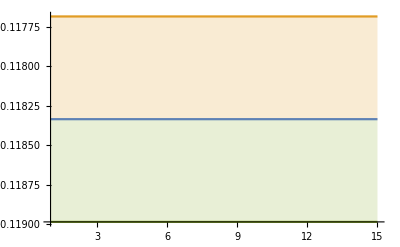

```mathematica
Plot[{fitData[[1]]//.Around[x_,y_]:>x,{fitData[[1]]//.Around[x_,y_]:>x+y,fitData[[1]]//.Around[x_,y_]:>x-y}},{x,1,15},Filling->{3->{1},2->{1}}]
```

```mathematica
SpoilHWFLOPlotN3=Show[Plot[{fitData[[1]]//.Around[x_,y_]:>x,{fitData[[1]]//.Around[x_,y_]:>x+y,fitData[[1]]//.Around[x_,y_]:>x-y}},{x,1,Length[meanErr2[[5]]]},Filling->{3->{1},2->{1}},PlotRange->{-1,1}],ListPlot[{Table[{τSteps[[1,i]],meanErr2[[1,i]]},{i,1,Length[meanErr2[[1]]]}],Table[{τSteps[[2,i]],meanErr2[[2,i]]},{i,1,Length[meanErr2[[2]]]}],Table[{τSteps[[3,i]],meanErr2[[3,i]]},{i,1,Length[meanErr2[[3]]]}],Table[{τSteps[[4,i]],meanErr2[[4,i]]},{i,1,Length[meanErr2[[4]]]}],Table[{τSteps[[5,i]],meanErr2[[5,i]]},{i,1,Length[meanErr2[[5]]]}]},PlotRange->{-.03,-0.005},PlotLegends->Placed[αLegendLO,{0.5,0.1}],PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]],markerlist[[4]],markerlist[[5]]},IntervalMarkersStyle->{ColorData[97][3]},PlotStyle->{ColorData[97][3]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau_{\\text{steps}}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]},PlotLabel->MaTeX["N=3(\\text{LO})",Magnification->1.2]]
```

-Graphics-